```mathematica
(*■*)
```

## 計算結果

```mathematica
Clear["Global`*"]
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"../../../../mathematica_utilities/mathematica_plot_options.nb"}]]
(*json="/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.json"*)
json ="/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water_no_float0d09/result.json"
jsonInfo[json]
```

Available:{plot2Doption,framelabel[xlabel_String,ylabel_String,size_:20],importData,jsonInfo,interpolateAndFourier,interpolateAndFourierTr}

/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water_no_float0d09/result.json

no. | title | length
1 | cpu_time | 606
2 | eq_of_motion | 606
3 | gauge0_intersection | 606
4 | gauge10_intersection | 606
5 | gauge11_intersection | 606
6 | gauge12_intersection | 606
7 | gauge13_intersection | 606
8 | gauge14_intersection | 606
9 | gauge15_intersection | 606
10 | gauge16_intersection | 606
11 | gauge17_intersection | 606
12 | gauge18_intersection | 606
13 | gauge19_intersection | 606
14 | gauge1_intersection | 606
15 | gauge20_intersection | 606
16 | gauge21_intersection | 606
17 | gauge22_intersection | 606
18 | gauge23_intersection | 606
19 | gauge2_intersection | 606
20 | gauge3_intersection | 606
21 | gauge4_intersection | 606
22 | gauge5_intersection | 606
23 | gauge6_intersection | 606
24 | gauge7_intersection | 606
25 | gauge8_intersection | 606
26 | gauge9_intersection | 606
27 | simulation_time | 606
28 | wall_clock_time | 606
29 | water_E | 606
30 | water_EK | 606
31 | water_EP | 606
32 | water_face_size | 606
33 | water_point_size | 606
34 | water_volume | 606

```mathematica
(*i=1;
ListPlot[
Table[With[{name="float"<>ToString[i]<>"_COM"},importData[json,name,1]-importData[json,name,1][[1]]],{i,1,20,1}]
,Joined->True
]
ListPlot[
Table[With[{name="float"<>ToString[i]<>"_COM"},importData[json,name,2]-importData[json,name,2][[1]]],{i,1,20,1}]
,Joined->True
]
ListPlot[
Table[With[{name="float"<>ToString[i]<>"_COM"},importData[json,name,3]-importData[json,name,3][[1]]],{i,1,20,1}]
,Joined->True
]*)
```

```mathematica
(*Tshift=6.5*)
Tshift=-7.55

ExpHeave={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_heave_exp.csv"];
SimuHeave={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_heave_simu.csv"];
ExpSway={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_sway_exp.csv"];
SimuSway={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_sway_simu.csv"];
ExpRoll={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_roll_exp.csv"];
SimuRoll={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_roll_simu.csv"];
ExpSf={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_Sf_exp.csv"];
SimuSf={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_Sf_simu.csv"];
SimuRm={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_Rm_simu.csv"];
SimuHf={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_Hf_simu.csv"];
```

-7.55

```mathematica
ζa=0.05/2;
{B,L}={0.74,0.997};(*{Bredth,Length}*)
g=9.8;
ρ=1000;
λ=1.8;
ρgLBζa=ρ*g*L*B*ζa

h=5.;
Omega[k_,h_]:=Sqrt[g*k*Tanh[h*k]];
Tw=T/.Solve[Omega[2π/λ,h]==2π/T,T][[1]];

k=2π/L;
ω=Omega[k,h];
```

180.756

Solve::ratnz: Solveは厳密でない係数の系を解くことができませんでした．解は対応する厳密系を解き，結果を数値に変換することで得られました．

## 計算結果

```mathematica
fourColorScheme={
{Thick,Opacity[0.8],Blue(*RGBColor[55/255,126/255,184/255]*)},
{Thickness[0.002],Opacity[0.8],Red(*RGBColor[255/255,127/255,0]*)},
{Thickness[0.002],RGBColor[77/255,175/255,74/255]},
{Thickness[0.002],RGBColor[247/255,129/255,191/255]}};
threeColorScheme={{Thick,RGBColor[55/255,126/255,184/255]},RGBColor[255/255,127/255,0],RGBColor[77/255,175/255,74/255]};
plotxrange={{0,30},All};
opt={FrameStyle->Directive[FontSize->16,Black,Thickness[0.002]],
Epilog->{Line[{{-100,0},{100,0}}]},
Joined->{True,True,True,False},
PlotRange->plotxrange,
GridLines->All,
GridLinesStyle->Directive[Gray,AbsoluteThickness[0.001]],
ImageSize->1000,
(*PlotStyle->{{Blue},{Red},{Darker[Green]}},*)
PlotStyle->fourColorScheme,
AspectRatio->1/8};
(*メッシュと計算の収束*)
```

```mathematica
simutime=importData[json,"simulation_time"]/Tw;
```

```mathematica
(*プロット*)
Column@Table[
ListLogPlot[Transpose[{Range[Length[#]],#}]&@@@importData[json,"eq_of_motion"][[;;100]],
PlotLabel->json,
PlotRange->Automatic,
PlotStyle->Directive[Thin,Black,Opacity[0.2]],
FrameTicks->{{All,Automatic},{Table[i,{i,1,100,1}],None}},
AspectRatio->1/2,
FrameLabel->{
Style["Number of evaluations",FontSize->20,FontFamily->"Times"],
Rotate[Style["error |Q|",FontSize->20,FontFamily->"Times"],-π/2]},
Frame->True,
Evaluate[plot2Doption]
],{json,
{json="/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.json",
"/Volumes/home/BEM/20240301土木学会東北支部/Tanizawa1996_H0d05_L1d8_potential_multiple_water_mod_coarse/result.json"}}]
```

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::take: eq_of_motion/.$Failedの1から100の位置が取れません．

Transpose::nmtx: {{},eq_of_motion}の最初の2個のレベルは転置できません．

Transpose::nmtx: {{},1}の最初の2個のレベルは転置できません．

Part::pkspec1: 式Transpose[{{},1}]は部分指定に使用できません．

ListLogPlot::lpn: Transpose[{{},eq_of_motion}]⟦Transpose[{{},1}]⟧は数値のリストあるいは数値の対のリストではありません．

General::stop: この計算中に，ListLogPlot::lpnのこれ以上の出力は表示されません．

Import::nffil: Importの最中にファイル/Volumes/home/BEM/20240301土木学会東北支部/Tanizawa1996_H0d05_L1d8_potential_multiple_water_mod_coarse/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::take: eq_of_motion/.$Failedの1から100の位置が取れません．

Transpose::nmtx: {{},eq_of_motion}の最初の2個のレベルは転置できません．

General::stop: この計算中に，Transpose::nmtxのこれ以上の出力は表示されません．

Part::pkspec1: 式Transpose[{{},1}]は部分指定に使用できません．

ListLogPlot[Transpose[{{},eq_of_motion}]⟦Transpose[{{},1}]⟧,PlotLabel→/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.json,PlotRange→Automatic,PlotStyle→Directive[Thickness[Tiny],GrayLevel[0],Opacity[0.2]],FrameTicks→{{All,Automatic},{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100},None}},AspectRatio→1/2,FrameLabel→{Number of evaluations,error |Q|},Frame→True,{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]
ListLogPlot[Transpose[{{},eq_of_motion}]⟦Transpose[{{},1}]⟧,PlotLabel→/Volumes/home/BEM/20240301土木学会東北支部/Tanizawa1996_H0d05_L1d8_potential_multiple_water_mod_coarse/result.json,PlotRange→Automatic,PlotStyle→Directive[Thickness[Tiny],GrayLevel[0],Opacity[0.2]],FrameTicks→{{All,Automatic},{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100},None}},AspectRatio→1/2,FrameLabel→{Number of evaluations,error |Q|},Frame→True,{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]

この計算条件では，準ニュートン法の繰り返し計算7回で | Q | < 10^-12 にまで収束した．
浮体を増やすと，収束の速さは遅くなるものの収束する．

```mathematica
opt=Append[opt,{PlotStyle->plotstyle,
PlotRange->{All,Automatic},
PlotLegends->{"Present","Tanizawa 1997","Experiment"}}];
```

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(float_force/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

General::stop: この計算中に，Import::nffilのこれ以上の出力は表示されません．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

General::stop: この計算中に，ReplaceAll::repsのこれ以上の出力は表示されません．

Part::partd: 部分指定(float_force/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

Part::partw: (float_force/.$Failed)⟦1;;All,3⟧の部分5は存在しません．

Transpose::nmtx: {(simulation_time/.$Failed)/Tw,(-(float_force/.$Failed)⟦1;;All,3⟧⟦5⟧+(float_force/.$Failed)⟦1;;All,3⟧)/(B g L ζa ρ)}の最初の2個のレベルは転置できません．

Transpose::nmtx: {(simulation_time/.$Failed)/Tw,(-1. (float_force/.$Failed)⟦1;;All,3⟧⟦5⟧+(float_force/.$Failed)⟦1;;All,3⟧)/(B g L ζa ρ)}の最初の2個のレベルは転置できません．

General::stop: この計算中に，Transpose::nmtxのこれ以上の出力は表示されません．

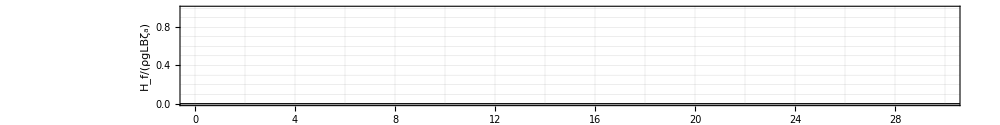

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(float_force/.$Failed)⟦1;;All,1⟧の長さはオブジェクトの深さを超えています．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

General::stop: この計算中に，Import::nffilのこれ以上の出力は表示されません．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

General::stop: この計算中に，ReplaceAll::repsのこれ以上の出力は表示されません．

Part::partd: 部分指定(float_force/.$Failed)⟦1;;All,1⟧の長さはオブジェクトの深さを超えています．

Part::partw: (float_force/.$Failed)⟦1;;All,1⟧の部分5は存在しません．

Transpose::nmtx: {(simulation_time/.$Failed)/Tw,(-(float_force/.$Failed)⟦1;;All,1⟧⟦5⟧+(float_force/.$Failed)⟦1;;All,1⟧)/(B g L ζa ρ)}の最初の2個のレベルは転置できません．

Transpose::nmtx: {(simulation_time/.$Failed)/Tw,(-1. (float_force/.$Failed)⟦1;;All,1⟧⟦5⟧+(float_force/.$Failed)⟦1;;All,1⟧)/(B g L ζa ρ)}の最初の2個のレベルは転置できません．

General::stop: この計算中に，Transpose::nmtxのこれ以上の出力は表示されません．

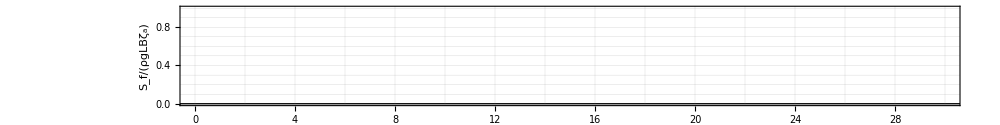

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(float_torque/.$Failed)⟦1;;All,2⟧の長さはオブジェクトの深さを超えています．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

General::stop: この計算中に，Import::nffilのこれ以上の出力は表示されません．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

General::stop: この計算中に，ReplaceAll::repsのこれ以上の出力は表示されません．

Part::partd: 部分指定(float_torque/.$Failed)⟦1;;All,2⟧の長さはオブジェクトの深さを超えています．

Part::partw: (float_torque/.$Failed)⟦1;;All,2⟧の部分15は存在しません．

Transpose::nmtx: {(simulation_time/.$Failed)/Tw,-(-(float_torque/.$Failed)⟦1;;All,2⟧⟦15⟧+(float_torque/.$Failed)⟦1;;All,2⟧)/(B^2 g L ζa ρ)}の最初の2個のレベルは転置できません．

Transpose::nmtx: {(simulation_time/.$Failed)/Tw,-(1. (-1. (float_torque/.$Failed)⟦1;;All,2⟧⟦15⟧+(float_torque/.$Failed)⟦1;;All,2⟧))/(B^2 g L ζa ρ)}の最初の2個のレベルは転置できません．

General::stop: この計算中に，Transpose::nmtxのこれ以上の出力は表示されません．

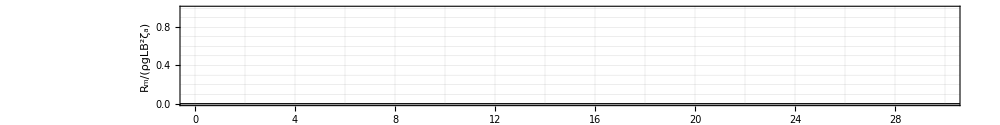

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(float_force/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

General::stop: この計算中に，Import::nffilのこれ以上の出力は表示されません．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

General::stop: この計算中に，ReplaceAll::repsのこれ以上の出力は表示されません．

Part::partd: 部分指定(float_force/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

Part::partw: (float_force/.$Failed)⟦1;;All,3⟧の部分5は存在しません．

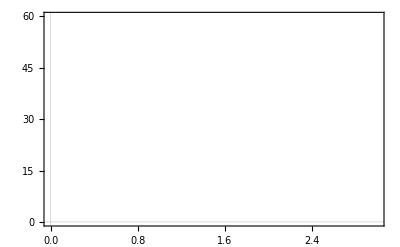

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(float_force/.$Failed)⟦1;;All,1⟧の長さはオブジェクトの深さを超えています．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

General::stop: この計算中に，Import::nffilのこれ以上の出力は表示されません．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

General::stop: この計算中に，ReplaceAll::repsのこれ以上の出力は表示されません．

Part::partd: 部分指定(float_force/.$Failed)⟦1;;All,1⟧の長さはオブジェクトの深さを超えています．

Part::partw: (float_force/.$Failed)⟦1;;All,1⟧の部分5は存在しません．

-Graphics-

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(float_torque/.$Failed)⟦1;;All,2⟧の長さはオブジェクトの深さを超えています．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

General::stop: この計算中に，Import::nffilのこれ以上の出力は表示されません．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

General::stop: この計算中に，ReplaceAll::repsのこれ以上の出力は表示されません．

Part::partd: 部分指定(float_torque/.$Failed)⟦1;;All,2⟧の長さはオブジェクトの深さを超えています．

Part::partw: (float_torque/.$Failed)⟦1;;All,2⟧の部分15は存在しません．

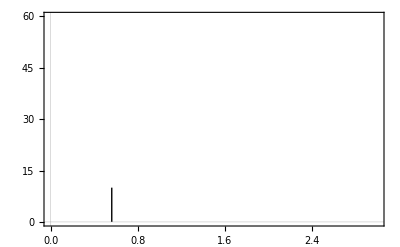

```mathematica
ListPlot[
Append[Table[{importData[json,"simulation_time"]/Tw,((importData[json,"float_force",i]-importData[json,"float_force",i][[5]])/(ρ*g*L*B*ζa))}ᵀ,{i,3,3,1}],
SimuHf],
Evaluate[opt],
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["H_f/(ρgLBζ_a)",FontSize->20,FontFamily->"Times"]},
PlotLegends->{"x","y","z"},
Evaluate[plot2Doption]
]

ListPlot[
Append[Table[{importData[json,"simulation_time"]/Tw,((importData[json,"float_force",i]-importData[json,"float_force",i][[5]])/(ρ*g*L*B*ζa))}ᵀ,{i,1,1,1}],
SimuSf],
Evaluate[opt],
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["S_f/(ρgLBζ_a)",FontSize->20,FontFamily->"Times"]},
PlotLegends->{"x","y","z"},
Evaluate[plot2Doption]
]

ListPlot[
Append[Table[{importData[json,"simulation_time"]/Tw,-((importData[json,"float_torque",i]-importData[json,"float_torque",i][[15]])/(ρ*g*L*B*B*ζa))}ᵀ,{i,2,2,1}],
SimuRm],
Evaluate[opt],
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["R_m/(ρgLB^2ζ_a)",FontSize->20,FontFamily->"Times"]},
PlotLegends->{"x","y","z"},
Evaluate[plot2Doption]
]


ListPlot[
{interpolateAndFourier[importData[json,"simulation_time"]/Tw,((importData[json,"float_force",3]-importData[json,"float_force",3][[5]])/(ρ*g*L*B*ζa)),{10,30}],
interpolateAndFourierTr[SimuHf,{10,30}]
},
PlotRange->{{0,3},All},
Evaluate[plot2Doption]
]

ListPlot[
{interpolateAndFourier[importData[json,"simulation_time"]/Tw,((importData[json,"float_force",1]-importData[json,"float_force",1][[5]])/(ρ*g*L*B*ζa)),{10,30}],
interpolateAndFourierTr[SimuSf,{10,30}]
},
PlotRange->{{0,3},All},
Evaluate[plot2Doption]
]

ListPlot[
{interpolateAndFourier[importData[json,"simulation_time"]/Tw,-((importData[json,"float_torque",2]-importData[json,"float_torque",2][[15]])/(ρ*g*L*B*B*ζa)),{15,30}],
interpolateAndFourierTr[SimuRm,{10,30}]
},
Epilog->Line[{{1/1.78,0},{1/1.78,10}}],
PlotRange->{{0,3},All},
Evaluate[plot2Doption]
]
```

浮体が流体から受ける，鉛直水平方向の力，y軸回転方向のトルクは，Tanizawa1997の結果とよく一致している．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

General::stop: この計算中に，Import::nffilのこれ以上の出力は表示されません．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

General::stop: この計算中に，ReplaceAll::repsのこれ以上の出力は表示されません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

Transpose::nmtx: {(simulation_time/.$Failed)/Tw,((float_COM/.$Failed)⟦1;;All,3⟧-(float_COM/.$Failed))/ζa}の最初の2個のレベルは転置できません．

Transpose::nmtx: {(simulation_time/.$Failed)/Tw,((float_COM/.$Failed)⟦1;;All,3⟧-1. (float_COM/.$Failed))/ζa}の最初の2個のレベルは転置できません．

General::stop: この計算中に，Transpose::nmtxのこれ以上の出力は表示されません．

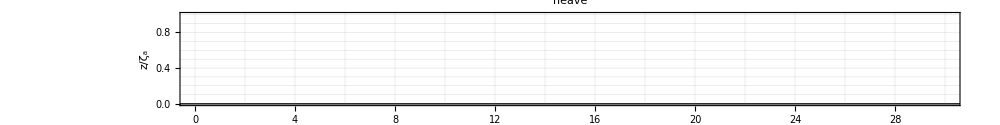

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,1⟧の長さはオブジェクトの深さを超えています．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

General::stop: この計算中に，Import::nffilのこれ以上の出力は表示されません．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

General::stop: この計算中に，ReplaceAll::repsのこれ以上の出力は表示されません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,1⟧の長さはオブジェクトの深さを超えています．

Transpose::nmtx: {(simulation_time/.$Failed)/Tw,((float_COM/.$Failed)⟦1;;All,1⟧-(float_COM/.$Failed))/ζa}の最初の2個のレベルは転置できません．

Transpose::nmtx: {(simulation_time/.$Failed)/Tw,((float_COM/.$Failed)⟦1;;All,1⟧-1. (float_COM/.$Failed))/ζa}の最初の2個のレベルは転置できません．

General::stop: この計算中に，Transpose::nmtxのこれ以上の出力は表示されません．

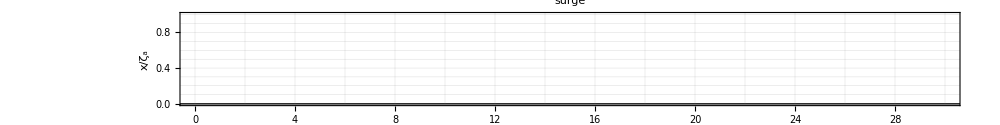

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Transpose::nmtx: {(simulation_time/.$Failed)/Tw,-(λ (float_pitch/.$Failed))/(2 π ζa)}の最初の2個のレベルは転置できません．

Transpose::nmtx: {(simulation_time/.$Failed)/Tw,-(0.1591549430918953 λ (float_pitch/.$Failed))/ζa}の最初の2個のレベルは転置できません．

Transpose::nmtx: {(simulation_time/.$Failed)/Tw,-(0.159155 λ (float_pitch/.$Failed))/ζa}の最初の2個のレベルは転置できません．

General::stop: この計算中に，Transpose::nmtxのこれ以上の出力は表示されません．

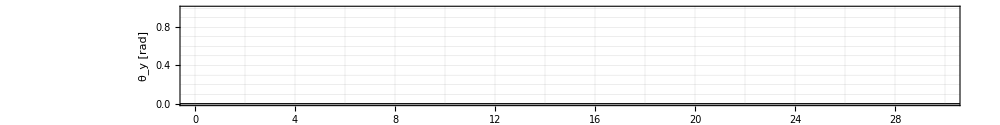

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

General::stop: この計算中に，Import::nffilのこれ以上の出力は表示されません．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

General::stop: この計算中に，ReplaceAll::repsのこれ以上の出力は表示されません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

-Graphics-

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,1⟧の長さはオブジェクトの深さを超えています．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

General::stop: この計算中に，Import::nffilのこれ以上の出力は表示されません．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

General::stop: この計算中に，ReplaceAll::repsのこれ以上の出力は表示されません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,1⟧の長さはオブジェクトの深さを超えています．

-Graphics-

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

-Graphics-

```mathematica
ListPlot[
{{importData[json,"simulation_time"]/Tw,(importData[json,"float_COM",3]-importData[json,"float_COM",3][[1]])/ζa}ᵀ,
SimuHeave,
ExpHeave},
Evaluate[opt],
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["z/ζ_a",FontSize->20,FontFamily->"Times"]},
PlotLabel->"heave",
Evaluate[plot2Doption]
]

ListPlot[
{{importData[json,"simulation_time"]/Tw,(importData[json,"float_COM",1]-importData[json,"float_COM",1][[1]])/ζa}ᵀ,
SimuSway,
ExpSway},
Evaluate[opt],
GridLines->{Table[i,{i,0.,6.,0.2}],Table[i,{i,-1.,1.,0.5}]},
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["x/ζ_a",FontSize->20,FontFamily->"Times"]},
PlotLabel->"surge",
Evaluate[plot2Doption]
]

k=2π/λ;
ListPlot[
{{importData[json,"simulation_time"]/Tw,-(importData[json,"float_pitch"])/(k*ζa)}ᵀ,
SimuRoll,
ExpRoll},
Evaluate[opt],
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["θ_y [rad]",FontSize->20,FontFamily->"Times"]},
Evaluate[plot2Doption]
]


ListPlot[
{interpolateAndFourier[importData[json,"simulation_time"]/Tw,(importData[json,"float_COM",3]-importData[json,"float_COM",3][[1]])/ζa,{10,30}],
interpolateAndFourierTr[SimuHeave,{10,30}]
},
PlotRange->{{0,3},All},
Evaluate[plot2Doption]
]

ListPlot[
{interpolateAndFourier[importData[json,"simulation_time"]/Tw,(importData[json,"float_COM",1]-importData[json,"float_COM",1][[1]])/ζa,{10,30}],
interpolateAndFourierTr[SimuSway,{10,30}]
},
PlotRange->{{0,3},All},
Evaluate[plot2Doption]
]

ListPlot[
{interpolateAndFourier[importData[json,"simulation_time"]/Tw,-(importData[json,"float_pitch"])/(k*ζa),{10,30}],
interpolateAndFourierTr[SimuRoll,{10,30}]
},
Epilog->Line[{{1/1.78,0},{1/1.78,10}}],
PlotRange->{{0,3},All},
Evaluate[plot2Doption]
]
```

ロール角を除き，浮体の並進移動は，Tanizawa1997の計算結果とよく一致している．一方の回転角度は，谷澤の結果よりも小さく

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(gauge0_intersection/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

Import::nffil: File /Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.json not found during Import.

ReplaceAll::reps: {$Failed} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification (gauge0_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge3_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge6_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge9_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Import::nffil: File /Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.json not found during Import.

ReplaceAll::reps: {$Failed} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification (gauge0_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge3_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge6_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge9_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Import::nffil: File /Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.json not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

ReplaceAll::reps: {$Failed} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge3_intersection/.$Failed)⟦1;;All,3⟧-(gauge3_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge6_intersection/.$Failed)⟦1;;All,3⟧-(gauge6_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge9_intersection/.$Failed)⟦1;;All,3⟧-(gauge9_intersection/.$Failed)} cannot be transposed.

Part::partd: Part specification (gauge0_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-1. (gauge0_intersection/.$Failed)} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListPlot::prng: Value of option PlotRange -> {Automatic,{-1.75 ζa,1.75 ζa}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::stop: Further output of ListPlot::prng will be suppressed during this calculation.

Import::nffil: File /Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.json not found during Import.

ReplaceAll::reps: {$Failed} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification (gauge12_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge15_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge18_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge21_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Import::nffil: File /Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.json not found during Import.

ReplaceAll::reps: {$Failed} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification (gauge12_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge15_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge18_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge21_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Import::nffil: File /Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.json not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

ReplaceAll::reps: {$Failed} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge12_intersection/.$Failed)⟦1;;All,3⟧-(gauge12_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge15_intersection/.$Failed)⟦1;;All,3⟧-(gauge15_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge18_intersection/.$Failed)⟦1;;All,3⟧-(gauge18_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge21_intersection/.$Failed)⟦1;;All,3⟧-(gauge21_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge12_intersection/.$Failed)⟦1;;All,3⟧-1. (gauge12_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge15_intersection/.$Failed)⟦1;;All,3⟧-1. (gauge15_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge18_intersection/.$Failed)⟦1;;All,3⟧-1. (gauge18_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge21_intersection/.$Failed)⟦1;;All,3⟧-1. (gauge21_intersection/.$Failed)} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListPlot::prng: Value of option PlotRange -> {Automatic,{-1.75 ζa,1.75 ζa}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

Part::partd: Part specification (gauge13_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge16_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge19_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge22_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ListPlot::prng: Value of option PlotRange -> {Automatic,{-1.75 ζa,1.75 ζa}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::stop: Further output of ListPlot::prng will be suppressed during this calculation.

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

General::stop: この計算中に，ReplaceAll::repsのこれ以上の出力は表示されません．

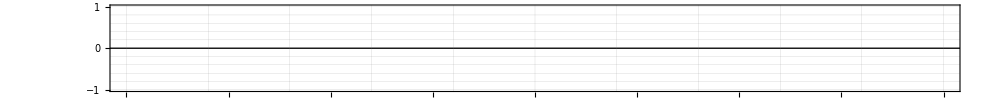
-Graphics-gauge0_intersection/.$Failed
-Graphics-gauge1_intersection/.$Failed
-Graphics-gauge2_intersection/.$Failed
-Graphics-gauge3_intersection/.$Failed
-Graphics-gauge4_intersection/.$Failed
-Graphics-gauge5_intersection/.$Failed
-Graphics-gauge6_intersection/.$Failed
-Graphics-gauge7_intersection/.$Failed
-Graphics-gauge8_intersection/.$Failed
-Graphics-gauge9_intersection/.$Failed
-Graphics-gauge10_intersection/.$Failed
-Graphics-gauge11_intersection/.$Failed
-Graphics-gauge12_intersection/.$Failed
-Graphics-gauge13_intersection/.$Failed
-Graphics-gauge14_intersection/.$Failed
-Graphics-gauge15_intersection/.$Failed
-Graphics-gauge16_intersection/.$Failed
-Graphics-gauge17_intersection/.$Failed
-Graphics-gauge18_intersection/.$Failed
-Graphics-gauge19_intersection/.$Failed
-Graphics-gauge20_intersection/.$Failed
-Graphics-gauge21_intersection/.$Failed
-Graphics-gauge22_intersection/.$Failed
-Graphics-gauge23_intersection/.$Failed

```mathematica
delt=0.67/(ω/k);
T=1.;
DATA1=importData[json,"gauge0_intersection",3];
Column[ParallelTable[
Module[{data,DATA,position},
data="gauge"<>ToString[i]<>"_intersection";
DATA=importData[json,data,3];
position=importData[json,data,1][[1]];
Labeled[
ListPlot[
{{importData[json,"simulation_time"],(DATA-DATA[[1]])}ᵀ,
{importData[json,"simulation_time"](*+(*0.295*)delt*i*),(DATA1-DATA1[[1]])}ᵀ
(*Table[{t,-ζa*Cos[2π/T*t-k*(position)]},{t,0,30,.1}]*)
},
(*FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["x/H_0",FontSize->20,FontFamily->"Times",Italic]},*)
AspectRatio->1/10,
PlotRange->{Automatic,1.75*{-ζa,ζa}},
Joined->{True,True,True,True,True},
Evaluate[opt],
PlotStyle->plotstyle,
Evaluate[plot2Doption]
]
,position
,Right]
],{i,0,23,1}]
,Spacings->0
]
```

```mathematica
(*Mock-up for demonstration:Generates sample data similar to your structure*)
sampleData=ParallelTable[
Module[{data,DATA,position,w,v,fourier},
data="gauge"<>ToString[i]<>"_intersection";
DATA=importData[json,data,3];
position=importData[json,data,1][[1]];
{w,v}=Transpose[interpolateAndFourierTr[{importData[json,"simulation_time"],(DATA-DATA[[1]])}ᵀ,{10,15}]];
Transpose[{Table[i,{j,1,Length[w]}],w,v}]
],{i,1,20,1}];

minmax=MinMax[#3&@@@Flatten[sampleData,1]];

(*Visualization code*)
Graphics3D[Table[{ColorData["BlueGreenYellow"][sampleData[[i,j,3]]/minmax[[2]]],
Cuboid[{
sampleData[[i,j,1]],
sampleData[[i,j,2]],0},
{sampleData[[i,j,1]]+0.8,sampleData[[i,j,2]]+0.095,sampleData[[i,j,3]]}]},
{i,1,Length[sampleData]},{j,1,Length[sampleData[[i]]]}],Axes->True,BoxRatios->{1,1,1/2},PlotRange->{All,{0,3},All}]
```

-Graphics3D-

## 収束性のチェック

```mathematica
Clear["Global`*"]
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"../../../../mathematica_utilities/mathematica_plot_options.nb"}]]
json="/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d06/result.json"
jsonInfo[json]
plotstyle=Table[RGBColor[{Sin[i*π]/2+1/2,Cos[i*π]/2+1/2,i}],{i,0,1,0.2}]
rbgs=Table["#"<>StringJoin[IntegerString[Round[#],16,2]&/@({255*Sin[i*π]/2+1/2,Cos[i*π]/2+1/2,i})],{i,0,1,0.2}]
hexColor="#"<>StringJoin[IntegerString[#,16,2]&/@rbgs[[1]]]


legend={(*"0.1",*)"0.09","0.08","0.07","0.06","0.05"}
```

Available:{plot2Doption,framelabel[xlabel_String,ylabel_String,size_:20],importData,jsonInfo,interpolateAndFourier,interpolateAndFourierTr}

/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d06/result.json

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d06/result.jsonが見付かりませんでした．

no. | title | length

{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]}

{#000100,#4b0100,#7a0100,#7a0001,#4b0001,#010001}

##000100

{0.09,0.08,0.07,0.06,0.05}

```mathematica
jsons={(*"/Volumes/home/BEM/20240301土木学会東北支部/Tanizawa1996_H0d05_L1d8_potential_water_mod_0d1/result.json",*)
"/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d1/result.json",
"/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d08/result.json",
"/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d07/result.json",
"/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d06/result.json",
"/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d05/result.json"(*,
"/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_3/result.json"*)};

plotxrange={{0,30},All};
opt2={FrameStyle->Directive[FontSize->16,Black,Thickness[0.002]],
PlotStyle->plotstyle,
Joined->{True,True,True,True},
PlotRange->plotxrange,
GridLines->All,
GridLinesStyle->Directive[Gray,AbsoluteThickness[0.001]],
ImageSize->500,
(*PlotStyle->{{Darker[Blue,0.1]},{Darker[Blue,0.3]},{Darker[Blue,0.6]},{Darker[Blue,0.9]}},*)
AspectRatio->1/3};
(*メッシュと計算の収束*)

fig=ListPlot[
Table[{importData[jsons[[i]],"simulation_time"],(importData[jsons[[i]],"float_COM",3]-importData[jsons[[i]],"float_COM",3][[250]])}ᵀ,
{i,1,Length[jsons]}],
PlotStyle->plotstyle,
Evaluate[opt2],
(*PlotRange->{{0,12.},{-0.07,0.07}},*)
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["z [m]",FontSize->20,FontFamily->"Times"]},
PlotLegends->legend,
PlotLabel->"heave",
Evaluate[plot2Doption]
]
ListPlot[
Table[{importData[jsons[[i]],"simulation_time"],(importData[jsons[[i]],"float_COM",1]-importData[jsons[[i]],"float_COM",1][[250]])}ᵀ,{i,1,Length[jsons]}],
PlotStyle->plotstyle,
Evaluate[opt2],
PlotRange->{All,Automatic},
GridLines->{Table[i,{i,0.,6.,0.2}],Table[i,{i,-1.,1.,0.5}]},
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["x [m]",FontSize->20,FontFamily->"Times"]},
PlotLegends->legend,
PlotLabel->"surge",
Evaluate[plot2Doption]
]
k=2π/λ;
ListPlot[
Table[{importData[jsons[[i]],"simulation_time"],-(importData[jsons[[i]],"float_pitch"]-importData[jsons[[i]],"float_pitch"][[250]])}ᵀ,{i,1,Length[jsons]}],
PlotStyle->plotstyle,
Evaluate[opt2],
PlotLegends->legend,
PlotRange->{All,All},
PlotRange->{Automatic,Automatic},
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["θ_y [rad]",FontSize->20,FontFamily->"Times"]},
Evaluate[plot2Doption]
]
```

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d08/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d08/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d08/result.jsonが見付かりませんでした．

General::stop: この計算中に，Import::nffilのこれ以上の出力は表示されません．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

General::stop: この計算中に，ReplaceAll::repsのこれ以上の出力は表示されません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

Part::partw: (float_COM/.$Failed)⟦1;;All,3⟧の部分250は存在しません．

Transpose::nmtx: {simulation_time/.$Failed,-(float_COM/.$Failed)⟦1;;All,3⟧⟦250⟧+(float_COM/.$Failed)⟦1;;All,3⟧}の最初の2個のレベルは転置できません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

General::stop: この計算中に，Part::partdのこれ以上の出力は表示されません．

Part::partw: (float_COM/.$Failed)⟦1;;All,3⟧の部分250は存在しません．

Transpose::nmtx: {simulation_time/.$Failed,-(float_COM/.$Failed)⟦1;;All,3⟧⟦250⟧+(float_COM/.$Failed)⟦1;;All,3⟧}の最初の2個のレベルは転置できません．

Part::partw: (float_COM/.$Failed)⟦1;;All,3⟧の部分250は存在しません．

General::stop: この計算中に，Part::partwのこれ以上の出力は表示されません．

Transpose::nmtx: {simulation_time/.$Failed,-(float_COM/.$Failed)⟦1;;All,3⟧⟦250⟧+(float_COM/.$Failed)⟦1;;All,3⟧}の最初の2個のレベルは転置できません．

General::stop: この計算中に，Transpose::nmtxのこれ以上の出力は表示されません．

ListPlot::lpn: {«1»}は数値のリストあるいは数値の対のリストではありません．

General::stop: この計算中に，ListPlot::lpnのこれ以上の出力は表示されません．

ListPlot[{{{1/100000,-0.00005},{1/50000,-0.00005},{3/100000,-0.00005},{1/25000,-0.00005},{1/20000,-0.00005},{3/50000,-0.00005},{7/100000,-0.00005},{1/12500,-0.00005},{9/100000,-0.00005},{0.0001,-0.00005},{0.00011,-0.00005},{0.02511,-0.00005},{0.05011,-0.00006},{0.07511,-0.00006},{0.10011,-0.00007},{0.12511,-0.00008},{0.15011,-0.0001},{0.17511,-0.00011},{0.20011,-0.00013},{0.22511,-0.00015},{0.25011,-0.00017},{0.27511,-0.00019},{0.30011,-0.00021},{0.32511,-0.00022},{0.35011,-0.00024},{0.37511,-0.00026},{0.40011,-0.00028},{0.42511,-0.0003},{0.45011,-0.00032},{0.47511,-0.00033},{0.50011,-0.00035},{0.52511,-0.00036},{0.55011,-0.00037},{0.57511,-0.00038},{0.60011,-0.00039},{0.62511,-0.0004},{0.65011,-0.00041},{0.67511,-0.00041},{0.70011,-0.00042},{0.72511,-0.00042},{0.75011,-0.00042},{0.77511,-0.00042},{0.80011,-0.00042},{0.82511,-0.00042},{0.85011,-0.00042},{0.87511,-0.00042},{0.90011,-0.00042},{0.92511,-0.00041},{0.95011,-0.00041},{0.97511,-0.0004},{1.00011,-0.0004},{1.02511,-0.00039},{1.05011,-0.00039},{1.07511,-0.00038},{1.10011,-0.00037},{1.12511,-0.00037},{1.15011,-0.00036},{1.17511,-0.00035},{1.20011,-0.00035},{1.22511,-0.00034},{1.25011,-0.00033},{1.27511,-0.00033},{1.30011,-0.00032},{1.32511,-0.00031},{1.35011,-0.00031},{1.37511,-0.0003},{1.40011,-0.0003},{1.42511,-0.00029},{1.45011,-0.00028},{1.47511,-0.00028},{1.50011,-0.00027},{1.52511,-0.00027},{1.55011,-0.00026},{1.57511,-0.00026},{1.60011,-0.00026},{1.62511,-0.00025},{1.65011,-0.00025},{1.67511,-0.00025},{1.70011,-0.00024},{1.72511,-0.00024},{1.75011,-0.00024},{1.77511,-0.00023},{1.80011,-0.00023},{1.82511,-0.00023},{1.85011,-0.00023},{1.87511,-0.00023},{1.90011,-0.00022},{1.92511,-0.00022},{1.95011,-0.00022},{1.97511,-0.00022},{2.00011,-0.00022},{2.02511,-0.00022},{2.05011,-0.00021},{2.07511,-0.00021},{2.10011,-0.00021},{2.12511,-0.00021},{2.15011,-0.00021},{2.17511,-0.0002},{2.20011,-0.0002},{2.22511,-0.0002},{2.25011,-0.0002},{2.27511,-0.00019},{2.30011,-0.00019},{2.32511,-0.00019},{2.35011,-0.00018},{2.37511,-0.00018},{2.40011,-0.00018},{2.42511,-0.00017},{2.45011,-0.00017},{2.47511,-0.00017},{2.50011,-0.00016},{2.52511,-0.00016},{2.55011,-0.00016},{2.57511,-0.00015},{2.60011,-0.00015},{2.62511,-0.00015},{2.65011,-0.00015},{2.67511,-0.00014},{2.70011,-0.00014},{2.72511,-0.00014},{2.75011,-0.00014},{2.77511,-0.00014},{2.80011,-0.00014},{2.82511,-0.00014},{2.85011,-0.00014},{2.87511,-0.00014},{2.90011,-0.00015},{2.92511,-0.00015},{2.95011,-0.00015},{2.97511,-0.00015},{3.00011,-0.00016},{3.02511,-0.00016},{3.05011,-0.00016},{3.07511,-0.00017},{3.10011,-0.00017},{3.12511,-0.00018},{3.15011,-0.00018},{3.17511,-0.00019},{3.20011,-0.00019},{3.22511,-0.0002},{3.25011,-0.0002},{3.27511,-0.0002},{3.30011,-0.00021},{3.32511,-0.00021},{3.35011,-0.00022},{3.37511,-0.00022},{3.40011,-0.00022},{3.42511,-0.00023},{3.45011,-0.00023},{3.47511,-0.00023},{3.50011,-0.00024},{3.52511,-0.00024},{3.55011,-0.00024},{3.57511,-0.00024},{3.60011,-0.00024},{3.62511,-0.00025},{3.65011,-0.00025},{3.67511,-0.00025},{3.70011,-0.00025},{3.72511,-0.00025},{3.75011,-0.00026},{3.77511,-0.00026},{3.80011,-0.00026},{3.82511,-0.00026},{3.85011,-0.00026},{3.87511,-0.00026},{3.90011,-0.00026},{3.92511,-0.00027},{3.95011,-0.00027},{3.97511,-0.00027},{4.00011,-0.00027},{4.02511,-0.00027},{4.05011,-0.00027},{4.07511,-0.00027},{4.10011,-0.00027},{4.12511,-0.00027},{4.15011,-0.00027},{4.17511,-0.00027},{4.20011,-0.00026},{4.22511,-0.00026},{4.25011,-0.00026},{4.27511,-0.00025},{4.30011,-0.00025},{4.32511,-0.00025},{4.35011,-0.00024},{4.37511,-0.00023},{4.40011,-0.00023},{4.42511,-0.00022},{4.45011,-0.00021},{4.47511,-0.0002},{4.50011,-0.00019},{4.52511,-0.00018},{4.55011,-0.00017},{4.57511,-0.00015},{4.60011,-0.00014},{4.62511,-0.00013},{4.65011,-0.00011},{4.67511,-0.0001},{4.70011,-0.00008},{4.72511,-0.00007},{4.75011,-0.00005},{4.77511,-0.00004},{4.80011,-0.00002},{4.82511,-0.00001},{4.85011,0.00001},{4.87511,0.00002},{4.90011,0.00004},{4.92511,0.00005},{4.95011,0.00007},{4.97511,0.00008},{5.00011,0.0001},{5.02511,0.00011},{5.05011,0.00012},{5.07511,0.00014},{5.10011,0.00015},{5.12511,0.00016},{5.15011,0.00017},{5.17511,0.00018},{5.20011,0.00019},{5.22511,0.0002},{5.25011,0.00021},{5.27511,0.00021},{5.30011,0.00022},{5.32511,0.00023},{5.35011,0.00023},{5.37511,0.00024},{5.40011,0.00024},{5.42511,0.00024},{5.45011,0.00024},{5.47511,0.00024},{5.50011,0.00024},{5.52511,0.00024},{5.55011,0.00024},{5.57511,0.00023},{5.60011,0.00023},{5.62511,0.00022},{5.65011,0.00021},{5.67511,0.0002},{5.70011,0.00019},{5.72511,0.00018},{5.75011,0.00017},{5.77511,0.00016},{5.80011,0.00014},{5.82511,0.00012},{5.85011,0.00011},{5.87511,0.00009},{5.90011,0.00007},{5.92511,0.00005},{5.95011,0.00002},{5.97511,0.},{6.00011,-0.00003},{6.02511,-0.00005},{6.05011,-0.00008},{6.07511,-0.00011},{6.10011,-0.00014},{6.12511,-0.00017},{6.15011,-0.0002},{6.17511,-0.00023},{6.20011,-0.00026},{6.22511,-0.00029},{6.25011,-0.00032},{6.27511,-0.00035},{6.30011,-0.00038},{6.32511,-0.00041},{6.35011,-0.00043},{6.37511,-0.00046},{6.40011,-0.00049},{6.42511,-0.00051},{6.45011,-0.00053},{6.47511,-0.00055},{6.50011,-0.00057},{6.52511,-0.00059},{6.55011,-0.0006},{6.57511,-0.00062},{6.60011,-0.00063},{6.62511,-0.00063},{6.65011,-0.00064},{6.67511,-0.00064},{6.70011,-0.00064},{6.72511,-0.00063},{6.75011,-0.00063},{6.77511,-0.00062},{6.80011,-0.0006},{6.82511,-0.00059},{6.85011,-0.00057},{6.87511,-0.00055},{6.90011,-0.00052},{6.92511,-0.00049},{6.95011,-0.00046},{6.97511,-0.00043},{7.00011,-0.0004},{7.02511,-0.00036},{7.05011,-0.00032},{7.07511,-0.00028},{7.10011,-0.00023},{7.12511,-0.00019},{7.15011,-0.00014},{7.17511,-0.0001},{7.20011,-0.00005},{7.22511,0.},{7.25011,0.00005},{7.27511,0.0001},{7.30011,0.00015},{7.32511,0.0002},{7.35011,0.00025},{7.37511,0.0003},{7.40011,0.00035},{7.42511,0.00039},{7.45011,0.00044},{7.47511,0.00048},{7.50011,0.00052},{7.52511,0.00056},{7.55011,0.00059},{7.57511,0.00063},{7.60011,0.00066},{7.62511,0.00068},{7.65011,0.0007},{7.67511,0.00072},{7.70011,0.00074},{7.72511,0.00075},{7.75011,0.00075},{7.77511,0.00075},{7.80011,0.00075},{7.82511,0.00074},{7.85011,0.00072},{7.87511,0.0007},{7.90011,0.00068},{7.92511,0.00065},{7.95011,0.00062},{7.97511,0.00058},{8.00011,0.00054},{8.02511,0.00049},{8.05011,0.00044},{8.07511,0.00038},{8.10011,0.00032},{8.12511,0.00026},{8.15011,0.00019},{8.17511,0.00012},{8.20011,0.00005},{8.22511,-0.00002},{8.25011,-0.00009},{8.27511,-0.00017},{8.30011,-0.00024},{8.32511,-0.00031},{8.35011,-0.00038},{8.37511,-0.00046},{8.40011,-0.00052},{8.42511,-0.00059},{8.45011,-0.00065},{8.47511,-0.00071},{8.50011,-0.00076},{8.52511,-0.00081},{8.55011,-0.00085},{8.57511,-0.00089},{8.60011,-0.00092},{8.62511,-0.00094},{8.65011,-0.00096},{8.67511,-0.00097},{8.70011,-0.00097},{8.72511,-0.00096},{8.75011,-0.00094},{8.77511,-0.00092},{8.80011,-0.00089},{8.82511,-0.00085},{8.85011,-0.0008},{8.87511,-0.00074},{8.90011,-0.00068},{8.92511,-0.00061},{8.95011,-0.00054},{8.97511,-0.00045},{9.00011,-0.00037},{9.02511,-0.00027},{9.05011,-0.00018},{9.07511,-0.00008},{9.10011,0.00003},{9.12511,0.00013},{9.15011,0.00023},{9.17511,0.00034},{9.20011,0.00044},{9.22511,0.00055},{9.25011,0.00064},{9.27511,0.00074},{9.30011,0.00083},{9.32511,0.00092},{9.35011,0.001},{9.37511,0.00107},{9.40011,0.00113},{9.42511,0.00119},{9.45011,0.00124},{9.47511,0.00127},{9.50011,0.0013},{9.52511,0.00131},{9.55011,0.00132},{9.57511,0.00131},{9.60011,0.00129},{9.62511,0.00126},{9.65011,0.00122},{9.67511,0.00117},{9.70011,0.00111},{9.72511,0.00103},{9.75011,0.00095},{9.77511,0.00085},{9.80011,0.00075},{9.82511,0.00064},{9.85011,0.00053},{9.87511,0.0004},{9.90011,0.00028},{9.92511,0.00015},{9.95011,0.00001},{9.97511,-0.00012},{10.0001,-0.00026},{10.0251,-0.00039},{10.0501,-0.00052},{10.0751,-0.00064},{10.1001,-0.00076},{10.1251,-0.00088},{10.1501,-0.00098},{10.1751,-0.00108},{10.2001,-0.00116},{10.2251,-0.00123},{10.2501,-0.00129},{10.2751,-0.00134},{10.3001,-0.00137},{10.3251,-0.00139},{10.3501,-0.00139},{10.3751,-0.00137},{10.4001,-0.00134},{10.4251,-0.0013},{10.4501,-0.00124},{10.4751,-0.00116},{10.5001,-0.00107},{10.5251,-0.00097},{10.5501,-0.00085},{10.5751,-0.00073},{10.6001,-0.00059},{10.6251,-0.00044},{10.6501,-0.00029},{10.6751,-0.00012},{10.7001,0.00004},{10.7251,0.00021},{10.7501,0.00038},{10.7751,0.00054},{10.8001,0.00071},{10.8251,0.00086},{10.8501,0.00102},{10.8751,0.00116},{10.9001,0.00129},{10.9251,0.00141},{10.9501,0.00151},{10.9751,0.0016},{11.0001,0.00168},{11.0251,0.00174},{11.0501,0.00178},{11.0751,0.0018},{11.1001,0.0018},{11.1251,0.00178},{11.1501,0.00174},{11.1751,0.00168},{11.2001,0.00159},{11.2251,0.00148},{11.2501,0.00135},{11.2751,0.00119},{11.3001,0.00101},{11.3251,0.00081},{11.3501,0.00059},{11.3751,0.00036},{11.4001,0.00011},{11.4251,-0.00016},{11.4501,-0.00043},{11.4751,-0.0007},{11.5001,-0.00098},{11.5251,-0.00125},{11.5501,-0.00152},{11.5751,-0.00178},{11.6001,-0.00202},{11.6251,-0.00224},{11.6501,-0.00244},{11.6751,-0.00261},{11.7001,-0.00275},{11.7251,-0.00286},{11.7501,-0.00293},{11.7751,-0.00297},{11.8001,-0.00296},{11.8251,-0.00291},{11.8501,-0.00282},{11.8751,-0.00269},{11.9001,-0.00252},{11.9251,-0.00231},{11.9501,-0.00206},{11.9751,-0.00177},{12.0001,-0.00145},{12.0251,-0.0011},{12.0501,-0.00072},{12.0751,-0.00032},{12.1001,0.00009},{12.1251,0.00052},{12.1501,0.00095},{12.1751,0.00138},{12.2001,0.0018},{12.2251,0.00221},{12.2501,0.0026},{12.2751,0.00297},{12.3001,0.0033},{12.3251,0.0036},{12.3501,0.00385},{12.3751,0.00406},{12.4001,0.00422},{12.4251,0.00432},{12.4501,0.00436},{12.4751,0.00434},{12.5001,0.00426},{12.5251,0.00412},{12.5501,0.00392},{12.5751,0.00366},{12.6001,0.00334},{12.6251,0.00297},{12.6501,0.00255},{12.6751,0.00209},{12.7001,0.0016},{12.7251,0.00108},{12.7501,0.00053},{12.7751,-0.00002},{12.8001,-0.00058},{12.8251,-0.00114},{12.8501,-0.00168},{12.8751,-0.0022},{12.9001,-0.00269},{12.9251,-0.00314},{12.9501,-0.00355},{12.9751,-0.0039},{13.0001,-0.00419},{13.0251,-0.00442},{13.0501,-0.00457},{13.0751,-0.00466},{13.1001,-0.00468},{13.1251,-0.00462},{13.1501,-0.00448},{13.1751,-0.00427},{13.2001,-0.00399},{13.2251,-0.00364},{13.2501,-0.00323},{13.2751,-0.00276},{13.3001,-0.00224},{13.3251,-0.00168},{13.3501,-0.00108},{13.3751,-0.00045},{13.4001,0.00019},{13.4251,0.00084},{13.4501,0.00148},{13.4751,0.00212},{13.5001,0.00272},{13.5251,0.00329},{13.5501,0.00381},{13.5751,0.00428},{13.6001,0.00468},{13.6251,0.00501},{13.6501,0.00526},{13.6751,0.00543},{13.7001,0.0055},{13.7251,0.00549},{13.7501,0.00538},{13.7751,0.00518},{13.8001,0.00489},{13.8251,0.00452},{13.8501,0.00408},{13.8751,0.00356},{13.9001,0.00299},{13.9251,0.00237},{13.9501,0.00171},{13.9751,0.00103},{14.0001,0.00033},{14.0251,-0.00036},{14.0501,-0.00104},{14.0751,-0.0017},{14.1001,-0.00232},{14.1251,-0.0029},{14.1501,-0.00342},{14.1751,-0.00387},{14.2001,-0.00425},{14.2251,-0.00455},{14.2501,-0.00477},{14.2751,-0.0049},{14.3001,-0.00494},{14.3251,-0.00489},{14.3501,-0.00476},{14.3751,-0.00453},{14.4001,-0.00422},{14.4251,-0.00384},{14.4501,-0.00338},{14.4751,-0.00285},{14.5001,-0.00227},{14.5251,-0.00164},{14.5501,-0.00098},{14.5751,-0.00029},{14.6001,0.00041},{14.6251,0.0011},{14.6501,0.00178},{14.6751,0.00242},{14.7001,0.00302},{14.7251,0.00356},{14.7501,0.00403},{14.7751,0.00441},{14.8001,0.00471},{14.8251,0.0049},{14.8501,0.005},{14.8751,0.00499},{14.9001,0.00488},{14.9251,0.00467},{14.9501,0.00437},{14.9751,0.00398},{15.0001,0.00352},{15.0251,0.00299},{15.0501,0.00241},{15.0743,0.00181},{15.0976,0.00121},{15.1202,0.00063},{15.1425,0.00005},{15.1649,-0.00052},{15.1878,-0.00108},{15.2116,-0.00163},{15.2366,-0.00216},{15.2616,-0.00264},{15.2866,-0.00306},{15.3116,-0.0034},{15.3366,-0.00367},{15.3616,-0.00386},{15.3866,-0.00397},{15.4116,-0.00399},{15.4366,-0.00392},{15.4616,-0.00377},{15.4866,-0.00353},{15.5116,-0.00321},{15.5366,-0.00282},{15.5616,-0.00236},{15.5839,-0.00189},{15.6045,-0.00142},{15.6242,-0.00095},{15.6432,-0.00047},{15.6619,0.00002},{15.6805,0.00051},{15.6993,0.001},{15.7186,0.0015},{15.7386,0.00201},{15.7598,0.00252},{15.7829,0.00303},{15.8079,0.00353},{15.8329,0.00395},{15.8579,0.00428},{15.8829,0.00451},{15.9079,0.00464},{15.9329,0.00466},{15.9579,0.00457},{15.9829,0.00437},{16.0079,0.00408},{16.0329,0.0037},{16.0579,0.00323},{16.0818,0.00273},{16.1034,0.00223},{16.1238,0.00173},{16.1433,0.00123},{16.1623,0.00074},{16.1811,0.00025},{16.1999,-0.00024},{16.2189,-0.00072},{16.2385,-0.00121},{16.2589,-0.00169},{16.2805,-0.00216},{16.304,-0.00264},{16.329,-0.00308},{16.354,-0.00346},{16.379,-0.00376},{16.404,-0.00399},{16.429,-0.00413},{16.454,-0.00419},{16.479,-0.00415},{16.504,-0.00403},{16.529,-0.00382},{16.554,-0.00353},{16.579,-0.00315},{16.6025,-0.00272},{16.6237,-0.00228},{16.6433,-0.00183},{16.6621,-0.00137},{16.6802,-0.0009},{16.698,-0.00042},{16.7157,0.00007},{16.7335,0.00058},{16.7516,0.00109},{16.7702,0.00162},{16.7897,0.00216},{16.8104,0.00271},{16.8331,0.00327},{16.8581,0.00383},{16.8831,0.00432},{16.9081,0.00471},{16.9331,0.005},{16.9581,0.00518},{16.9831,0.00524},{17.0081,0.00519},{17.0331,0.00502},{17.0581,0.00475},{17.0831,0.00437},{17.1081,0.0039},{17.132,0.00338},{17.1538,0.00284},{17.1744,0.00231},{17.1942,0.00176},{17.2136,0.00122},{17.2329,0.00066},{17.2525,0.0001},{17.2723,-0.00046},{17.2928,-0.00104},{17.3141,-0.00161},{17.3368,-0.00218},{17.3612,-0.00275},{17.3862,-0.00328},{17.4112,-0.00373},{17.4362,-0.00411},{17.4612,-0.00441},{17.4862,-0.00462},{17.5112,-0.00474},{17.5362,-0.00476},{17.5612,-0.00469},{17.5862,-0.00452},{17.6112,-0.00426},{17.6362,-0.00391},{17.6612,-0.00347},{17.686,-0.00295},{17.7086,-0.00241},{17.7298,-0.00186},{17.7503,-0.0013},{17.7702,-0.00071},{17.79,-0.00012},{17.8099,0.0005},{17.8301,0.00112},{17.8509,0.00176},{17.8726,0.00241},{17.8959,0.00307},{17.9209,0.00373},{17.9459,0.00432},{17.9709,0.00483},{17.9959,0.00524},{18.0209,0.00553},{18.0459,0.00572},{18.0709,0.00578},{18.0959,0.00572},{18.1209,0.00555},{18.1459,0.00526},{18.1709,0.00487},{18.1959,0.00438},{18.2197,0.00384},{18.2415,0.0033},{18.2621,0.00274},{18.2819,0.00218},{18.3012,0.00161},{18.3204,0.00104},{18.3399,0.00046},{18.3594,-0.00012},{18.3797,-0.00071},{18.4006,-0.0013},{18.4229,-0.0019},{18.4468,-0.00249},{18.4718,-0.00306},{18.4968,-0.00356},{18.5218,-0.00398},{18.5468,-0.00432},{18.5718,-0.00457},{18.5968,-0.00474},{18.6218,-0.0048},{18.6468,-0.00477},{18.6718,-0.00464},{18.6968,-0.00441},{18.7218,-0.00409},{18.7468,-0.00368},{18.7718,-0.00318},{18.7943,-0.00267},{18.8153,-0.00214},{18.8352,-0.0016},{18.8544,-0.00105},{18.8734,-0.00048},{18.8922,0.00009},{18.9112,0.00068},{18.9306,0.00128},{18.9507,0.00189},{18.9719,0.00252},{18.9947,0.00315},{19.0197,0.00379},{19.0447,0.00436},{19.0697,0.00483},{19.0947,0.0052},{19.1197,0.00546},{19.1447,0.00561},{19.1697,0.00563},{19.1947,0.00553},{19.2197,0.00532},{19.2447,0.005},{19.2697,0.00458},{19.2946,0.00407},{19.317,0.00356},{19.3379,0.00303},{19.3579,0.0025},{19.3773,0.00195},{19.3965,0.00141},{19.4159,0.00084},{19.4353,0.00028},{19.4554,-0.00029},{19.476,-0.00086},{19.4979,-0.00145},{19.5212,-0.00203},{19.5462,-0.0026},{19.5712,-0.00312},{19.5962,-0.00356},{19.6212,-0.00392},{19.6462,-0.0042},{19.6712,-0.00439},{19.6962,-0.00449},{19.7212,-0.0045},{19.7462,-0.00441},{19.7712,-0.00423},{19.7962,-0.00395},{19.8212,-0.00358},{19.8462,-0.00312},{19.8692,-0.00263},{19.8904,-0.00213},{19.9105,-0.00161},{19.93,-0.00108},{19.9492,-0.00053},{19.9682,0.00004},{19.9874,0.00062},{20.007,0.00121},{20.0272,0.00182},{20.0485,0.00243},{20.0713,0.00307},{20.0963,0.00371},{20.1213,0.00427},{20.1463,0.00475},{20.1713,0.00514},{20.1963,0.00541},{20.2213,0.00557},{20.2463,0.00561},{20.2713,0.00553},{20.2963,0.00534},{20.3213,0.00504},{20.3463,0.00464},{20.3713,0.00415},{20.3948,0.00362},{20.4164,0.00308},{20.4369,0.00254},{20.4568,0.00199},{20.4763,0.00144},{20.4958,0.00088},{20.5157,0.0003},{20.5359,-0.00027},{20.557,-0.00085},{20.579,-0.00143},{20.6026,-0.00201},{20.6276,-0.00258},{20.6526,-0.00309},{20.6776,-0.00353},{20.7026,-0.00389},{20.7276,-0.00416},{20.7526,-0.00435},{20.7776,-0.00445},{20.8026,-0.00446},{20.8276,-0.00437},{20.8526,-0.00418},{20.8776,-0.00391},{20.9026,-0.00354},{20.9276,-0.00309},{20.9505,-0.0026},{20.9717,-0.0021},{20.9917,-0.00159},{21.0111,-0.00106},{21.0301,-0.00051},{21.049,0.00004},{21.0679,0.00061},{21.0872,0.00119},{21.1071,0.00179},{21.128,0.00239},{21.1503,0.00301},{21.1749,0.00365},{21.1999,0.00422},{21.2249,0.0047},{21.2499,0.00509},{21.2749,0.00538},{21.2999,0.00554},{21.3249,0.00559},{21.3499,0.00552},{21.3749,0.00533},{21.3999,0.00504},{21.4249,0.00464},{21.4499,0.00415},{21.4744,0.0036},{21.4967,0.00304},{21.5178,0.00248},{21.5383,0.00192},{21.5583,0.00134},{21.5782,0.00077},{21.5981,0.0002},{21.6184,-0.00037},{21.6392,-0.00094},{21.661,-0.00151},{21.6843,-0.00208},{21.7093,-0.00264},{21.7343,-0.00314},{21.7593,-0.00357},{21.7843,-0.00392},{21.8093,-0.00418},{21.8343,-0.00436},{21.8593,-0.00444},{21.8843,-0.00443},{21.9093,-0.00433},{21.9343,-0.00413},{21.9593,-0.00383},{21.9843,-0.00345},{22.0093,-0.00298},{22.032,-0.00248},{22.0529,-0.00198},{22.0727,-0.00145},{22.0919,-0.00092},{22.1107,-0.00037},{22.1294,0.00019},{22.1482,0.00077},{22.1673,0.00135},{22.187,0.00195},{22.2076,0.00257},{22.2298,0.00319},{22.2541,0.00383},{22.2791,0.00442},{22.3041,0.00493},{22.3291,0.00533},{22.3541,0.00563},{22.3791,0.00581},{22.4041,0.00587},{22.4291,0.00581},{22.4541,0.00563},{22.4791,0.00534},{22.5041,0.00495},{22.5291,0.00447},{22.5534,0.00393},{22.5756,0.00338},{22.5965,0.00283},{22.6166,0.00227},{22.6362,0.00171},{22.6557,0.00115},{22.6752,0.00059},{22.695,0.00003},{22.7154,-0.00054},{22.7367,-0.00111},{22.7594,-0.00168},{22.7842,-0.00225},{22.8092,-0.00277},{22.8342,-0.00323},{22.8592,-0.0036},{22.8842,-0.0039},{22.9092,-0.00411},{22.9342,-0.00423},{22.9592,-0.00426},{22.9842,-0.0042},{23.0092,-0.00404},{23.0342,-0.00379},{23.0592,-0.00345},{23.0842,-0.00302},{23.1066,-0.00257},{23.1273,-0.00211},{23.147,-0.00162},{23.1659,-0.00112},{23.1846,-0.00061},{23.203,-0.00008},{23.2216,0.00046},{23.2405,0.00102},{23.2599,0.00159},{23.2802,0.00217},{23.3019,0.00277},{23.3256,0.00339},{23.3506,0.00397},{23.3756,0.00447},{23.4006,0.00488},{23.4256,0.00519},{23.4506,0.00538},{23.4756,0.00545},{23.5006,0.00541},{23.5256,0.00526},{23.5506,0.00499},{23.5756,0.00462},{23.6006,0.00416},{23.6248,0.00365},{23.6468,0.00313},{23.6674,0.0026},{23.6873,0.00207},{23.7066,0.00154},{23.7257,0.00101},{23.7448,0.00048},{23.7642,-0.00005},{23.784,-0.00058},{23.8045,-0.00111},{23.8263,-0.00164},{23.8499,-0.00217},{23.8749,-0.00267},{23.8999,-0.00311},{23.9249,-0.00348},{23.9499,-0.00377},{23.9749,-0.00397},{23.9999,-0.00409},{24.0249,-0.00412},{24.0499,-0.00405},{24.0749,-0.00389},{24.0999,-0.00365},{24.1249,-0.00331},{24.1499,-0.00288},{24.173,-0.00242},{24.1941,-0.00194},{24.2139,-0.00145},{24.233,-0.00094},{24.2516,-0.00042},{24.27,0.00011},{24.2883,0.00066},{24.3069,0.00122},{24.326,0.00179},{24.3457,0.00238},{24.3663,0.00297},{24.3883,0.00356},{24.4118,0.00415},{24.4368,0.0047},{24.4618,0.00517},{24.4868,0.00553},{24.5118,0.00578},{24.5368,0.00591},{24.5618,0.00593},{24.5868,0.00582},{24.6118,0.0056},{24.6368,0.00527},{24.6618,0.00485},{24.6868,0.00434},{24.7093,0.00381},{24.7302,0.00329},{24.7501,0.00276},{24.7694,0.00222},{24.7883,0.00169},{24.8071,0.00115},{24.826,0.00061},{24.8453,0.00007},{24.8652,-0.00047},{24.886,-0.00102},{24.9082,-0.00157},{24.9325,-0.00212},{24.9575,-0.00263},{24.9825,-0.00307},{25.0075,-0.00344},{25.0325,-0.00373},{25.0575,-0.00393},{25.0825,-0.00405},{25.1075,-0.00407},{25.1325,-0.00401},{25.1575,-0.00385},{25.1825,-0.0036},{25.2075,-0.00327},{25.2317,-0.00286},{25.2534,-0.00243},{25.2735,-0.00199},{25.2927,-0.00153},{25.3114,-0.00105},{25.3297,-0.00056},{25.3479,-0.00005},{25.3662,0.00047},{25.3848,0.00101},{25.4041,0.00156},{25.4242,0.00213},{25.4452,0.0027},{25.4677,0.00327},{25.4922,0.00384},{25.5172,0.00434},{25.5422,0.00475},{25.5672,0.00505},{25.5922,0.00525},{25.6172,0.00533},{25.6422,0.0053},{25.6672,0.00515},{25.6922,0.0049},{25.7172,0.00454},{25.7422,0.00409},{25.7657,0.0036},{25.7871,0.00311},{25.8073,0.00261},{25.8267,0.00211},{25.8455,0.0016},{25.8641,0.0011},{25.8827,0.0006},{25.9014,0.0001},{25.9205,-0.0004},{25.9403,-0.0009},{25.9612,-0.0014},{25.9835,-0.00189},{26.0082,-0.00239},{26.0332,-0.00283},{26.0582,-0.0032},{26.0832,-0.00349},{26.1082,-0.0037},{26.1332,-0.00382},{26.1582,-0.00386},{26.1832,-0.00381},{26.2082,-0.00367},{26.2332,-0.00344},{26.2582,-0.00312},{26.2832,-0.00272},{26.3066,-0.00227},{26.3277,-0.00181},{26.3474,-0.00134},{26.3663,-0.00085},{26.3847,-0.00035},{26.4027,0.00016},{26.4207,0.00068},{26.4388,0.00122},{26.4573,0.00176},{26.4763,0.00232},{26.4959,0.00288},{26.5166,0.00345},{26.5385,0.00401},{26.5625,0.00456},{26.5875,0.00505},{26.6125,0.00545},{26.6375,0.00574},{26.6625,0.00591},{26.6875,0.00597},{26.7125,0.0059},{26.7375,0.00571},{26.7625,0.00541},{26.7875,0.00501},{26.8125,0.00451},{26.8357,0.00397},{26.857,0.00344},{26.8771,0.00289},{26.8963,0.00235},{26.915,0.0018},{26.9335,0.00126},{26.952,0.00071},{26.9707,0.00017},{26.9898,-0.00038},{27.0096,-0.00093},{27.0305,-0.00148},{27.0528,-0.00203},{27.0776,-0.00259},{27.1026,-0.00309},{27.1276,-0.00351},{27.1526,-0.00386}},Transpose[{simulation_time/.$Failed,-(float_COM/.$Failed)⟦1;;All,3⟧⟦250⟧+(float_COM/.$Failed)⟦1;;All,3⟧}],Transpose[{simulation_time/.$Failed,-(float_COM/.$Failed)⟦1;;All,3⟧⟦250⟧+(float_COM/.$Failed)⟦1;;All,3⟧}],Transpose[{simulation_time/.$Failed,-(float_COM/.$Failed)⟦1;;All,3⟧⟦250⟧+(float_COM/.$Failed)⟦1;;All,3⟧}],Transpose[{simulation_time/.$Failed,-(float_COM/.$Failed)⟦1;;All,3⟧⟦250⟧+(float_COM/.$Failed)⟦1;;All,3⟧}]},PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{FrameStyle→Directive[FontSize→16,GrayLevel[0],Thickness[0.002]],PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},Joined→{True,True,True,True},PlotRange→{{0,30},All},GridLines→All,GridLinesStyle→Directive[GrayLevel[0.5],AbsoluteThickness[0.001]],ImageSize→500,AspectRatio→1/3},FrameLabel→{t/T,z [m]},PlotLegends→{0.09,0.08,0.07,0.06,0.05},PlotLabel→heave,{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d08/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d08/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,1⟧の長さはオブジェクトの深さを超えています．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d08/result.jsonが見付かりませんでした．

General::stop: この計算中に，Import::nffilのこれ以上の出力は表示されません．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

General::stop: この計算中に，ReplaceAll::repsのこれ以上の出力は表示されません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,1⟧の長さはオブジェクトの深さを超えています．

Part::partw: (float_COM/.$Failed)⟦1;;All,1⟧の部分250は存在しません．

Transpose::nmtx: {simulation_time/.$Failed,-(float_COM/.$Failed)⟦1;;All,1⟧⟦250⟧+(float_COM/.$Failed)⟦1;;All,1⟧}の最初の2個のレベルは転置できません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,1⟧の長さはオブジェクトの深さを超えています．

General::stop: この計算中に，Part::partdのこれ以上の出力は表示されません．

Part::partw: (float_COM/.$Failed)⟦1;;All,1⟧の部分250は存在しません．

Transpose::nmtx: {simulation_time/.$Failed,-(float_COM/.$Failed)⟦1;;All,1⟧⟦250⟧+(float_COM/.$Failed)⟦1;;All,1⟧}の最初の2個のレベルは転置できません．

Part::partw: (float_COM/.$Failed)⟦1;;All,1⟧の部分250は存在しません．

General::stop: この計算中に，Part::partwのこれ以上の出力は表示されません．

Transpose::nmtx: {simulation_time/.$Failed,-(float_COM/.$Failed)⟦1;;All,1⟧⟦250⟧+(float_COM/.$Failed)⟦1;;All,1⟧}の最初の2個のレベルは転置できません．

General::stop: この計算中に，Transpose::nmtxのこれ以上の出力は表示されません．

ListPlot::lpn: {{{0.00001,-0.0002},{0.00002,-0.0002},{0.00003,-0.0002},{0.00004,-0.0002},{0.00005,-0.0002},{0.00006,-0.0002},{0.00007,-0.0002},{0.00008,-0.0002},{0.00009,-0.0002},{0.0001,-0.0002},{0.00011,-0.0002},«30»,{0.77511,-0.0002},{0.80011,-0.0002},{0.82511,-0.0002},{0.85011,-0.0002},{0.87511,-0.0002},{0.90011,-0.0002},{0.92511,-0.0002},{0.95011,-0.0002},{0.97511,-0.0002},«1095»},{},{},{},{}}は数値のリストあるいは数値の対のリストではありません．

General::stop: この計算中に，ListPlot::lpnのこれ以上の出力は表示されません．

ListPlot[{{{1/100000,-0.0002},{1/50000,-0.0002},{3/100000,-0.0002},{1/25000,-0.0002},{1/20000,-0.0002},{3/50000,-0.0002},{7/100000,-0.0002},{1/12500,-0.0002},{9/100000,-0.0002},{0.0001,-0.0002},{0.00011,-0.0002},{0.02511,-0.0002},{0.05011,-0.0002},{0.07511,-0.0002},{0.10011,-0.0002},{0.12511,-0.0002},{0.15011,-0.0002},{0.17511,-0.0002},{0.20011,-0.0002},{0.22511,-0.0002},{0.25011,-0.0002},{0.27511,-0.0002},{0.30011,-0.0002},{0.32511,-0.0002},{0.35011,-0.0002},{0.37511,-0.0002},{0.40011,-0.0002},{0.42511,-0.0002},{0.45011,-0.0002},{0.47511,-0.0002},{0.50011,-0.0002},{0.52511,-0.0002},{0.55011,-0.0002},{0.57511,-0.0002},{0.60011,-0.0002},{0.62511,-0.0002},{0.65011,-0.0002},{0.67511,-0.0002},{0.70011,-0.0002},{0.72511,-0.0002},{0.75011,-0.0002},{0.77511,-0.0002},{0.80011,-0.0002},{0.82511,-0.0002},{0.85011,-0.0002},{0.87511,-0.0002},{0.90011,-0.0002},{0.92511,-0.0002},{0.95011,-0.0002},{0.97511,-0.0002},{1.00011,-0.0002},{1.02511,-0.0002},{1.05011,-0.0002},{1.07511,-0.0002},{1.10011,-0.0002},{1.12511,-0.0002},{1.15011,-0.0002},{1.17511,-0.0002},{1.20011,-0.0002},{1.22511,-0.0002},{1.25011,-0.0002},{1.27511,-0.0002},{1.30011,-0.0002},{1.32511,-0.0002},{1.35011,-0.0002},{1.37511,-0.0002},{1.40011,-0.0002},{1.42511,-0.0002},{1.45011,-0.0002},{1.47511,-0.0002},{1.50011,-0.0002},{1.52511,-0.0002},{1.55011,-0.0002},{1.57511,-0.0002},{1.60011,-0.0002},{1.62511,-0.0002},{1.65011,-0.0002},{1.67511,-0.0002},{1.70011,-0.0002},{1.72511,-0.0002},{1.75011,-0.0002},{1.77511,-0.0001},{1.80011,-0.0001},{1.82511,-0.0001},{1.85011,-0.0001},{1.87511,-0.0001},{1.90011,-0.0001},{1.92511,-0.0001},{1.95011,-0.0001},{1.97511,-0.0001},{2.00011,-0.0001},{2.02511,-0.0001},{2.05011,-0.0001},{2.07511,-0.0001},{2.10011,-0.0001},{2.12511,-0.0001},{2.15011,-0.0001},{2.17511,-0.0001},{2.20011,-0.0001},{2.22511,-0.0001},{2.25011,-0.0001},{2.27511,-0.0001},{2.30011,-0.0001},{2.32511,-0.0001},{2.35011,-0.0001},{2.37511,-0.0001},{2.40011,-0.0001},{2.42511,-0.0001},{2.45011,-0.0001},{2.47511,-0.0001},{2.50011,-0.0001},{2.52511,-0.0001},{2.55011,-0.0001},{2.57511,-0.0001},{2.60011,-0.0001},{2.62511,-0.0001},{2.65011,-0.0001},{2.67511,-0.0001},{2.70011,-0.0001},{2.72511,-0.0001},{2.75011,-0.0001},{2.77511,-0.0001},{2.80011,-0.0001},{2.82511,-0.0001},{2.85011,-0.0001},{2.87511,-0.0001},{2.90011,-0.0001},{2.92511,-0.0001},{2.95011,-0.0001},{2.97511,-0.0001},{3.00011,-0.0001},{3.02511,-0.0001},{3.05011,-0.0001},{3.07511,-0.0001},{3.10011,-0.0001},{3.12511,-0.0001},{3.15011,-0.0001},{3.17511,-0.0001},{3.20011,-0.0001},{3.22511,-0.0001},{3.25011,-0.0001},{3.27511,-0.0001},{3.30011,-0.0001},{3.32511,-0.0001},{3.35011,-0.0001},{3.37511,-0.0001},{3.40011,-0.0001},{3.42511,-0.0001},{3.45011,-0.0001},{3.47511,-0.0001},{3.50011,-0.0001},{3.52511,-0.0001},{3.55011,-0.0001},{3.57511,-0.0001},{3.60011,-0.0001},{3.62511,-0.0001},{3.65011,-0.0001},{3.67511,-0.0001},{3.70011,-0.0001},{3.72511,-0.0001},{3.75011,-0.0002},{3.77511,-0.0002},{3.80011,-0.0002},{3.82511,-0.0002},{3.85011,-0.0002},{3.87511,-0.0002},{3.90011,-0.0002},{3.92511,-0.0002},{3.95011,-0.0002},{3.97511,-0.0002},{4.00011,-0.0002},{4.02511,-0.0002},{4.05011,-0.0002},{4.07511,-0.0002},{4.10011,-0.0002},{4.12511,-0.0002},{4.15011,-0.0002},{4.17511,-0.0002},{4.20011,-0.0002},{4.22511,-0.0002},{4.25011,-0.0002},{4.27511,-0.0002},{4.30011,-0.0002},{4.32511,-0.0002},{4.35011,-0.0002},{4.37511,-0.0002},{4.40011,-0.0002},{4.42511,-0.0002},{4.45011,-0.0002},{4.47511,-0.0002},{4.50011,-0.0002},{4.52511,-0.0002},{4.55011,-0.0002},{4.57511,-0.0002},{4.60011,-0.0002},{4.62511,-0.0002},{4.65011,-0.0002},{4.67511,-0.0002},{4.70011,-0.0002},{4.72511,-0.0002},{4.75011,-0.0002},{4.77511,-0.0002},{4.80011,-0.0001},{4.82511,-0.0001},{4.85011,-0.0001},{4.87511,-0.0001},{4.90011,-0.0001},{4.92511,-0.0001},{4.95011,-0.0001},{4.97511,-0.0001},{5.00011,-0.0001},{5.02511,-0.0001},{5.05011,-0.0001},{5.07511,-0.0001},{5.10011,0.},{5.12511,0.},{5.15011,0.},{5.17511,0.},{5.20011,0.},{5.22511,0.},{5.25011,0.},{5.27511,0.},{5.30011,0.},{5.32511,0.},{5.35011,0.},{5.37511,0.0001},{5.40011,0.0001},{5.42511,0.0001},{5.45011,0.0001},{5.47511,0.0001},{5.50011,0.0001},{5.52511,0.0001},{5.55011,0.0001},{5.57511,0.0001},{5.60011,0.0001},{5.62511,0.0001},{5.65011,0.0001},{5.67511,0.0001},{5.70011,0.0001},{5.72511,0.0001},{5.75011,0.0001},{5.77511,0.0001},{5.80011,0.0001},{5.82511,0.0001},{5.85011,0.0001},{5.87511,0.0001},{5.90011,0.0001},{5.92511,0.0001},{5.95011,0.},{5.97511,0.},{6.00011,0.},{6.02511,0.},{6.05011,0.},{6.07511,0.},{6.10011,0.},{6.12511,-0.0001},{6.15011,-0.0001},{6.17511,-0.0001},{6.20011,-0.0001},{6.22511,-0.0001},{6.25011,-0.0002},{6.27511,-0.0002},{6.30011,-0.0002},{6.32511,-0.0002},{6.35011,-0.0003},{6.37511,-0.0003},{6.40011,-0.0003},{6.42511,-0.0003},{6.45011,-0.0004},{6.47511,-0.0004},{6.50011,-0.0004},{6.52511,-0.0004},{6.55011,-0.0005},{6.57511,-0.0005},{6.60011,-0.0005},{6.62511,-0.0005},{6.65011,-0.0005},{6.67511,-0.0005},{6.70011,-0.0006},{6.72511,-0.0006},{6.75011,-0.0006},{6.77511,-0.0006},{6.80011,-0.0006},{6.82511,-0.0006},{6.85011,-0.0006},{6.87511,-0.0006},{6.90011,-0.0006},{6.92511,-0.0006},{6.95011,-0.0006},{6.97511,-0.0006},{7.00011,-0.0006},{7.02511,-0.0006},{7.05011,-0.0006},{7.07511,-0.0005},{7.10011,-0.0005},{7.12511,-0.0005},{7.15011,-0.0005},{7.17511,-0.0004},{7.20011,-0.0004},{7.22511,-0.0004},{7.25011,-0.0003},{7.27511,-0.0003},{7.30011,-0.0003},{7.32511,-0.0002},{7.35011,-0.0002},{7.37511,-0.0002},{7.40011,-0.0001},{7.42511,-0.0001},{7.45011,0.},{7.47511,0.},{7.50011,0.},{7.52511,0.0001},{7.55011,0.0001},{7.57511,0.0002},{7.60011,0.0002},{7.62511,0.0002},{7.65011,0.0003},{7.67511,0.0003},{7.70011,0.0003},{7.72511,0.0004},{7.75011,0.0004},{7.77511,0.0004},{7.80011,0.0004},{7.82511,0.0004},{7.85011,0.0005},{7.87511,0.0005},{7.90011,0.0005},{7.92511,0.0005},{7.95011,0.0005},{7.97511,0.0004},{8.00011,0.0004},{8.02511,0.0004},{8.05011,0.0004},{8.07511,0.0004},{8.10011,0.0003},{8.12511,0.0003},{8.15011,0.0002},{8.17511,0.0002},{8.20011,0.0001},{8.22511,0.0001},{8.25011,0.},{8.27511,0.},{8.30011,-0.0001},{8.32511,-0.0001},{8.35011,-0.0002},{8.37511,-0.0003},{8.40011,-0.0003},{8.42511,-0.0004},{8.45011,-0.0005},{8.47511,-0.0005},{8.50011,-0.0006},{8.52511,-0.0007},{8.55011,-0.0007},{8.57511,-0.0008},{8.60011,-0.0008},{8.62511,-0.0009},{8.65011,-0.0009},{8.67511,-0.001},{8.70011,-0.001},{8.72511,-0.0011},{8.75011,-0.0011},{8.77511,-0.0011},{8.80011,-0.0011},{8.82511,-0.0011},{8.85011,-0.0011},{8.87511,-0.0011},{8.90011,-0.0011},{8.92511,-0.001},{8.95011,-0.001},{8.97511,-0.001},{9.00011,-0.0009},{9.02511,-0.0009},{9.05011,-0.0008},{9.07511,-0.0007},{9.10011,-0.0006},{9.12511,-0.0006},{9.15011,-0.0005},{9.17511,-0.0004},{9.20011,-0.0003},{9.22511,-0.0002},{9.25011,-0.0001},{9.27511,0.},{9.30011,0.0001},{9.32511,0.0002},{9.35011,0.0003},{9.37511,0.0004},{9.40011,0.0005},{9.42511,0.0006},{9.45011,0.0007},{9.47511,0.0007},{9.50011,0.0008},{9.52511,0.0009},{9.55011,0.0009},{9.57511,0.001},{9.60011,0.001},{9.62511,0.001},{9.65011,0.001},{9.67511,0.001},{9.70011,0.001},{9.72511,0.001},{9.75011,0.001},{9.77511,0.0009},{9.80011,0.0009},{9.82511,0.0008},{9.85011,0.0007},{9.87511,0.0006},{9.90011,0.0005},{9.92511,0.0004},{9.95011,0.0003},{9.97511,0.0002},{10.0001,0.0001},{10.0251,0.},{10.0501,-0.0002},{10.0751,-0.0003},{10.1001,-0.0004},{10.1251,-0.0006},{10.1501,-0.0007},{10.1751,-0.0008},{10.2001,-0.0009},{10.2251,-0.0011},{10.2501,-0.0012},{10.2751,-0.0013},{10.3001,-0.0013},{10.3251,-0.0014},{10.3501,-0.0015},{10.3751,-0.0015},{10.4001,-0.0016},{10.4251,-0.0016},{10.4501,-0.0016},{10.4751,-0.0016},{10.5001,-0.0015},{10.5251,-0.0015},{10.5501,-0.0014},{10.5751,-0.0013},{10.6001,-0.0013},{10.6251,-0.0011},{10.6501,-0.001},{10.6751,-0.0009},{10.7001,-0.0007},{10.7251,-0.0006},{10.7501,-0.0004},{10.7751,-0.0003},{10.8001,-0.0001},{10.8251,0.0001},{10.8501,0.0002},{10.8751,0.0004},{10.9001,0.0006},{10.9251,0.0007},{10.9501,0.0009},{10.9751,0.001},{11.0001,0.0011},{11.0251,0.0012},{11.0501,0.0014},{11.0751,0.0015},{11.1001,0.0016},{11.1251,0.0016},{11.1501,0.0017},{11.1751,0.0017},{11.2001,0.0017},{11.2251,0.0017},{11.2501,0.0017},{11.2751,0.0016},{11.3001,0.0015},{11.3251,0.0014},{11.3501,0.0012},{11.3751,0.001},{11.4001,0.0008},{11.4251,0.0005},{11.4501,0.0002},{11.4751,-0.0001},{11.5001,-0.0004},{11.5251,-0.0007},{11.5501,-0.0011},{11.5751,-0.0015},{11.6001,-0.0019},{11.6251,-0.0022},{11.6501,-0.0026},{11.6751,-0.003},{11.7001,-0.0033},{11.7251,-0.0037},{11.7501,-0.004},{11.7751,-0.0043},{11.8001,-0.0045},{11.8251,-0.0047},{11.8501,-0.0049},{11.8751,-0.0051},{11.9001,-0.0052},{11.9251,-0.0053},{11.9501,-0.0053},{11.9751,-0.0053},{12.0001,-0.0052},{12.0251,-0.0051},{12.0501,-0.005},{12.0751,-0.0048},{12.1001,-0.0047},{12.1251,-0.0044},{12.1501,-0.0042},{12.1751,-0.0039},{12.2001,-0.0036},{12.2251,-0.0033},{12.2501,-0.003},{12.2751,-0.0028},{12.3001,-0.0025},{12.3251,-0.0022},{12.3501,-0.002},{12.3751,-0.0018},{12.4001,-0.0016},{12.4251,-0.0014},{12.4501,-0.0013},{12.4751,-0.0013},{12.5001,-0.0013},{12.5251,-0.0013},{12.5501,-0.0014},{12.5751,-0.0015},{12.6001,-0.0017},{12.6251,-0.002},{12.6501,-0.0023},{12.6751,-0.0026},{12.7001,-0.003},{12.7251,-0.0034},{12.7501,-0.0038},{12.7751,-0.0043},{12.8001,-0.0048},{12.8251,-0.0053},{12.8501,-0.0058},{12.8751,-0.0063},{12.9001,-0.0068},{12.9251,-0.0073},{12.9501,-0.0077},{12.9751,-0.0081},{13.0001,-0.0085},{13.0251,-0.0088},{13.0501,-0.0091},{13.0751,-0.0093},{13.1001,-0.0094},{13.1251,-0.0095},{13.1501,-0.0095},{13.1751,-0.0094},{13.2001,-0.0093},{13.2251,-0.0091},{13.2501,-0.0088},{13.2751,-0.0085},{13.3001,-0.0081},{13.3251,-0.0077},{13.3501,-0.0072},{13.3751,-0.0067},{13.4001,-0.0062},{13.4251,-0.0057},{13.4501,-0.0051},{13.4751,-0.0046},{13.5001,-0.0041},{13.5251,-0.0037},{13.5501,-0.0032},{13.5751,-0.0029},{13.6001,-0.0025},{13.6251,-0.0023},{13.6501,-0.0021},{13.6751,-0.002},{13.7001,-0.002},{13.7251,-0.002},{13.7501,-0.0022},{13.7751,-0.0024},{13.8001,-0.0027},{13.8251,-0.0031},{13.8501,-0.0036},{13.8751,-0.0041},{13.9001,-0.0047},{13.9251,-0.0053},{13.9501,-0.0059},{13.9751,-0.0066},{14.0001,-0.0072},{14.0251,-0.0079},{14.0501,-0.0085},{14.0751,-0.0091},{14.1001,-0.0097},{14.1251,-0.0102},{14.1501,-0.0106},{14.1751,-0.0109},{14.2001,-0.0112},{14.2251,-0.0113},{14.2501,-0.0114},{14.2751,-0.0113},{14.3001,-0.0111},{14.3251,-0.0109},{14.3501,-0.0105},{14.3751,-0.01},{14.4001,-0.0095},{14.4251,-0.0089},{14.4501,-0.0082},{14.4751,-0.0074},{14.5001,-0.0066},{14.5251,-0.0058},{14.5501,-0.005},{14.5751,-0.0041},{14.6001,-0.0033},{14.6251,-0.0025},{14.6501,-0.0018},{14.6751,-0.0012},{14.7001,-0.0006},{14.7251,-0.0001},{14.7501,0.0002},{14.7751,0.0005},{14.8001,0.0006},{14.8251,0.0006},{14.8501,0.0005},{14.8751,0.0002},{14.9001,-0.0001},{14.9251,-0.0006},{14.9501,-0.0011},{14.9751,-0.0018},{15.0001,-0.0025},{15.0251,-0.0033},{15.0501,-0.0041},{15.0743,-0.0049},{15.0976,-0.0057},{15.1202,-0.0064},{15.1425,-0.0071},{15.1649,-0.0077},{15.1878,-0.0083},{15.2116,-0.0088},{15.2366,-0.0093},{15.2616,-0.0096},{15.2866,-0.0098},{15.3116,-0.0099},{15.3366,-0.0098},{15.3616,-0.0096},{15.3866,-0.0092},{15.4116,-0.0087},{15.4366,-0.0081},{15.4616,-0.0074},{15.4866,-0.0065},{15.5116,-0.0055},{15.5366,-0.0045},{15.5616,-0.0034},{15.5839,-0.0023},{15.6045,-0.0014},{15.6242,-0.0004},{15.6432,0.0005},{15.6619,0.0013},{15.6805,0.0021},{15.6993,0.003},{15.7186,0.0037},{15.7386,0.0045},{15.7598,0.0052},{15.7829,0.0059},{15.8079,0.0065},{15.8329,0.0069},{15.8579,0.0072},{15.8829,0.0074},{15.9079,0.0074},{15.9329,0.0072},{15.9579,0.0069},{15.9829,0.0064},{16.0079,0.0059},{16.0329,0.0052},{16.0579,0.0044},{16.0818,0.0036},{16.1034,0.0029},{16.1238,0.0021},{16.1433,0.0014},{16.1623,0.0008},{16.1811,0.0001},{16.1999,-0.0005},{16.2189,-0.0011},{16.2385,-0.0016},{16.2589,-0.0021},{16.2805,-0.0026},{16.304,-0.0029},{16.329,-0.0032},{16.354,-0.0033},{16.379,-0.0032},{16.404,-0.003},{16.429,-0.0026},{16.454,-0.0021},{16.479,-0.0014},{16.504,-0.0006},{16.529,0.0004},{16.554,0.0015},{16.579,0.0027},{16.6025,0.0039},{16.6237,0.005},{16.6433,0.006},{16.6621,0.0071},{16.6802,0.0081},{16.698,0.009},{16.7157,0.01},{16.7335,0.0109},{16.7516,0.0118},{16.7702,0.0127},{16.7897,0.0136},{16.8104,0.0144},{16.8331,0.0153},{16.8581,0.016},{16.8831,0.0167},{16.9081,0.0171},{16.9331,0.0174},{16.9581,0.0176},{16.9831,0.0176},{17.0081,0.0174},{17.0331,0.0171},{17.0581,0.0166},{17.0831,0.0161},{17.1081,0.0154},{17.132,0.0148},{17.1538,0.0141},{17.1744,0.0134},{17.1942,0.0128},{17.2136,0.0121},{17.2329,0.0115},{17.2525,0.0109},{17.2723,0.0104},{17.2928,0.0099},{17.3141,0.0094},{17.3368,0.0089},{17.3612,0.0086},{17.3862,0.0083},{17.4112,0.0083},{17.4362,0.0083},{17.4612,0.0085},{17.4862,0.0089},{17.5112,0.0094},{17.5362,0.0101},{17.5612,0.0109},{17.5862,0.0118},{17.6112,0.0129},{17.6362,0.0141},{17.6612,0.0153},{17.686,0.0166},{17.7086,0.0178},{17.7298,0.019},{17.7503,0.0202},{17.7702,0.0213},{17.79,0.0223},{17.8099,0.0234},{17.8301,0.0244},{17.8509,0.0254},{17.8726,0.0264},{17.8959,0.0273},{17.9209,0.0282},{17.9459,0.029},{17.9709,0.0297},{17.9959,0.0301},{18.0209,0.0305},{18.0459,0.0306},{18.0709,0.0306},{18.0959,0.0305},{18.1209,0.0303},{18.1459,0.0299},{18.1709,0.0294},{18.1959,0.0288},{18.2197,0.0282},{18.2415,0.0276},{18.2621,0.027},{18.2819,0.0264},{18.3012,0.0259},{18.3204,0.0253},{18.3399,0.0248},{18.3594,0.0243},{18.3797,0.0238},{18.4006,0.0233},{18.4229,0.0229},{18.4468,0.0226},{18.4718,0.0224},{18.4968,0.0223},{18.5218,0.0224},{18.5468,0.0226},{18.5718,0.0229},{18.5968,0.0234},{18.6218,0.0241},{18.6468,0.0249},{18.6718,0.0258},{18.6968,0.0268},{18.7218,0.028},{18.7468,0.0292},{18.7718,0.0305},{18.7943,0.0317},{18.8153,0.0329},{18.8352,0.034},{18.8544,0.0351},{18.8734,0.0361},{18.8922,0.0371},{18.9112,0.0381},{18.9306,0.0391},{18.9507,0.04},{18.9719,0.0409},{18.9947,0.0418},{19.0197,0.0427},{19.0447,0.0434},{19.0697,0.0439},{19.0947,0.0443},{19.1197,0.0446},{19.1447,0.0446},{19.1697,0.0446},{19.1947,0.0443},{19.2197,0.044},{19.2447,0.0435},{19.2697,0.0429},{19.2946,0.0423},{19.317,0.0416},{19.3379,0.041},{19.3579,0.0404},{19.3773,0.0398},{19.3965,0.0392},{19.4159,0.0386},{19.4353,0.038},{19.4554,0.0375},{19.476,0.037},{19.4979,0.0365},{19.5212,0.0362},{19.5462,0.0359},{19.5712,0.0357},{19.5962,0.0357},{19.6212,0.0358},{19.6462,0.0361},{19.6712,0.0365},{19.6962,0.0371},{19.7212,0.0378},{19.7462,0.0387},{19.7712,0.0396},{19.7962,0.0407},{19.8212,0.0419},{19.8462,0.0432},{19.8692,0.0444},{19.8904,0.0455},{19.9105,0.0466},{19.93,0.0476},{19.9492,0.0487},{19.9682,0.0497},{19.9874,0.0506},{20.007,0.0516},{20.0272,0.0525},{20.0485,0.0534},{20.0713,0.0543},{20.0963,0.0551},{20.1213,0.0558},{20.1463,0.0563},{20.1713,0.0567},{20.1963,0.0569},{20.2213,0.0569},{20.2463,0.0568},{20.2713,0.0565},{20.2963,0.0562},{20.3213,0.0556},{20.3463,0.055},{20.3713,0.0543},{20.3948,0.0536},{20.4164,0.0528},{20.4369,0.0521},{20.4568,0.0515},{20.4763,0.0508},{20.4958,0.0501},{20.5157,0.0495},{20.5359,0.0489},{20.557,0.0483},{20.579,0.0478},{20.6026,0.0473},{20.6276,0.0469},{20.6526,0.0467},{20.6776,0.0465},{20.7026,0.0466},{20.7276,0.0468},{20.7526,0.0471},{20.7776,0.0476},{20.8026,0.0482},{20.8276,0.049},{20.8526,0.0499},{20.8776,0.0508},{20.9026,0.0519},{20.9276,0.0531},{20.9505,0.0542},{20.9717,0.0553},{20.9917,0.0563},{21.0111,0.0573},{21.0301,0.0582},{21.049,0.0591},{21.0679,0.06},{21.0872,0.0609},{21.1071,0.0617},{21.128,0.0626},{21.1503,0.0633},{21.1749,0.0641},{21.1999,0.0646},{21.2249,0.0651},{21.2499,0.0654},{21.2749,0.0655},{21.2999,0.0654},{21.3249,0.0652},{21.3499,0.0649},{21.3749,0.0644},{21.3999,0.0637},{21.4249,0.063},{21.4499,0.0621},{21.4744,0.0612},{21.4967,0.0604},{21.5178,0.0596},{21.5383,0.0587},{21.5583,0.0579},{21.5782,0.0572},{21.5981,0.0564},{21.6184,0.0557},{21.6392,0.055},{21.661,0.0544},{21.6843,0.0538},{21.7093,0.0533},{21.7343,0.0529},{21.7593,0.0527},{21.7843,0.0526},{21.8093,0.0527},{21.8343,0.0529},{21.8593,0.0533},{21.8843,0.0538},{21.9093,0.0545},{21.9343,0.0552},{21.9593,0.0561},{21.9843,0.0571},{22.0093,0.0582},{22.032,0.0592},{22.0529,0.0601},{22.0727,0.0611},{22.0919,0.0619},{22.1107,0.0628},{22.1294,0.0636},{22.1482,0.0644},{22.1673,0.0652},{22.187,0.0659},{22.2076,0.0666},{22.2298,0.0673},{22.2541,0.0679},{22.2791,0.0684},{22.3041,0.0687},{22.3291,0.0689},{22.3541,0.0689},{22.3791,0.0687},{22.4041,0.0684},{22.4291,0.0679},{22.4541,0.0673},{22.4791,0.0665},{22.5041,0.0656},{22.5291,0.0647},{22.5534,0.0637},{22.5756,0.0627},{22.5965,0.0618},{22.6166,0.0609},{22.6362,0.06},{22.6557,0.0591},{22.6752,0.0583},{22.695,0.0575},{22.7154,0.0567},{22.7367,0.056},{22.7594,0.0553},{22.7842,0.0546},{22.8092,0.0541},{22.8342,0.0537},{22.8592,0.0535},{22.8842,0.0534},{22.9092,0.0535},{22.9342,0.0538},{22.9592,0.0542},{22.9842,0.0547},{23.0092,0.0553},{23.0342,0.0561},{23.0592,0.0569},{23.0842,0.0579},{23.1066,0.0588},{23.1273,0.0596},{23.147,0.0604},{23.1659,0.0612},{23.1846,0.0619},{23.203,0.0627},{23.2216,0.0634},{23.2405,0.064},{23.2599,0.0647},{23.2802,0.0653},{23.3019,0.0658},{23.3256,0.0663},{23.3506,0.0667},{23.3756,0.0669},{23.4006,0.0669},{23.4256,0.0668},{23.4506,0.0665},{23.4756,0.0661},{23.5006,0.0654},{23.5256,0.0647},{23.5506,0.0638},{23.5756,0.0628},{23.6006,0.0617},{23.6248,0.0605},{23.6468,0.0594},{23.6674,0.0584},{23.6873,0.0574},{23.7066,0.0564},{23.7257,0.0554},{23.7448,0.0545},{23.7642,0.0536},{23.784,0.0527},{23.8045,0.0518},{23.8263,0.051},{23.8499,0.0502},{23.8749,0.0495},{23.8999,0.0489},{23.9249,0.0485},{23.9499,0.0483},{23.9749,0.0482},{23.9999,0.0483},{24.0249,0.0485},{24.0499,0.0489},{24.0749,0.0494},{24.0999,0.05},{24.1249,0.0507},{24.1499,0.0515},{24.173,0.0523},{24.1941,0.0531},{24.2139,0.0538},{24.233,0.0545},{24.2516,0.0552},{24.27,0.0559},{24.2883,0.0565},{24.3069,0.0571},{24.326,0.0577},{24.3457,0.0583},{24.3663,0.0588},{24.3883,0.0592},{24.4118,0.0595},{24.4368,0.0597},{24.4618,0.0598},{24.4868,0.0596},{24.5118,0.0593},{24.5368,0.0589},{24.5618,0.0582},{24.5868,0.0575},{24.6118,0.0565},{24.6368,0.0555},{24.6618,0.0543},{24.6868,0.0531},{24.7093,0.0519},{24.7302,0.0508},{24.7501,0.0497},{24.7694,0.0487},{24.7883,0.0477},{24.8071,0.0467},{24.826,0.0457},{24.8453,0.0447},{24.8652,0.0438},{24.886,0.0429},{24.9082,0.042},{24.9325,0.0412},{24.9575,0.0405},{24.9825,0.0399},{25.0075,0.0395},{25.0325,0.0392},{25.0575,0.0391},{25.0825,0.0392},{25.1075,0.0394},{25.1325,0.0397},{25.1575,0.0402},{25.1825,0.0408},{25.2075,0.0414},{25.2317,0.0422},{25.2534,0.0429},{25.2735,0.0435},{25.2927,0.0442},{25.3114,0.0448},{25.3297,0.0454},{25.3479,0.046},{25.3662,0.0466},{25.3848,0.0471},{25.4041,0.0476},{25.4242,0.048},{25.4452,0.0484},{25.4677,0.0487},{25.4922,0.0489},{25.5172,0.049},{25.5422,0.0488},{25.5672,0.0485},{25.5922,0.0481},{25.6172,0.0474},{25.6422,0.0466},{25.6672,0.0457},{25.6922,0.0446},{25.7172,0.0434},{25.7422,0.0421},{25.7657,0.0408},{25.7871,0.0396},{25.8073,0.0385},{25.8267,0.0373},{25.8455,0.0363},{25.8641,0.0352},{25.8827,0.0342},{25.9014,0.0332},{25.9205,0.0322},{25.9403,0.0312},{25.9612,0.0303},{25.9835,0.0294},{26.0082,0.0285},{26.0332,0.0277},{26.0582,0.0272},{26.0832,0.0267},{26.1082,0.0265},{26.1332,0.0264},{26.1582,0.0265},{26.1832,0.0267},{26.2082,0.027},{26.2332,0.0275},{26.2582,0.0281},{26.2832,0.0288},{26.3066,0.0295},{26.3277,0.0302},{26.3474,0.0309},{26.3663,0.0315},{26.3847,0.0321},{26.4027,0.0327},{26.4207,0.0333},{26.4388,0.0339},{26.4573,0.0344},{26.4763,0.0349},{26.4959,0.0353},{26.5166,0.0357},{26.5385,0.036},{26.5625,0.0362},{26.5875,0.0362},{26.6125,0.0361},{26.6375,0.0358},{26.6625,0.0354},{26.6875,0.0348},{26.7125,0.034},{26.7375,0.033},{26.7625,0.032},{26.7875,0.0308},{26.8125,0.0295},{26.8357,0.0282},{26.857,0.027},{26.8771,0.0259},{26.8963,0.0248},{26.915,0.0237},{26.9335,0.0226},{26.952,0.0216},{26.9707,0.0206},{26.9898,0.0196},{27.0096,0.0186},{27.0305,0.0177},{27.0528,0.0168},{27.0776,0.0159},{27.1026,0.0151},{27.1276,0.0145},{27.1526,0.0141}},Transpose[{simulation_time/.$Failed,-(float_COM/.$Failed)⟦1;;All,1⟧⟦250⟧+(float_COM/.$Failed)⟦1;;All,1⟧}],Transpose[{simulation_time/.$Failed,-(float_COM/.$Failed)⟦1;;All,1⟧⟦250⟧+(float_COM/.$Failed)⟦1;;All,1⟧}],Transpose[{simulation_time/.$Failed,-(float_COM/.$Failed)⟦1;;All,1⟧⟦250⟧+(float_COM/.$Failed)⟦1;;All,1⟧}],Transpose[{simulation_time/.$Failed,-(float_COM/.$Failed)⟦1;;All,1⟧⟦250⟧+(float_COM/.$Failed)⟦1;;All,1⟧}]},PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{FrameStyle→Directive[FontSize→16,GrayLevel[0],Thickness[0.002]],PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},Joined→{True,True,True,True},PlotRange→{{0,30},All},GridLines→All,GridLinesStyle→Directive[GrayLevel[0.5],AbsoluteThickness[0.001]],ImageSize→500,AspectRatio→1/3},PlotRange→{All,Automatic},GridLines→{{0.,0.2,0.4,0.6,0.8,1.,1.2,1.4,1.6,1.8,2.,2.2,2.4,2.6,2.8,3.,3.2,3.4,3.6,3.8,4.,4.2,4.4,4.6,4.8,5.,5.2,5.4,5.6,5.8,6.},{-1.,-0.5,0.,0.5,1.}},FrameLabel→{t/T,x [m]},PlotLegends→{0.09,0.08,0.07,0.06,0.05},PlotLabel→surge,{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d08/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d08/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d08/result.jsonが見付かりませんでした．

General::stop: この計算中に，Import::nffilのこれ以上の出力は表示されません．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

General::stop: この計算中に，ReplaceAll::repsのこれ以上の出力は表示されません．

Part::partw: float_pitch/.$Failedの部分250は存在しません．

Transpose::nmtx: {simulation_time/.$Failed,(float_pitch/.$Failed)⟦250⟧-(float_pitch/.$Failed)}の最初の2個のレベルは転置できません．

Part::partw: float_pitch/.$Failedの部分250は存在しません．

Transpose::nmtx: {simulation_time/.$Failed,(float_pitch/.$Failed)⟦250⟧-(float_pitch/.$Failed)}の最初の2個のレベルは転置できません．

Part::partw: float_pitch/.$Failedの部分250は存在しません．

General::stop: この計算中に，Part::partwのこれ以上の出力は表示されません．

Transpose::nmtx: {simulation_time/.$Failed,(float_pitch/.$Failed)⟦250⟧-(float_pitch/.$Failed)}の最初の2個のレベルは転置できません．

General::stop: この計算中に，Transpose::nmtxのこれ以上の出力は表示されません．

ListPlot::lpn: {{{0.00001,0.0000819823},{0.00002,0.0000819823},{0.00003,0.0000819823},{0.00004,0.0000819823},{0.00005,0.0000819823},{0.00006,0.0000819823},{0.00007,0.0000819823},{0.00008,0.0000819823},{0.00009,0.0000819823},{0.0001,0.0000819823},{0.00011,0.0000819823},«29»,{0.75011,0.0000548981},{0.77511,0.0000540157},{0.80011,0.0000531094},{0.82511,0.0000522434},{0.85011,0.0000513531},{0.87511,0.000050503},{0.90011,0.0000496287},{0.92511,0.0000487945},{0.95011,0.000047935},{0.97511,0.0000471151},«1095»},{},{},{},{}}は数値のリストあるいは数値の対のリストではありません．

General::stop: この計算中に，ListPlot::lpnのこれ以上の出力は表示されません．

ListPlot[{{{1/100000,0.0000819823},{1/50000,0.0000819823},{3/100000,0.0000819823},{1/25000,0.0000819823},{1/20000,0.0000819823},{3/50000,0.0000819823},{7/100000,0.0000819823},{1/12500,0.0000819823},{9/100000,0.0000819823},{0.0001,0.0000819823},{0.00011,0.0000819823},{0.02511,0.0000816205},{0.05011,0.0000809984},{0.07511,0.0000802862},{0.10011,0.0000795067},{0.12511,0.000078689},{0.15011,0.000077828},{0.17511,0.0000769422},{0.20011,0.0000760151},{0.22511,0.0000751007},{0.25011,0.00007416},{0.27511,0.0000732185},{0.30011,0.0000722456},{0.32511,0.0000712833},{0.35011,0.0000702974},{0.37511,0.0000693242},{0.40011,0.0000683308},{0.42511,0.0000673522},{0.45011,0.000066348},{0.47511,0.0000653647},{0.50011,0.0000643676},{0.52511,0.0000633986},{0.55011,0.0000624061},{0.57511,0.0000614522},{0.60011,0.0000604737},{0.62511,0.0000595334},{0.65011,0.0000585698},{0.67511,0.0000576564},{0.70011,0.0000567186},{0.72511,0.0000558202},{0.75011,0.0000548981},{0.77511,0.0000540157},{0.80011,0.0000531094},{0.82511,0.0000522434},{0.85011,0.0000513531},{0.87511,0.000050503},{0.90011,0.0000496287},{0.92511,0.0000487945},{0.95011,0.000047935},{0.97511,0.0000471151},{1.00011,0.0000462688},{1.02511,0.000045462},{1.05011,0.0000446291},{1.07511,0.0000438356},{1.10011,0.0000430156},{1.12511,0.000042235},{1.15011,0.0000414285},{1.17511,0.0000406607},{1.20011,0.0000398668},{1.22511,0.0000391123},{1.25011,0.0000383326},{1.27511,0.000037594},{1.30011,0.0000368353},{1.32511,0.0000361039},{1.35011,0.0000353642},{1.37511,0.0000346586},{1.40011,0.0000339351},{1.42511,0.0000332463},{1.45011,0.0000325403},{1.47511,0.0000318704},{1.50011,0.0000311843},{1.52511,0.0000305347},{1.55011,0.0000298684},{1.57511,0.0000292391},{1.60011,0.0000285935},{1.62511,0.0000279857},{1.65011,0.0000273549},{1.67511,0.0000267625},{1.70011,0.0000261507},{1.72511,0.0000255776},{1.75011,0.0000249854},{1.77511,0.0000244323},{1.80011,0.0000238597},{1.82511,0.0000233253},{1.85011,0.0000227689},{1.87511,0.0000222504},{1.90011,0.0000217116},{1.92511,0.0000212093},{1.95011,0.0000206863},{1.97511,0.0000202001},{2.00011,0.0000196921},{2.02511,0.0000192214},{2.05011,0.0000187293},{2.07511,0.00001827},{2.10011,0.0000177946},{2.12511,0.0000173501},{2.15011,0.0000168849},{2.17511,0.0000164572},{2.20011,0.0000160001},{2.22511,0.0000155838},{2.25011,0.0000151387},{2.27511,0.0000147356},{2.30011,0.0000143065},{2.32511,0.0000139182},{2.35011,0.000013505},{2.37511,0.0000131274},{2.40011,0.0000127334},{2.42511,0.0000123751},{2.45011,0.0000120012},{2.47511,0.0000116645},{2.50011,0.0000113184},{2.52511,0.0000110026},{2.55011,0.0000106796},{2.57511,0.0000103874},{2.60011,0.0000100869},{2.62511,9.8193×10^-6},{2.65011,9.5436×10^-6},{2.67511,9.2995×10^-6},{2.70011,9.0491×10^-6},{2.72511,8.8292×10^-6},{2.75011,8.6039×10^-6},{2.77511,8.4087×10^-6},{2.80011,8.2073×10^-6},{2.82511,8.0367×10^-6},{2.85011,7.8591×10^-6},{2.87511,7.7126×10^-6},{2.90011,7.5583×10^-6},{2.92511,7.4334×10^-6},{2.95011,7.3002×10^-6},{2.97511,7.1961×10^-6},{3.00011,7.0831×10^-6},{3.02511,6.9973×10^-6},{3.05011,6.9016×10^-6},{3.07511,6.8321×10^-6},{3.10011,6.7506×10^-6},{3.12511,6.6944×10^-6},{3.15011,6.6263×10^-6},{3.17511,6.583×10^-6},{3.20011,6.5253×10^-6},{3.22511,6.4908×10^-6},{3.25011,6.4425×10^-6},{3.27511,6.4169×10^-6},{3.30011,6.376×10^-6},{3.32511,6.3573×10^-6},{3.35011,6.3228×10^-6},{3.37511,6.3098×10^-6},{3.40011,6.2806×10^-6},{3.42511,6.2727×10^-6},{3.45011,6.2476×10^-6},{3.47511,6.2431×10^-6},{3.50011,6.2226×10^-6},{3.52511,6.2217×10^-6},{3.55011,6.2034×10^-6},{3.57511,6.205×10^-6},{3.60011,6.1884×10^-6},{3.62511,6.1911×10^-6},{3.65011,6.1748×10^-6},{3.67511,6.1768×10^-6},{3.70011,6.1588×10^-6},{3.72511,6.1596×10^-6},{3.75011,6.1389×10^-6},{3.77511,6.134×10^-6},{3.80011,6.1063×10^-6},{3.82511,6.0932×10^-6},{3.85011,6.056×10^-6},{3.87511,6.0317×10^-6},{3.90011,5.9817×10^-6},{3.92511,5.9439×10^-6},{3.95011,5.8785×10^-6},{3.97511,5.8226×10^-6},{4.00011,5.7373×10^-6},{4.02511,5.6598×10^-6},{4.05011,5.5511×10^-6},{4.07511,5.4484×10^-6},{4.10011,5.313×10^-6},{4.12511,5.1818×10^-6},{4.15011,5.0163×10^-6},{4.17511,4.8537×10^-6},{4.20011,4.6554×10^-6},{4.22511,4.4587×10^-6},{4.25011,4.2254×10^-6},{4.27511,3.9927×10^-6},{4.30011,3.7227×10^-6},{4.32511,3.453×10^-6},{4.35011,3.1458×10^-6},{4.37511,2.8388×10^-6},{4.40011,2.4946×10^-6},{4.42511,2.1512×10^-6},{4.45011,1.7714×10^-6},{4.47511,1.3935×10^-6},{4.50011,9.805×10^-7},{4.52511,5.709×10^-7},{4.55011,1.28×10^-7},{4.57511,-3.094×10^-7},{4.60011,-7.78×10^-7},{4.62511,-1.2388×10^-6},{4.65011,-1.7283×10^-6},{4.67511,-2.2073×10^-6},{4.70011,-2.7124×10^-6},{4.72511,-3.2041×10^-6},{4.75011,-3.7189×10^-6},{4.77511,-4.2174×10^-6},{4.80011,-4.7358×10^-6},{4.82511,-5.2346×10^-6},{4.85011,-5.75×10^-6},{4.87511,-6.2424×10^-6},{4.90011,-6.748×10^-6},{4.92511,-7.2271×10^-6},{4.95011,-7.7157×10^-6},{4.97511,-8.1742×10^-6},{5.00011,-8.6386×10^-6},{5.02511,-9.0693×10^-6},{5.05011,-9.502×10^-6},{5.07511,-9.8973×10^-6},{5.10011,-0.000010291},{5.12511,-0.0000106434},{5.15011,-0.0000109904},{5.17511,-0.0000112924},{5.20011,-0.0000115854},{5.22511,-0.0000118298},{5.25011,-0.0000120634},{5.27511,-0.0000122447},{5.30011,-0.0000124099},{5.32511,-0.0000125195},{5.35011,-0.0000126098},{5.37511,-0.0000126415},{5.40011,-0.0000126508},{5.42511,-0.0000125985},{5.45011,-0.0000125211},{5.47511,-0.0000123797},{5.50011,-0.0000122109},{5.52511,-0.0000119749},{5.55011,-0.0000117108},{5.57511,-0.000011378},{5.60011,-0.0000110149},{5.62511,-0.0000105834},{5.65011,-0.0000101212},{5.67511,-9.5907×10^-6},{5.70011,-9.0301×10^-6},{5.72511,-8.4075×10^-6},{5.75011,-7.7564×10^-6},{5.77511,-7.0403×10^-6},{5.80011,-6.2989×10^-6},{5.82511,-5.4963×10^-6},{5.85011,-4.6727×10^-6},{5.87511,-3.7926×10^-6},{5.90011,-2.897×10^-6},{5.92511,-1.952×10^-6},{5.95011,-9.97×10^-7},{5.97511,0.},{6.00011,9.981×10^-7},{6.02511,2.031×10^-6},{6.05011,3.056×10^-6},{6.07511,4.1063×10^-6},{6.10011,5.1387×10^-6},{6.12511,6.1862×10^-6},{6.15011,7.205×10^-6},{6.17511,8.228×10^-6},{6.20011,9.2109×10^-6},{6.22511,0.0000101864},{6.25011,0.0000111102},{6.27511,0.0000120148},{6.30011,0.0000128558},{6.32511,0.0000136657},{6.35011,0.0000143994},{6.37511,0.0000150905},{6.40011,0.0000156953},{6.42511,0.0000162466},{6.45011,0.0000167012},{6.47511,0.0000170924},{6.50011,0.0000173775},{6.52511,0.0000175907},{6.55011,0.00001769},{6.57511,0.0000177104},{6.60011,0.0000176192},{6.62511,0.0000174357},{6.65011,0.0000171361},{6.67511,0.0000167414},{6.70011,0.0000162287},{6.72511,0.0000156202},{6.75011,0.0000148942},{6.77511,0.0000140737},{6.80011,0.0000131386},{6.82511,0.0000121134},{6.85011,0.0000109779},{6.87511,9.7641×10^-6},{6.90011,8.4487×10^-6},{6.92511,7.0587×10^-6},{6.95011,5.5781×10^-6},{6.97511,4.0351×10^-6},{7.00011,2.4082×10^-6},{7.02511,7.411×10^-7},{7.05011,-9.96×10^-7},{7.07511,-2.7565×10^-6},{7.10011,-4.5694×10^-6},{7.12511,-6.3866×10^-6},{7.15011,-8.2365×10^-6},{7.17511,-0.0000100703},{7.20011,-0.0000119163},{7.22511,-0.0000137241},{7.25011,-0.0000155208},{7.27511,-0.0000172566},{7.30011,-0.0000189587},{7.32511,-0.0000205757},{7.35011,-0.0000221357},{7.37511,-0.0000235877},{7.40011,-0.0000249597},{7.42511,-0.0000262037},{7.45011,-0.0000273447},{7.47511,-0.0000283377},{7.50011,-0.0000292087},{7.52511,-0.0000299117},{7.55011,-0.0000304777},{7.57511,-0.0000308587},{7.60011,-0.0000310877},{7.62511,-0.0000311197},{7.65011,-0.0000309897},{7.67511,-0.0000306577},{7.70011,-0.0000301577},{7.72511,-0.0000294527},{7.75011,-0.0000285797},{7.77511,-0.0000275037},{7.80011,-0.0000262637},{7.82511,-0.0000248267},{7.85011,-0.0000232377},{7.87511,-0.0000214707},{7.90011,-0.0000195687},{7.92511,-0.0000175026},{7.95011,-0.0000153233},{7.97511,-0.0000130048},{8.00011,-0.0000106061},{8.02511,-8.0912×10^-6},{8.05011,-5.5281×10^-6},{8.07511,-2.876×10^-6},{8.10011,-2.136×10^-7},{8.12511,2.4929×10^-6},{8.15011,5.1712×10^-6},{8.17511,7.8528×10^-6},{8.20011,0.0000104652},{8.22511,0.0000130388},{8.25011,0.0000154993},{8.27511,0.0000178766},{8.30011,0.0000200986},{8.32511,0.0000221976},{8.35011,0.0000241004},{8.37511,0.0000258408},{8.40011,0.0000273476},{8.42511,0.0000286565},{8.45011,0.0000296978},{8.47511,0.0000305113},{8.50011,0.0000310314},{8.52511,0.0000313001},{8.55011,0.0000312562},{8.57511,0.0000309524},{8.60011,0.0000303162},{8.62511,0.0000294146},{8.65011,0.0000281868},{8.67511,0.0000266921},{8.70011,0.0000248818},{8.72511,0.0000228168},{8.75011,0.0000204473},{8.77511,0.0000178487},{8.80011,0.0000149906},{8.82511,0.0000119377},{8.85011,8.657×10^-6},{8.87511,5.2276×10^-6},{8.90011,1.6206×10^-6},{8.92511,-2.0824×10^-6},{8.95011,-5.9041×10^-6},{8.97511,-9.7622×10^-6},{9.00011,-0.0000136754},{9.02511,-0.00001756},{9.05011,-0.0000214327},{9.07511,-0.0000252047},{9.10011,-0.0000288967},{9.12511,-0.0000324277},{9.15011,-0.0000357997},{9.17511,-0.0000389437},{9.20011,-0.0000418637},{9.22511,-0.0000444917},{9.25011,-0.0000468387},{9.27511,-0.0000488397},{9.30011,-0.0000505087},{9.32511,-0.0000517887},{9.35011,-0.0000527007},{9.37511,-0.0000531937},{9.40011,-0.0000532937},{9.42511,-0.0000529587},{9.45011,-0.0000522217},{9.47511,-0.0000510477},{9.50011,-0.0000494807},{9.52511,-0.0000474947},{9.55011,-0.0000451397},{9.57511,-0.0000424007},{9.60011,-0.0000393387},{9.62511,-0.0000359367},{9.65011,-0.0000322817},{9.67511,-0.0000283417},{9.70011,-0.0000242117},{9.72511,-0.0000198787},{9.75011,-0.0000154399},{9.77511,-0.0000108872},{9.80011,-6.3101×10^-6},{9.82511,-1.7253×10^-6},{9.85011,2.7938×10^-6},{9.87511,7.2142×10^-6},{9.90011,0.0000114834},{9.92511,0.0000155579},{9.95011,0.0000193894},{9.97511,0.0000229318},{10.0001,0.0000261441},{10.0251,0.0000289874},{10.0501,0.0000314265},{10.0751,0.0000334223},{10.1001,0.0000349596},{10.1251,0.0000360001},{10.1501,0.000036533},{10.1751,0.0000365616},{10.2001,0.0000360414},{10.2251,0.0000350232},{10.2501,0.000033454},{10.2751,0.0000313928},{10.3001,0.0000288039},{10.3251,0.0000257677},{10.3501,0.0000222446},{10.3751,0.0000183301},{10.4001,0.0000140095},{10.4251,9.3831×10^-6},{10.4501,4.4433×10^-6},{10.4751,-7.05×10^-7},{10.5001,-6.0574×10^-6},{10.5251,-0.000011502},{10.5501,-0.0000170273},{10.5751,-0.0000225217},{10.6001,-0.0000279687},{10.6251,-0.0000332477},{10.6501,-0.0000383507},{10.6751,-0.0000431667},{10.7001,-0.0000476817},{10.7251,-0.0000517717},{10.7501,-0.0000554587},{10.7751,-0.0000586307},{10.8001,-0.0000612977},{10.8251,-0.0000633757},{10.8501,-0.0000648787},{10.8751,-0.0000657417},{10.9001,-0.0000659907},{10.9251,-0.0000655857},{10.9501,-0.0000645637},{10.9751,-0.0000629017},{11.0001,-0.0000606507},{11.0251,-0.0000555947},{11.0501,-0.0000451577},{11.0751,-0.0000286987},{11.1001,-5.7399×10^-6},{11.1251,0.0000241124},{11.1501,0.00006107},{11.1751,0.000105219},{11.2001,0.000156501},{11.2251,0.000214732},{11.2501,0.000279579},{11.2751,0.00035057},{11.3001,0.000427079},{11.3251,0.000508338},{11.3501,0.000593431},{11.3751,0.000681313},{11.4001,0.000770807},{11.4251,0.000860623},{11.4501,0.000949363},{11.4751,0.00103555},{11.5001,0.00111762},{11.5251,0.001194},{11.5501,0.00126307},{11.5751,0.00132322},{11.6001,0.00137293},{11.6251,0.00141069},{11.6501,0.00143516},{11.6751,0.00144507},{11.7001,0.00143935},{11.7251,0.00141708},{11.7501,0.00137758},{11.7751,0.00132034},{11.8001,0.00124515},{11.8251,0.001152},{11.8501,0.00104119},{11.8751,0.000913227},{11.9001,0.000768938},{11.9251,0.000609344},{11.9501,0.000435737},{11.9751,0.000249649},{12.0001,0.0000528556},{12.0251,-0.000152705},{12.0501,-0.000364887},{12.0751,-0.000581426},{12.1001,-0.0007999},{12.1251,-0.00101781},{12.1501,-0.00123256},{12.1751,-0.00144157},{12.2001,-0.00164217},{12.2251,-0.00183182},{12.2501,-0.00200797},{12.2751,-0.0021682},{12.3001,-0.00231019},{12.3251,-0.00243185},{12.3501,-0.00253123},{12.3751,-0.0026067},{12.4001,-0.00265686},{12.4251,-0.00268064},{12.4501,-0.00267731},{12.4751,-0.00264651},{12.5001,-0.00258826},{12.5251,-0.00250296},{12.5501,-0.00239144},{12.5751,-0.00225495},{12.6001,-0.00209513},{12.6251,-0.00191396},{12.6501,-0.0017138},{12.6751,-0.0014973},{12.7001,-0.00126738},{12.7251,-0.00102714},{12.7501,-0.000779881},{12.7751,-0.000528978},{12.8001,-0.000277839},{12.8251,-0.0000298207},{12.8501,0.000211815},{12.8751,0.000443981},{12.9001,0.00066379},{12.9251,0.000868586},{12.9501,0.00105605},{12.9751,0.00122409},{13.0001,0.00137104},{13.0251,0.00149554},{13.0501,0.00159659},{13.0751,0.00167352},{13.1001,0.00172601},{13.1251,0.00175412},{13.1501,0.00175821},{13.1751,0.00173896},{13.2001,0.00169734},{13.2251,0.00163463},{13.2501,0.00155232},{13.2751,0.00145219},{13.3001,0.00133619},{13.3251,0.00120649},{13.3501,0.00106537},{13.3751,0.000915248},{13.4001,0.000758675},{13.4251,0.000598245},{13.4501,0.000436603},{13.4751,0.000276332},{13.5001,0.000119993},{13.5251,-0.0000300077},{13.5501,-0.000171317},{13.5751,-0.000301831},{13.6001,-0.000419713},{13.6251,-0.000523404},{13.6501,-0.00061172},{13.6751,-0.00068388},{13.7001,-0.000739615},{13.7251,-0.000779108},{13.7501,-0.000803028},{13.7751,-0.000812533},{13.8001,-0.000809251},{13.8251,-0.000795262},{13.8501,-0.000772999},{13.8751,-0.000745144},{13.9001,-0.000714548},{13.9251,-0.000684088},{13.9501,-0.000656598},{13.9751,-0.000634747},{14.0001,-0.00062094},{14.0251,-0.000617219},{14.0501,-0.000625231},{14.0751,-0.000646172},{14.1001,-0.000680764},{14.1251,-0.000729262},{14.1501,-0.000791488},{14.1751,-0.000866881},{14.2001,-0.000954598},{14.2251,-0.00105345},{14.2501,-0.00116206},{14.2751,-0.00127888},{14.3001,-0.00140219},{14.3251,-0.00153019},{14.3501,-0.001661},{14.3751,-0.00179269},{14.4001,-0.0019233},{14.4251,-0.00205086},{14.4501,-0.00217335},{14.4751,-0.00228879},{14.5001,-0.00239524},{14.5251,-0.0024907},{14.5501,-0.00257327},{14.5751,-0.00264108},{14.6001,-0.00269227},{14.6251,-0.00272506},{14.6501,-0.00273778},{14.6751,-0.00272884},{14.7001,-0.00269689},{14.7251,-0.00264077},{14.7501,-0.00255971},{14.7751,-0.00245338},{14.8001,-0.00232195},{14.8251,-0.00216628},{14.8501,-0.00198799},{14.8751,-0.00178946},{14.9001,-0.00157385},{14.9251,-0.00134493},{14.9501,-0.00110711},{14.9751,-0.000865119},{15.0001,-0.000623956},{15.0251,-0.000388549},{15.0501,-0.00016364},{15.0743,0.000039854},{15.0976,0.000220038},{15.1202,0.000376783},{15.1425,0.000512587},{15.1649,0.00062888},{15.1878,0.000726165},{15.2116,0.000803918},{15.2366,0.000859474},{15.2616,0.000888853},{15.2866,0.0008928},{15.3116,0.000872321},{15.3366,0.000828606},{15.3616,0.000762972},{15.3866,0.000676801},{15.4116,0.000571479},{15.4366,0.000448451},{15.4616,0.000309226},{15.4866,0.000155322},{15.5116,-0.0000116739},{15.5366,-0.000190082},{15.5616,-0.000377927},{15.5839,-0.0005522},{15.6045,-0.000718281},{15.6242,-0.000879046},{15.6432,-0.0010363},{15.6619,-0.00119135},{15.6805,-0.0013452},{15.6993,-0.00149872},{15.7186,-0.00165264},{15.7386,-0.00180767},{15.7598,-0.00196444},{15.7829,-0.00212356},{15.8079,-0.00227967},{15.8329,-0.00241561},{15.8579,-0.00252875},{15.8829,-0.00261713},{15.9079,-0.00267975},{15.9329,-0.00271662},{15.9579,-0.00272881},{15.9829,-0.00271845},{16.0079,-0.00268855},{16.0329,-0.00264278},{16.0579,-0.00258525},{16.0818,-0.00252322},{16.1034,-0.00246392},{16.1238,-0.00240801},{16.1433,-0.00235581},{16.1623,-0.00230751},{16.1811,-0.00226324},{16.1999,-0.0022231},{16.2189,-0.00218721},{16.2385,-0.00215572},{16.2589,-0.00212883},{16.2805,-0.00210687},{16.304,-0.00209044},{16.329,-0.00208098},{16.354,-0.00207911},{16.379,-0.00208413},{16.404,-0.00209532},{16.429,-0.00211203},{16.454,-0.00213377},{16.479,-0.00216011},{16.504,-0.00219069},{16.529,-0.00222524},{16.554,-0.00226356},{16.579,-0.00230545},{16.6025,-0.00234789},{16.6237,-0.00238827},{16.6433,-0.00242757},{16.6621,-0.00246623},{16.6802,-0.00250449},{16.698,-0.00254238},{16.7157,-0.00257979},{16.7335,-0.00261646},{16.7516,-0.00265192},{16.7702,-0.00268546},{16.7897,-0.00271589},{16.8104,-0.0027413},{16.8331,-0.00275837},{16.8581,-0.00276099},{16.8831,-0.00274303},{16.9081,-0.00270132},{16.9331,-0.0026334},{16.9581,-0.00253777},{16.9831,-0.00241406},{17.0081,-0.00226305},{17.0331,-0.00208682},{17.0581,-0.00188849},{17.0831,-0.00167208},{17.1081,-0.00144237},{17.132,-0.00121493},{17.1538,-0.00100476},{17.1744,-0.000807555},{17.1942,-0.000621002},{17.2136,-0.000443762},{17.2329,-0.000275131},{17.2525,-0.000113278},{17.2723,0.000038752},{17.2928,0.000183643},{17.3141,0.000317937},{17.3368,0.000443226},{17.3612,0.000555075},{17.3862,0.000644739},{17.4112,0.00070862},{17.4362,0.000746516},{17.4612,0.000758447},{17.4862,0.000744576},{17.5112,0.000705123},{17.5362,0.000640456},{17.5612,0.000551048},{17.5862,0.00043744},{17.6112,0.000300327},{17.6362,0.00014057},{17.6612,-0.0000407047},{17.686,-0.000240423},{17.7086,-0.000438012},{17.7298,-0.000636194},{17.7503,-0.000836554},{17.7702,-0.0010401},{17.79,-0.00124759},{17.8099,-0.00145955},{17.8301,-0.0016765},{17.8509,-0.00189893},{17.8726,-0.00212747},{17.8959,-0.00236295},{17.9209,-0.00260132},{17.9459,-0.00281905},{17.9709,-0.00301125},{17.9959,-0.00317377},{18.0209,-0.00330335},{18.0459,-0.00339786},{18.0709,-0.00345641},{18.0959,-0.00347939},{18.1209,-0.00346846},{18.1459,-0.00342638},{18.1709,-0.00335687},{18.1959,-0.00326435},{18.2197,-0.00315898},{18.2415,-0.00305188},{18.2621,-0.00294439},{18.2819,-0.00283725},{18.3012,-0.00273092},{18.3204,-0.00262571},{18.3399,-0.00252082},{18.3594,-0.00241839},{18.3797,-0.0023164},{18.4006,-0.00221677},{18.4229,-0.00211731},{18.4468,-0.00201965},{18.4718,-0.00192694},{18.4968,-0.00184453},{18.5218,-0.00177251},{18.5468,-0.00171087},{18.5718,-0.00165962},{18.5968,-0.00161881},{18.6218,-0.00158854},{18.6468,-0.00156889},{18.6718,-0.00155991},{18.6968,-0.00156158},{18.7218,-0.00157379},{18.7468,-0.00159624},{18.7718,-0.00162841},{18.7943,-0.00166513},{18.8153,-0.00170502},{18.8352,-0.00174742},{18.8544,-0.00179181},{18.8734,-0.00183772},{18.8922,-0.00188463},{18.9112,-0.00193195},{18.9306,-0.00197892},{18.9507,-0.0020245},{18.9719,-0.00206713},{18.9947,-0.00210428},{19.0197,-0.00213115},{19.0447,-0.00214014},{19.0697,-0.00212807},{19.0947,-0.00209256},{19.1197,-0.00203207},{19.1447,-0.00194621},{19.1697,-0.00183569},{19.1947,-0.00170241},{19.2197,-0.00154933},{19.2447,-0.00138037},{19.2697,-0.00120014},{19.2946,-0.00101407},{19.317,-0.000846104},{19.3379,-0.000691908},{19.3579,-0.000549305},{19.3773,-0.000417155},{19.3965,-0.000294943},{19.4159,-0.000181487},{19.4353,-0.0000791827},{19.4554,0.0000134774},{19.476,0.0000937729},{19.4979,0.000161832},{19.5212,0.000213983},{19.5462,0.000246619},{19.5712,0.000255041},{19.5962,0.00023951},{19.6212,0.000200504},{19.6462,0.000138682},{19.6712,0.0000547112},{19.6962,-0.0000506687},{19.7212,-0.000176634},{19.7462,-0.000322284},{19.7712,-0.000486619},{19.7962,-0.000668514},{19.8212,-0.000866678},{19.8462,-0.00107954},{19.8692,-0.00128617},{19.8904,-0.0014856},{19.9105,-0.00168098},{19.93,-0.00187423},{19.9492,-0.00206655},{19.9682,-0.00225882},{19.9874,-0.00245165},{20.007,-0.00264543},{20.0272,-0.00284046},{20.0485,-0.00303681},{20.0713,-0.00323433},{20.0963,-0.00343066},{20.1213,-0.00360136},{20.1463,-0.00374214},{20.1713,-0.0038495},{20.1963,-0.00392091},{20.2213,-0.00395503},{20.2463,-0.00395174},{20.2713,-0.00391224},{20.2963,-0.00383894},{20.3213,-0.00373532},{20.3463,-0.00360572},{20.3713,-0.00345504},{20.3948,-0.00329915},{20.4164,-0.00314684},{20.4369,-0.00299762},{20.4568,-0.00285114},{20.4763,-0.00270715},{20.4958,-0.00256546},{20.5157,-0.00242451},{20.5359,-0.0022867},{20.557,-0.00214895},{20.579,-0.00201346},{20.6026,-0.00187839},{20.6276,-0.00174714},{20.6526,-0.00162866},{20.6776,-0.00152319},{20.7026,-0.00143077},{20.7276,-0.00135139},{20.7526,-0.00128511},{20.7776,-0.00123197},{20.8026,-0.00119199},{20.8276,-0.00116516},{20.8526,-0.00115144},{20.8776,-0.00115069},{20.9026,-0.00116263},{20.9276,-0.00118676},{20.9505,-0.00121895},{20.9717,-0.00125656},{20.9917,-0.00129848},{21.0111,-0.00134398},{21.0301,-0.00139243},{21.049,-0.00144327},{21.0679,-0.00149593},{21.0872,-0.00154974},{21.1071,-0.00160387},{21.128,-0.00165709},{21.1503,-0.00170752},{21.1749,-0.00175195},{21.1999,-0.00178142},{21.2249,-0.00179174},{21.2499,-0.00178019},{21.2749,-0.00174491},{21.2999,-0.00168519},{21.3249,-0.00160146},{21.3499,-0.00149542},{21.3749,-0.00136992},{21.3999,-0.0012288},{21.4249,-0.00107673},{21.4499,-0.000918898},{21.4744,-0.000764399},{21.4967,-0.000627026},{21.5178,-0.00050393},{21.5383,-0.000393775},{21.5583,-0.000296295},{21.5782,-0.000212038},{21.5981,-0.000141172},{21.6184,-0.0000842467},{21.6392,-0.0000422967},{21.661,-0.0000170716},{21.6843,-0.0000114739},{21.7093,-0.0000298857},{21.7343,-0.0000730647},{21.7593,-0.000140184},{21.7843,-0.000230167},{21.8093,-0.000341736},{21.8343,-0.000473637},{21.8593,-0.000624527},{21.8843,-0.000792991},{21.9093,-0.000977568},{21.9343,-0.00117675},{21.9593,-0.00138891},{21.9843,-0.0016123},{22.0093,-0.00184502},{22.032,-0.00206211},{22.0529,-0.0022665},{22.0727,-0.00246229},{22.0919,-0.00265185},{22.1107,-0.00283666},{22.1294,-0.00301768},{22.1482,-0.00319556},{22.1673,-0.00337059},{22.187,-0.00354283},{22.2076,-0.00371188},{22.2298,-0.00387675},{22.2541,-0.0040353},{22.2791,-0.0041688},{22.3041,-0.00426872},{22.3291,-0.0043319},{22.3541,-0.00435618},{22.3791,-0.00434059},{22.4041,-0.00428552},{22.4291,-0.00419264},{22.4541,-0.00406491},{22.4791,-0.00390639},{22.5041,-0.00372197},{22.5291,-0.0035172},{22.5534,-0.00330428},{22.5756,-0.00310222},{22.5965,-0.00290899},{22.6166,-0.00272324},{22.6362,-0.00254403},{22.6557,-0.00237068},{22.6752,-0.00220255},{22.695,-0.00203905},{22.7154,-0.00187956},{22.7367,-0.00172333},{22.7594,-0.00156937},{22.7842,-0.00141628},{22.8092,-0.00127842},{22.8342,-0.00115704},{22.8592,-0.00105198},{22.8842,-0.000962928},{22.9092,-0.000889615},{22.9342,-0.000831762},{22.9592,-0.000789054},{22.9842,-0.000761168},{23.0092,-0.000747746},{23.0342,-0.00074837},{23.0592,-0.000762513},{23.0842,-0.000789459},{23.1066,-0.000823727},{23.1273,-0.000863194},{23.147,-0.000906825},{23.1659,-0.000953938},{23.1846,-0.00100398},{23.203,-0.00105648},{23.2216,-0.00111092},{23.2405,-0.00116673},{23.2599,-0.00122319},{23.2802,-0.0012793},{23.3019,-0.00133354},{23.3256,-0.00138344},{23.3506,-0.00142172},{23.3756,-0.00144202},{23.4006,-0.00144166},{23.4256,-0.0014188},{23.4506,-0.00137276},{23.4756,-0.00130407},{23.5006,-0.00121449},{23.5256,-0.00110702},{23.5506,-0.000985678},{23.5756,-0.000855344},{23.6006,-0.000721435},{23.6248,-0.000594035},{23.6468,-0.000483789},{23.6674,-0.000388598},{23.6873,-0.000307437},{23.7066,-0.00023988},{23.7257,-0.00018593},{23.7448,-0.000145934},{23.7642,-0.000120606},{23.784,-0.000111108},{23.8045,-0.000119256},{23.8263,-0.000147899},{23.8499,-0.00020172},{23.8749,-0.000283988},{23.8999,-0.000390843},{23.9249,-0.000520626},{23.9499,-0.000671474},{23.9749,-0.000841405},{23.9999,-0.00102843},{24.0249,-0.0012305},{24.0499,-0.00144557},{24.0749,-0.00167159},{24.0999,-0.00190653},{24.1249,-0.00214831},{24.1499,-0.00239478},{24.173,-0.00262504},{24.1941,-0.00283526},{24.2139,-0.00303175},{24.233,-0.00321799},{24.2516,-0.00339606},{24.27,-0.00356724},{24.2883,-0.00373224},{24.3069,-0.00389133},{24.326,-0.00404435},{24.3457,-0.00419068},{24.3663,-0.00432713},{24.3883,-0.00445186},{24.4118,-0.00455878},{24.4368,-0.00463803},{24.4618,-0.00467877},{24.4868,-0.00467863},{24.5118,-0.00463634},{24.5368,-0.00455193},{24.5618,-0.00442679},{24.5868,-0.00426371},{24.6118,-0.00406672},{24.6368,-0.00384084},{24.6618,-0.0035919},{24.6868,-0.00332619},{24.7093,-0.00307822},{24.7302,-0.00284413},{24.7501,-0.00262128},{24.7694,-0.00240799},{24.7883,-0.00220303},{24.8071,-0.00200545},{24.826,-0.00181443},{24.8453,-0.00162917},{24.8652,-0.00144882},{24.886,-0.00127246},{24.9082,-0.00109891},{24.9325,-0.000926578},{24.9575,-0.000769431},{24.9825,-0.000632111},{25.0075,-0.00051425},{25.0325,-0.000415342},{25.0575,-0.000334822},{25.0825,-0.000272208},{25.1075,-0.000226942},{25.1325,-0.000198475},{25.1575,-0.000186261},{25.1825,-0.000189717},{25.2075,-0.00020817},{25.2317,-0.000239526},{25.2534,-0.000278151},{25.2735,-0.000322345},{25.2927,-0.000371161},{25.3114,-0.000424005},{25.3297,-0.000480406},{25.3479,-0.000539986},{25.3662,-0.000602361},{25.3848,-0.000667128},{25.4041,-0.000733759},{25.4242,-0.000801581},{25.4452,-0.000868031},{25.4677,-0.000932018},{25.4922,-0.000989678},{25.5172,-0.00103246},{25.5422,-0.00105627},{25.5672,-0.00105925},{25.5922,-0.00104066},{25.6172,-0.001001},{25.6422,-0.000942018},{25.6672,-0.000866739},{25.6922,-0.000779236},{25.7172,-0.000684405},{25.7422,-0.00058772},{25.7657,-0.000500314},{25.7871,-0.000427241},{25.8073,-0.00036747},{25.8267,-0.000320595},{25.8455,-0.000286576},{25.8641,-0.000265686},{25.8827,-0.00025847},{25.9014,-0.000265787},{25.9205,-0.000288912},{25.9403,-0.000329722},{25.9612,-0.000391048},{25.9835,-0.00047736},{26.0082,-0.000596193},{26.0332,-0.000740086},{26.0582,-0.000905539},{26.0832,-0.0010902},{26.1082,-0.00129156},{26.1332,-0.00150713},{26.1582,-0.00173441},{26.1832,-0.00197093},{26.2082,-0.00221427},{26.2332,-0.0024621},{26.2582,-0.00271214},{26.2832,-0.00296213},{26.3066,-0.00319363},{26.3277,-0.00339962},{26.3474,-0.00358804},{26.3663,-0.00376313},{26.3847,-0.00392735},{26.4027,-0.00408222},{26.4207,-0.00422856},{26.4388,-0.00436666},{26.4573,-0.00449631},{26.4763,-0.00461677},{26.4959,-0.00472486},{26.5166,-0.00481888},{26.5385,-0.00489344},{26.5625,-0.00494285},{26.5875,-0.00495503},{26.6125,-0.00492444},{26.6375,-0.00484948},{26.6625,-0.00472977},{26.6875,-0.00456635},{26.7125,-0.00436167},{26.7375,-0.0041196},{26.7625,-0.00384514},{26.7875,-0.00354426},{26.8125,-0.00322355},{26.8357,-0.00291335},{26.857,-0.00262447},{26.8771,-0.00235188},{26.8963,-0.00209253},{26.915,-0.00184436},{26.9335,-0.00160585},{26.952,-0.00137584},{26.9707,-0.00115329},{26.9898,-0.000937248},{27.0096,-0.000726734},{27.0305,-0.000520691},{27.0528,-0.000317837},{27.0776,-0.000116491},{27.1026,0.0000619074},{27.1276,0.000215404},{27.1526,0.000344266}},Transpose[{simulation_time/.$Failed,(float_pitch/.$Failed)⟦250⟧-(float_pitch/.$Failed)}],Transpose[{simulation_time/.$Failed,(float_pitch/.$Failed)⟦250⟧-(float_pitch/.$Failed)}],Transpose[{simulation_time/.$Failed,(float_pitch/.$Failed)⟦250⟧-(float_pitch/.$Failed)}],Transpose[{simulation_time/.$Failed,(float_pitch/.$Failed)⟦250⟧-(float_pitch/.$Failed)}]},PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{FrameStyle→Directive[FontSize→16,GrayLevel[0],Thickness[0.002]],PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},Joined→{True,True,True,True},PlotRange→{{0,30},All},GridLines→All,GridLinesStyle→Directive[GrayLevel[0.5],AbsoluteThickness[0.001]],ImageSize→500,AspectRatio→1/3},PlotLegends→{0.09,0.08,0.07,0.06,0.05},PlotRange→{All,All},PlotRange→{Automatic,Automatic},FrameLabel→{t/T,θ_y [rad]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]

```mathematica
json1="/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water_no_float0d09/result.json"
delt=0.67/(ω/k);
T=1.;
DATA1=importData[json1,"gauge0_intersection",3];
Column[ParallelTable[
Module[{data,DATA,position},
data="gauge"<>ToString[i]<>"_intersection";
DATA=importData[json,data,3];
position=importData[json,data,1][[1]];
Labeled[
ListPlot[
{{importData[json,"simulation_time"],(DATA-DATA[[1]])}ᵀ,
{importData[json,"simulation_time"](*+(*0.295*)delt*i*),(DATA1-DATA1[[1]])}ᵀ
(*Table[{t,-ζa*Cos[2π/T*t-k*(position)]},{t,0,30,.1}]*)
},
(*FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["x/H_0",FontSize->20,FontFamily->"Times",Italic]},*)
AspectRatio->1/10,
PlotRange->{Automatic,1.75*{-ζa,ζa}},
Joined->{True,True,True,True,True},
Evaluate[opt],
PlotStyle->plotstyle,
Evaluate[plot2Doption]
]
,position
,Right]
],{i,0,23,1}]
,Spacings->0
]
```

/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water_no_float0d09/result.json

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water_no_float0d09/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(gauge0_intersection/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

ReplaceAll::reps: {$Failed} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification (gauge0_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {{1/100000,1/50000,3/100000,1/25000,1/20000,3/50000,7/100000,1/12500,9/100000,0.0001,0.00011,0.0186993,0.0365571,0.0577211,0.0827211,0.107721,0.132721,0.157721,0.182721,0.207721,0.232721,0.257721,0.282721,0.307721,0.332721,0.357721,0.382721,0.407721,0.432721,0.457721,0.482721,0.507721,0.532721,0.557721,0.582721,0.607721,0.632721,0.657721,0.682721,0.707721,0.732721,0.757721,0.782721,0.807721,0.832721,0.857721,0.882721,0.907721,0.932721,0.957721,«1397»},(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)} cannot be transposed.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[«1»]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{{1/100000,0},{1/50000,0},{3/100000,0},{1/25000,0},{1/20000,0},{3/50000,0},{7/100000,0},{1/12500,0},{9/100000,0},{0.0001,0},{0.00011,0},{0.0186993,0},{0.0365571,0.00001},«26»,{0.707721,0.00018},{0.732721,0.00018},{0.757721,0.00019},{0.782721,0.0002},{0.807721,0.00021},{0.832721,0.00021},{0.857721,0.00022},{0.882721,0.00023},{0.907721,0.00023},{0.932721,0.00024},{0.957721,0.00025},«1397»},Transpose[{{«1»},«1»-(«1»)}]},«5»,{«1»}]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{{1/100000,0},{1/50000,0},{3/100000,0},{1/25000,0},{1/20000,0},{3/50000,0},{7/100000,0},{1/12500,0},{9/100000,0},{0.0001,0},{0.00011,0},{0.0186993,0},{0.0365571,0.00001},«26»,{0.707721,0.00013},{0.732721,0.00014},{0.757721,0.00015},{0.782721,0.00015},{0.807721,0.00016},{0.832721,0.00016},{0.857721,0.00017},{0.882721,0.00018},{0.907721,0.00018},{0.932721,0.00019},{0.957721,0.00019},«1397»},Transpose[{{1/(«6»),«50»},«1»-«1»}]},«6»]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{{1/100000,0},{1/50000,0},{3/100000,0},{1/25000,0},{1/20000,0},{3/50000,0},{7/100000,0},{1/12500,0},{9/100000,0},{0.0001,0},{0.00011,0},{0.0186993,0},{0.0365571,0},«25»,{0.682721,0.0001},{0.707721,0.00011},{0.732721,0.00011},{0.757721,0.00012},{0.782721,0.00012},{0.807721,0.00013},{0.832721,0.00013},{0.857721,0.00014},{0.882721,0.00014},{0.907721,0.00015},{0.932721,0.00015},{0.957721,0.00016},«1397»},Transpose[«1»]},«5»,{«1»}]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[«1»]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{{1/100000,0.},{1/50000,0.},{3/100000,0.},{1/25000,0.},{1/20000,0.},{3/50000,0.},{7/100000,0.},{1/12500,0.},{9/100000,0.},{0.0001,0.},{0.00011,0.},{0.0186993,0.},{0.0365571,0.},«26»,{0.707721,-0.00034},{0.732721,-0.00034},{0.757721,-0.00035},{0.782721,-0.00035},{0.807721,-0.00035},{0.832721,-0.00035},{0.857721,-0.00034},{0.882721,-0.00034},{0.907721,-0.00034},{0.932721,-0.00034},{0.957721,-0.00033},«1397»},Transpose[{{«1»},«1»}]},«6»]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[«1»]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{{1/100000,0},{1/50000,0},{3/100000,0},{1/25000,0},{1/20000,0},{3/50000,0},{7/100000,0},{1/12500,0},{9/100000,0},{0.0001,0},{0.00011,0},{0.0186993,0.00002},{0.0365571,0.00003},«26»,{0.707721,0.00055},{0.732721,0.00057},{0.757721,0.00058},{0.782721,0.00059},{0.807721,0.0006},{0.832721,0.00061},{0.857721,0.00061},{0.882721,0.00062},{0.907721,0.00062},{0.932721,0.00062},{0.957721,0.00062},«1397»},Transpose[{«1»}]},«6»]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{{1/100000,0},{1/50000,0},{3/100000,0},{1/25000,0},{1/20000,0},{3/50000,0},{7/100000,0},{1/12500,0},{9/100000,0},{0.0001,0},{0.00011,0},{0.0186993,0.00001},«27»,{0.707721,0.00035},{0.732721,0.00036},{0.757721,0.00038},{0.782721,0.00039},{0.807721,0.0004},{0.832721,0.00041},{0.857721,0.00041},{0.882721,0.00042},{0.907721,0.00043},{0.932721,0.00044},{0.957721,0.00044},«1397»},Transpose[«1»]},«5»,{PlotRange→Automatic,«4»,FrameStyle→«1»}]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[«1»]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{{1/100000,0},{1/50000,0},{3/100000,0},{1/25000,0},{1/20000,0},{3/50000,0},{7/100000,0},{1/12500,0},{9/100000,0},{0.0001,0},{0.00011,0},{0.0186993,0},{0.0365571,0.00001},«26»,{0.707721,0.00018},{0.732721,0.00018},{0.757721,0.00019},{0.782721,0.0002},{0.807721,0.00021},{0.832721,0.00021},{0.857721,0.00022},{0.882721,0.00023},{0.907721,0.00023},{0.932721,0.00024},{0.957721,0.00025},«1397»},Transpose[{{«1»},«1»-(«1»)}]},«5»,{«1»}]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{{1/100000,0},{1/50000,0},{3/100000,0},{1/25000,0},{1/20000,0},{3/50000,0},{7/100000,0},{1/12500,0},{9/100000,0},{0.0001,0},{0.00011,0},{0.0186993,0},{0.0365571,0.00001},«26»,{0.707721,0.00013},{0.732721,0.00014},{0.757721,0.00015},{0.782721,0.00015},{0.807721,0.00016},{0.832721,0.00016},{0.857721,0.00017},{0.882721,0.00018},{0.907721,0.00018},{0.932721,0.00019},{0.957721,0.00019},«1397»},Transpose[{{1/(«6»),«50»},«1»-«1»}]},«6»]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{{1/100000,0},{1/50000,0},{3/100000,0},{1/25000,0},{1/20000,0},{3/50000,0},{7/100000,0},{1/12500,0},{9/100000,0},{0.0001,0},{0.00011,0},{0.0186993,0},{0.0365571,0},«25»,{0.682721,0.0001},{0.707721,0.00011},{0.732721,0.00011},{0.757721,0.00012},{0.782721,0.00012},{0.807721,0.00013},{0.832721,0.00013},{0.857721,0.00014},{0.882721,0.00014},{0.907721,0.00015},{0.932721,0.00015},{0.957721,0.00016},«1397»},Transpose[«1»]},«5»,{«1»}]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[«1»]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{{1/100000,0.},{1/50000,0.},{3/100000,0.},{1/25000,0.},{1/20000,0.},{3/50000,0.},{7/100000,0.},{1/12500,0.},{9/100000,0.},{0.0001,0.},{0.00011,0.},{0.0186993,0.},{0.0365571,0.},«26»,{0.707721,-0.00034},{0.732721,-0.00034},{0.757721,-0.00035},{0.782721,-0.00035},{0.807721,-0.00035},{0.832721,-0.00035},{0.857721,-0.00034},{0.882721,-0.00034},{0.907721,-0.00034},{0.932721,-0.00034},{0.957721,-0.00033},«1397»},Transpose[{{«1»},«1»}]},«6»]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[«1»]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{{1/100000,0},{1/50000,0},{3/100000,0},{1/25000,0},{1/20000,0},{3/50000,0},{7/100000,0},{1/12500,0},{9/100000,0},{0.0001,0},{0.00011,0},{0.0186993,0.00002},{0.0365571,0.00003},«26»,{0.707721,0.00055},{0.732721,0.00057},{0.757721,0.00058},{0.782721,0.00059},{0.807721,0.0006},{0.832721,0.00061},{0.857721,0.00061},{0.882721,0.00062},{0.907721,0.00062},{0.932721,0.00062},{0.957721,0.00062},«1397»},Transpose[{«1»}]},«6»]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{{1/100000,0},{1/50000,0},{3/100000,0},{1/25000,0},{1/20000,0},{3/50000,0},{7/100000,0},{1/12500,0},{9/100000,0},{0.0001,0},{0.00011,0},{0.0186993,0.00001},«27»,{0.707721,0.00035},{0.732721,0.00036},{0.757721,0.00038},{0.782721,0.00039},{0.807721,0.0004},{0.832721,0.00041},{0.857721,0.00041},{0.882721,0.00042},{0.907721,0.00043},{0.932721,0.00044},{0.957721,0.00044},«1397»},Transpose[«1»]},«5»,{PlotRange→Automatic,«4»,FrameStyle→«1»}]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[«1»]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{{1/100000,0},{1/50000,0},{3/100000,0},{1/25000,0},{1/20000,0},{3/50000,0},{7/100000,0},{1/12500,0},{9/100000,0},{0.0001,0},{0.00011,0},{0.0186993,0},{0.0365571,0.00001},«26»,{0.707721,0.00018},{0.732721,0.00018},{0.757721,0.00019},{0.782721,0.0002},{0.807721,0.00021},{0.832721,0.00021},{0.857721,0.00022},{0.882721,0.00023},{0.907721,0.00023},{0.932721,0.00024},{0.957721,0.00025},«1397»},Transpose[{{«1»},«1»-(«1»)}]},«5»,{«1»}]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{{1/100000,0},{1/50000,0},{3/100000,0},{1/25000,0},{1/20000,0},{3/50000,0},{7/100000,0},{1/12500,0},{9/100000,0},{0.0001,0},{0.00011,0},{0.0186993,0},{0.0365571,0.00001},«26»,{0.707721,0.00013},{0.732721,0.00014},{0.757721,0.00015},{0.782721,0.00015},{0.807721,0.00016},{0.832721,0.00016},{0.857721,0.00017},{0.882721,0.00018},{0.907721,0.00018},{0.932721,0.00019},{0.957721,0.00019},«1397»},Transpose[{{1/(«6»),«50»},«1»-«1»}]},«6»]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{{1/100000,0},{1/50000,0},{3/100000,0},{1/25000,0},{1/20000,0},{3/50000,0},{7/100000,0},{1/12500,0},{9/100000,0},{0.0001,0},{0.00011,0},{0.0186993,0},{0.0365571,0},«25»,{0.682721,0.0001},{0.707721,0.00011},{0.732721,0.00011},{0.757721,0.00012},{0.782721,0.00012},{0.807721,0.00013},{0.832721,0.00013},{0.857721,0.00014},{0.882721,0.00014},{0.907721,0.00015},{0.932721,0.00015},{0.957721,0.00016},«1397»},Transpose[«1»]},«5»,{«1»}]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[«1»]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{{1/100000,0.},{1/50000,0.},{3/100000,0.},{1/25000,0.},{1/20000,0.},{3/50000,0.},{7/100000,0.},{1/12500,0.},{9/100000,0.},{0.0001,0.},{0.00011,0.},{0.0186993,0.},{0.0365571,0.},«26»,{0.707721,-0.00034},{0.732721,-0.00034},{0.757721,-0.00035},{0.782721,-0.00035},{0.807721,-0.00035},{0.832721,-0.00035},{0.857721,-0.00034},{0.882721,-0.00034},{0.907721,-0.00034},{0.932721,-0.00034},{0.957721,-0.00033},«1397»},Transpose[{{«1»},«1»}]},«6»]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[«1»]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{{1/100000,0},{1/50000,0},{3/100000,0},{1/25000,0},{1/20000,0},{3/50000,0},{7/100000,0},{1/12500,0},{9/100000,0},{0.0001,0},{0.00011,0},{0.0186993,0.00002},{0.0365571,0.00003},«26»,{0.707721,0.00055},{0.732721,0.00057},{0.757721,0.00058},{0.782721,0.00059},{0.807721,0.0006},{0.832721,0.00061},{0.857721,0.00061},{0.882721,0.00062},{0.907721,0.00062},{0.932721,0.00062},{0.957721,0.00062},«1397»},Transpose[{«1»}]},«6»]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{{1/100000,0},{1/50000,0},{3/100000,0},{1/25000,0},{1/20000,0},{3/50000,0},{7/100000,0},{1/12500,0},{9/100000,0},{0.0001,0},{0.00011,0},{0.0186993,0.00001},«27»,{0.707721,0.00035},{0.732721,0.00036},{0.757721,0.00038},{0.782721,0.00039},{0.807721,0.0004},{0.832721,0.00041},{0.857721,0.00041},{0.882721,0.00042},{0.907721,0.00043},{0.932721,0.00044},{0.957721,0.00044},«1397»},Transpose[«1»]},«5»,{PlotRange→Automatic,«4»,FrameStyle→«1»}]. An option must be a rule or a list of rules.

General::stop: Further output of ListPlot::nonopt will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{1/100000,1/50000,3/100000,1/25000,1/20000,3/50000,7/100000,1/12500,9/100000,0.0001,0.00011,0.0186993,0.0365571,0.0577211,0.0827211,0.107721,0.132721,0.157721,0.182721,0.207721,0.232721,0.257721,0.282721,0.307721,0.332721,0.357721,0.382721,0.407721,0.432721,0.457721,0.482721,0.507721,0.532721,0.557721,0.582721,0.607721,0.632721,0.657721,0.682721,0.707721,0.732721,0.757721,0.782721,0.807721,0.832721,0.857721,0.882721,0.907721,0.932721,0.957721,«1397»},(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)} cannot be transposed.

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(gauge0_intersection/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Transpose::nmtx: {{1/100000,1/50000,3/100000,1/25000,1/20000,3/50000,7/100000,1/12500,9/100000,0.0001,0.00011,0.0186993,0.0365571,0.0577211,0.0827211,0.107721,0.132721,0.157721,0.182721,0.207721,0.232721,0.257721,0.282721,0.307721,0.332721,0.357721,0.382721,0.407721,0.432721,0.457721,0.482721,0.507721,0.532721,0.557721,0.582721,0.607721,0.632721,0.657721,0.682721,0.707721,0.732721,0.757721,0.782721,0.807721,0.832721,0.857721,0.882721,0.907721,0.932721,0.957721,«1397»},(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}の最初の2個のレベルは転置できません．

ListPlot::nonopt: …における1の位置より後方にオプションが想定されます（optの代りに）．オプションは規則あるいは規則のリストでなければなりません．

General::stop: この計算中に，ListPlot::nonoptのこれ以上の出力は表示されません．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

General::stop: この計算中に，ReplaceAll::repsのこれ以上の出力は表示されません．

Part::partd: 部分指定(gauge0_intersection/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

Transpose::nmtx: {{1/100000,1/50000,3/100000,1/25000,1/20000,3/50000,7/100000,1/12500,9/100000,0.0001,0.00011,0.0186993,0.0365571,0.0577211,0.0827211,0.107721,0.132721,0.157721,0.182721,0.207721,0.232721,0.257721,0.282721,0.307721,0.332721,0.357721,0.382721,0.407721,0.432721,0.457721,0.482721,0.507721,0.532721,0.557721,0.582721,0.607721,0.632721,0.657721,0.682721,0.707721,0.732721,0.757721,0.782721,0.807721,0.832721,0.857721,0.882721,0.907721,0.932721,0.957721,«1397»},(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}の最初の2個のレベルは転置できません．

Part::partd: 部分指定(gauge0_intersection/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

General::stop: この計算中に，Part::partdのこれ以上の出力は表示されません．

Transpose::nmtx: {{1/100000,1/50000,3/100000,1/25000,1/20000,3/50000,7/100000,1/12500,9/100000,0.0001,0.00011,0.0186993,0.0365571,0.0577211,0.0827211,0.107721,0.132721,0.157721,0.182721,0.207721,0.232721,0.257721,0.282721,0.307721,0.332721,0.357721,0.382721,0.407721,0.432721,0.457721,0.482721,0.507721,0.532721,0.557721,0.582721,0.607721,0.632721,0.657721,0.682721,0.707721,0.732721,0.757721,0.782721,0.807721,0.832721,0.857721,0.882721,0.907721,0.932721,0.957721,«1397»},(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}の最初の2個のレベルは転置できません．

General::stop: この計算中に，Transpose::nmtxのこれ以上の出力は表示されません．

ListPlot[{{{1/100000,0},{1/50000,0},{3/100000,0},{1/25000,0},{1/20000,0},{3/50000,0},{7/100000,0},{1/12500,0},{9/100000,0},{0.0001,0},{0.00011,0.00001},{0.0186993,0.00087},{0.0365571,0.00171},{0.0577211,0.0027},{0.0827211,0.00389},{0.107721,0.00507},{0.132721,0.00626},{0.157721,0.00742},{0.182721,0.00853},{0.207721,0.00956},{0.232721,0.0105},{0.257721,0.01136},{0.282721,0.0121},{0.307721,0.01253},{0.332721,0.0124},{0.357721,0.01144},{0.382721,0.00946},{0.407721,0.00647},{0.432721,0.00261},{0.457721,-0.00184},{0.482721,-0.00656},{0.507721,-0.01123},{0.532721,-0.01553},{0.557721,-0.01913},{0.582721,-0.02186},{0.607721,-0.02369},{0.632721,-0.02465},{0.657721,-0.02482},{0.682721,-0.0243},{0.707721,-0.02321},{0.732721,-0.02166},{0.757721,-0.01972},{0.782721,-0.01746},{0.807721,-0.0149},{0.832721,-0.01209},{0.857721,-0.00903},{0.882721,-0.00575},{0.907721,-0.00227},{0.932721,0.00136},{0.957721,0.00511},{0.982721,0.00886},{1.00772,0.0125},{1.03272,0.01587},{1.05772,0.01886},{1.08272,0.02138},{1.10772,0.0234},{1.13272,0.02495},{1.15772,0.02601},{1.18272,0.02656},{1.20772,0.02656},{1.23272,0.02596},{1.25772,0.02474},{1.28272,0.0229},{1.30772,0.02051},{1.33272,0.01762},{1.35772,0.01435},{1.38272,0.01081},{1.40772,0.00712},{1.43272,0.00337},{1.45772,-0.00034},{1.48272,-0.00395},{1.50772,-0.00741},{1.53272,-0.01067},{1.55772,-0.01371},{1.58272,-0.01647},{1.60772,-0.01891},{1.63272,-0.02097},{1.65772,-0.0226},{1.68272,-0.02373},{1.70772,-0.02434},{1.73272,-0.02444},{1.75772,-0.02405},{1.78272,-0.02317},{1.80772,-0.02186},{1.83272,-0.02013},{1.85772,-0.01803},{1.88272,-0.01556},{1.90772,-0.01277},{1.93272,-0.00969},{1.95772,-0.00635},{1.98272,-0.00281},{2.00772,0.00086},{2.03272,0.00458},{2.05772,0.00827},{2.08272,0.01182},{2.10772,0.01513},{2.13272,0.01813},{2.15772,0.02073},{2.18272,0.02287},{2.20772,0.02452},{2.23272,0.02562},{2.25772,0.02613},{2.28272,0.02605},{2.30772,0.02536},{2.33272,0.02406},{2.35772,0.02219},{2.38272,0.01982},{2.40772,0.017},{2.43272,0.01384},{2.45772,0.01041},{2.48272,0.00683},{2.50772,0.00317},{2.53272,-0.00048},{2.55772,-0.00405},{2.58272,-0.00748},{2.60772,-0.01074},{2.63272,-0.01378},{2.65772,-0.01656},{2.68272,-0.01902},{2.70772,-0.02109},{2.73272,-0.02271},{2.75772,-0.02382},{2.78272,-0.02439},{2.80772,-0.02441},{2.83272,-0.02392},{2.85772,-0.02298},{2.88272,-0.02161},{2.90772,-0.01986},{2.93272,-0.01774},{2.95772,-0.01528},{2.98272,-0.01249},{3.00772,-0.00939},{3.03272,-0.00602},{3.05772,-0.00244},{3.08272,0.00127},{3.10772,0.00503},{3.13272,0.00873},{3.15772,0.01228},{3.18272,0.01558},{3.20772,0.01856},{3.23272,0.02114},{3.25772,0.02327},{3.28272,0.0249},{3.30772,0.02598},{3.33272,0.02648},{3.35772,0.02636},{3.38272,0.02564},{3.40772,0.02431},{3.43272,0.0224},{3.45772,0.01999},{3.48272,0.01713},{3.50772,0.01392},{3.53272,0.01045},{3.55772,0.0068},{3.58272,0.00308},{3.60772,-0.00065},{3.63272,-0.00431},{3.65772,-0.00783},{3.68272,-0.01114},{3.70772,-0.01419},{3.73272,-0.01691},{3.75772,-0.01927},{3.78272,-0.02121},{3.80772,-0.02272},{3.83272,-0.02375},{3.85772,-0.02431},{3.88272,-0.02437},{3.90772,-0.02394},{3.93272,-0.02303},{3.95772,-0.02168},{3.98272,-0.01989},{4.00772,-0.01772},{4.03272,-0.0152},{4.05772,-0.01236},{4.08272,-0.00925},{4.10772,-0.00591},{4.13272,-0.0024},{4.15772,0.00123},{4.18272,0.00491},{4.20772,0.00856},{4.23272,0.01209},{4.25772,0.01539},{4.28272,0.01838},{4.30772,0.02098},{4.33272,0.02312},{4.35772,0.02474},{4.38272,0.0258},{4.40772,0.02628},{4.43272,0.02616},{4.45772,0.02542},{4.48272,0.02408},{4.50772,0.02218},{4.53272,0.01975},{4.55772,0.01687},{4.58272,0.01363},{4.60772,0.01011},{4.63272,0.00642},{4.65772,0.00266},{4.68272,-0.00107},{4.70772,-0.0047},{4.73272,-0.00814},{4.75772,-0.01135},{4.78272,-0.01428},{4.80772,-0.01689},{4.83272,-0.01915},{4.85772,-0.02103},{4.88272,-0.0225},{4.90772,-0.02354},{4.93272,-0.02412},{4.95772,-0.02422},{4.98272,-0.02383},{5.00772,-0.02296},{5.03272,-0.02164},{5.05772,-0.01987},{5.08272,-0.0177},{5.10772,-0.01515},{5.13272,-0.01227},{5.15772,-0.0091},{5.18272,-0.00568},{5.20772,-0.00208},{5.23272,0.00162},{5.25772,0.00534},{5.28272,0.00901},{5.30772,0.01252},{5.33272,0.01578},{5.35772,0.01872},{5.38272,0.02126},{5.40772,0.02336},{5.43272,0.02495},{5.45772,0.02599},{5.48272,0.02646},{5.50772,0.02632},{5.53272,0.02556},{5.55772,0.02419},{5.58272,0.02225},{5.60772,0.01978},{5.63272,0.01687},{5.65772,0.0136},{5.68272,0.01008},{5.70772,0.00641},{5.73272,0.00267},{5.75772,-0.00103},{5.78272,-0.00465},{5.80772,-0.0081},{5.83272,-0.01134},{5.85772,-0.01431},{5.88272,-0.01697},{5.90772,-0.01928},{5.93272,-0.02119},{5.95772,-0.02266},{5.98272,-0.02367},{6.00772,-0.0242},{6.03272,-0.02424},{6.05772,-0.02378},{6.08272,-0.02285},{6.10772,-0.02148},{6.13272,-0.01968},{6.15772,-0.01748},{6.18272,-0.01492},{6.20772,-0.01202},{6.23272,-0.00883},{6.25772,-0.00541},{6.28272,-0.00182},{6.30772,0.00187},{6.33272,0.00557},{6.35772,0.00921},{6.38272,0.01268},{6.40772,0.01592},{6.43272,0.01884},{6.45772,0.02137},{6.48272,0.02346},{6.50772,0.02504},{6.53272,0.02607},{6.55772,0.0265},{6.58272,0.02631},{6.60772,0.02549},{6.63272,0.02407},{6.65772,0.02208},{6.68272,0.01957},{6.70772,0.01664},{6.73272,0.01337},{6.75772,0.00986},{6.78272,0.00618},{6.80772,0.00245},{6.83272,-0.00127},{6.85772,-0.00489},{6.88272,-0.00835},{6.90772,-0.01158},{6.93272,-0.01453},{6.95772,-0.01716},{6.98272,-0.01941},{7.00772,-0.02125},{7.03272,-0.02266},{7.05772,-0.02361},{7.08272,-0.02409},{7.10772,-0.02409},{7.13272,-0.02362},{7.15772,-0.02268},{7.18272,-0.0213},{7.20772,-0.0195},{7.23272,-0.0173},{7.25772,-0.01474},{7.28272,-0.01184},{7.30772,-0.00865},{7.33272,-0.00523},{7.35772,-0.00163},{7.38272,0.00207},{7.40772,0.0058},{7.43272,0.00946},{7.45772,0.01296},{7.48272,0.01621},{7.50772,0.01914},{7.53272,0.02165},{7.55772,0.0237},{7.58272,0.02523},{7.60772,0.0262},{7.63272,0.02657},{7.65772,0.02633},{7.68272,0.02549},{7.70772,0.02406},{7.73272,0.02208},{7.75772,0.0196},{7.78272,0.0167},{7.80772,0.01345},{7.83272,0.00995},{7.85772,0.00628},{7.88272,0.00254},{7.90772,-0.00119},{7.93272,-0.00483},{7.95772,-0.0083},{7.98272,-0.01154},{8.00772,-0.0145},{8.03272,-0.01711},{8.05772,-0.01935},{8.08272,-0.02117},{8.10772,-0.02256},{8.13272,-0.02348},{8.15772,-0.02394},{8.18272,-0.02393},{8.20772,-0.02345},{8.23272,-0.02249},{8.25772,-0.0211},{8.28272,-0.01929},{8.30772,-0.01707},{8.33272,-0.0145},{8.35772,-0.01159},{8.38272,-0.0084},{8.40772,-0.00497},{8.43272,-0.00137},{8.45772,0.00232},{8.48272,0.00604},{8.50772,0.00968},{8.53272,0.01317},{8.55772,0.0164},{8.58272,0.01931},{8.60772,0.02181},{8.63272,0.02385},{8.65772,0.02536},{8.68272,0.02632},{8.70772,0.02667},{8.73272,0.02641},{8.75772,0.02554},{8.78272,0.02406},{8.80772,0.02203},{8.83272,0.0195},{8.85772,0.01654},{8.88272,0.01324},{8.90772,0.00969},{8.93272,0.00599},{8.95772,0.00223},{8.98272,-0.00151},{9.00772,-0.00514},{9.03272,-0.00859},{9.05772,-0.01181},{9.08272,-0.01474},{9.10772,-0.01733},{9.13272,-0.01954},{9.15772,-0.02133},{9.18272,-0.02269},{9.20772,-0.02358},{9.23272,-0.02401},{9.25772,-0.02395},{9.28272,-0.02342},{9.30772,-0.02241},{9.33272,-0.02097},{9.35772,-0.0191},{9.38272,-0.01684},{9.40772,-0.01422},{9.43272,-0.01128},{9.45772,-0.00806},{9.48272,-0.00462},{9.50772,-0.00101},{9.53272,0.00269},{9.55772,0.00641},{9.58272,0.01006},{9.60772,0.01354},{9.63272,0.01678},{9.65772,0.01969},{9.68272,0.02219},{9.70772,0.02423},{9.73272,0.02573},{9.75772,0.02667},{9.78272,0.02699},{9.80772,0.0267},{9.83272,0.02578},{9.85772,0.02426},{9.88272,0.02219},{9.90772,0.01963},{9.93272,0.01664},{9.95772,0.01333},{9.98272,0.00979},{10.0077,0.0061},{10.0327,0.00236},{10.0577,-0.00135},{10.0827,-0.00495},{10.1077,-0.00839},{10.1327,-0.0116},{10.1577,-0.01452},{10.1827,-0.01712},{10.2077,-0.01934},{10.2327,-0.02115},{10.2577,-0.02252},{10.2827,-0.02343},{10.3077,-0.02385},{10.3327,-0.02379},{10.3577,-0.02324},{10.3827,-0.02222},{10.4077,-0.02074},{10.4327,-0.01885},{10.4577,-0.01657},{10.4827,-0.01394},{10.5077,-0.011},{10.5327,-0.00779},{10.5577,-0.00437},{10.5827,-0.00079},{10.6077,0.00288},{10.6327,0.00656},{10.6577,0.01017},{10.6827,0.01362},{10.7077,0.01682},{10.7327,0.0197},{10.7577,0.02217},{10.7827,0.02418},{10.8077,0.02566},{10.8327,0.02657},{10.8577,0.02687},{10.8827,0.02655},{10.9077,0.02562},{10.9327,0.02408},{10.9577,0.022},{10.9827,0.01942},{11.0077,0.01643},{11.0327,0.01312},{11.0577,0.00956},{11.0827,0.00586},{11.1077,0.0021},{11.1327,-0.00164},{11.1577,-0.00527},{11.1827,-0.00872},{11.2077,-0.01194},{11.2327,-0.01486},{11.2577,-0.01744},{11.2827,-0.01962},{11.3077,-0.02139},{11.3327,-0.0227},{11.3577,-0.02354},{11.3827,-0.0239},{11.4077,-0.02378},{11.4327,-0.02318},{11.4577,-0.02212},{11.4827,-0.02061},{11.5077,-0.0187},{11.5327,-0.0164},{11.5577,-0.01376},{11.5827,-0.0108},{11.6077,-0.00758},{11.6327,-0.00415},{11.6577,-0.00056},{11.6827,0.00311},{11.7077,0.0068},{11.7327,0.01041},{11.7577,0.01386},{11.7827,0.01706},{11.8077,0.01994},{11.8327,0.02241},{11.8577,0.0244},{11.8827,0.02587},{11.9077,0.02675},{11.9327,0.02703},{11.9577,0.02669},{11.9827,0.02572},{12.0077,0.02415},{12.0327,0.02203},{12.0577,0.01941},{12.0827,0.01639},{12.1077,0.01304},{12.1327,0.00945},{12.1577,0.00573},{12.1827,0.00196},{12.2077,-0.00177},{12.2327,-0.00538},{12.2577,-0.00881},{12.2827,-0.01199},{12.3077,-0.01487},{12.3327,-0.0174},{12.3577,-0.01954},{12.3827,-0.02127},{12.4077,-0.02256},{12.4327,-0.02339},{12.4577,-0.02374},{12.4827,-0.02362},{12.5077,-0.02302},{12.5327,-0.02194},{12.5577,-0.02043},{12.5827,-0.01849},{12.6077,-0.01617},{12.6327,-0.01349},{12.6577,-0.0105},{12.6827,-0.00725},{12.7077,-0.00378},{12.7327,-0.00017},{12.7577,0.00351},{12.7827,0.0072},{12.8077,0.01079},{12.8327,0.01422},{12.8577,0.01738},{12.8827,0.02021},{12.9077,0.02263},{12.9327,0.02457},{12.9577,0.02599},{12.9827,0.02683},{13.0077,0.02708},{13.0327,0.0267},{13.0577,0.0257},{13.0827,0.02411},{13.1077,0.02196},{13.1327,0.01932},{13.1577,0.01627},{13.1827,0.01289},{13.2077,0.00928},{13.2327,0.00553},{13.2577,0.00173},{13.2827,-0.00202},{13.3077,-0.00566},{13.3327,-0.00911},{13.3577,-0.0123},{13.3827,-0.01519},{13.4077,-0.01773},{13.4327,-0.01988},{13.4577,-0.0216},{13.4827,-0.02287},{13.5077,-0.02368},{13.5327,-0.024},{13.5577,-0.02383},{13.5827,-0.02319},{13.6077,-0.02206},{13.6327,-0.0205},{13.6577,-0.01852},{13.6827,-0.01616},{13.7077,-0.01345},{13.7327,-0.01045},{13.7577,-0.00719},{13.7827,-0.00373},{13.8077,-0.00013},{13.8327,0.00354},{13.8577,0.00721},{13.8827,0.01079},{13.9077,0.01421},{13.9327,0.01736},{13.9577,0.02019},{13.9827,0.0226},{14.0077,0.02454},{14.0327,0.02595},{14.0574,0.02679},{14.0824,0.02703},{14.1074,0.02664},{14.1324,0.02564},{14.1574,0.02405},{14.1824,0.0219},{14.2074,0.01926},{14.2324,0.01622},{14.2574,0.01285},{14.2824,0.00926},{14.3074,0.00553},{14.3324,0.00175},{14.3574,-0.00198},{14.3824,-0.00559},{14.4074,-0.009},{14.4324,-0.01217},{14.4574,-0.01502},{14.4824,-0.01752},{14.5074,-0.01963},{14.5324,-0.02131},{14.5562,-0.0225},{14.5789,-0.02324},{14.6011,-0.02358},{14.6231,-0.02354},{14.6452,-0.02314},{14.6671,-0.02238},{14.6893,-0.02125},{14.7122,-0.01972},{14.7365,-0.01774},{14.7615,-0.01533},{14.7865,-0.01258},{14.8115,-0.00953},{14.8365,-0.00624},{14.8615,-0.00275},{14.8865,0.00087},{14.9115,0.00454},{14.9365,0.00821},{14.9615,0.01176},{14.9865,0.01512},{15.0115,0.01821},{15.0353,0.02081},{15.0561,0.02277},{15.0752,0.02428},{15.0933,0.02542},{15.1106,0.02624},{15.1276,0.02677},{15.1444,0.02702},{15.1613,0.027},{15.1785,0.02667},{15.1963,0.02604},{15.2148,0.02505},{15.2344,0.02366},{15.2556,0.02179},{15.279,0.01932},{15.304,0.01629},{15.329,0.01293},{15.354,0.00934},{15.379,0.00561},{15.404,0.00182},{15.429,-0.00194},{15.454,-0.0056},{15.479,-0.00907},{15.504,-0.01229},{15.529,-0.01522},{15.554,-0.01779},{15.579,-0.01996},{15.6033,-0.02166},{15.6249,-0.02281},{15.6446,-0.02355},{15.6631,-0.02398},{15.6805,-0.02413},{15.6974,-0.02406},{15.7138,-0.02378},{15.73,-0.02331},{15.7461,-0.02265},{15.7624,-0.02179},{15.7791,-0.02071},{15.7964,-0.0194},{15.8148,-0.0178},{15.8347,-0.01584},{15.8572,-0.01337},{15.8822,-0.01033},{15.9072,-0.00703},{15.9322,-0.00353},{15.9572,0.0001},{15.9822,0.0038},{16.0072,0.00748},{16.0322,0.01107},{16.0521,0.01381},{16.0684,0.01594},{16.0827,0.01769},{16.0955,0.01917},{16.1073,0.02044},{16.1183,0.02155},{16.1287,0.02252},{16.1386,0.02336},{16.1481,0.0241},{16.1572,0.02474},{16.1661,0.0253},{16.1748,0.02577},{16.1834,0.02617},{16.1918,0.0265},{16.2001,0.02675},{16.2083,0.02694},{16.2165,0.02707},{16.2247,0.02712},{16.233,0.02711},{16.2413,0.02704},{16.2497,0.02689},{16.2582,0.02667},{16.2668,0.02637},{16.2756,0.026},{16.2847,0.02554},{16.294,0.02498},{16.3036,0.02432},{16.3137,0.02355},{16.3242,0.02266},{16.3352,0.02162},{16.347,0.02042},{16.3596,0.01903},{16.3733,0.01739},{16.3886,0.01546},{16.4136,0.01207},{16.4386,0.00849},{16.4636,0.00479},{16.4886,0.00107},{16.5136,-0.0026},{16.5386,-0.00613},{16.5636,-0.00946},{16.5886,-0.01252},{16.6136,-0.01526},{16.6358,-0.01739},{16.6555,-0.01901},{16.6737,-0.02027},{16.6909,-0.02125},{16.7075,-0.02198},{16.7236,-0.0225},{16.7394,-0.02282},{16.7552,-0.02295},{16.771,-0.02289},{16.7869,-0.02265},{16.8028,-0.02221},{16.8191,-0.02158},{16.8359,-0.02072},{16.8535,-0.01962},{16.8725,-0.0182},{16.8935,-0.01636},{16.9175,-0.01396},{16.9425,-0.01114},{16.9675,-0.00805},{16.9925,-0.00472},{17.0175,-0.00123},{17.0425,0.00237},{17.0675,0.006},{17.0903,0.00927},{17.108,0.01173},{17.1232,0.01377},{17.1367,0.01551},{17.1491,0.01703},{17.1606,0.01837},{17.1714,0.01956},{17.1817,0.02063},{17.1915,0.02158},{17.201,0.02243},{17.2102,0.02318},{17.2192,0.02386},{17.2279,0.02445},{17.2365,0.02497},{17.245,0.02542},{17.2534,0.0258},{17.2617,0.02612},{17.2701,0.02636},{17.2784,0.02655},{17.2867,0.02666},{17.2951,0.02671},{17.3036,0.02668},{17.3121,0.02659},{17.3208,0.02642},{17.3297,0.02617},{17.3388,0.02583},{17.3481,0.02541},{17.3576,0.02488},{17.3675,0.02425},{17.3778,0.02351},{17.3886,0.02263},{17.4,0.0216},{17.412,0.02041},{17.4248,0.01901},{17.4388,0.01738},{17.4542,0.01545},{17.4792,0.01208},{17.5042,0.00849},{17.5292,0.00478},{17.5542,0.00102},{17.5792,-0.00269},{17.6042,-0.00629},{17.6292,-0.00969},{17.6542,-0.01285},{17.6792,-0.01569},{17.7039,-0.01816},{17.7262,-0.02004},{17.7471,-0.0215},{17.767,-0.0226},{17.786,-0.02337},{17.8048,-0.02387},{17.8232,-0.0241},{17.8414,-0.02406},{17.8595,-0.02378},{17.8777,-0.02324},{17.8963,-0.02243},{17.9157,-0.02132},{17.9364,-0.01985},{17.9591,-0.0179},{17.9841,-0.01541},{18.0091,-0.01257},{18.0341,-0.00943},{18.0591,-0.00605},{18.0841,-0.00248},{18.1091,0.00121},{18.1341,0.00496},{18.1591,0.00868},{18.1841,0.01229},{18.2062,0.01532},{18.2255,0.01778},{18.243,0.01985},{18.2596,0.02164},{18.2752,0.02314},{18.2899,0.0244},{18.3041,0.02543},{18.3179,0.02627},{18.3313,0.02693},{18.3446,0.02741},{18.3578,0.02772},{18.3711,0.02786},{18.3845,0.02782},{18.3981,0.02759},{18.4121,0.02718},{18.4265,0.02654},{18.4415,0.02568},{18.4573,0.02455},{18.474,0.02312},{18.4921,0.02133},{18.5119,0.01911},{18.5336,0.01641},{18.5579,0.01311},{18.5829,0.00951},{18.6079,0.00579},{18.6329,0.00203},{18.6579,-0.00169},{18.6829,-0.00528},{18.7079,-0.00869},{18.7329,-0.01185},{18.7579,-0.01471},{18.7829,-0.01721},{18.8079,-0.01931},{18.8329,-0.02099},{18.8551,-0.02209},{18.8756,-0.02278},{18.895,-0.02315},{18.9138,-0.02322},{18.9323,-0.02303},{18.9507,-0.02259},{18.9693,-0.02188},{18.9881,-0.02091},{19.0075,-0.01966},{19.0279,-0.01807},{19.0497,-0.01609},{19.0741,-0.01357},{19.0991,-0.01066},{19.1241,-0.00749},{19.1491,-0.00411},{19.1741,-0.00058},{19.1991,0.00302},{19.2241,0.00664},{19.2491,0.01017},{19.2741,0.01354},{19.2976,0.01649},{19.3173,0.01874},{19.335,0.02056},{19.3515,0.02207},{19.3673,0.02331},{19.3822,0.02431},{19.3965,0.02509},{19.4103,0.02566},{19.4238,0.02605},{19.437,0.02627},{19.4502,0.02632},{19.4634,0.0262},{19.4767,0.02591},{19.4903,0.02544},{19.5043,0.02478},{19.5187,0.02391},{19.5338,0.02281},{19.5497,0.02145},{19.5668,0.01978},{19.5853,0.01775},{19.6056,0.0153},{19.6279,0.01239},{19.6529,0.00893},{19.6779,0.00534},{19.7029,0.00172},{19.7279,-0.00187},{19.7529,-0.00534},{19.7779,-0.00864},{19.8029,-0.01169},{19.8279,-0.01444},{19.8529,-0.01685},{19.8779,-0.01887},{19.9015,-0.0204},{19.9228,-0.02145},{19.9427,-0.02213},{19.9617,-0.0225},{19.9802,-0.02261},{19.9981,-0.02247},{20.0156,-0.02209},{20.0332,-0.0215},{20.0508,-0.02067},{20.0688,-0.0196},{20.0874,-0.01827},{20.107,-0.01663},{20.1279,-0.01462},{20.1506,-0.01218},{20.1756,-0.00919},{20.2006,-0.00595},{20.2256,-0.00251},{20.2506,0.00106},{20.2756,0.00468},{20.3006,0.00829},{20.3256,0.01179},{20.3506,0.0151},{20.3734,0.01787},{20.3918,0.01992},{20.408,0.02153},{20.4225,0.02282},{20.436,0.02388},{20.4485,0.02473},{20.4605,0.02542},{20.4719,0.02596},{20.4829,0.02637},{20.4936,0.02665},{20.504,0.02683},{20.5142,0.0269},{20.5242,0.02686},{20.5342,0.02674},{20.5441,0.02652},{20.5539,0.0262},{20.5638,0.02579},{20.5738,0.02528},{20.5838,0.02468},{20.594,0.02398},{20.6044,0.02317},{20.6151,0.02225},{20.626,0.02121},{20.6374,0.02005},{20.6492,0.01874},{20.6616,0.01728},{20.6748,0.01563},{20.6889,0.01378},{20.7042,0.01168},{20.7212,0.00926},{20.7407,0.00642},{20.7642,0.00295},{20.7892,-0.00072},{20.8142,-0.00431},{20.8392,-0.00773},{20.8642,-0.01093},{20.8892,-0.01384},{20.9142,-0.01642},{20.9392,-0.01862},{20.9642,-0.02041},{20.9892,-0.02175},{21.0113,-0.02255},{21.0314,-0.02296},{21.0503,-0.02306},{21.0684,-0.0229},{21.0859,-0.02251},{21.1032,-0.0219},{21.1204,-0.02108},{21.1377,-0.02004},{21.1553,-0.01877},{21.1734,-0.01725},{21.1924,-0.01545},{21.2126,-0.0133},{21.2346,-0.01072},{21.2591,-0.00761},{21.2841,-0.0042},{21.3091,-0.00062},{21.3341,0.00305},{21.3591,0.00674},{21.3841,0.01038},{21.4091,0.01386},{21.4341,0.01712},{21.4591,0.02006},{21.4824,0.02245},{21.5024,0.0242},{21.5207,0.02551},{21.5379,0.02649},{21.5544,0.02716},{21.57,0.02757},{21.5851,0.02773},{21.5998,0.02767},{21.6143,0.02739},{21.6288,0.02691},{21.6434,0.02621},{21.6583,0.02529},{21.6735,0.02414},{21.6894,0.02272},{21.7061,0.02102},{21.7239,0.01898},{21.7433,0.01655},{21.7647,0.01362},{21.7889,0.01011},{21.8139,0.00633},{21.8389,0.00248},{21.8639,-0.00134},{21.8889,-0.00506},{21.9139,-0.0086},{21.9389,-0.01191},{21.9639,-0.01491},{21.9889,-0.01756},{22.0139,-0.01981},{22.0389,-0.02163},{22.0632,-0.02296},{22.0843,-0.02376},{22.1037,-0.02417},{22.1219,-0.02429},{22.1393,-0.02416},{22.1561,-0.02382},{22.1727,-0.02326},{22.189,-0.02251},{22.2054,-0.02156},{22.222,-0.0204},{22.2388,-0.01903},{22.2562,-0.01742},{22.2742,-0.01556},{22.2933,-0.01338},{22.3136,-0.01085},{22.3357,-0.0079},{22.3606,-0.00434},{22.3856,-0.00059},{22.4106,0.00327},{22.4356,0.00716},{22.4606,0.01099},{22.4856,0.01469},{22.5106,0.01815},{22.5356,0.02129},{22.5575,0.02373},{22.5756,0.02547},{22.5916,0.02678},{22.606,0.02778},{22.6195,0.02854},{22.6321,0.02909},{22.6441,0.02947},{22.6557,0.0297},{22.6669,0.02979},{22.6779,0.02975},{22.6886,0.02958},{22.6992,0.0293},{22.7098,0.02891},{22.7203,0.02841},{22.7308,0.02779},{22.7414,0.02706},{22.7522,0.02621},{22.7632,0.02524},{22.7744,0.02414},{22.786,0.02289},{22.7981,0.02149},{22.8107,0.01992},{22.8241,0.01815},{22.8384,0.01615},{22.854,0.01386},{22.8713,0.01122},{22.8913,0.00809},{22.9157,0.00418},{22.9407,0.00019},{22.9657,-0.00373},{22.9907,-0.00749},{23.0157,-0.01102},{23.0407,-0.01427},{23.0657,-0.01718},{23.0907,-0.0197},{23.1157,-0.02179},{23.1395,-0.02335},{23.1604,-0.02436},{23.1795,-0.02497},{23.1974,-0.02528},{23.2145,-0.02534},{23.231,-0.02516},{23.2473,-0.02479},{23.2633,-0.02421},{23.2793,-0.02344},{23.2954,-0.02248},{23.3116,-0.02131},{23.3281,-0.01995},{23.3451,-0.01835},{23.3628,-0.0165},{23.3816,-0.01434},{23.4019,-0.01179},{23.424,-0.00881},{23.449,-0.00522},{23.474,-0.00147},{23.499,0.00239},{23.524,0.00625},{23.549,0.01006},{23.574,0.0137},{23.599,0.01712},{23.624,0.02022},{23.6487,0.0229},{23.6697,0.02484},{23.6889,0.02631},{23.7065,0.02737},{23.723,0.0281},{23.7388,0.02857},{23.7542,0.02878},{23.7693,0.02877},{23.7845,0.02853},{23.7998,0.02806},{23.8154,0.02735},{23.8316,0.02638},{23.8486,0.02511},{23.8667,0.02351},{23.8862,0.02151},{23.9079,0.019},{23.9329,0.01581},{23.9579,0.01237},{23.9829,0.00876},{24.0079,0.00507},{24.0329,0.00137},{24.0579,-0.00225},{24.0829,-0.00574},{24.1079,-0.00903},{24.1329,-0.01205},{24.1579,-0.01475},{24.1829,-0.0171},{24.2059,-0.01891},{24.2262,-0.02022},{24.2447,-0.02114},{24.2618,-0.02178},{24.2779,-0.02219},{24.2942,-0.0224},{24.31,-0.02242},{24.3254,-0.02227},{24.3404,-0.02196},{24.3551,-0.02149},{24.3699,-0.02087},{24.3847,-0.0201},{24.3997,-0.01917},{24.4151,-0.01807},{24.431,-0.01678},{24.4478,-0.01526},{24.4657,-0.01349},{24.485,-0.01139},{24.5064,-0.00889},{24.5311,-0.00582},{24.5561,-0.00256},{24.5811,0.00079},{24.6061,0.00414},{24.6311,0.00741},{24.6561,0.01054},{24.6811,0.01345},{24.7047,0.01594},{24.7234,0.0177},{24.7396,0.01905},{24.7542,0.02011},{24.7676,0.02096},{24.7802,0.02164},{24.7922,0.02217},{24.8037,0.02257},{24.8148,0.02285},{24.8257,0.02304},{24.8364,0.02312},{24.847,0.02311},{24.8575,0.023},{24.868,0.02281},{24.8786,0.02253},{24.8893,0.02215},{24.9002,0.02168},{24.9113,0.02111},{24.9228,0.02043},{24.9347,0.01963},{24.9471,0.01871},{24.9603,0.01763},{24.9744,0.01637},{24.9897,0.01491},{25.0068,0.01317},{25.0265,0.01105},{25.0505,0.00835},{25.0755,0.00546},{25.1005,0.00255},{25.1255,-0.00031},{25.1505,-0.00308},{25.1755,-0.00569},{25.2005,-0.00812},{25.2255,-0.0103},{25.2505,-0.01221},{25.2736,-0.01369},{25.2938,-0.01475},{25.3121,-0.01551},{25.329,-0.01604},{25.3449,-0.01638},{25.3601,-0.01657},{25.3757,-0.01661},{25.3909,-0.01652},{25.4057,-0.0163},{25.4202,-0.01595},{25.4346,-0.01549},{25.449,-0.01491},{25.4636,-0.01421},{25.4784,-0.01337},{25.4936,-0.0124},{25.5095,-0.01127},{25.5262,-0.00995},{25.5442,-0.00841},{25.5639,-0.00658},{25.5861,-0.00437},{25.6111,-0.00175},{25.6361,0.00093},{25.6611,0.00362},{25.6861,0.00624},{25.7111,0.00871},{25.7361,0.01098},{25.7611,0.01297},{25.7861,0.01465},{25.8077,0.01581},{25.8266,0.01659},{25.8438,0.0171},{25.8599,0.01739},{25.8754,0.01751},{25.8905,0.01747},{25.9054,0.01727},{25.9203,0.01693},{25.9354,0.01643},{25.9508,0.01578},{25.9669,0.01495},{25.9837,0.01392},{26.0017,0.01268},{26.0213,0.01118},{26.0431,0.00935},{26.0681,0.00711},{26.0931,0.00477},{26.1181,0.0024},{26.1431,0.00005},{26.1681,-0.00223},{26.1931,-0.00441},{26.2181,-0.00642},{26.2431,-0.00825},{26.2681,-0.00985},{26.2931,-0.0112},{26.3181,-0.01226},{26.3395,-0.01293},{26.3585,-0.01334},{26.3758,-0.01355},{26.3919,-0.01361},{26.407,-0.01355},{26.4215,-0.01338},{26.4354,-0.01313},{26.4488,-0.01279},{26.462,-0.01237},{26.475,-0.01188},{26.4878,-0.01132},{26.5007,-0.01069},{26.5136,-0.00998},{26.5266,-0.0092},{26.5399,-0.00832},{26.5535,-0.00736},{26.5677,-0.00628},{26.5825,-0.00508},{26.5982,-0.00373},{26.6152,-0.0022},{26.6337,-0.00045},{26.6544,0.00158},{26.6743,0.00357},{26.6993,0.00607},{26.7243,0.00853},{26.7493,0.01084},{26.7743,0.01293},{26.7993,0.01474},{26.8243,0.01621},{26.8444,0.01711},{26.8611,0.01765},{26.8759,0.01797},{26.8893,0.01813},{26.9017,0.01816},{26.9134,0.01808},{26.9245,0.01792},{26.9352,0.01768},{26.9456,0.01737},{26.9557,0.01699},{26.9656,0.01655},{26.9754,0.01605},{26.9851,0.01549},{26.9947,0.01488},{27.0044,0.0142},{27.0141,0.01347},{27.024,0.01268},{27.034,0.01182},{27.0443,0.0109},{27.0548,0.00991},{27.0657,0.00885},{27.077,0.0077},{27.0889,0.00645},{27.1015,0.0051},{27.1151,0.00363},{27.13,0.00201},{27.1466,0.0002},{27.1659,-0.00188},{27.19,-0.00438},{27.215,-0.00681},{27.24,-0.00904},{27.265,-0.01102},{27.29,-0.01272},{27.315,-0.01412},{27.34,-0.01518},{27.365,-0.0159},{27.39,-0.01624},{27.4116,-0.01625},{27.4307,-0.01604},{27.4481,-0.01567},{27.4644,-0.01518},{27.4797,-0.0146},{27.4943,-0.01393},{27.5084,-0.01319},{27.5221,-0.01239},{27.5355,-0.01152},{27.5487,-0.0106},{27.5617,-0.00961},{27.5748,-0.00856},{27.588,-0.00745},{27.6013,-0.00626},{27.615,-0.00499},{27.6291,-0.00362},{27.6438,-0.00214},{27.6592,-0.00053},{27.6758,0.00124},{27.6939,0.00323},{27.7142,0.00549},{27.7379,0.00813},{27.762,0.01078},{27.787,0.01341},{27.812,0.01585},{27.837,0.018},{27.862,0.01976},{27.887,0.02108},{27.9082,0.02181},{27.9254,0.02212},{27.9404,0.02218},{27.954,0.02206},{27.9665,0.02181},{27.9783,0.02145},{27.9895,0.021},{28.0002,0.02046},{28.0106,0.01985},{28.0206,0.01917},{28.0305,0.01843},{28.0402,0.01763},{28.0499,0.01677},{28.0594,0.01585},{28.069,0.01487},{28.0787,0.01383},{28.0884,0.01273},{28.0982,0.01156},{28.1083,0.01033},{28.1186,0.00902},{28.1292,0.00763},{28.1402,0.00616},{28.1518,0.0046},{28.164,0.00293},{28.177,0.00114},{28.1911,-0.00079},{28.2068,-0.0029},{28.2246,-0.00525},{28.246,-0.00794},{28.271,-0.01085},{28.296,-0.01346},{28.321,-0.01571},{28.346,-0.01756},{28.371,-0.01901},{28.396,-0.02001},{28.421,-0.02056},{28.446,-0.02065},{28.4688,-0.0203},{28.4888,-0.0197},{28.5069,-0.01893},{28.5235,-0.01802},{28.5392,-0.01702},{28.5541,-0.01594},{28.5685,-0.0148},{28.5824,-0.01359},{28.5959,-0.01232},{28.6093,-0.01101},{28.6226,-0.00963},{28.6358,-0.0082},{28.6492,-0.00671},{28.6627,-0.00514},{28.6766,-0.00349},{28.6909,-0.00175},{28.7059,0.0001},{28.7217,0.00209},{28.7388,0.00426},{28.7576,0.00667},{28.7791,0.00939},{28.8041,0.01251},{28.8291,0.01551},{28.8541,0.01832},{28.8791,0.02086},{28.9041,0.02305},{28.9291,0.02476},{28.9541,0.0259},{28.9729,0.02635},{28.9888,0.02644},{29.0029,0.02629},{29.0158,0.02596},{29.0277,0.02551},{29.039,0.02493},{29.0497,0.02427},{29.06,0.02352},{29.0699,0.02269},{29.0796,0.0218},{29.089,0.02084},{29.0983,0.01983},{29.1075,0.01875},{29.1166,0.01761},{29.1257,0.01642},{29.1348,0.01517},{29.144,0.01386},{29.1532,0.01248},{29.1626,0.01105},{29.1721,0.00954},{29.1819,0.00797},{29.1919,0.00632},{29.2023,0.00459},{29.2131,0.00278},{29.2244,0.00086},{29.2364,-0.00115},{29.2492,-0.0033},{29.2631,-0.00558},{29.2785,-0.00804},{29.296,-0.01073},{29.3169,-0.01373},{29.3419,-0.01696},{29.3669,-0.01975},{29.3919,-0.02204},{29.4169,-0.02379},{29.4419,-0.02499},{29.4669,-0.02562},{29.4919,-0.02567},{29.5169,-0.02513},{29.5407,-0.02407},{29.5613,-0.02277},{29.5799,-0.02131},{29.597,-0.01976},{29.613,-0.01813},{29.6283,-0.01644},{29.643,-0.01471},{29.6572,-0.01293},{29.6711,-0.01112},{29.6848,-0.00927},{29.6984,-0.00738},{29.7121,-0.00545},{29.7259,-0.00346},{29.74,-0.00141},{29.7545,0.00071},{29.7696,0.00293},{29.7856,0.00527},{29.8026,0.00777},{29.8214,0.01048},{29.8427,0.01348},{29.8677,0.01689},{29.8927,0.02012},{29.9177,0.02309},{29.9427,0.02575},{29.9677,0.02799},{29.9927,0.02973},{30.0177,0.03079}},Transpose[{{1/100000,1/50000,3/100000,1/25000,1/20000,3/50000,7/100000,1/12500,9/100000,0.0001,0.00011,0.0186993,0.0365571,0.0577211,0.0827211,0.107721,0.132721,0.157721,0.182721,0.207721,0.232721,0.257721,0.282721,0.307721,0.332721,0.357721,0.382721,0.407721,0.432721,0.457721,0.482721,0.507721,0.532721,0.557721,0.582721,0.607721,0.632721,0.657721,0.682721,0.707721,0.732721,0.757721,0.782721,0.807721,0.832721,0.857721,0.882721,0.907721,0.932721,0.957721,0.982721,1.00772,1.03272,1.05772,1.08272,1.10772,1.13272,1.15772,1.18272,1.20772,1.23272,1.25772,1.28272,1.30772,1.33272,1.35772,1.38272,1.40772,1.43272,1.45772,1.48272,1.50772,1.53272,1.55772,1.58272,1.60772,1.63272,1.65772,1.68272,1.70772,1.73272,1.75772,1.78272,1.80772,1.83272,1.85772,1.88272,1.90772,1.93272,1.95772,1.98272,2.00772,2.03272,2.05772,2.08272,2.10772,2.13272,2.15772,2.18272,2.20772,2.23272,2.25772,2.28272,2.30772,2.33272,2.35772,2.38272,2.40772,2.43272,2.45772,2.48272,2.50772,2.53272,2.55772,2.58272,2.60772,2.63272,2.65772,2.68272,2.70772,2.73272,2.75772,2.78272,2.80772,2.83272,2.85772,2.88272,2.90772,2.93272,2.95772,2.98272,3.00772,3.03272,3.05772,3.08272,3.10772,3.13272,3.15772,3.18272,3.20772,3.23272,3.25772,3.28272,3.30772,3.33272,3.35772,3.38272,3.40772,3.43272,3.45772,3.48272,3.50772,3.53272,3.55772,3.58272,3.60772,3.63272,3.65772,3.68272,3.70772,3.73272,3.75772,3.78272,3.80772,3.83272,3.85772,3.88272,3.90772,3.93272,3.95772,3.98272,4.00772,4.03272,4.05772,4.08272,4.10772,4.13272,4.15772,4.18272,4.20772,4.23272,4.25772,4.28272,4.30772,4.33272,4.35772,4.38272,4.40772,4.43272,4.45772,4.48272,4.50772,4.53272,4.55772,4.58272,4.60772,4.63272,4.65772,4.68272,4.70772,4.73272,4.75772,4.78272,4.80772,4.83272,4.85772,4.88272,4.90772,4.93272,4.95772,4.98272,5.00772,5.03272,5.05772,5.08272,5.10772,5.13272,5.15772,5.18272,5.20772,5.23272,5.25772,5.28272,5.30772,5.33272,5.35772,5.38272,5.40772,5.43272,5.45772,5.48272,5.50772,5.53272,5.55772,5.58272,5.60772,5.63272,5.65772,5.68272,5.70772,5.73272,5.75772,5.78272,5.80772,5.83272,5.85772,5.88272,5.90772,5.93272,5.95772,5.98272,6.00772,6.03272,6.05772,6.08272,6.10772,6.13272,6.15772,6.18272,6.20772,6.23272,6.25772,6.28272,6.30772,6.33272,6.35772,6.38272,6.40772,6.43272,6.45772,6.48272,6.50772,6.53272,6.55772,6.58272,6.60772,6.63272,6.65772,6.68272,6.70772,6.73272,6.75772,6.78272,6.80772,6.83272,6.85772,6.88272,6.90772,6.93272,6.95772,6.98272,7.00772,7.03272,7.05772,7.08272,7.10772,7.13272,7.15772,7.18272,7.20772,7.23272,7.25772,7.28272,7.30772,7.33272,7.35772,7.38272,7.40772,7.43272,7.45772,7.48272,7.50772,7.53272,7.55772,7.58272,7.60772,7.63272,7.65772,7.68272,7.70772,7.73272,7.75772,7.78272,7.80772,7.83272,7.85772,7.88272,7.90772,7.93272,7.95772,7.98272,8.00772,8.03272,8.05772,8.08272,8.10772,8.13272,8.15772,8.18272,8.20772,8.23272,8.25772,8.28272,8.30772,8.33272,8.35772,8.38272,8.40772,8.43272,8.45772,8.48272,8.50772,8.53272,8.55772,8.58272,8.60772,8.63272,8.65772,8.68272,8.70772,8.73272,8.75772,8.78272,8.80772,8.83272,8.85772,8.88272,8.90772,8.93272,8.95772,8.98272,9.00772,9.03272,9.05772,9.08272,9.10772,9.13272,9.15772,9.18272,9.20772,9.23272,9.25772,9.28272,9.30772,9.33272,9.35772,9.38272,9.40772,9.43272,9.45772,9.48272,9.50772,9.53272,9.55772,9.58272,9.60772,9.63272,9.65772,9.68272,9.70772,9.73272,9.75772,9.78272,9.80772,9.83272,9.85772,9.88272,9.90772,9.93272,9.95772,9.98272,10.0077,10.0327,10.0577,10.0827,10.1077,10.1327,10.1577,10.1827,10.2077,10.2327,10.2577,10.2827,10.3077,10.3327,10.3577,10.3827,10.4077,10.4327,10.4577,10.4827,10.5077,10.5327,10.5577,10.5827,10.6077,10.6327,10.6577,10.6827,10.7077,10.7327,10.7577,10.7827,10.8077,10.8327,10.8577,10.8827,10.9077,10.9327,10.9577,10.9827,11.0077,11.0327,11.0577,11.0827,11.1077,11.1327,11.1577,11.1827,11.2077,11.2327,11.2577,11.2827,11.3077,11.3327,11.3577,11.3827,11.4077,11.4327,11.4577,11.4827,11.5077,11.5327,11.5577,11.5827,11.6077,11.6327,11.6577,11.6827,11.7077,11.7327,11.7577,11.7827,11.8077,11.8327,11.8577,11.8827,11.9077,11.9327,11.9577,11.9827,12.0077,12.0327,12.0577,12.0827,12.1077,12.1327,12.1577,12.1827,12.2077,12.2327,12.2577,12.2827,12.3077,12.3327,12.3577,12.3827,12.4077,12.4327,12.4577,12.4827,12.5077,12.5327,12.5577,12.5827,12.6077,12.6327,12.6577,12.6827,12.7077,12.7327,12.7577,12.7827,12.8077,12.8327,12.8577,12.8827,12.9077,12.9327,12.9577,12.9827,13.0077,13.0327,13.0577,13.0827,13.1077,13.1327,13.1577,13.1827,13.2077,13.2327,13.2577,13.2827,13.3077,13.3327,13.3577,13.3827,13.4077,13.4327,13.4577,13.4827,13.5077,13.5327,13.5577,13.5827,13.6077,13.6327,13.6577,13.6827,13.7077,13.7327,13.7577,13.7827,13.8077,13.8327,13.8577,13.8827,13.9077,13.9327,13.9577,13.9827,14.0077,14.0327,14.0574,14.0824,14.1074,14.1324,14.1574,14.1824,14.2074,14.2324,14.2574,14.2824,14.3074,14.3324,14.3574,14.3824,14.4074,14.4324,14.4574,14.4824,14.5074,14.5324,14.5562,14.5789,14.6011,14.6231,14.6452,14.6671,14.6893,14.7122,14.7365,14.7615,14.7865,14.8115,14.8365,14.8615,14.8865,14.9115,14.9365,14.9615,14.9865,15.0115,15.0353,15.0561,15.0752,15.0933,15.1106,15.1276,15.1444,15.1613,15.1785,15.1963,15.2148,15.2344,15.2556,15.279,15.304,15.329,15.354,15.379,15.404,15.429,15.454,15.479,15.504,15.529,15.554,15.579,15.6033,15.6249,15.6446,15.6631,15.6805,15.6974,15.7138,15.73,15.7461,15.7624,15.7791,15.7964,15.8148,15.8347,15.8572,15.8822,15.9072,15.9322,15.9572,15.9822,16.0072,16.0322,16.0521,16.0684,16.0827,16.0955,16.1073,16.1183,16.1287,16.1386,16.1481,16.1572,16.1661,16.1748,16.1834,16.1918,16.2001,16.2083,16.2165,16.2247,16.233,16.2413,16.2497,16.2582,16.2668,16.2756,16.2847,16.294,16.3036,16.3137,16.3242,16.3352,16.347,16.3596,16.3733,16.3886,16.4136,16.4386,16.4636,16.4886,16.5136,16.5386,16.5636,16.5886,16.6136,16.6358,16.6555,16.6737,16.6909,16.7075,16.7236,16.7394,16.7552,16.771,16.7869,16.8028,16.8191,16.8359,16.8535,16.8725,16.8935,16.9175,16.9425,16.9675,16.9925,17.0175,17.0425,17.0675,17.0903,17.108,17.1232,17.1367,17.1491,17.1606,17.1714,17.1817,17.1915,17.201,17.2102,17.2192,17.2279,17.2365,17.245,17.2534,17.2617,17.2701,17.2784,17.2867,17.2951,17.3036,17.3121,17.3208,17.3297,17.3388,17.3481,17.3576,17.3675,17.3778,17.3886,17.4,17.412,17.4248,17.4388,17.4542,17.4792,17.5042,17.5292,17.5542,17.5792,17.6042,17.6292,17.6542,17.6792,17.7039,17.7262,17.7471,17.767,17.786,17.8048,17.8232,17.8414,17.8595,17.8777,17.8963,17.9157,17.9364,17.9591,17.9841,18.0091,18.0341,18.0591,18.0841,18.1091,18.1341,18.1591,18.1841,18.2062,18.2255,18.243,18.2596,18.2752,18.2899,18.3041,18.3179,18.3313,18.3446,18.3578,18.3711,18.3845,18.3981,18.4121,18.4265,18.4415,18.4573,18.474,18.4921,18.5119,18.5336,18.5579,18.5829,18.6079,18.6329,18.6579,18.6829,18.7079,18.7329,18.7579,18.7829,18.8079,18.8329,18.8551,18.8756,18.895,18.9138,18.9323,18.9507,18.9693,18.9881,19.0075,19.0279,19.0497,19.0741,19.0991,19.1241,19.1491,19.1741,19.1991,19.2241,19.2491,19.2741,19.2976,19.3173,19.335,19.3515,19.3673,19.3822,19.3965,19.4103,19.4238,19.437,19.4502,19.4634,19.4767,19.4903,19.5043,19.5187,19.5338,19.5497,19.5668,19.5853,19.6056,19.6279,19.6529,19.6779,19.7029,19.7279,19.7529,19.7779,19.8029,19.8279,19.8529,19.8779,19.9015,19.9228,19.9427,19.9617,19.9802,19.9981,20.0156,20.0332,20.0508,20.0688,20.0874,20.107,20.1279,20.1506,20.1756,20.2006,20.2256,20.2506,20.2756,20.3006,20.3256,20.3506,20.3734,20.3918,20.408,20.4225,20.436,20.4485,20.4605,20.4719,20.4829,20.4936,20.504,20.5142,20.5242,20.5342,20.5441,20.5539,20.5638,20.5738,20.5838,20.594,20.6044,20.6151,20.626,20.6374,20.6492,20.6616,20.6748,20.6889,20.7042,20.7212,20.7407,20.7642,20.7892,20.8142,20.8392,20.8642,20.8892,20.9142,20.9392,20.9642,20.9892,21.0113,21.0314,21.0503,21.0684,21.0859,21.1032,21.1204,21.1377,21.1553,21.1734,21.1924,21.2126,21.2346,21.2591,21.2841,21.3091,21.3341,21.3591,21.3841,21.4091,21.4341,21.4591,21.4824,21.5024,21.5207,21.5379,21.5544,21.57,21.5851,21.5998,21.6143,21.6288,21.6434,21.6583,21.6735,21.6894,21.7061,21.7239,21.7433,21.7647,21.7889,21.8139,21.8389,21.8639,21.8889,21.9139,21.9389,21.9639,21.9889,22.0139,22.0389,22.0632,22.0843,22.1037,22.1219,22.1393,22.1561,22.1727,22.189,22.2054,22.222,22.2388,22.2562,22.2742,22.2933,22.3136,22.3357,22.3606,22.3856,22.4106,22.4356,22.4606,22.4856,22.5106,22.5356,22.5575,22.5756,22.5916,22.606,22.6195,22.6321,22.6441,22.6557,22.6669,22.6779,22.6886,22.6992,22.7098,22.7203,22.7308,22.7414,22.7522,22.7632,22.7744,22.786,22.7981,22.8107,22.8241,22.8384,22.854,22.8713,22.8913,22.9157,22.9407,22.9657,22.9907,23.0157,23.0407,23.0657,23.0907,23.1157,23.1395,23.1604,23.1795,23.1974,23.2145,23.231,23.2473,23.2633,23.2793,23.2954,23.3116,23.3281,23.3451,23.3628,23.3816,23.4019,23.424,23.449,23.474,23.499,23.524,23.549,23.574,23.599,23.624,23.6487,23.6697,23.6889,23.7065,23.723,23.7388,23.7542,23.7693,23.7845,23.7998,23.8154,23.8316,23.8486,23.8667,23.8862,23.9079,23.9329,23.9579,23.9829,24.0079,24.0329,24.0579,24.0829,24.1079,24.1329,24.1579,24.1829,24.2059,24.2262,24.2447,24.2618,24.2779,24.2942,24.31,24.3254,24.3404,24.3551,24.3699,24.3847,24.3997,24.4151,24.431,24.4478,24.4657,24.485,24.5064,24.5311,24.5561,24.5811,24.6061,24.6311,24.6561,24.6811,24.7047,24.7234,24.7396,24.7542,24.7676,24.7802,24.7922,24.8037,24.8148,24.8257,24.8364,24.847,24.8575,24.868,24.8786,24.8893,24.9002,24.9113,24.9228,24.9347,24.9471,24.9603,24.9744,24.9897,25.0068,25.0265,25.0505,25.0755,25.1005,25.1255,25.1505,25.1755,25.2005,25.2255,25.2505,25.2736,25.2938,25.3121,25.329,25.3449,25.3601,25.3757,25.3909,25.4057,25.4202,25.4346,25.449,25.4636,25.4784,25.4936,25.5095,25.5262,25.5442,25.5639,25.5861,25.6111,25.6361,25.6611,25.6861,25.7111,25.7361,25.7611,25.7861,25.8077,25.8266,25.8438,25.8599,25.8754,25.8905,25.9054,25.9203,25.9354,25.9508,25.9669,25.9837,26.0017,26.0213,26.0431,26.0681,26.0931,26.1181,26.1431,26.1681,26.1931,26.2181,26.2431,26.2681,26.2931,26.3181,26.3395,26.3585,26.3758,26.3919,26.407,26.4215,26.4354,26.4488,26.462,26.475,26.4878,26.5007,26.5136,26.5266,26.5399,26.5535,26.5677,26.5825,26.5982,26.6152,26.6337,26.6544,26.6743,26.6993,26.7243,26.7493,26.7743,26.7993,26.8243,26.8444,26.8611,26.8759,26.8893,26.9017,26.9134,26.9245,26.9352,26.9456,26.9557,26.9656,26.9754,26.9851,26.9947,27.0044,27.0141,27.024,27.034,27.0443,27.0548,27.0657,27.077,27.0889,27.1015,27.1151,27.13,27.1466,27.1659,27.19,27.215,27.24,27.265,27.29,27.315,27.34,27.365,27.39,27.4116,27.4307,27.4481,27.4644,27.4797,27.4943,27.5084,27.5221,27.5355,27.5487,27.5617,27.5748,27.588,27.6013,27.615,27.6291,27.6438,27.6592,27.6758,27.6939,27.7142,27.7379,27.762,27.787,27.812,27.837,27.862,27.887,27.9082,27.9254,27.9404,27.954,27.9665,27.9783,27.9895,28.0002,28.0106,28.0206,28.0305,28.0402,28.0499,28.0594,28.069,28.0787,28.0884,28.0982,28.1083,28.1186,28.1292,28.1402,28.1518,28.164,28.177,28.1911,28.2068,28.2246,28.246,28.271,28.296,28.321,28.346,28.371,28.396,28.421,28.446,28.4688,28.4888,28.5069,28.5235,28.5392,28.5541,28.5685,28.5824,28.5959,28.6093,28.6226,28.6358,28.6492,28.6627,28.6766,28.6909,28.7059,28.7217,28.7388,28.7576,28.7791,28.8041,28.8291,28.8541,28.8791,28.9041,28.9291,28.9541,28.9729,28.9888,29.0029,29.0158,29.0277,29.039,29.0497,29.06,29.0699,29.0796,29.089,29.0983,29.1075,29.1166,29.1257,29.1348,29.144,29.1532,29.1626,29.1721,29.1819,29.1919,29.2023,29.2131,29.2244,29.2364,29.2492,29.2631,29.2785,29.296,29.3169,29.3419,29.3669,29.3919,29.4169,29.4419,29.4669,29.4919,29.5169,29.5407,29.5613,29.5799,29.597,29.613,29.6283,29.643,29.6572,29.6711,29.6848,29.6984,29.7121,29.7259,29.74,29.7545,29.7696,29.7856,29.8026,29.8214,29.8427,29.8677,29.8927,29.9177,29.9427,29.9677,29.9927,30.0177},(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}]},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]0.2
ListPlot[{{{1/100000,0},{1/50000,0},{3/100000,0},{1/25000,0},{1/20000,0},{3/50000,0},{7/100000,0},{1/12500,0},{9/100000,0},{0.0001,0},{0.00011,0},{0.0186993,0.00019},{0.0365571,0.00038},{0.0577211,0.0006},{0.0827211,0.00086},{0.107721,0.00112},{0.132721,0.00138},{0.157721,0.00164},{0.182721,0.0019},{0.207721,0.00215},{0.232721,0.0024},{0.257721,0.00265},{0.282721,0.00288},{0.307721,0.00311},{0.332721,0.00332},{0.357721,0.0035},{0.382721,0.00366},{0.407721,0.00379},{0.432721,0.00388},{0.457721,0.00392},{0.482721,0.00391},{0.507721,0.00383},{0.532721,0.00368},{0.557721,0.00345},{0.582721,0.00313},{0.607721,0.00271},{0.632721,0.00218},{0.657721,0.00154},{0.682721,0.00079},{0.707721,-0.00009},{0.732721,-0.00108},{0.757721,-0.00218},{0.782721,-0.00337},{0.807721,-0.00465},{0.832721,-0.00598},{0.857721,-0.00735},{0.882721,-0.00872},{0.907721,-0.01005},{0.932721,-0.0113},{0.957721,-0.01242},{0.982721,-0.01337},{1.00772,-0.01411},{1.03272,-0.01459},{1.05772,-0.01477},{1.08272,-0.01462},{1.10772,-0.01409},{1.13272,-0.01317},{1.15772,-0.01184},{1.18272,-0.01007},{1.20772,-0.00787},{1.23272,-0.00524},{1.25772,-0.00219},{1.28272,0.00125},{1.30772,0.00502},{1.33272,0.00906},{1.35772,0.01328},{1.38272,0.01758},{1.40772,0.02177},{1.43272,0.02559},{1.45772,0.02868},{1.48272,0.03065},{1.50772,0.03119},{1.53272,0.03023},{1.55772,0.02792},{1.58272,0.02465},{1.60772,0.02079},{1.63272,0.01664},{1.65772,0.01241},{1.68272,0.00825},{1.70772,0.00425},{1.73272,0.00048},{1.75772,-0.00303},{1.78272,-0.00625},{1.80772,-0.00916},{1.83272,-0.01181},{1.85772,-0.01421},{1.88272,-0.01638},{1.90772,-0.01832},{1.93272,-0.02002},{1.95772,-0.02144},{1.98272,-0.02253},{2.00772,-0.02325},{2.03272,-0.02355},{2.05772,-0.02339},{2.08272,-0.02278},{2.10772,-0.02169},{2.13272,-0.02014},{2.15772,-0.01812},{2.18272,-0.01564},{2.20772,-0.01275},{2.23272,-0.00952},{2.25772,-0.00604},{2.28272,-0.0024},{2.30772,0.00131},{2.33272,0.00502},{2.35772,0.00868},{2.38272,0.01225},{2.40772,0.01567},{2.43272,0.01883},{2.45772,0.02161},{2.48272,0.02387},{2.50772,0.0255},{2.53272,0.02647},{2.55772,0.02675},{2.58272,0.02636},{2.60772,0.02535},{2.63272,0.02374},{2.65772,0.0216},{2.68272,0.01898},{2.70772,0.01597},{2.73272,0.01268},{2.75772,0.00919},{2.78272,0.00559},{2.80772,0.00198},{2.83272,-0.00157},{2.85772,-0.005},{2.88272,-0.00826},{2.90772,-0.01131},{2.93272,-0.0141},{2.95772,-0.01661},{2.98272,-0.0188},{3.00772,-0.02063},{3.03272,-0.02204},{3.05772,-0.02301},{3.08272,-0.02352},{3.10772,-0.02359},{3.13272,-0.02322},{3.15772,-0.02242},{3.18272,-0.02121},{3.20772,-0.01957},{3.23272,-0.01752},{3.25772,-0.01508},{3.28272,-0.01229},{3.30772,-0.00918},{3.33272,-0.00581},{3.35772,-0.00223},{3.38272,0.00148},{3.40772,0.00526},{3.43272,0.00902},{3.45772,0.01268},{3.48272,0.01612},{3.50772,0.01925},{3.53272,0.02194},{3.55772,0.02411},{3.58272,0.02568},{3.60772,0.02658},{3.63272,0.02682},{3.65772,0.02641},{3.68272,0.02536},{3.70772,0.02371},{3.73272,0.02154},{3.75772,0.01889},{3.78272,0.01587},{3.80772,0.01256},{3.83272,0.00904},{3.85772,0.00541},{3.88272,0.00176},{3.90772,-0.00185},{3.93272,-0.00535},{3.95772,-0.00867},{3.98272,-0.01177},{4.00772,-0.01458},{4.03272,-0.01708},{4.05772,-0.0192},{4.08272,-0.02093},{4.10772,-0.02225},{4.13272,-0.02315},{4.15772,-0.02361},{4.18272,-0.02363},{4.20772,-0.02321},{4.23272,-0.02236},{4.25772,-0.0211},{4.28272,-0.01943},{4.30772,-0.01738},{4.33272,-0.01496},{4.35772,-0.0122},{4.38272,-0.00913},{4.40772,-0.0058},{4.43272,-0.00227},{4.45772,0.00142},{4.48272,0.00517},{4.50772,0.00891},{4.53272,0.01255},{4.55772,0.01599},{4.58272,0.01912},{4.60772,0.02185},{4.63272,0.02405},{4.65772,0.02564},{4.68272,0.02657},{4.70772,0.02683},{4.73272,0.0264},{4.75772,0.02533},{4.78272,0.02366},{4.80772,0.02145},{4.83272,0.01879},{4.85772,0.01575},{4.88272,0.01243},{4.90772,0.00891},{4.93272,0.00528},{4.95772,0.00162},{4.98272,-0.00199},{5.00772,-0.00547},{5.03272,-0.00878},{5.05772,-0.01185},{5.08272,-0.01463},{5.10772,-0.01708},{5.13272,-0.01918},{5.15772,-0.02088},{5.18272,-0.02219},{5.20772,-0.02307},{5.23272,-0.02353},{5.25772,-0.02355},{5.28272,-0.02313},{5.30772,-0.02227},{5.33272,-0.02098},{5.35772,-0.01928},{5.38272,-0.01718},{5.40772,-0.01471},{5.43272,-0.01189},{5.45772,-0.00878},{5.48272,-0.00541},{5.50772,-0.00184},{5.53272,0.00186},{5.55772,0.00562},{5.58272,0.00936},{5.60772,0.01297},{5.63272,0.01638},{5.65772,0.01946},{5.68272,0.02212},{5.70772,0.02425},{5.73272,0.02579},{5.75772,0.02668},{5.78272,0.0269},{5.80772,0.02645},{5.83272,0.02535},{5.85772,0.02366},{5.88272,0.02143},{5.90772,0.01874},{5.93272,0.01567},{5.95772,0.01233},{5.98272,0.0088},{6.00772,0.00516},{6.03272,0.00151},{6.05772,-0.00209},{6.08272,-0.00556},{6.10772,-0.00885},{6.13272,-0.01191},{6.15772,-0.01469},{6.18272,-0.01714},{6.20772,-0.01924},{6.23272,-0.02096},{6.25772,-0.02226},{6.28272,-0.02313},{6.30772,-0.02357},{6.33272,-0.02356},{6.35772,-0.02311},{6.38272,-0.02222},{6.40772,-0.0209},{6.43272,-0.01917},{6.45772,-0.01704},{6.48272,-0.01454},{6.50772,-0.0117},{6.53272,-0.00857},{6.55772,-0.0052},{6.58272,-0.00163},{6.60772,0.00206},{6.63272,0.0058},{6.65772,0.00952},{6.68272,0.01311},{6.70772,0.01649},{6.73272,0.01956},{6.75772,0.0222},{6.78272,0.02432},{6.80772,0.02584},{6.83272,0.02672},{6.85772,0.02691},{6.88272,0.02643},{6.90772,0.0253},{6.93272,0.02356},{6.95772,0.02129},{6.98272,0.01856},{7.00772,0.01547},{7.03272,0.01211},{7.05772,0.00857},{7.08272,0.00495},{7.10772,0.00131},{7.13272,-0.00226},{7.15772,-0.00571},{7.18272,-0.00896},{7.20772,-0.01198},{7.23272,-0.01472},{7.25772,-0.01715},{7.28272,-0.01922},{7.30772,-0.02091},{7.33272,-0.02218},{7.35772,-0.02304},{7.38272,-0.02345},{7.40772,-0.02343},{7.43272,-0.02296},{7.45772,-0.02205},{7.48272,-0.02071},{7.50772,-0.01895},{7.53272,-0.0168},{7.55772,-0.01428},{7.58272,-0.01142},{7.60772,-0.00828},{7.63272,-0.00489},{7.65772,-0.00132},{7.68272,0.00237},{7.70772,0.0061},{7.73272,0.0098},{7.75772,0.01338},{7.78272,0.01675},{7.80772,0.0198},{7.83272,0.02243},{7.85772,0.02455},{7.88272,0.02607},{7.90772,0.02693},{7.93272,0.02712},{7.95772,0.02661},{7.98272,0.02545},{8.00772,0.02369},{8.03272,0.02138},{8.05772,0.01863},{8.08272,0.01552},{8.10772,0.01214},{8.13272,0.00859},{8.15772,0.00496},{8.18272,0.00132},{8.20772,-0.00226},{8.23272,-0.00571},{8.25772,-0.00898},{8.28272,-0.01201},{8.30772,-0.01475},{8.33272,-0.01717},{8.35772,-0.01924},{8.38272,-0.02093},{8.40772,-0.0222},{8.43272,-0.02304},{8.45772,-0.02344},{8.48272,-0.02339},{8.50772,-0.0229},{8.53272,-0.02197},{8.55772,-0.0206},{8.58272,-0.01882},{8.60772,-0.01665},{8.63272,-0.01411},{8.65772,-0.01125},{8.68272,-0.00809},{8.70772,-0.00469},{8.73272,-0.00112},{8.75772,0.00258},{8.78272,0.00631},{8.80772,0.01},{8.83272,0.01356},{8.85772,0.01691},{8.88272,0.01993},{8.90772,0.02251},{8.93272,0.02459},{8.95772,0.02606},{8.98272,0.0269},{9.00772,0.02706},{9.03272,0.02653},{9.05772,0.02536},{9.08272,0.02358},{9.10772,0.02127},{9.13272,0.01851},{9.15772,0.01539},{9.18272,0.01201},{9.20772,0.00845},{9.23272,0.00481},{9.25772,0.00117},{9.28272,-0.0024},{9.30772,-0.00584},{9.33272,-0.00909},{9.35772,-0.01209},{9.38272,-0.0148},{9.40772,-0.0172},{9.43272,-0.01924},{9.45772,-0.02089},{9.48272,-0.02213},{9.50772,-0.02294},{9.53272,-0.02331},{9.55772,-0.02324},{9.58272,-0.02272},{9.60772,-0.02176},{9.63272,-0.02036},{9.65772,-0.01855},{9.68272,-0.01634},{9.70772,-0.01376},{9.73272,-0.01085},{9.75772,-0.00764},{9.78272,-0.00421},{9.80772,-0.0006},{9.83272,0.00311},{9.85772,0.00685},{9.88272,0.01053},{9.90772,0.01408},{9.93272,0.01739},{9.95772,0.02037},{9.98272,0.02291},{10.0077,0.02493},{10.0327,0.02636},{10.0577,0.02714},{10.0827,0.02726},{10.1077,0.0267},{10.1327,0.02549},{10.1577,0.02369},{10.1827,0.02135},{10.2077,0.01856},{10.2327,0.01542},{10.2577,0.01202},{10.2827,0.00845},{10.3077,0.00481},{10.3327,0.00116},{10.3577,-0.0024},{10.3827,-0.00582},{10.4077,-0.00905},{10.4327,-0.01203},{10.4577,-0.01473},{10.4827,-0.01711},{10.5077,-0.01914},{10.5327,-0.0208},{10.5577,-0.02205},{10.5827,-0.02287},{10.6077,-0.02327},{10.6327,-0.02322},{10.6577,-0.02272},{10.6827,-0.02177},{10.7077,-0.02038},{10.7327,-0.01857},{10.7577,-0.01635},{10.7827,-0.01375},{10.8077,-0.01082},{10.8327,-0.0076},{10.8577,-0.00414},{10.8827,-0.00052},{10.9077,0.00321},{10.9327,0.00695},{10.9577,0.01064},{10.9827,0.01418},{11.0077,0.01749},{11.0327,0.02045},{11.0577,0.02297},{11.0827,0.02496},{11.1077,0.02635},{11.1327,0.0271},{11.1577,0.02717},{11.1827,0.02657},{11.2077,0.02533},{11.2327,0.0235},{11.2577,0.02115},{11.2827,0.01835},{11.3077,0.01521},{11.3327,0.01182},{11.3577,0.00826},{11.3827,0.00463},{11.4077,0.00099},{11.4327,-0.00257},{11.4577,-0.006},{11.4827,-0.00923},{11.5077,-0.01221},{11.5327,-0.01491},{11.5577,-0.01729},{11.5827,-0.01931},{11.6077,-0.02094},{11.6327,-0.02216},{11.6577,-0.02295},{11.6827,-0.0233},{11.7077,-0.0232},{11.7327,-0.02265},{11.7577,-0.02166},{11.7827,-0.02023},{11.8077,-0.01838},{11.8327,-0.01613},{11.8577,-0.0135},{11.8827,-0.01055},{11.9077,-0.00731},{11.9327,-0.00384},{11.9577,-0.0002},{11.9827,0.00353},{12.0077,0.00729},{12.0327,0.01098},{12.0577,0.01453},{12.0827,0.01783},{12.1077,0.02077},{12.1327,0.02327},{12.1577,0.02523},{12.1827,0.02659},{12.2077,0.02729},{12.2327,0.02732},{12.2577,0.02668},{12.2827,0.0254},{12.3077,0.02354},{12.3327,0.02116},{12.3577,0.01835},{12.3827,0.0152},{12.4077,0.01179},{12.4327,0.00823},{12.4577,0.00459},{12.4827,0.00096},{12.5077,-0.0026},{12.5327,-0.00602},{12.5577,-0.00924},{12.5827,-0.01221},{12.6077,-0.01489},{12.6327,-0.01724},{12.6577,-0.01924},{12.6827,-0.02084},{12.7077,-0.02204},{12.7327,-0.02281},{12.7577,-0.02314},{12.7827,-0.02304},{12.8077,-0.02249},{12.8327,-0.0215},{12.8577,-0.02008},{12.8827,-0.01824},{12.9077,-0.01599},{12.9327,-0.01337},{12.9577,-0.01042},{12.9827,-0.00717},{13.0077,-0.0037},{13.0327,-0.00005},{13.0577,0.00369},{13.0827,0.00746},{13.1077,0.01115},{13.1327,0.01469},{13.1577,0.01797},{13.1827,0.02089},{13.2077,0.02335},{13.2327,0.02527},{13.2577,0.02658},{13.2827,0.02724},{13.3077,0.02722},{13.3327,0.02654},{13.3577,0.02523},{13.3827,0.02334},{13.4077,0.02094},{13.4327,0.01811},{13.4577,0.01494},{13.4827,0.01153},{13.5077,0.00795},{13.5327,0.00431},{13.5577,0.00066},{13.5827,-0.0029},{13.6077,-0.00632},{13.6327,-0.00954},{13.6577,-0.01251},{13.6827,-0.01519},{13.7077,-0.01753},{13.7327,-0.01952},{13.7577,-0.02112},{13.7827,-0.0223},{13.8077,-0.02305},{13.8327,-0.02336},{13.8577,-0.02323},{13.8827,-0.02264},{13.9077,-0.02161},{13.9327,-0.02014},{13.9577,-0.01825},{13.9827,-0.01595},{14.0077,-0.01328},{14.0327,-0.01029},{14.0574,-0.00704},{14.0824,-0.00353},{14.1074,0.00015},{14.1324,0.00392},{14.1574,0.0077},{14.1824,0.01142},{14.2074,0.01497},{14.2324,0.01827},{14.2574,0.0212},{14.2824,0.02367},{14.3074,0.02559},{14.3324,0.02689},{14.3574,0.02754},{14.3824,0.0275},{14.4074,0.0268},{14.4324,0.02545},{14.4574,0.02352},{14.4824,0.02109},{14.5074,0.01823},{14.5324,0.01504},{14.5562,0.01178},{14.5789,0.00854},{14.6011,0.00531},{14.6231,0.0021},{14.6452,-0.00108},{14.6671,-0.00415},{14.6893,-0.00712},{14.7122,-0.01001},{14.7365,-0.01283},{14.7615,-0.01544},{14.7865,-0.01772},{14.8115,-0.01964},{14.8365,-0.02116},{14.8615,-0.02226},{14.8865,-0.02292},{14.9115,-0.02315},{14.9365,-0.02292},{14.9615,-0.02225},{14.9865,-0.02114},{15.0115,-0.01959},{15.0353,-0.01774},{15.0561,-0.01582},{15.0752,-0.01384},{15.0933,-0.01179},{15.1106,-0.00967},{15.1276,-0.00746},{15.1444,-0.00517},{15.1613,-0.00278},{15.1785,-0.00028},{15.1963,0.00235},{15.2148,0.00512},{15.2344,0.00805},{15.2556,0.01116},{15.279,0.01447},{15.304,0.01776},{15.329,0.0207},{15.354,0.02318},{15.379,0.02513},{15.404,0.02646},{15.429,0.02714},{15.454,0.02714},{15.479,0.02647},{15.504,0.02516},{15.529,0.02326},{15.554,0.02085},{15.579,0.01801},{15.6033,0.01492},{15.6249,0.01199},{15.6446,0.00919},{15.6631,0.00652},{15.6805,0.00397},{15.6974,0.00152},{15.7138,-0.00083},{15.73,-0.00311},{15.7461,-0.00533},{15.7624,-0.00749},{15.7791,-0.0096},{15.7964,-0.01168},{15.8148,-0.01374},{15.8347,-0.01579},{15.8572,-0.01784},{15.8822,-0.01978},{15.9072,-0.02131},{15.9322,-0.02242},{15.9572,-0.0231},{15.9822,-0.02333},{16.0072,-0.02311},{16.0322,-0.02244},{16.0521,-0.02159},{16.0684,-0.02068},{16.0827,-0.01974},{16.0955,-0.01877},{16.1073,-0.01779},{16.1183,-0.01679},{16.1287,-0.01578},{16.1386,-0.01477},{16.1481,-0.01374},{16.1572,-0.0127},{16.1661,-0.01165},{16.1748,-0.01058},{16.1834,-0.00951},{16.1918,-0.00841},{16.2001,-0.00731},{16.2083,-0.00618},{16.2165,-0.00504},{16.2247,-0.00387},{16.233,-0.00268},{16.2413,-0.00147},{16.2497,-0.00023},{16.2582,0.00104},{16.2668,0.00234},{16.2756,0.00368},{16.2847,0.00505},{16.294,0.00647},{16.3036,0.00793},{16.3137,0.00944},{16.3242,0.011},{16.3352,0.01262},{16.347,0.0143},{16.3596,0.01604},{16.3733,0.01786},{16.3886,0.01975},{16.4136,0.02252},{16.4386,0.02479},{16.4636,0.02649},{16.4886,0.02757},{16.5136,0.02798},{16.5386,0.02772},{16.5636,0.0268},{16.5886,0.02525},{16.6136,0.02315},{16.6358,0.02086},{16.6555,0.01856},{16.6737,0.01625},{16.6909,0.01394},{16.7075,0.01163},{16.7236,0.00933},{16.7394,0.00702},{16.7552,0.00472},{16.771,0.0024},{16.7869,0.00011},{16.8028,-0.00216},{16.8191,-0.00441},{16.8359,-0.00666},{16.8535,-0.00892},{16.8725,-0.01121},{16.8935,-0.01357},{16.9175,-0.01598},{16.9425,-0.01817},{16.9675,-0.01997},{16.9925,-0.02136},{17.0175,-0.02234},{17.0425,-0.02288},{17.0675,-0.02297},{17.0903,-0.02266},{17.108,-0.02217},{17.1232,-0.02156},{17.1367,-0.02089},{17.1491,-0.02016},{17.1606,-0.01939},{17.1714,-0.01858},{17.1817,-0.01774},{17.1915,-0.01688},{17.201,-0.01599},{17.2102,-0.01509},{17.2192,-0.01415},{17.2279,-0.0132},{17.2365,-0.01222},{17.245,-0.01122},{17.2534,-0.0102},{17.2617,-0.00915},{17.2701,-0.00808},{17.2784,-0.00698},{17.2867,-0.00585},{17.2951,-0.0047},{17.3036,-0.00351},{17.3121,-0.00228},{17.3208,-0.00102},{17.3297,0.00028},{17.3388,0.00161},{17.3481,0.003},{17.3576,0.00443},{17.3675,0.0059},{17.3778,0.00744},{17.3886,0.00903},{17.4,0.01068},{17.412,0.01239},{17.4248,0.01418},{17.4388,0.01604},{17.4542,0.01798},{17.4792,0.02083},{17.5042,0.02322},{17.5292,0.02507},{17.5542,0.02632},{17.5792,0.02693},{17.6042,0.02687},{17.6292,0.02615},{17.6542,0.02479},{17.6792,0.02285},{17.7039,0.02043},{17.7262,0.01789},{17.7471,0.01528},{17.767,0.01261},{17.786,0.00995},{17.8048,0.00726},{17.8232,0.00459},{17.8414,0.00196},{17.8595,-0.00062},{17.8777,-0.00316},{17.8963,-0.00568},{17.9157,-0.0082},{17.9364,-0.01072},{17.9591,-0.01327},{17.9841,-0.01579},{18.0091,-0.01797},{18.0341,-0.01977},{18.0591,-0.02116},{18.0841,-0.02214},{18.1091,-0.0227},{18.1341,-0.02282},{18.1591,-0.02249},{18.1841,-0.02172},{18.2062,-0.02068},{18.2255,-0.0195},{18.243,-0.0182},{18.2596,-0.0168},{18.2752,-0.01532},{18.2899,-0.01379},{18.3041,-0.01221},{18.3179,-0.01058},{18.3313,-0.0089},{18.3446,-0.00716},{18.3578,-0.00536},{18.3711,-0.0035},{18.3845,-0.00157},{18.3981,0.00043},{18.4121,0.00251},{18.4265,0.00468},{18.4415,0.00695},{18.4573,0.00932},{18.474,0.01179},{18.4921,0.01438},{18.5119,0.01708},{18.5336,0.01981},{18.5579,0.02252},{18.5829,0.02482},{18.6079,0.02656},{18.6329,0.02768},{18.6579,0.02813},{18.6829,0.02791},{18.7079,0.02701},{18.7329,0.02549},{18.7579,0.02339},{18.7829,0.02079},{18.8079,0.01779},{18.8329,0.01447},{18.8551,0.01135},{18.8756,0.00836},{18.895,0.00549},{18.9138,0.0027},{18.9323,-0.00001},{18.9507,-0.00265},{18.9693,-0.00524},{18.9881,-0.00775},{19.0075,-0.01019},{19.0279,-0.01258},{19.0497,-0.01493},{19.0741,-0.01724},{19.0991,-0.01926},{19.1241,-0.02087},{19.1491,-0.02206},{19.1741,-0.02283},{19.1991,-0.02315},{19.2241,-0.02303},{19.2491,-0.02245},{19.2741,-0.02143},{19.2976,-0.02007},{19.3173,-0.01864},{19.335,-0.01715},{19.3515,-0.01558},{19.3673,-0.01393},{19.3822,-0.01224},{19.3965,-0.01052},{19.4103,-0.00876},{19.4238,-0.00698},{19.437,-0.00516},{19.4502,-0.00329},{19.4634,-0.00137},{19.4767,0.0006},{19.4903,0.00264},{19.5043,0.00474},{19.5187,0.00692},{19.5338,0.00919},{19.5497,0.01154},{19.5668,0.01398},{19.5853,0.01652},{19.6056,0.01911},{19.6279,0.02166},{19.6529,0.02407},{19.6779,0.02594},{19.7029,0.02719},{19.7279,0.02778},{19.7529,0.02771},{19.7779,0.02697},{19.8029,0.02559},{19.8279,0.02364},{19.8529,0.02117},{19.8779,0.01829},{19.9015,0.01526},{19.9228,0.01233},{19.9427,0.00949},{19.9617,0.00671},{19.9802,0.004},{19.9981,0.00139},{20.0156,-0.00114},{20.0332,-0.00361},{20.0508,-0.006},{20.0688,-0.00834},{20.0874,-0.01063},{20.107,-0.01286},{20.1279,-0.01505},{20.1506,-0.01715},{20.1756,-0.01911},{20.2006,-0.02067},{20.2256,-0.02181},{20.2506,-0.02253},{20.2756,-0.0228},{20.3006,-0.02262},{20.3256,-0.022},{20.3506,-0.02093},{20.3734,-0.01958},{20.3918,-0.01823},{20.408,-0.01686},{20.4225,-0.0155},{20.436,-0.01412},{20.4485,-0.01274},{20.4605,-0.01135},{20.4719,-0.00996},{20.4829,-0.00857},{20.4936,-0.00716},{20.504,-0.00575},{20.5142,-0.00433},{20.5242,-0.0029},{20.5342,-0.00146},{20.5441,0},{20.5539,0.00147},{20.5638,0.00295},{20.5738,0.00446},{20.5838,0.00598},{20.594,0.00752},{20.6044,0.00909},{20.6151,0.01068},{20.626,0.01229},{20.6374,0.01392},{20.6492,0.01557},{20.6616,0.01725},{20.6748,0.01894},{20.6889,0.02063},{20.7042,0.02232},{20.7212,0.02398},{20.7407,0.02557},{20.7642,0.02702},{20.7892,0.02794},{20.8142,0.02819},{20.8392,0.02777},{20.8642,0.0267},{20.8892,0.02502},{20.9142,0.0228},{20.9392,0.0201},{20.9642,0.01702},{20.9892,0.01365},{21.0113,0.01051},{21.0314,0.00757},{21.0503,0.00478},{21.0684,0.00212},{21.0859,-0.00043},{21.1032,-0.00289},{21.1204,-0.00526},{21.1377,-0.00755},{21.1553,-0.00977},{21.1734,-0.01192},{21.1924,-0.01401},{21.2126,-0.01602},{21.2346,-0.01796},{21.2591,-0.01975},{21.2841,-0.02118},{21.3091,-0.0222},{21.3341,-0.02277},{21.3591,-0.0229},{21.3841,-0.02258},{21.4091,-0.02181},{21.4341,-0.02061},{21.4591,-0.01897},{21.4824,-0.01708},{21.5024,-0.01519},{21.5207,-0.01326},{21.5379,-0.01127},{21.5544,-0.00924},{21.57,-0.0072},{21.5851,-0.00515},{21.5998,-0.00308},{21.6143,-0.00098},{21.6288,0.00116},{21.6434,0.00334},{21.6583,0.00558},{21.6735,0.00787},{21.6894,0.01023},{21.7061,0.01266},{21.7239,0.01515},{21.7433,0.01771},{21.7647,0.0203},{21.7889,0.02285},{21.8139,0.02497},{21.8389,0.0265},{21.8639,0.02739},{21.8889,0.02762},{21.9139,0.02719},{21.9389,0.02611},{21.9639,0.02443},{21.9889,0.02222},{22.0139,0.01956},{22.0389,0.01653},{22.0632,0.01333},{22.0843,0.01039},{22.1037,0.00763},{22.1219,0.00502},{22.1393,0.00253},{22.1561,0.00014},{22.1727,-0.00216},{22.189,-0.00438},{22.2054,-0.00651},{22.222,-0.00857},{22.2388,-0.01056},{22.2562,-0.01248},{22.2742,-0.01432},{22.2933,-0.01607},{22.3136,-0.01771},{22.3357,-0.01921},{22.3606,-0.02053},{22.3856,-0.02144},{22.4106,-0.02192},{22.4356,-0.02197},{22.4606,-0.02158},{22.4856,-0.02076},{22.5106,-0.01952},{22.5356,-0.01787},{22.5575,-0.01609},{22.5756,-0.0144},{22.5916,-0.01277},{22.606,-0.01117},{22.6195,-0.0096},{22.6321,-0.00805},{22.6441,-0.00651},{22.6557,-0.00498},{22.6669,-0.00346},{22.6779,-0.00195},{22.6886,-0.00043},{22.6992,0.00109},{22.7098,0.00261},{22.7203,0.00414},{22.7308,0.00567},{22.7414,0.00722},{22.7522,0.00878},{22.7632,0.01035},{22.7744,0.01194},{22.786,0.01355},{22.7981,0.01517},{22.8107,0.0168},{22.8241,0.01845},{22.8384,0.02008},{22.854,0.02171},{22.8713,0.02329},{22.8913,0.0248},{22.9157,0.02613},{22.9407,0.02685},{22.9657,0.02691},{22.9907,0.02631},{23.0157,0.02507},{23.0407,0.02324},{23.0657,0.02089},{23.0907,0.01811},{23.1157,0.01498},{23.1395,0.01177},{23.1604,0.00884},{23.1795,0.0061},{23.1974,0.00353},{23.2145,0.00109},{23.231,-0.00124},{23.2473,-0.00346},{23.2633,-0.00559},{23.2793,-0.00763},{23.2954,-0.00958},{23.3116,-0.01143},{23.3281,-0.01319},{23.3451,-0.01486},{23.3628,-0.01643},{23.3816,-0.0179},{23.4019,-0.01924},{23.424,-0.0204},{23.449,-0.02131},{23.474,-0.02179},{23.499,-0.02184},{23.524,-0.02145},{23.549,-0.02062},{23.574,-0.01937},{23.599,-0.01772},{23.624,-0.01568},{23.6487,-0.01332},{23.6697,-0.01106},{23.6889,-0.00881},{23.7065,-0.00663},{23.723,-0.00447},{23.7388,-0.00233},{23.7542,-0.00019},{23.7693,0.00195},{23.7845,0.00412},{23.7998,0.00632},{23.8154,0.00856},{23.8316,0.01085},{23.8486,0.01319},{23.8667,0.01559},{23.8862,0.01804},{23.9079,0.02053},{23.9329,0.02302},{23.9579,0.02501},{23.9829,0.0264},{24.0079,0.02717},{24.0329,0.02728},{24.0579,0.02672},{24.0829,0.02551},{24.1079,0.02369},{24.1329,0.02134},{24.1579,0.01852},{24.1829,0.01534},{24.2059,0.01217},{24.2262,0.00924},{24.2447,0.00652},{24.2618,0.00398},{24.2779,0.0016},{24.2942,-0.00079},{24.31,-0.00305},{24.3254,-0.00518},{24.3404,-0.00718},{24.3551,-0.00908},{24.3699,-0.01088},{24.3847,-0.01259},{24.3997,-0.0142},{24.4151,-0.01573},{24.431,-0.01717},{24.4478,-0.01851},{24.4657,-0.01975},{24.485,-0.02085},{24.5064,-0.02175},{24.5311,-0.02239},{24.5561,-0.02258},{24.5811,-0.0223},{24.6061,-0.02157},{24.6311,-0.02039},{24.6561,-0.01878},{24.6811,-0.01676},{24.7047,-0.0145},{24.7234,-0.01248},{24.7396,-0.01059},{24.7542,-0.00879},{24.7676,-0.00705},{24.7802,-0.00535},{24.7922,-0.0037},{24.8037,-0.00207},{24.8148,-0.00046},{24.8257,0.00113},{24.8364,0.00271},{24.847,0.00427},{24.8575,0.00584},{24.868,0.0074},{24.8786,0.00896},{24.8893,0.01053},{24.9002,0.0121},{24.9113,0.01368},{24.9228,0.01527},{24.9347,0.01687},{24.9471,0.01847},{24.9603,0.02009},{24.9744,0.0217},{24.9897,0.02331},{25.0068,0.02489},{25.0265,0.02641},{25.0505,0.02778},{25.0755,0.02856},{25.1005,0.02867},{25.1255,0.0281},{25.1505,0.02687},{25.1755,0.02502},{25.2005,0.0226},{25.2255,0.01969},{25.2505,0.01638},{25.2736,0.01306},{25.2938,0.00999},{25.3121,0.00715},{25.329,0.00448},{25.3449,0.00199},{25.3601,-0.00038},{25.3757,-0.00277},{25.3909,-0.00503},{25.4057,-0.00716},{25.4202,-0.00918},{25.4346,-0.01109},{25.449,-0.0129},{25.4636,-0.01461},{25.4784,-0.01623},{25.4936,-0.01776},{25.5095,-0.01919},{25.5262,-0.02051},{25.5442,-0.02171},{25.5639,-0.02274},{25.5861,-0.02356},{25.6111,-0.024},{25.6361,-0.02395},{25.6611,-0.0234},{25.6861,-0.02236},{25.7111,-0.02083},{25.7361,-0.01884},{25.7611,-0.01642},{25.7861,-0.0136},{25.8077,-0.01087},{25.8266,-0.0083},{25.8438,-0.00582},{25.8599,-0.00339},{25.8754,-0.001},{25.8905,0.00139},{25.9054,0.00378},{25.9203,0.00619},{25.9354,0.00863},{25.9508,0.01111},{25.9669,0.01364},{25.9837,0.01623},{26.0017,0.01886},{26.0213,0.02155},{26.0431,0.02426},{26.0681,0.02694},{26.0931,0.02906},{26.1181,0.03055},{26.1431,0.03136},{26.1681,0.03144},{26.1931,0.0308},{26.2181,0.02946},{26.2431,0.02745},{26.2681,0.02484},{26.2931,0.0217},{26.3181,0.01811},{26.3395,0.01477},{26.3585,0.01165},{26.3758,0.00872},{26.3919,0.00596},{26.407,0.00334},{26.4215,0.00085},{26.4354,-0.00152},{26.4488,-0.00378},{26.462,-0.00594},{26.475,-0.00801},{26.4878,-0.01},{26.5007,-0.0119},{26.5136,-0.01373},{26.5266,-0.01549},{26.5399,-0.01717},{26.5535,-0.01878},{26.5677,-0.02031},{26.5825,-0.02176},{26.5982,-0.02311},{26.6152,-0.02435},{26.6337,-0.02542},{26.6544,-0.02628},{26.6743,-0.02675},{26.6993,-0.02685},{26.7243,-0.02639},{26.7493,-0.02537},{26.7743,-0.02381},{26.7993,-0.02172},{26.8243,-0.01913},{26.8444,-0.01671},{26.8611,-0.01448},{26.8759,-0.01237},{26.8893,-0.01034},{26.9017,-0.00836},{26.9134,-0.00644},{26.9245,-0.00454},{26.9352,-0.00268},{26.9456,-0.00084},{26.9557,0.00098},{26.9656,0.00279},{26.9754,0.00459},{26.9851,0.00638},{26.9947,0.00818},{27.0044,0.00997},{27.0141,0.01177},{27.024,0.01358},{27.034,0.01539},{27.0443,0.01721},{27.0548,0.01905},{27.0657,0.02089},{27.077,0.02275},{27.0889,0.02461},{27.1015,0.02648},{27.1151,0.02834},{27.13,0.0302},{27.1466,0.03202},{27.1659,0.03376},{27.19,0.03532},{27.215,0.03616},{27.24,0.0362},{27.265,0.03542},{27.29,0.03385},{27.315,0.03154},{27.34,0.02855},{27.365,0.02498},{27.39,0.02091},{27.4116,0.01709},{27.4307,0.01352},{27.4481,0.01015},{27.4644,0.00696},{27.4797,0.00393},{27.4943,0.00104},{27.5084,-0.00172},{27.5221,-0.00436},{27.5355,-0.00689},{27.5487,-0.00932},{27.5617,-0.01167},{27.5748,-0.01392},{27.588,-0.0161},{27.6013,-0.01819},{27.615,-0.02021},{27.6291,-0.02214},{27.6438,-0.02399},{27.6592,-0.02575},{27.6758,-0.0274},{27.6939,-0.02891},{27.7142,-0.03024},{27.7379,-0.03127},{27.762,-0.03173},{27.787,-0.03157},{27.812,-0.03075},{27.837,-0.02929},{27.862,-0.02718},{27.887,-0.02446},{27.9082,-0.02171},{27.9254,-0.01918},{27.9404,-0.01676},{27.954,-0.01444},{27.9665,-0.01217},{27.9783,-0.00995},{27.9895,-0.00776},{28.0002,-0.0056},{28.0106,-0.00346},{28.0206,-0.00133},{28.0305,0.00079},{28.0402,0.0029},{28.0499,0.00502},{28.0594,0.00714},{28.069,0.00927},{28.0787,0.01141},{28.0884,0.01357},{28.0982,0.01574},{28.1083,0.01792},{28.1186,0.02013},{28.1292,0.02236},{28.1402,0.02462},{28.1518,0.02689},{28.164,0.02919},{28.177,0.0315},{28.1911,0.03383},{28.2068,0.03615},{28.2246,0.03845},{28.246,0.04066},{28.271,0.0424},{28.296,0.04321},{28.321,0.04305},{28.346,0.04194},{28.371,0.03991},{28.396,0.03702},{28.421,0.03336},{28.446,0.02903},{28.4688,0.02458},{28.4888,0.02038},{28.5069,0.01639},{28.5235,0.01258},{28.5392,0.00894},{28.5541,0.00545},{28.5685,0.00209},{28.5824,-0.00115},{28.5959,-0.00428},{28.6093,-0.00731},{28.6226,-0.01024},{28.6358,-0.01309},{28.6492,-0.01586},{28.6627,-0.01856},{28.6766,-0.02118},{28.6909,-0.02373},{28.7059,-0.02621},{28.7217,-0.02861},{28.7388,-0.03091},{28.7576,-0.0331},{28.7791,-0.03512},{28.8041,-0.0368},{28.8291,-0.03774},{28.8541,-0.0379},{28.8791,-0.03729},{28.9041,-0.03589},{28.9291,-0.03372},{28.9541,-0.0308},{28.9729,-0.02812},{28.9888,-0.02554},{29.0029,-0.02304},{29.0158,-0.02058},{29.0277,-0.01815},{29.039,-0.01575},{29.0497,-0.01336},{29.06,-0.01099},{29.0699,-0.00862},{29.0796,-0.00625},{29.089,-0.00389},{29.0983,-0.00151},{29.1075,0.00087},{29.1166,0.00327},{29.1257,0.00569},{29.1348,0.00813},{29.144,0.01059},{29.1532,0.01308},{29.1626,0.0156},{29.1721,0.01815},{29.1819,0.02073},{29.1919,0.02335},{29.2023,0.026},{29.2131,0.02869},{29.2244,0.03142},{29.2364,0.03419},{29.2492,0.03698},{29.2631,0.0398},{29.2785,0.04263},{29.296,0.04544},{29.3169,0.04816},{29.3419,0.05041},{29.3669,0.05152},{29.3919,0.05147},{29.4169,0.05026},{29.4419,0.04793},{29.4669,0.04456},{29.4919,0.04025},{29.5169,0.03512},{29.5407,0.02961},{29.5613,0.02443},{29.5799,0.01954},{29.597,0.0149},{29.613,0.01046},{29.6283,0.00621},{29.643,0.00214},{29.6572,-0.00179},{29.6711,-0.00557},{29.6848,-0.00922},{29.6984,-0.01276},{29.7121,-0.01619},{29.7259,-0.01952},{29.74,-0.02276},{29.7545,-0.02591},{29.7696,-0.02897},{29.7856,-0.03193},{29.8026,-0.03478},{29.8214,-0.03751},{29.8427,-0.04007},{29.8677,-0.0423},{29.8927,-0.04366},{29.9177,-0.04412},{29.9427,-0.04367},{29.9677,-0.04231},{29.9927,-0.04005},{30.0177,-0.0369}},Transpose[{{1/100000,1/50000,3/100000,1/25000,1/20000,3/50000,7/100000,1/12500,9/100000,0.0001,0.00011,0.0186993,0.0365571,0.0577211,0.0827211,0.107721,0.132721,0.157721,0.182721,0.207721,0.232721,0.257721,0.282721,0.307721,0.332721,0.357721,0.382721,0.407721,0.432721,0.457721,0.482721,0.507721,0.532721,0.557721,0.582721,0.607721,0.632721,0.657721,0.682721,0.707721,0.732721,0.757721,0.782721,0.807721,0.832721,0.857721,0.882721,0.907721,0.932721,0.957721,0.982721,1.00772,1.03272,1.05772,1.08272,1.10772,1.13272,1.15772,1.18272,1.20772,1.23272,1.25772,1.28272,1.30772,1.33272,1.35772,1.38272,1.40772,1.43272,1.45772,1.48272,1.50772,1.53272,1.55772,1.58272,1.60772,1.63272,1.65772,1.68272,1.70772,1.73272,1.75772,1.78272,1.80772,1.83272,1.85772,1.88272,1.90772,1.93272,1.95772,1.98272,2.00772,2.03272,2.05772,2.08272,2.10772,2.13272,2.15772,2.18272,2.20772,2.23272,2.25772,2.28272,2.30772,2.33272,2.35772,2.38272,2.40772,2.43272,2.45772,2.48272,2.50772,2.53272,2.55772,2.58272,2.60772,2.63272,2.65772,2.68272,2.70772,2.73272,2.75772,2.78272,2.80772,2.83272,2.85772,2.88272,2.90772,2.93272,2.95772,2.98272,3.00772,3.03272,3.05772,3.08272,3.10772,3.13272,3.15772,3.18272,3.20772,3.23272,3.25772,3.28272,3.30772,3.33272,3.35772,3.38272,3.40772,3.43272,3.45772,3.48272,3.50772,3.53272,3.55772,3.58272,3.60772,3.63272,3.65772,3.68272,3.70772,3.73272,3.75772,3.78272,3.80772,3.83272,3.85772,3.88272,3.90772,3.93272,3.95772,3.98272,4.00772,4.03272,4.05772,4.08272,4.10772,4.13272,4.15772,4.18272,4.20772,4.23272,4.25772,4.28272,4.30772,4.33272,4.35772,4.38272,4.40772,4.43272,4.45772,4.48272,4.50772,4.53272,4.55772,4.58272,4.60772,4.63272,4.65772,4.68272,4.70772,4.73272,4.75772,4.78272,4.80772,4.83272,4.85772,4.88272,4.90772,4.93272,4.95772,4.98272,5.00772,5.03272,5.05772,5.08272,5.10772,5.13272,5.15772,5.18272,5.20772,5.23272,5.25772,5.28272,5.30772,5.33272,5.35772,5.38272,5.40772,5.43272,5.45772,5.48272,5.50772,5.53272,5.55772,5.58272,5.60772,5.63272,5.65772,5.68272,5.70772,5.73272,5.75772,5.78272,5.80772,5.83272,5.85772,5.88272,5.90772,5.93272,5.95772,5.98272,6.00772,6.03272,6.05772,6.08272,6.10772,6.13272,6.15772,6.18272,6.20772,6.23272,6.25772,6.28272,6.30772,6.33272,6.35772,6.38272,6.40772,6.43272,6.45772,6.48272,6.50772,6.53272,6.55772,6.58272,6.60772,6.63272,6.65772,6.68272,6.70772,6.73272,6.75772,6.78272,6.80772,6.83272,6.85772,6.88272,6.90772,6.93272,6.95772,6.98272,7.00772,7.03272,7.05772,7.08272,7.10772,7.13272,7.15772,7.18272,7.20772,7.23272,7.25772,7.28272,7.30772,7.33272,7.35772,7.38272,7.40772,7.43272,7.45772,7.48272,7.50772,7.53272,7.55772,7.58272,7.60772,7.63272,7.65772,7.68272,7.70772,7.73272,7.75772,7.78272,7.80772,7.83272,7.85772,7.88272,7.90772,7.93272,7.95772,7.98272,8.00772,8.03272,8.05772,8.08272,8.10772,8.13272,8.15772,8.18272,8.20772,8.23272,8.25772,8.28272,8.30772,8.33272,8.35772,8.38272,8.40772,8.43272,8.45772,8.48272,8.50772,8.53272,8.55772,8.58272,8.60772,8.63272,8.65772,8.68272,8.70772,8.73272,8.75772,8.78272,8.80772,8.83272,8.85772,8.88272,8.90772,8.93272,8.95772,8.98272,9.00772,9.03272,9.05772,9.08272,9.10772,9.13272,9.15772,9.18272,9.20772,9.23272,9.25772,9.28272,9.30772,9.33272,9.35772,9.38272,9.40772,9.43272,9.45772,9.48272,9.50772,9.53272,9.55772,9.58272,9.60772,9.63272,9.65772,9.68272,9.70772,9.73272,9.75772,9.78272,9.80772,9.83272,9.85772,9.88272,9.90772,9.93272,9.95772,9.98272,10.0077,10.0327,10.0577,10.0827,10.1077,10.1327,10.1577,10.1827,10.2077,10.2327,10.2577,10.2827,10.3077,10.3327,10.3577,10.3827,10.4077,10.4327,10.4577,10.4827,10.5077,10.5327,10.5577,10.5827,10.6077,10.6327,10.6577,10.6827,10.7077,10.7327,10.7577,10.7827,10.8077,10.8327,10.8577,10.8827,10.9077,10.9327,10.9577,10.9827,11.0077,11.0327,11.0577,11.0827,11.1077,11.1327,11.1577,11.1827,11.2077,11.2327,11.2577,11.2827,11.3077,11.3327,11.3577,11.3827,11.4077,11.4327,11.4577,11.4827,11.5077,11.5327,11.5577,11.5827,11.6077,11.6327,11.6577,11.6827,11.7077,11.7327,11.7577,11.7827,11.8077,11.8327,11.8577,11.8827,11.9077,11.9327,11.9577,11.9827,12.0077,12.0327,12.0577,12.0827,12.1077,12.1327,12.1577,12.1827,12.2077,12.2327,12.2577,12.2827,12.3077,12.3327,12.3577,12.3827,12.4077,12.4327,12.4577,12.4827,12.5077,12.5327,12.5577,12.5827,12.6077,12.6327,12.6577,12.6827,12.7077,12.7327,12.7577,12.7827,12.8077,12.8327,12.8577,12.8827,12.9077,12.9327,12.9577,12.9827,13.0077,13.0327,13.0577,13.0827,13.1077,13.1327,13.1577,13.1827,13.2077,13.2327,13.2577,13.2827,13.3077,13.3327,13.3577,13.3827,13.4077,13.4327,13.4577,13.4827,13.5077,13.5327,13.5577,13.5827,13.6077,13.6327,13.6577,13.6827,13.7077,13.7327,13.7577,13.7827,13.8077,13.8327,13.8577,13.8827,13.9077,13.9327,13.9577,13.9827,14.0077,14.0327,14.0574,14.0824,14.1074,14.1324,14.1574,14.1824,14.2074,14.2324,14.2574,14.2824,14.3074,14.3324,14.3574,14.3824,14.4074,14.4324,14.4574,14.4824,14.5074,14.5324,14.5562,14.5789,14.6011,14.6231,14.6452,14.6671,14.6893,14.7122,14.7365,14.7615,14.7865,14.8115,14.8365,14.8615,14.8865,14.9115,14.9365,14.9615,14.9865,15.0115,15.0353,15.0561,15.0752,15.0933,15.1106,15.1276,15.1444,15.1613,15.1785,15.1963,15.2148,15.2344,15.2556,15.279,15.304,15.329,15.354,15.379,15.404,15.429,15.454,15.479,15.504,15.529,15.554,15.579,15.6033,15.6249,15.6446,15.6631,15.6805,15.6974,15.7138,15.73,15.7461,15.7624,15.7791,15.7964,15.8148,15.8347,15.8572,15.8822,15.9072,15.9322,15.9572,15.9822,16.0072,16.0322,16.0521,16.0684,16.0827,16.0955,16.1073,16.1183,16.1287,16.1386,16.1481,16.1572,16.1661,16.1748,16.1834,16.1918,16.2001,16.2083,16.2165,16.2247,16.233,16.2413,16.2497,16.2582,16.2668,16.2756,16.2847,16.294,16.3036,16.3137,16.3242,16.3352,16.347,16.3596,16.3733,16.3886,16.4136,16.4386,16.4636,16.4886,16.5136,16.5386,16.5636,16.5886,16.6136,16.6358,16.6555,16.6737,16.6909,16.7075,16.7236,16.7394,16.7552,16.771,16.7869,16.8028,16.8191,16.8359,16.8535,16.8725,16.8935,16.9175,16.9425,16.9675,16.9925,17.0175,17.0425,17.0675,17.0903,17.108,17.1232,17.1367,17.1491,17.1606,17.1714,17.1817,17.1915,17.201,17.2102,17.2192,17.2279,17.2365,17.245,17.2534,17.2617,17.2701,17.2784,17.2867,17.2951,17.3036,17.3121,17.3208,17.3297,17.3388,17.3481,17.3576,17.3675,17.3778,17.3886,17.4,17.412,17.4248,17.4388,17.4542,17.4792,17.5042,17.5292,17.5542,17.5792,17.6042,17.6292,17.6542,17.6792,17.7039,17.7262,17.7471,17.767,17.786,17.8048,17.8232,17.8414,17.8595,17.8777,17.8963,17.9157,17.9364,17.9591,17.9841,18.0091,18.0341,18.0591,18.0841,18.1091,18.1341,18.1591,18.1841,18.2062,18.2255,18.243,18.2596,18.2752,18.2899,18.3041,18.3179,18.3313,18.3446,18.3578,18.3711,18.3845,18.3981,18.4121,18.4265,18.4415,18.4573,18.474,18.4921,18.5119,18.5336,18.5579,18.5829,18.6079,18.6329,18.6579,18.6829,18.7079,18.7329,18.7579,18.7829,18.8079,18.8329,18.8551,18.8756,18.895,18.9138,18.9323,18.9507,18.9693,18.9881,19.0075,19.0279,19.0497,19.0741,19.0991,19.1241,19.1491,19.1741,19.1991,19.2241,19.2491,19.2741,19.2976,19.3173,19.335,19.3515,19.3673,19.3822,19.3965,19.4103,19.4238,19.437,19.4502,19.4634,19.4767,19.4903,19.5043,19.5187,19.5338,19.5497,19.5668,19.5853,19.6056,19.6279,19.6529,19.6779,19.7029,19.7279,19.7529,19.7779,19.8029,19.8279,19.8529,19.8779,19.9015,19.9228,19.9427,19.9617,19.9802,19.9981,20.0156,20.0332,20.0508,20.0688,20.0874,20.107,20.1279,20.1506,20.1756,20.2006,20.2256,20.2506,20.2756,20.3006,20.3256,20.3506,20.3734,20.3918,20.408,20.4225,20.436,20.4485,20.4605,20.4719,20.4829,20.4936,20.504,20.5142,20.5242,20.5342,20.5441,20.5539,20.5638,20.5738,20.5838,20.594,20.6044,20.6151,20.626,20.6374,20.6492,20.6616,20.6748,20.6889,20.7042,20.7212,20.7407,20.7642,20.7892,20.8142,20.8392,20.8642,20.8892,20.9142,20.9392,20.9642,20.9892,21.0113,21.0314,21.0503,21.0684,21.0859,21.1032,21.1204,21.1377,21.1553,21.1734,21.1924,21.2126,21.2346,21.2591,21.2841,21.3091,21.3341,21.3591,21.3841,21.4091,21.4341,21.4591,21.4824,21.5024,21.5207,21.5379,21.5544,21.57,21.5851,21.5998,21.6143,21.6288,21.6434,21.6583,21.6735,21.6894,21.7061,21.7239,21.7433,21.7647,21.7889,21.8139,21.8389,21.8639,21.8889,21.9139,21.9389,21.9639,21.9889,22.0139,22.0389,22.0632,22.0843,22.1037,22.1219,22.1393,22.1561,22.1727,22.189,22.2054,22.222,22.2388,22.2562,22.2742,22.2933,22.3136,22.3357,22.3606,22.3856,22.4106,22.4356,22.4606,22.4856,22.5106,22.5356,22.5575,22.5756,22.5916,22.606,22.6195,22.6321,22.6441,22.6557,22.6669,22.6779,22.6886,22.6992,22.7098,22.7203,22.7308,22.7414,22.7522,22.7632,22.7744,22.786,22.7981,22.8107,22.8241,22.8384,22.854,22.8713,22.8913,22.9157,22.9407,22.9657,22.9907,23.0157,23.0407,23.0657,23.0907,23.1157,23.1395,23.1604,23.1795,23.1974,23.2145,23.231,23.2473,23.2633,23.2793,23.2954,23.3116,23.3281,23.3451,23.3628,23.3816,23.4019,23.424,23.449,23.474,23.499,23.524,23.549,23.574,23.599,23.624,23.6487,23.6697,23.6889,23.7065,23.723,23.7388,23.7542,23.7693,23.7845,23.7998,23.8154,23.8316,23.8486,23.8667,23.8862,23.9079,23.9329,23.9579,23.9829,24.0079,24.0329,24.0579,24.0829,24.1079,24.1329,24.1579,24.1829,24.2059,24.2262,24.2447,24.2618,24.2779,24.2942,24.31,24.3254,24.3404,24.3551,24.3699,24.3847,24.3997,24.4151,24.431,24.4478,24.4657,24.485,24.5064,24.5311,24.5561,24.5811,24.6061,24.6311,24.6561,24.6811,24.7047,24.7234,24.7396,24.7542,24.7676,24.7802,24.7922,24.8037,24.8148,24.8257,24.8364,24.847,24.8575,24.868,24.8786,24.8893,24.9002,24.9113,24.9228,24.9347,24.9471,24.9603,24.9744,24.9897,25.0068,25.0265,25.0505,25.0755,25.1005,25.1255,25.1505,25.1755,25.2005,25.2255,25.2505,25.2736,25.2938,25.3121,25.329,25.3449,25.3601,25.3757,25.3909,25.4057,25.4202,25.4346,25.449,25.4636,25.4784,25.4936,25.5095,25.5262,25.5442,25.5639,25.5861,25.6111,25.6361,25.6611,25.6861,25.7111,25.7361,25.7611,25.7861,25.8077,25.8266,25.8438,25.8599,25.8754,25.8905,25.9054,25.9203,25.9354,25.9508,25.9669,25.9837,26.0017,26.0213,26.0431,26.0681,26.0931,26.1181,26.1431,26.1681,26.1931,26.2181,26.2431,26.2681,26.2931,26.3181,26.3395,26.3585,26.3758,26.3919,26.407,26.4215,26.4354,26.4488,26.462,26.475,26.4878,26.5007,26.5136,26.5266,26.5399,26.5535,26.5677,26.5825,26.5982,26.6152,26.6337,26.6544,26.6743,26.6993,26.7243,26.7493,26.7743,26.7993,26.8243,26.8444,26.8611,26.8759,26.8893,26.9017,26.9134,26.9245,26.9352,26.9456,26.9557,26.9656,26.9754,26.9851,26.9947,27.0044,27.0141,27.024,27.034,27.0443,27.0548,27.0657,27.077,27.0889,27.1015,27.1151,27.13,27.1466,27.1659,27.19,27.215,27.24,27.265,27.29,27.315,27.34,27.365,27.39,27.4116,27.4307,27.4481,27.4644,27.4797,27.4943,27.5084,27.5221,27.5355,27.5487,27.5617,27.5748,27.588,27.6013,27.615,27.6291,27.6438,27.6592,27.6758,27.6939,27.7142,27.7379,27.762,27.787,27.812,27.837,27.862,27.887,27.9082,27.9254,27.9404,27.954,27.9665,27.9783,27.9895,28.0002,28.0106,28.0206,28.0305,28.0402,28.0499,28.0594,28.069,28.0787,28.0884,28.0982,28.1083,28.1186,28.1292,28.1402,28.1518,28.164,28.177,28.1911,28.2068,28.2246,28.246,28.271,28.296,28.321,28.346,28.371,28.396,28.421,28.446,28.4688,28.4888,28.5069,28.5235,28.5392,28.5541,28.5685,28.5824,28.5959,28.6093,28.6226,28.6358,28.6492,28.6627,28.6766,28.6909,28.7059,28.7217,28.7388,28.7576,28.7791,28.8041,28.8291,28.8541,28.8791,28.9041,28.9291,28.9541,28.9729,28.9888,29.0029,29.0158,29.0277,29.039,29.0497,29.06,29.0699,29.0796,29.089,29.0983,29.1075,29.1166,29.1257,29.1348,29.144,29.1532,29.1626,29.1721,29.1819,29.1919,29.2023,29.2131,29.2244,29.2364,29.2492,29.2631,29.2785,29.296,29.3169,29.3419,29.3669,29.3919,29.4169,29.4419,29.4669,29.4919,29.5169,29.5407,29.5613,29.5799,29.597,29.613,29.6283,29.643,29.6572,29.6711,29.6848,29.6984,29.7121,29.7259,29.74,29.7545,29.7696,29.7856,29.8026,29.8214,29.8427,29.8677,29.8927,29.9177,29.9427,29.9677,29.9927,30.0177},(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}]},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]0.7
ListPlot[{{{1/100000,0},{1/50000,0},{3/100000,0},{1/25000,0},{1/20000,0},{3/50000,0},{7/100000,0},{1/12500,0},{9/100000,0},{0.0001,0},{0.00011,0},{0.0186993,0.00008},{0.0365571,0.00016},{0.0577211,0.00026},{0.0827211,0.00037},{0.107721,0.00048},{0.132721,0.0006},{0.157721,0.00071},{0.182721,0.00082},{0.207721,0.00093},{0.232721,0.00104},{0.257721,0.00115},{0.282721,0.00126},{0.307721,0.00137},{0.332721,0.00147},{0.357721,0.00157},{0.382721,0.00167},{0.407721,0.00175},{0.432721,0.00184},{0.457721,0.00191},{0.482721,0.00197},{0.507721,0.00202},{0.532721,0.00206},{0.557721,0.00208},{0.582721,0.00208},{0.607721,0.00206},{0.632721,0.00202},{0.657721,0.00196},{0.682721,0.00186},{0.707721,0.00174},{0.732721,0.00158},{0.757721,0.00139},{0.782721,0.00116},{0.807721,0.00089},{0.832721,0.00058},{0.857721,0.00024},{0.882721,-0.00015},{0.907721,-0.00057},{0.932721,-0.00104},{0.957721,-0.00153},{0.982721,-0.00206},{1.00772,-0.00261},{1.03272,-0.00319},{1.05772,-0.00377},{1.08272,-0.00436},{1.10772,-0.00495},{1.13272,-0.00551},{1.15772,-0.00605},{1.18272,-0.00654},{1.20772,-0.00697},{1.23272,-0.00733},{1.25772,-0.0076},{1.28272,-0.00777},{1.30772,-0.00782},{1.33272,-0.00773},{1.35772,-0.0075},{1.38272,-0.00711},{1.40772,-0.00655},{1.43272,-0.00582},{1.45772,-0.0049},{1.48272,-0.00379},{1.50772,-0.0025},{1.53272,-0.00104},{1.55772,0.0006},{1.58272,0.00239},{1.60772,0.00432},{1.63272,0.00636},{1.65772,0.00849},{1.68272,0.01066},{1.70772,0.01282},{1.73272,0.01491},{1.75772,0.01686},{1.78272,0.01859},{1.80772,0.02003},{1.83272,0.02107},{1.85772,0.02164},{1.88272,0.02163},{1.90772,0.02096},{1.93272,0.0196},{1.95772,0.01754},{1.98272,0.01483},{2.00772,0.01154},{2.03272,0.00781},{2.05772,0.00376},{2.08272,-0.00045},{2.10772,-0.00468},{2.13272,-0.00881},{2.15772,-0.01273},{2.18272,-0.01634},{2.20772,-0.01955},{2.23272,-0.02228},{2.25772,-0.02447},{2.28272,-0.02607},{2.30772,-0.02703},{2.33272,-0.02731},{2.35772,-0.02691},{2.38272,-0.0259},{2.40772,-0.02428},{2.43272,-0.02208},{2.45772,-0.01934},{2.48272,-0.01611},{2.50772,-0.01245},{2.53272,-0.00844},{2.55772,-0.00418},{2.58272,0.0002},{2.60772,0.00456},{2.63272,0.00868},{2.65772,0.0124},{2.68272,0.01563},{2.70772,0.01831},{2.73272,0.02043},{2.75772,0.02204},{2.78272,0.02321},{2.80772,0.02402},{2.83272,0.02452},{2.85772,0.02472},{2.88272,0.02458},{2.90772,0.02402},{2.93272,0.02294},{2.95772,0.02128},{2.98272,0.01903},{3.00772,0.01623},{3.03272,0.013},{3.05772,0.00944},{3.08272,0.0057},{3.10772,0.00189},{3.13272,-0.00189},{3.15772,-0.00554},{3.18272,-0.009},{3.20772,-0.0122},{3.23272,-0.01509},{3.25772,-0.01761},{3.28272,-0.01973},{3.30772,-0.02142},{3.33272,-0.02265},{3.35772,-0.02345},{3.38272,-0.0238},{3.40772,-0.02372},{3.43272,-0.02321},{3.45772,-0.02226},{3.48272,-0.02088},{3.50772,-0.01905},{3.53272,-0.0168},{3.55772,-0.01415},{3.58272,-0.01116},{3.60772,-0.00789},{3.63272,-0.00441},{3.65772,-0.00081},{3.68272,0.00283},{3.70772,0.00644},{3.73272,0.00994},{3.75772,0.01327},{3.78272,0.01636},{3.80772,0.01915},{3.83272,0.02155},{3.85772,0.02351},{3.88272,0.02496},{3.90772,0.02584},{3.93272,0.02611},{3.95772,0.02577},{3.98272,0.0248},{4.00772,0.02325},{4.03272,0.02114},{4.05772,0.01856},{4.08272,0.01556},{4.10772,0.01225},{4.13272,0.00871},{4.15772,0.00505},{4.18272,0.00134},{4.20772,-0.00233},{4.23272,-0.00588},{4.25772,-0.00924},{4.28272,-0.01237},{4.30772,-0.0152},{4.33272,-0.0177},{4.35772,-0.01983},{4.38272,-0.02154},{4.40772,-0.02282},{4.43272,-0.02364},{4.45772,-0.02399},{4.48272,-0.02387},{4.50772,-0.02328},{4.53272,-0.02223},{4.55772,-0.02074},{4.58272,-0.01883},{4.60772,-0.01653},{4.63272,-0.01388},{4.65772,-0.01093},{4.68272,-0.00772},{4.70772,-0.00432},{4.73272,-0.00079},{4.75772,0.00281},{4.78272,0.00639},{4.80772,0.00989},{4.83272,0.01323},{4.85772,0.01634},{4.88272,0.01913},{4.90772,0.02153},{4.93272,0.02349},{4.95772,0.02493},{4.98272,0.02582},{5.00772,0.02612},{5.03272,0.0258},{5.05772,0.02487},{5.08272,0.02334},{5.10772,0.02125},{5.13272,0.01866},{5.15772,0.01565},{5.18272,0.01232},{5.20772,0.00875},{5.23272,0.00505},{5.25772,0.0013},{5.28272,-0.00239},{5.30772,-0.00597},{5.33272,-0.00935},{5.35772,-0.01247},{5.38272,-0.01529},{5.40772,-0.01776},{5.43272,-0.01984},{5.45772,-0.0215},{5.48272,-0.02273},{5.50772,-0.02351},{5.53272,-0.02383},{5.55772,-0.02369},{5.58272,-0.02309},{5.60772,-0.02203},{5.63272,-0.02053},{5.65772,-0.01862},{5.68272,-0.01631},{5.70772,-0.01366},{5.73272,-0.0107},{5.75772,-0.00748},{5.78272,-0.00406},{5.80772,-0.00051},{5.83272,0.00312},{5.85772,0.00674},{5.88272,0.01027},{5.90772,0.01364},{5.93272,0.01675},{5.95772,0.01954},{5.98272,0.02192},{6.00772,0.02384},{6.03272,0.02522},{6.05772,0.02603},{6.08272,0.02624},{6.10772,0.02583},{6.13272,0.02481},{6.15772,0.0232},{6.18272,0.02105},{6.20772,0.01842},{6.23272,0.01539},{6.25772,0.01204},{6.28272,0.00847},{6.30772,0.00477},{6.33272,0.00104},{6.35772,-0.00263},{6.38272,-0.00618},{6.40772,-0.00952},{6.43272,-0.01261},{6.45772,-0.01538},{6.48272,-0.0178},{6.50772,-0.01985},{6.53272,-0.02149},{6.55772,-0.0227},{6.58272,-0.02347},{6.60772,-0.02379},{6.63272,-0.02365},{6.65772,-0.02304},{6.68272,-0.02198},{6.70772,-0.02048},{6.73272,-0.01855},{6.75772,-0.01622},{6.78272,-0.01353},{6.80772,-0.01052},{6.83272,-0.00727},{6.85772,-0.00382},{6.88272,-0.00024},{6.90772,0.00339},{6.93272,0.007},{6.95772,0.0105},{6.98272,0.01383},{7.00772,0.0169},{7.03272,0.01964},{7.05772,0.02199},{7.08272,0.02386},{7.10772,0.02522},{7.13272,0.02601},{7.15772,0.0262},{7.18272,0.02579},{7.20772,0.02477},{7.23272,0.02315},{7.25772,0.021},{7.28272,0.01836},{7.30772,0.01531},{7.33272,0.01196},{7.35772,0.00839},{7.38272,0.0047},{7.40772,0.00098},{7.43272,-0.00267},{7.45772,-0.0062},{7.48272,-0.00951},{7.50772,-0.01258},{7.53272,-0.01533},{7.55772,-0.01774},{7.58272,-0.01977},{7.60772,-0.0214},{7.63272,-0.02259},{7.65772,-0.02334},{7.68272,-0.02363},{7.70772,-0.02346},{7.73272,-0.02284},{7.75772,-0.02176},{7.78272,-0.02024},{7.80772,-0.0183},{7.83272,-0.01597},{7.85772,-0.01329},{7.88272,-0.01031},{7.90772,-0.00706},{7.93272,-0.00362},{7.95772,-0.00004},{7.98272,0.00361},{8.00772,0.00723},{8.03272,0.01077},{8.05772,0.01412},{8.08272,0.01722},{8.10772,0.01998},{8.13272,0.02233},{8.15772,0.0242},{8.18272,0.02553},{8.20772,0.02629},{8.23272,0.02644},{8.25772,0.02598},{8.28272,0.02489},{8.30772,0.02322},{8.33272,0.02101},{8.35772,0.01831},{8.38272,0.01522},{8.40772,0.01182},{8.43272,0.00822},{8.45772,0.0045},{8.48272,0.00076},{8.50772,-0.00291},{8.53272,-0.00643},{8.55772,-0.00975},{8.58272,-0.0128},{8.60772,-0.01554},{8.63272,-0.01792},{8.65772,-0.01992},{8.68272,-0.0215},{8.70772,-0.02266},{8.73272,-0.02336},{8.75772,-0.02361},{8.78272,-0.0234},{8.80772,-0.02273},{8.83272,-0.02162},{8.85772,-0.02006},{8.88272,-0.01809},{8.90772,-0.01573},{8.93272,-0.01302},{8.95772,-0.01001},{8.98272,-0.00674},{9.00772,-0.00329},{9.03272,0.00029},{9.05772,0.00392},{9.08272,0.00753},{9.10772,0.01103},{9.13272,0.01435},{9.15772,0.0174},{9.18272,0.02012},{9.20772,0.02244},{9.23272,0.02428},{9.25772,0.02559},{9.28272,0.02634},{9.30772,0.02647},{9.33272,0.026},{9.35772,0.0249},{9.38272,0.02322},{9.40772,0.021},{9.43272,0.0183},{9.45772,0.01521},{9.48272,0.01182},{9.50772,0.00823},{9.53272,0.00452},{9.55772,0.00081},{9.58272,-0.00285},{9.60772,-0.00636},{9.63272,-0.00966},{9.65772,-0.01271},{9.68272,-0.01544},{9.70772,-0.01781},{9.73272,-0.0198},{9.75772,-0.02138},{9.78272,-0.02252},{9.80772,-0.0232},{9.83272,-0.02343},{9.85772,-0.0232},{9.88272,-0.02251},{9.90772,-0.02137},{9.93272,-0.0198},{9.95772,-0.01782},{9.98272,-0.01545},{10.0077,-0.01274},{10.0327,-0.00973},{10.0577,-0.00646},{10.0827,-0.00301},{10.1077,0.00057},{10.1327,0.0042},{10.1577,0.00781},{10.1827,0.01132},{10.2077,0.01465},{10.2327,0.01772},{10.2577,0.02044},{10.2827,0.02275},{10.3077,0.02459},{10.3327,0.02588},{10.3577,0.0266},{10.3827,0.0267},{10.4077,0.02618},{10.4327,0.02504},{10.4577,0.0233},{10.4827,0.02103},{10.5077,0.01828},{10.5327,0.01514},{10.5577,0.01171},{10.5827,0.00808},{10.6077,0.00435},{10.6327,0.00062},{10.6577,-0.00304},{10.6827,-0.00654},{10.7077,-0.00984},{10.7327,-0.01286},{10.7577,-0.01556},{10.7827,-0.01791},{10.8077,-0.01987},{10.8327,-0.02142},{10.8577,-0.02253},{10.8827,-0.0232},{10.9077,-0.0234},{10.9327,-0.02316},{10.9577,-0.02245},{10.9827,-0.0213},{11.0077,-0.01972},{11.0327,-0.01773},{11.0577,-0.01535},{11.0827,-0.01264},{11.1077,-0.00962},{11.1327,-0.00635},{11.1577,-0.00289},{11.1827,0.00069},{11.2077,0.00433},{11.2327,0.00794},{11.2577,0.01145},{11.2827,0.01477},{11.3077,0.01782},{11.3327,0.02053},{11.3577,0.02282},{11.3827,0.02463},{11.4077,0.02589},{11.4327,0.02656},{11.4577,0.02662},{11.4827,0.02606},{11.5077,0.02489},{11.5327,0.02312},{11.5577,0.02082},{11.5827,0.01805},{11.6077,0.0149},{11.6327,0.01147},{11.6577,0.00784},{11.6827,0.00412},{11.7077,0.0004},{11.7327,-0.00323},{11.7577,-0.00671},{11.7827,-0.00998},{11.8077,-0.01297},{11.8327,-0.01565},{11.8577,-0.01797},{11.8827,-0.0199},{11.9077,-0.02142},{11.9327,-0.0225},{11.9577,-0.02312},{11.9827,-0.02329},{12.0077,-0.02299},{12.0327,-0.02224},{12.0577,-0.02104},{12.0827,-0.01942},{12.1077,-0.01738},{12.1327,-0.01498},{12.1577,-0.01224},{12.1827,-0.00921},{12.2077,-0.00594},{12.2327,-0.00249},{12.2577,0.00107},{12.2827,0.00468},{12.3077,0.00826},{12.3327,0.01174},{12.3577,0.01503},{12.3827,0.01806},{12.4077,0.02075},{12.4327,0.02302},{12.4577,0.02482},{12.4827,0.02607},{12.5077,0.02673},{12.5327,0.02678},{12.5577,0.0262},{12.5827,0.025},{12.6077,0.0232},{12.6327,0.02086},{12.6577,0.01806},{12.6827,0.01487},{12.7077,0.0114},{12.7327,0.00775},{12.7577,0.00401},{12.7827,0.00028},{12.8077,-0.00337},{12.8327,-0.00685},{12.8577,-0.01011},{12.8827,-0.0131},{12.9077,-0.01576},{12.9327,-0.01806},{12.9577,-0.01998},{12.9827,-0.02148},{13.0077,-0.02254},{13.0327,-0.02316},{13.0577,-0.02332},{13.0827,-0.02302},{13.1077,-0.02226},{13.1327,-0.02106},{13.1577,-0.01943},{13.1827,-0.01738},{13.2077,-0.01497},{13.2327,-0.01221},{13.2577,-0.00917},{13.2827,-0.00588},{13.3077,-0.00242},{13.3327,0.00116},{13.3577,0.00477},{13.3827,0.00836},{13.4077,0.01183},{13.4327,0.01512},{13.4577,0.01814},{13.4827,0.02081},{13.5077,0.02306},{13.5327,0.02483},{13.5577,0.02605},{13.5827,0.02668},{13.6077,0.0267},{13.6327,0.02609},{13.6577,0.02485},{13.6827,0.02303},{13.7077,0.02067},{13.7327,0.01784},{13.7577,0.01464},{13.7827,0.01117},{13.8077,0.00752},{13.8327,0.00378},{13.8577,0.00006},{13.8827,-0.00356},{13.9077,-0.00702},{13.9327,-0.01026},{13.9577,-0.01322},{13.9827,-0.01585},{14.0077,-0.01813},{14.0327,-0.02001},{14.0574,-0.02147},{14.0824,-0.02252},{14.1074,-0.02312},{14.1324,-0.02326},{14.1574,-0.02294},{14.1824,-0.02216},{14.2074,-0.02094},{14.2324,-0.01928},{14.2574,-0.01722},{14.2824,-0.01477},{14.3074,-0.01199},{14.3324,-0.00892},{14.3574,-0.0056},{14.3824,-0.00212},{14.4074,0.00148},{14.4324,0.00511},{14.4574,0.0087},{14.4824,0.01217},{14.5074,0.01545},{14.5324,0.01846},{14.5562,0.021},{14.5789,0.02307},{14.6011,0.0247},{14.6231,0.02591},{14.6452,0.02667},{14.6671,0.02696},{14.6893,0.02677},{14.7122,0.02604},{14.7365,0.02471},{14.7615,0.02277},{14.7865,0.0203},{14.8115,0.01739},{14.8365,0.01411},{14.8615,0.01057},{14.8865,0.00687},{14.9115,0.00311},{14.9365,-0.00062},{14.9615,-0.00425},{14.9865,-0.0077},{15.0115,-0.01091},{15.0353,-0.0137},{15.0561,-0.01589},{15.0752,-0.01769},{15.0933,-0.01917},{15.1106,-0.0204},{15.1276,-0.02141},{15.1444,-0.02222},{15.1613,-0.02283},{15.1785,-0.02323},{15.1963,-0.02342},{15.2148,-0.02337},{15.2344,-0.02304},{15.2556,-0.02238},{15.279,-0.02126},{15.304,-0.01966},{15.329,-0.01764},{15.354,-0.01524},{15.379,-0.01249},{15.404,-0.00945},{15.429,-0.00616},{15.454,-0.00269},{15.479,0.0009},{15.504,0.00452},{15.529,0.00812},{15.554,0.01161},{15.579,0.01491},{15.6033,0.01786},{15.6249,0.02022},{15.6446,0.02211},{15.6631,0.02362},{15.6805,0.0248},{15.6974,0.02568},{15.7138,0.02629},{15.73,0.02664},{15.7461,0.02673},{15.7624,0.02656},{15.7791,0.02611},{15.7964,0.02535},{15.8148,0.02423},{15.8347,0.02267},{15.8572,0.02051},{15.8822,0.01769},{15.9072,0.01449},{15.9322,0.01102},{15.9572,0.00738},{15.9822,0.00367},{16.0072,-0.00002},{16.0322,-0.00362},{16.0521,-0.00637},{16.0684,-0.00852},{16.0827,-0.0103},{16.0955,-0.01183},{16.1073,-0.01316},{16.1183,-0.01434},{16.1287,-0.0154},{16.1386,-0.01635},{16.1481,-0.01721},{16.1572,-0.01798},{16.1661,-0.01869},{16.1748,-0.01933},{16.1834,-0.01991},{16.1918,-0.02043},{16.2001,-0.0209},{16.2083,-0.02132},{16.2165,-0.0217},{16.2247,-0.02202},{16.233,-0.02229},{16.2413,-0.02252},{16.2497,-0.0227},{16.2582,-0.02283},{16.2668,-0.02291},{16.2756,-0.02293},{16.2847,-0.02289},{16.294,-0.02279},{16.3036,-0.02262},{16.3137,-0.02238},{16.3242,-0.02204},{16.3352,-0.0216},{16.347,-0.02103},{16.3596,-0.02032},{16.3733,-0.01942},{16.3886,-0.01827},{16.4136,-0.01608},{16.4386,-0.01353},{16.4636,-0.01065},{16.4886,-0.0075},{16.5136,-0.00413},{16.5386,-0.00062},{16.5636,0.00298},{16.5886,0.00659},{16.6136,0.01012},{16.6358,0.01314},{16.6555,0.01568},{16.6737,0.01787},{16.6909,0.01978},{16.7075,0.02144},{16.7236,0.02288},{16.7394,0.0241},{16.7552,0.02511},{16.771,0.0259},{16.7869,0.02647},{16.8028,0.0268},{16.8191,0.02688},{16.8359,0.02669},{16.8535,0.02618},{16.8725,0.02531},{16.8935,0.02394},{16.9175,0.02191},{16.9425,0.0193},{16.9675,0.01628},{16.9925,0.01294},{17.0175,0.00936},{17.0425,0.00566},{17.0675,0.00192},{17.0903,-0.00145},{17.108,-0.004},{17.1232,-0.00611},{17.1367,-0.00793},{17.1491,-0.00954},{17.1606,-0.01097},{17.1714,-0.01227},{17.1817,-0.01344},{17.1915,-0.01452},{17.201,-0.01551},{17.2102,-0.01641},{17.2192,-0.01725},{17.2279,-0.01802},{17.2365,-0.01873},{17.245,-0.01939},{17.2534,-0.01999},{17.2617,-0.02054},{17.2701,-0.02104},{17.2784,-0.02149},{17.2867,-0.02189},{17.2951,-0.02224},{17.3036,-0.02255},{17.3121,-0.0228},{17.3208,-0.02301},{17.3297,-0.02316},{17.3388,-0.02325},{17.3481,-0.02328},{17.3576,-0.02325},{17.3675,-0.02314},{17.3778,-0.02295},{17.3886,-0.02268},{17.4,-0.02229},{17.412,-0.02179},{17.4248,-0.02113},{17.4388,-0.02029},{17.4542,-0.01921},{17.4792,-0.01714},{17.5042,-0.01469},{17.5292,-0.0119},{17.5542,-0.00883},{17.5792,-0.00552},{17.6042,-0.00204},{17.6292,0.00155},{17.6542,0.00517},{17.6792,0.00876},{17.7039,0.0122},{17.7262,0.01514},{17.7471,0.01769},{17.767,0.01991},{17.786,0.02179},{17.8048,0.02341},{17.8232,0.02472},{17.8414,0.02572},{17.8595,0.02643},{17.8777,0.02682},{17.8963,0.02689},{17.9157,0.0266},{17.9364,0.02588},{17.9591,0.02462},{17.9841,0.0227},{18.0091,0.02026},{18.0341,0.01738},{18.0591,0.01415},{18.0841,0.01067},{18.1091,0.00703},{18.1341,0.00332},{18.1591,-0.00036},{18.1841,-0.00394},{18.2062,-0.00698},{18.2255,-0.00947},{18.243,-0.01162},{18.2596,-0.0135},{18.2752,-0.01515},{18.2899,-0.01658},{18.3041,-0.01783},{18.3179,-0.01893},{18.3313,-0.01988},{18.3446,-0.0207},{18.3578,-0.0214},{18.3711,-0.02197},{18.3845,-0.02242},{18.3981,-0.02275},{18.4121,-0.02294},{18.4265,-0.02299},{18.4415,-0.02287},{18.4573,-0.02258},{18.474,-0.02207},{18.4921,-0.02129},{18.5119,-0.02018},{18.5336,-0.01865},{18.5579,-0.01658},{18.5829,-0.01408},{18.6079,-0.01126},{18.6329,-0.00815},{18.6579,-0.00481},{18.6829,-0.00132},{18.7079,0.00228},{18.7329,0.00589},{18.7579,0.00946},{18.7829,0.0129},{18.8079,0.01613},{18.8329,0.01907},{18.8551,0.02137},{18.8756,0.02319},{18.895,0.02462},{18.9138,0.0257},{18.9323,0.02645},{18.9507,0.02688},{18.9693,0.02697},{18.9881,0.02671},{19.0075,0.02608},{19.0279,0.02503},{19.0497,0.02348},{19.0741,0.02128},{19.0991,0.01857},{19.1241,0.01547},{19.1491,0.01209},{19.1741,0.00852},{19.1991,0.00486},{19.2241,0.00119},{19.2491,-0.00241},{19.2741,-0.00586},{19.2976,-0.00893},{19.3173,-0.01132},{19.335,-0.01331},{19.3515,-0.01501},{19.3673,-0.0165},{19.3822,-0.01778},{19.3965,-0.01887},{19.4103,-0.0198},{19.4238,-0.02058},{19.437,-0.02122},{19.4502,-0.02174},{19.4634,-0.02214},{19.4767,-0.02241},{19.4903,-0.02255},{19.5043,-0.02255},{19.5187,-0.02241},{19.5338,-0.0221},{19.5497,-0.02159},{19.5668,-0.02085},{19.5853,-0.01982},{19.6056,-0.01842},{19.6279,-0.01659},{19.6529,-0.01419},{19.6779,-0.01147},{19.7029,-0.00846},{19.7279,-0.00523},{19.7529,-0.00184},{19.7779,0.00166},{19.8029,0.00519},{19.8279,0.00867},{19.8529,0.01204},{19.8779,0.01522},{19.9015,0.01797},{19.9228,0.0202},{19.9427,0.02201},{19.9617,0.02348},{19.9802,0.02461},{19.9981,0.02544},{20.0156,0.02596},{20.0332,0.02619},{20.0508,0.02612},{20.0688,0.02574},{20.0874,0.02501},{20.107,0.0239},{20.1279,0.02233},{20.1506,0.02023},{20.1756,0.01749},{20.2006,0.0144},{20.2256,0.01103},{20.2506,0.0075},{20.2756,0.00389},{20.3006,0.00029},{20.3256,-0.00322},{20.3506,-0.00657},{20.3734,-0.00942},{20.3918,-0.01158},{20.408,-0.01333},{20.4225,-0.01479},{20.436,-0.01603},{20.4485,-0.0171},{20.4605,-0.01802},{20.4719,-0.01882},{20.4829,-0.01951},{20.4936,-0.0201},{20.504,-0.0206},{20.5142,-0.02102},{20.5242,-0.02136},{20.5342,-0.02162},{20.5441,-0.02181},{20.5539,-0.02193},{20.5638,-0.02197},{20.5738,-0.02195},{20.5838,-0.02185},{20.594,-0.02168},{20.6044,-0.02142},{20.6151,-0.02108},{20.626,-0.02064},{20.6374,-0.0201},{20.6492,-0.01944},{20.6616,-0.01865},{20.6748,-0.01771},{20.6889,-0.01657},{20.7042,-0.0152},{20.7212,-0.01352},{20.7407,-0.01142},{20.7642,-0.00865},{20.7892,-0.00548},{20.8142,-0.00212},{20.8392,0.00136},{20.8642,0.00489},{20.8892,0.0084},{20.9142,0.01181},{20.9392,0.01504},{20.9642,0.01803},{20.9892,0.02068},{21.0113,0.0227},{21.0314,0.02421},{21.0503,0.02534},{21.0684,0.02612},{21.0859,0.02659},{21.1032,0.02677},{21.1204,0.02665},{21.1377,0.02624},{21.1553,0.02553},{21.1734,0.02449},{21.1924,0.02308},{21.2126,0.02125},{21.2346,0.0189},{21.2591,0.01593},{21.2841,0.01258},{21.3091,0.009},{21.3341,0.0053},{21.3591,0.00156},{21.3841,-0.00214},{21.4091,-0.0057},{21.4341,-0.00907},{21.4591,-0.01219},{21.4824,-0.01482},{21.5024,-0.01683},{21.5207,-0.01846},{21.5379,-0.01981},{21.5544,-0.0209},{21.57,-0.02176},{21.5851,-0.02242},{21.5998,-0.0229},{21.6143,-0.02322},{21.6288,-0.02338},{21.6434,-0.02337},{21.6583,-0.02319},{21.6735,-0.02284},{21.6894,-0.02228},{21.7061,-0.0215},{21.7239,-0.02044},{21.7433,-0.01904},{21.7647,-0.01719},{21.7889,-0.01477},{21.8139,-0.01191},{21.8389,-0.00875},{21.8639,-0.00534},{21.8889,-0.00174},{21.9139,0.00198},{21.9389,0.00575},{21.9639,0.00949},{21.9889,0.01313},{22.0139,0.01657},{22.0389,0.01975},{22.0632,0.02251},{22.0843,0.02459},{22.1037,0.02619},{22.1219,0.0274},{22.1393,0.02827},{22.1561,0.02884},{22.1727,0.02912},{22.189,0.02911},{22.2054,0.02883},{22.222,0.02826},{22.2388,0.0274},{22.2562,0.02622},{22.2742,0.02469},{22.2933,0.02277},{22.3136,0.02041},{22.3357,0.01755},{22.3606,0.014},{22.3856,0.01019},{22.4106,0.00625},{22.4356,0.00226},{22.4606,-0.00169},{22.4856,-0.00551},{22.5106,-0.00915},{22.5356,-0.01252},{22.5575,-0.01524},{22.5756,-0.01727},{22.5916,-0.0189},{22.606,-0.02023},{22.6195,-0.02134},{22.6321,-0.02227},{22.6441,-0.02305},{22.6557,-0.02369},{22.6669,-0.02422},{22.6779,-0.02463},{22.6886,-0.02495},{22.6992,-0.02517},{22.7098,-0.0253},{22.7203,-0.02535},{22.7308,-0.0253},{22.7414,-0.02516},{22.7522,-0.02492},{22.7632,-0.02459},{22.7744,-0.02415},{22.786,-0.02359},{22.7981,-0.0229},{22.8107,-0.02206},{22.8241,-0.02104},{22.8384,-0.01981},{22.854,-0.01831},{22.8713,-0.01646},{22.8913,-0.0141},{22.9157,-0.01093},{22.9407,-0.0074},{22.9657,-0.00364},{22.9907,0.00026},{23.0157,0.00425},{23.0407,0.00823},{23.0657,0.01214},{23.0907,0.01587},{23.1157,0.01936},{23.1395,0.02237},{23.1604,0.0247},{23.1795,0.02654},{23.1974,0.02798},{23.2145,0.02909},{23.231,0.02989},{23.2473,0.03039},{23.2633,0.03063},{23.2793,0.03058},{23.2954,0.03027},{23.3116,0.02967},{23.3281,0.02878},{23.3451,0.02759},{23.3628,0.02606},{23.3816,0.02415},{23.4019,0.02178},{23.424,0.0189},{23.449,0.01533},{23.474,0.01154},{23.499,0.00761},{23.524,0.00364},{23.549,-0.0003},{23.574,-0.00414},{23.599,-0.0078},{23.624,-0.01122},{23.6487,-0.01433},{23.6697,-0.01672},{23.6889,-0.01868},{23.7065,-0.02027},{23.723,-0.02157},{23.7388,-0.02264},{23.7542,-0.02351},{23.7693,-0.02419},{23.7845,-0.02469},{23.7998,-0.02502},{23.8154,-0.02517},{23.8316,-0.02512},{23.8486,-0.02485},{23.8667,-0.02432},{23.8862,-0.02347},{23.9079,-0.02219},{23.9329,-0.02029},{23.9579,-0.01798},{23.9829,-0.01528},{24.0079,-0.01225},{24.0329,-0.00892},{24.0579,-0.00538},{24.0829,-0.00167},{24.1079,0.00213},{24.1329,0.00594},{24.1579,0.00968},{24.1829,0.01328},{24.2059,0.01639},{24.2262,0.01894},{24.2447,0.02104},{24.2618,0.02277},{24.2779,0.02421},{24.2942,0.02545},{24.31,0.02643},{24.3254,0.02716},{24.3404,0.02765},{24.3551,0.02792},{24.3699,0.02797},{24.3847,0.0278},{24.3997,0.02742},{24.4151,0.0268},{24.431,0.02593},{24.4478,0.02478},{24.4657,0.02331},{24.485,0.02147},{24.5064,0.01917},{24.5311,0.01623},{24.5561,0.01303},{24.5811,0.00968},{24.6061,0.00626},{24.6311,0.00284},{24.6561,-0.00052},{24.6811,-0.00376},{24.7047,-0.00668},{24.7234,-0.00885},{24.7396,-0.01062},{24.7542,-0.01212},{24.7676,-0.01341},{24.7802,-0.01455},{24.7922,-0.01554},{24.8037,-0.01643},{24.8148,-0.01721},{24.8257,-0.0179},{24.8364,-0.01852},{24.847,-0.01905},{24.8575,-0.01952},{24.868,-0.01991},{24.8786,-0.02024},{24.8893,-0.02049},{24.9002,-0.02068},{24.9113,-0.02078},{24.9228,-0.02081},{24.9347,-0.02074},{24.9471,-0.02057},{24.9603,-0.02028},{24.9744,-0.01985},{24.9897,-0.01923},{25.0068,-0.01837},{25.0265,-0.01717},{25.0505,-0.0154},{25.0755,-0.01324},{25.1005,-0.0108},{25.1255,-0.00811},{25.1505,-0.00524},{25.1755,-0.00224},{25.2005,0.00084},{25.2255,0.00391},{25.2505,0.00692},{25.2736,0.00958},{25.2938,0.01178},{25.3121,0.01363},{25.329,0.01519},{25.3449,0.01652},{25.3601,0.01765},{25.3757,0.01866},{25.3909,0.01947},{25.4057,0.0201},{25.4202,0.02056},{25.4346,0.02086},{25.449,0.02099},{25.4636,0.02095},{25.4784,0.02075},{25.4936,0.02037},{25.5095,0.01979},{25.5262,0.01899},{25.5442,0.01794},{25.5639,0.01658},{25.5861,0.01482},{25.6111,0.01262},{25.6361,0.01025},{25.6611,0.00778},{25.6861,0.00526},{25.7111,0.00276},{25.7361,0.00031},{25.7611,-0.00205},{25.7861,-0.00426},{25.8077,-0.00605},{25.8266,-0.00749},{25.8438,-0.0087},{25.8599,-0.00974},{25.8754,-0.01063},{25.8905,-0.01141},{25.9054,-0.01208},{25.9203,-0.01265},{25.9354,-0.01313},{25.9508,-0.01351},{25.9669,-0.01378},{25.9837,-0.01394},{26.0017,-0.01396},{26.0213,-0.0138},{26.0431,-0.01341},{26.0681,-0.01269},{26.0931,-0.01168},{26.1181,-0.01041},{26.1431,-0.0089},{26.1681,-0.00718},{26.1931,-0.00529},{26.2181,-0.00326},{26.2431,-0.00115},{26.2681,0.001},{26.2931,0.00314},{26.3181,0.00522},{26.3395,0.00691},{26.3585,0.00831},{26.3758,0.00949},{26.3919,0.01048},{26.407,0.01131},{26.4215,0.01202},{26.4354,0.01259},{26.4488,0.01306},{26.462,0.01342},{26.475,0.01369},{26.4878,0.01385},{26.5007,0.01393},{26.5136,0.01391},{26.5266,0.01379},{26.5399,0.01357},{26.5535,0.01325},{26.5677,0.01281},{26.5825,0.01225},{26.5982,0.01154},{26.6152,0.01067},{26.6337,0.00961},{26.6544,0.0083},{26.6743,0.00696},{26.6993,0.00522},{26.7243,0.00344},{26.7493,0.00168},{26.7743,-0.00001},{26.7993,-0.00162},{26.8243,-0.0031},{26.8444,-0.00419},{26.8611,-0.00503},{26.8759,-0.0057},{26.8893,-0.00626},{26.9017,-0.00674},{26.9134,-0.00714},{26.9245,-0.00748},{26.9352,-0.00778},{26.9456,-0.00803},{26.9557,-0.00824},{26.9656,-0.00842},{26.9754,-0.00856},{26.9851,-0.00867},{26.9947,-0.00875},{27.0044,-0.00881},{27.0141,-0.00883},{27.024,-0.00882},{27.034,-0.00879},{27.0443,-0.00872},{27.0548,-0.00861},{27.0657,-0.00847},{27.077,-0.00828},{27.0889,-0.00805},{27.1015,-0.00775},{27.1151,-0.00738},{27.13,-0.00691},{27.1466,-0.00631},{27.1659,-0.00553},{27.19,-0.00442},{27.215,-0.00313},{27.24,-0.00173},{27.265,-0.00023},{27.29,0.00131},{27.315,0.00288},{27.34,0.00442},{27.365,0.00588},{27.39,0.00723},{27.4116,0.00826},{27.4307,0.00904},{27.4481,0.00964},{27.4644,0.01008},{27.4797,0.01039},{27.4943,0.01058},{27.5084,0.01067},{27.5221,0.01066},{27.5355,0.01057},{27.5487,0.01039},{27.5617,0.01014},{27.5748,0.00981},{27.588,0.00941},{27.6013,0.00892},{27.615,0.00836},{27.6291,0.0077},{27.6438,0.00696},{27.6592,0.00612},{27.6758,0.00516},{27.6939,0.00406},{27.7142,0.00279},{27.7379,0.0013},{27.762,-0.00018},{27.787,-0.00162},{27.812,-0.00295},{27.837,-0.00412},{27.862,-0.00512},{27.887,-0.00593},{27.9082,-0.00648},{27.9254,-0.00683},{27.9404,-0.00706},{27.954,-0.00722},{27.9665,-0.00732},{27.9783,-0.00737},{27.9895,-0.00739},{28.0002,-0.00737},{28.0106,-0.00732},{28.0206,-0.00726},{28.0305,-0.00717},{28.0402,-0.00706},{28.0499,-0.00693},{28.0594,-0.00679},{28.069,-0.00664},{28.0787,-0.00646},{28.0884,-0.00628},{28.0982,-0.00608},{28.1083,-0.00586},{28.1186,-0.00562},{28.1292,-0.00536},{28.1402,-0.00507},{28.1518,-0.00476},{28.164,-0.0044},{28.177,-0.00401},{28.1911,-0.00355},{28.2068,-0.00302},{28.2246,-0.00237},{28.246,-0.00154},{28.271,-0.0005},{28.296,0.00062},{28.321,0.00181},{28.346,0.00304},{28.371,0.00429},{28.396,0.00551},{28.421,0.00668},{28.446,0.00774},{28.4688,0.00857},{28.4888,0.00916},{28.5069,0.00956},{28.5235,0.00981},{28.5392,0.00992},{28.5541,0.00992},{28.5685,0.00981},{28.5824,0.0096},{28.5959,0.0093},{28.6093,0.00892},{28.6226,0.00846},{28.6358,0.00793},{28.6492,0.00732},{28.6627,0.00663},{28.6766,0.00587},{28.6909,0.00502},{28.7059,0.00409},{28.7217,0.00306},{28.7388,0.00192},{28.7576,0.00064},{28.7791,-0.00079},{28.8041,-0.00238},{28.8291,-0.00384},{28.8541,-0.00512},{28.8791,-0.00619},{28.9041,-0.00703},{28.9291,-0.00763},{28.9541,-0.00799},{28.9729,-0.00812},{28.9888,-0.00814},{29.0029,-0.00809},{29.0158,-0.00801},{29.0277,-0.00789},{29.039,-0.00774},{29.0497,-0.00756},{29.06,-0.00737},{29.0699,-0.00717},{29.0796,-0.00695},{29.089,-0.00673},{29.0983,-0.0065},{29.1075,-0.00627},{29.1166,-0.00604},{29.1257,-0.0058},{29.1348,-0.00556},{29.144,-0.00532},{29.1532,-0.00508},{29.1626,-0.00483},{29.1721,-0.00458},{29.1819,-0.00432},{29.1919,-0.00405},{29.2023,-0.00378},{29.2131,-0.00349},{29.2244,-0.00319},{29.2364,-0.00286},{29.2492,-0.00251},{29.2631,-0.00212},{29.2785,-0.00166},{29.296,-0.00112},{29.3169,-0.00043},{29.3419,0.00046},{29.3669,0.00144},{29.3919,0.0025},{29.4169,0.00363},{29.4419,0.00483},{29.4669,0.00603},{29.4919,0.00718},{29.5169,0.00825},{29.5407,0.00911},{29.5613,0.00971},{29.5799,0.0101},{29.597,0.0103},{29.613,0.01034},{29.6283,0.01024},{29.643,0.01002},{29.6572,0.00968},{29.6711,0.00922},{29.6848,0.00867},{29.6984,0.00803},{29.7121,0.00729},{29.7259,0.00646},{29.74,0.00554},{29.7545,0.00452},{29.7696,0.00341},{29.7856,0.0022},{29.8026,0.00086},{29.8214,-0.00061},{29.8427,-0.00224},{29.8677,-0.00407},{29.8927,-0.00571},{29.9177,-0.00714},{29.9427,-0.00831},{29.9677,-0.0092},{29.9927,-0.00981},{30.0177,-0.01015}},Transpose[{{1/100000,1/50000,3/100000,1/25000,1/20000,3/50000,7/100000,1/12500,9/100000,0.0001,0.00011,0.0186993,0.0365571,0.0577211,0.0827211,0.107721,0.132721,0.157721,0.182721,0.207721,0.232721,0.257721,0.282721,0.307721,0.332721,0.357721,0.382721,0.407721,0.432721,0.457721,0.482721,0.507721,0.532721,0.557721,0.582721,0.607721,0.632721,0.657721,0.682721,0.707721,0.732721,0.757721,0.782721,0.807721,0.832721,0.857721,0.882721,0.907721,0.932721,0.957721,0.982721,1.00772,1.03272,1.05772,1.08272,1.10772,1.13272,1.15772,1.18272,1.20772,1.23272,1.25772,1.28272,1.30772,1.33272,1.35772,1.38272,1.40772,1.43272,1.45772,1.48272,1.50772,1.53272,1.55772,1.58272,1.60772,1.63272,1.65772,1.68272,1.70772,1.73272,1.75772,1.78272,1.80772,1.83272,1.85772,1.88272,1.90772,1.93272,1.95772,1.98272,2.00772,2.03272,2.05772,2.08272,2.10772,2.13272,2.15772,2.18272,2.20772,2.23272,2.25772,2.28272,2.30772,2.33272,2.35772,2.38272,2.40772,2.43272,2.45772,2.48272,2.50772,2.53272,2.55772,2.58272,2.60772,2.63272,2.65772,2.68272,2.70772,2.73272,2.75772,2.78272,2.80772,2.83272,2.85772,2.88272,2.90772,2.93272,2.95772,2.98272,3.00772,3.03272,3.05772,3.08272,3.10772,3.13272,3.15772,3.18272,3.20772,3.23272,3.25772,3.28272,3.30772,3.33272,3.35772,3.38272,3.40772,3.43272,3.45772,3.48272,3.50772,3.53272,3.55772,3.58272,3.60772,3.63272,3.65772,3.68272,3.70772,3.73272,3.75772,3.78272,3.80772,3.83272,3.85772,3.88272,3.90772,3.93272,3.95772,3.98272,4.00772,4.03272,4.05772,4.08272,4.10772,4.13272,4.15772,4.18272,4.20772,4.23272,4.25772,4.28272,4.30772,4.33272,4.35772,4.38272,4.40772,4.43272,4.45772,4.48272,4.50772,4.53272,4.55772,4.58272,4.60772,4.63272,4.65772,4.68272,4.70772,4.73272,4.75772,4.78272,4.80772,4.83272,4.85772,4.88272,4.90772,4.93272,4.95772,4.98272,5.00772,5.03272,5.05772,5.08272,5.10772,5.13272,5.15772,5.18272,5.20772,5.23272,5.25772,5.28272,5.30772,5.33272,5.35772,5.38272,5.40772,5.43272,5.45772,5.48272,5.50772,5.53272,5.55772,5.58272,5.60772,5.63272,5.65772,5.68272,5.70772,5.73272,5.75772,5.78272,5.80772,5.83272,5.85772,5.88272,5.90772,5.93272,5.95772,5.98272,6.00772,6.03272,6.05772,6.08272,6.10772,6.13272,6.15772,6.18272,6.20772,6.23272,6.25772,6.28272,6.30772,6.33272,6.35772,6.38272,6.40772,6.43272,6.45772,6.48272,6.50772,6.53272,6.55772,6.58272,6.60772,6.63272,6.65772,6.68272,6.70772,6.73272,6.75772,6.78272,6.80772,6.83272,6.85772,6.88272,6.90772,6.93272,6.95772,6.98272,7.00772,7.03272,7.05772,7.08272,7.10772,7.13272,7.15772,7.18272,7.20772,7.23272,7.25772,7.28272,7.30772,7.33272,7.35772,7.38272,7.40772,7.43272,7.45772,7.48272,7.50772,7.53272,7.55772,7.58272,7.60772,7.63272,7.65772,7.68272,7.70772,7.73272,7.75772,7.78272,7.80772,7.83272,7.85772,7.88272,7.90772,7.93272,7.95772,7.98272,8.00772,8.03272,8.05772,8.08272,8.10772,8.13272,8.15772,8.18272,8.20772,8.23272,8.25772,8.28272,8.30772,8.33272,8.35772,8.38272,8.40772,8.43272,8.45772,8.48272,8.50772,8.53272,8.55772,8.58272,8.60772,8.63272,8.65772,8.68272,8.70772,8.73272,8.75772,8.78272,8.80772,8.83272,8.85772,8.88272,8.90772,8.93272,8.95772,8.98272,9.00772,9.03272,9.05772,9.08272,9.10772,9.13272,9.15772,9.18272,9.20772,9.23272,9.25772,9.28272,9.30772,9.33272,9.35772,9.38272,9.40772,9.43272,9.45772,9.48272,9.50772,9.53272,9.55772,9.58272,9.60772,9.63272,9.65772,9.68272,9.70772,9.73272,9.75772,9.78272,9.80772,9.83272,9.85772,9.88272,9.90772,9.93272,9.95772,9.98272,10.0077,10.0327,10.0577,10.0827,10.1077,10.1327,10.1577,10.1827,10.2077,10.2327,10.2577,10.2827,10.3077,10.3327,10.3577,10.3827,10.4077,10.4327,10.4577,10.4827,10.5077,10.5327,10.5577,10.5827,10.6077,10.6327,10.6577,10.6827,10.7077,10.7327,10.7577,10.7827,10.8077,10.8327,10.8577,10.8827,10.9077,10.9327,10.9577,10.9827,11.0077,11.0327,11.0577,11.0827,11.1077,11.1327,11.1577,11.1827,11.2077,11.2327,11.2577,11.2827,11.3077,11.3327,11.3577,11.3827,11.4077,11.4327,11.4577,11.4827,11.5077,11.5327,11.5577,11.5827,11.6077,11.6327,11.6577,11.6827,11.7077,11.7327,11.7577,11.7827,11.8077,11.8327,11.8577,11.8827,11.9077,11.9327,11.9577,11.9827,12.0077,12.0327,12.0577,12.0827,12.1077,12.1327,12.1577,12.1827,12.2077,12.2327,12.2577,12.2827,12.3077,12.3327,12.3577,12.3827,12.4077,12.4327,12.4577,12.4827,12.5077,12.5327,12.5577,12.5827,12.6077,12.6327,12.6577,12.6827,12.7077,12.7327,12.7577,12.7827,12.8077,12.8327,12.8577,12.8827,12.9077,12.9327,12.9577,12.9827,13.0077,13.0327,13.0577,13.0827,13.1077,13.1327,13.1577,13.1827,13.2077,13.2327,13.2577,13.2827,13.3077,13.3327,13.3577,13.3827,13.4077,13.4327,13.4577,13.4827,13.5077,13.5327,13.5577,13.5827,13.6077,13.6327,13.6577,13.6827,13.7077,13.7327,13.7577,13.7827,13.8077,13.8327,13.8577,13.8827,13.9077,13.9327,13.9577,13.9827,14.0077,14.0327,14.0574,14.0824,14.1074,14.1324,14.1574,14.1824,14.2074,14.2324,14.2574,14.2824,14.3074,14.3324,14.3574,14.3824,14.4074,14.4324,14.4574,14.4824,14.5074,14.5324,14.5562,14.5789,14.6011,14.6231,14.6452,14.6671,14.6893,14.7122,14.7365,14.7615,14.7865,14.8115,14.8365,14.8615,14.8865,14.9115,14.9365,14.9615,14.9865,15.0115,15.0353,15.0561,15.0752,15.0933,15.1106,15.1276,15.1444,15.1613,15.1785,15.1963,15.2148,15.2344,15.2556,15.279,15.304,15.329,15.354,15.379,15.404,15.429,15.454,15.479,15.504,15.529,15.554,15.579,15.6033,15.6249,15.6446,15.6631,15.6805,15.6974,15.7138,15.73,15.7461,15.7624,15.7791,15.7964,15.8148,15.8347,15.8572,15.8822,15.9072,15.9322,15.9572,15.9822,16.0072,16.0322,16.0521,16.0684,16.0827,16.0955,16.1073,16.1183,16.1287,16.1386,16.1481,16.1572,16.1661,16.1748,16.1834,16.1918,16.2001,16.2083,16.2165,16.2247,16.233,16.2413,16.2497,16.2582,16.2668,16.2756,16.2847,16.294,16.3036,16.3137,16.3242,16.3352,16.347,16.3596,16.3733,16.3886,16.4136,16.4386,16.4636,16.4886,16.5136,16.5386,16.5636,16.5886,16.6136,16.6358,16.6555,16.6737,16.6909,16.7075,16.7236,16.7394,16.7552,16.771,16.7869,16.8028,16.8191,16.8359,16.8535,16.8725,16.8935,16.9175,16.9425,16.9675,16.9925,17.0175,17.0425,17.0675,17.0903,17.108,17.1232,17.1367,17.1491,17.1606,17.1714,17.1817,17.1915,17.201,17.2102,17.2192,17.2279,17.2365,17.245,17.2534,17.2617,17.2701,17.2784,17.2867,17.2951,17.3036,17.3121,17.3208,17.3297,17.3388,17.3481,17.3576,17.3675,17.3778,17.3886,17.4,17.412,17.4248,17.4388,17.4542,17.4792,17.5042,17.5292,17.5542,17.5792,17.6042,17.6292,17.6542,17.6792,17.7039,17.7262,17.7471,17.767,17.786,17.8048,17.8232,17.8414,17.8595,17.8777,17.8963,17.9157,17.9364,17.9591,17.9841,18.0091,18.0341,18.0591,18.0841,18.1091,18.1341,18.1591,18.1841,18.2062,18.2255,18.243,18.2596,18.2752,18.2899,18.3041,18.3179,18.3313,18.3446,18.3578,18.3711,18.3845,18.3981,18.4121,18.4265,18.4415,18.4573,18.474,18.4921,18.5119,18.5336,18.5579,18.5829,18.6079,18.6329,18.6579,18.6829,18.7079,18.7329,18.7579,18.7829,18.8079,18.8329,18.8551,18.8756,18.895,18.9138,18.9323,18.9507,18.9693,18.9881,19.0075,19.0279,19.0497,19.0741,19.0991,19.1241,19.1491,19.1741,19.1991,19.2241,19.2491,19.2741,19.2976,19.3173,19.335,19.3515,19.3673,19.3822,19.3965,19.4103,19.4238,19.437,19.4502,19.4634,19.4767,19.4903,19.5043,19.5187,19.5338,19.5497,19.5668,19.5853,19.6056,19.6279,19.6529,19.6779,19.7029,19.7279,19.7529,19.7779,19.8029,19.8279,19.8529,19.8779,19.9015,19.9228,19.9427,19.9617,19.9802,19.9981,20.0156,20.0332,20.0508,20.0688,20.0874,20.107,20.1279,20.1506,20.1756,20.2006,20.2256,20.2506,20.2756,20.3006,20.3256,20.3506,20.3734,20.3918,20.408,20.4225,20.436,20.4485,20.4605,20.4719,20.4829,20.4936,20.504,20.5142,20.5242,20.5342,20.5441,20.5539,20.5638,20.5738,20.5838,20.594,20.6044,20.6151,20.626,20.6374,20.6492,20.6616,20.6748,20.6889,20.7042,20.7212,20.7407,20.7642,20.7892,20.8142,20.8392,20.8642,20.8892,20.9142,20.9392,20.9642,20.9892,21.0113,21.0314,21.0503,21.0684,21.0859,21.1032,21.1204,21.1377,21.1553,21.1734,21.1924,21.2126,21.2346,21.2591,21.2841,21.3091,21.3341,21.3591,21.3841,21.4091,21.4341,21.4591,21.4824,21.5024,21.5207,21.5379,21.5544,21.57,21.5851,21.5998,21.6143,21.6288,21.6434,21.6583,21.6735,21.6894,21.7061,21.7239,21.7433,21.7647,21.7889,21.8139,21.8389,21.8639,21.8889,21.9139,21.9389,21.9639,21.9889,22.0139,22.0389,22.0632,22.0843,22.1037,22.1219,22.1393,22.1561,22.1727,22.189,22.2054,22.222,22.2388,22.2562,22.2742,22.2933,22.3136,22.3357,22.3606,22.3856,22.4106,22.4356,22.4606,22.4856,22.5106,22.5356,22.5575,22.5756,22.5916,22.606,22.6195,22.6321,22.6441,22.6557,22.6669,22.6779,22.6886,22.6992,22.7098,22.7203,22.7308,22.7414,22.7522,22.7632,22.7744,22.786,22.7981,22.8107,22.8241,22.8384,22.854,22.8713,22.8913,22.9157,22.9407,22.9657,22.9907,23.0157,23.0407,23.0657,23.0907,23.1157,23.1395,23.1604,23.1795,23.1974,23.2145,23.231,23.2473,23.2633,23.2793,23.2954,23.3116,23.3281,23.3451,23.3628,23.3816,23.4019,23.424,23.449,23.474,23.499,23.524,23.549,23.574,23.599,23.624,23.6487,23.6697,23.6889,23.7065,23.723,23.7388,23.7542,23.7693,23.7845,23.7998,23.8154,23.8316,23.8486,23.8667,23.8862,23.9079,23.9329,23.9579,23.9829,24.0079,24.0329,24.0579,24.0829,24.1079,24.1329,24.1579,24.1829,24.2059,24.2262,24.2447,24.2618,24.2779,24.2942,24.31,24.3254,24.3404,24.3551,24.3699,24.3847,24.3997,24.4151,24.431,24.4478,24.4657,24.485,24.5064,24.5311,24.5561,24.5811,24.6061,24.6311,24.6561,24.6811,24.7047,24.7234,24.7396,24.7542,24.7676,24.7802,24.7922,24.8037,24.8148,24.8257,24.8364,24.847,24.8575,24.868,24.8786,24.8893,24.9002,24.9113,24.9228,24.9347,24.9471,24.9603,24.9744,24.9897,25.0068,25.0265,25.0505,25.0755,25.1005,25.1255,25.1505,25.1755,25.2005,25.2255,25.2505,25.2736,25.2938,25.3121,25.329,25.3449,25.3601,25.3757,25.3909,25.4057,25.4202,25.4346,25.449,25.4636,25.4784,25.4936,25.5095,25.5262,25.5442,25.5639,25.5861,25.6111,25.6361,25.6611,25.6861,25.7111,25.7361,25.7611,25.7861,25.8077,25.8266,25.8438,25.8599,25.8754,25.8905,25.9054,25.9203,25.9354,25.9508,25.9669,25.9837,26.0017,26.0213,26.0431,26.0681,26.0931,26.1181,26.1431,26.1681,26.1931,26.2181,26.2431,26.2681,26.2931,26.3181,26.3395,26.3585,26.3758,26.3919,26.407,26.4215,26.4354,26.4488,26.462,26.475,26.4878,26.5007,26.5136,26.5266,26.5399,26.5535,26.5677,26.5825,26.5982,26.6152,26.6337,26.6544,26.6743,26.6993,26.7243,26.7493,26.7743,26.7993,26.8243,26.8444,26.8611,26.8759,26.8893,26.9017,26.9134,26.9245,26.9352,26.9456,26.9557,26.9656,26.9754,26.9851,26.9947,27.0044,27.0141,27.024,27.034,27.0443,27.0548,27.0657,27.077,27.0889,27.1015,27.1151,27.13,27.1466,27.1659,27.19,27.215,27.24,27.265,27.29,27.315,27.34,27.365,27.39,27.4116,27.4307,27.4481,27.4644,27.4797,27.4943,27.5084,27.5221,27.5355,27.5487,27.5617,27.5748,27.588,27.6013,27.615,27.6291,27.6438,27.6592,27.6758,27.6939,27.7142,27.7379,27.762,27.787,27.812,27.837,27.862,27.887,27.9082,27.9254,27.9404,27.954,27.9665,27.9783,27.9895,28.0002,28.0106,28.0206,28.0305,28.0402,28.0499,28.0594,28.069,28.0787,28.0884,28.0982,28.1083,28.1186,28.1292,28.1402,28.1518,28.164,28.177,28.1911,28.2068,28.2246,28.246,28.271,28.296,28.321,28.346,28.371,28.396,28.421,28.446,28.4688,28.4888,28.5069,28.5235,28.5392,28.5541,28.5685,28.5824,28.5959,28.6093,28.6226,28.6358,28.6492,28.6627,28.6766,28.6909,28.7059,28.7217,28.7388,28.7576,28.7791,28.8041,28.8291,28.8541,28.8791,28.9041,28.9291,28.9541,28.9729,28.9888,29.0029,29.0158,29.0277,29.039,29.0497,29.06,29.0699,29.0796,29.089,29.0983,29.1075,29.1166,29.1257,29.1348,29.144,29.1532,29.1626,29.1721,29.1819,29.1919,29.2023,29.2131,29.2244,29.2364,29.2492,29.2631,29.2785,29.296,29.3169,29.3419,29.3669,29.3919,29.4169,29.4419,29.4669,29.4919,29.5169,29.5407,29.5613,29.5799,29.597,29.613,29.6283,29.643,29.6572,29.6711,29.6848,29.6984,29.7121,29.7259,29.74,29.7545,29.7696,29.7856,29.8026,29.8214,29.8427,29.8677,29.8927,29.9177,29.9427,29.9677,29.9927,30.0177},(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}]},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]1.2
ListPlot[{{{1/100000,0},{1/50000,0},{3/100000,0},{1/25000,0},{1/20000,0},{3/50000,0},{7/100000,0},{1/12500,0},{9/100000,0},{0.0001,0},{0.00011,0},{0.0186993,0.00005},{0.0365571,0.00009},{0.0577211,0.00014},{0.0827211,0.00021},{0.107721,0.00027},{0.132721,0.00033},{0.157721,0.00039},{0.182721,0.00046},{0.207721,0.00052},{0.232721,0.00058},{0.257721,0.00064},{0.282721,0.0007},{0.307721,0.00076},{0.332721,0.00082},{0.357721,0.00088},{0.382721,0.00094},{0.407721,0.001},{0.432721,0.00105},{0.457721,0.0011},{0.482721,0.00115},{0.507721,0.0012},{0.532721,0.00124},{0.557721,0.00127},{0.582721,0.0013},{0.607721,0.00133},{0.632721,0.00134},{0.657721,0.00135},{0.682721,0.00135},{0.707721,0.00134},{0.732721,0.00132},{0.757721,0.00128},{0.782721,0.00124},{0.807721,0.00118},{0.832721,0.0011},{0.857721,0.00101},{0.882721,0.00091},{0.907721,0.00078},{0.932721,0.00064},{0.957721,0.00048},{0.982721,0.0003},{1.00772,0.0001},{1.03272,-0.00011},{1.05772,-0.00034},{1.08272,-0.00059},{1.10772,-0.00086},{1.13272,-0.00114},{1.15772,-0.00143},{1.18272,-0.00173},{1.20772,-0.00204},{1.23272,-0.00235},{1.25772,-0.00266},{1.28272,-0.00297},{1.30772,-0.00327},{1.33272,-0.00356},{1.35772,-0.00382},{1.38272,-0.00406},{1.40772,-0.00427},{1.43272,-0.00444},{1.45772,-0.00457},{1.48272,-0.00464},{1.50772,-0.00466},{1.53272,-0.00462},{1.55772,-0.0045},{1.58272,-0.00431},{1.60772,-0.00404},{1.63272,-0.00369},{1.65772,-0.00325},{1.68272,-0.00272},{1.70772,-0.00209},{1.73272,-0.00138},{1.75772,-0.00058},{1.78272,0.0003},{1.80772,0.00127},{1.83272,0.0023},{1.85772,0.00339},{1.88272,0.00452},{1.90772,0.00569},{1.93272,0.00687},{1.95772,0.00804},{1.98272,0.00918},{2.00772,0.01027},{2.03272,0.01126},{2.05772,0.01214},{2.08272,0.01287},{2.10772,0.01341},{2.13272,0.01374},{2.15772,0.01383},{2.18272,0.01363},{2.20772,0.01314},{2.23272,0.01233},{2.25772,0.01119},{2.28272,0.00972},{2.30772,0.00794},{2.33272,0.00588},{2.35772,0.00357},{2.38272,0.00105},{2.40772,-0.0016},{2.43272,-0.00434},{2.45772,-0.00709},{2.48272,-0.0098},{2.50772,-0.01238},{2.53272,-0.01478},{2.55772,-0.01694},{2.58272,-0.01879},{2.60772,-0.02029},{2.63272,-0.0214},{2.65772,-0.02206},{2.68272,-0.02226},{2.70772,-0.02197},{2.73272,-0.02119},{2.75772,-0.01989},{2.78272,-0.01809},{2.80772,-0.01579},{2.83272,-0.01301},{2.85772,-0.00979},{2.88272,-0.00617},{2.90772,-0.0022},{2.93272,0.00204},{2.95772,0.00647},{2.98272,0.01096},{3.00772,0.01538},{3.03272,0.01956},{3.05772,0.02331},{3.08272,0.02643},{3.10772,0.02872},{3.13272,0.03002},{3.15772,0.03026},{3.18272,0.02944},{3.20772,0.02766},{3.23272,0.02507},{3.25772,0.02185},{3.28272,0.01818},{3.30772,0.01425},{3.33272,0.0102},{3.35772,0.00616},{3.38272,0.00221},{3.40772,-0.00157},{3.43272,-0.00512},{3.45772,-0.00839},{3.48272,-0.01135},{3.50772,-0.01396},{3.53272,-0.01622},{3.55772,-0.0181},{3.58272,-0.01961},{3.60772,-0.02074},{3.63272,-0.02151},{3.65772,-0.02192},{3.68272,-0.02199},{3.70772,-0.02173},{3.73272,-0.02115},{3.75772,-0.02024},{3.78272,-0.019},{3.80772,-0.01745},{3.83272,-0.01557},{3.85772,-0.01337},{3.88272,-0.01085},{3.90772,-0.00804},{3.93272,-0.00494},{3.95772,-0.00159},{3.98272,0.00199},{4.00772,0.0057},{4.03272,0.00947},{4.05772,0.01318},{4.08272,0.0167},{4.10772,0.01988},{4.13272,0.02258},{4.15772,0.02466},{4.18272,0.02603},{4.20772,0.02664},{4.23272,0.02653},{4.25772,0.02574},{4.28272,0.02435},{4.30772,0.02244},{4.33272,0.02008},{4.35772,0.01734},{4.38272,0.01428},{4.40772,0.01098},{4.43272,0.0075},{4.45772,0.00392},{4.48272,0.00033},{4.50772,-0.0032},{4.53272,-0.00659},{4.55772,-0.00979},{4.58272,-0.01273},{4.60772,-0.01538},{4.63272,-0.01771},{4.65772,-0.01967},{4.68272,-0.02125},{4.70772,-0.02242},{4.73272,-0.02318},{4.75772,-0.0235},{4.78272,-0.02337},{4.80772,-0.0228},{4.83272,-0.02178},{4.85772,-0.02031},{4.88272,-0.01843},{4.90772,-0.01615},{4.93272,-0.01352},{4.95772,-0.01057},{4.98272,-0.00736},{5.00772,-0.00394},{5.03272,-0.00037},{5.05772,0.00328},{5.08272,0.00693},{5.10772,0.0105},{5.13272,0.01391},{5.15772,0.01707},{5.18272,0.0199},{5.20772,0.0223},{5.23272,0.0242},{5.25772,0.02552},{5.28272,0.02623},{5.30772,0.02628},{5.33272,0.02568},{5.35772,0.02446},{5.38272,0.02265},{5.40772,0.02032},{5.43272,0.01756},{5.45772,0.01444},{5.48272,0.01106},{5.50772,0.00751},{5.53272,0.00388},{5.55772,0.00025},{5.58272,-0.00331},{5.60772,-0.00673},{5.63272,-0.00993},{5.65772,-0.01288},{5.68272,-0.01551},{5.70772,-0.0178},{5.73272,-0.01972},{5.75772,-0.02123},{5.78272,-0.02234},{5.80772,-0.02302},{5.83272,-0.02327},{5.85772,-0.02309},{5.88272,-0.02247},{5.90772,-0.02143},{5.93272,-0.01997},{5.95772,-0.0181},{5.98272,-0.01586},{6.00772,-0.01326},{6.03272,-0.01034},{6.05772,-0.00716},{6.08272,-0.00375},{6.10772,-0.00019},{6.13272,0.00345},{6.15772,0.00711},{6.18272,0.01069},{6.20772,0.01411},{6.23272,0.01728},{6.25772,0.02011},{6.28272,0.02251},{6.30772,0.0244},{6.33272,0.0257},{6.35772,0.02636},{6.38272,0.02636},{6.40772,0.0257},{6.43272,0.02441},{6.45772,0.02255},{6.48272,0.02017},{6.50772,0.01737},{6.53272,0.01423},{6.55772,0.01085},{6.58272,0.0073},{6.60772,0.00368},{6.63272,0.00007},{6.65772,-0.00346},{6.68272,-0.00685},{6.70772,-0.01003},{6.73272,-0.01295},{6.75772,-0.01557},{6.78272,-0.01785},{6.80772,-0.01976},{6.83272,-0.02128},{6.85772,-0.02238},{6.88272,-0.02306},{6.90772,-0.0233},{6.93272,-0.0231},{6.95772,-0.02245},{6.98272,-0.02137},{7.00772,-0.01987},{7.03272,-0.01796},{7.05772,-0.01567},{7.08272,-0.01303},{7.10772,-0.01009},{7.13272,-0.00688},{7.15772,-0.00347},{7.18272,0.00009},{7.20772,0.00373},{7.23272,0.00738},{7.25772,0.01095},{7.28272,0.01436},{7.30772,0.01752},{7.33272,0.02035},{7.35772,0.02274},{7.38272,0.02461},{7.40772,0.02588},{7.43272,0.02652},{7.45772,0.02649},{7.48272,0.0258},{7.50772,0.02447},{7.53272,0.02257},{7.55772,0.02016},{7.58272,0.01732},{7.60772,0.01415},{7.63272,0.01075},{7.65772,0.00719},{7.68272,0.00357},{7.70772,-0.00003},{7.73272,-0.00354},{7.75772,-0.0069},{7.78272,-0.01004},{7.80772,-0.01293},{7.83272,-0.01551},{7.85772,-0.01777},{7.88272,-0.01966},{7.90772,-0.02116},{7.93272,-0.02226},{7.95772,-0.02293},{7.98272,-0.02317},{8.00772,-0.02297},{8.03272,-0.02233},{8.05772,-0.02125},{8.08272,-0.01974},{8.10772,-0.01784},{8.13272,-0.01554},{8.15772,-0.0129},{8.18272,-0.00995},{8.20772,-0.00673},{8.23272,-0.00331},{8.25772,0.00027},{8.28272,0.00393},{8.30772,0.0076},{8.33272,0.01119},{8.35772,0.01461},{8.38272,0.01778},{8.40772,0.02059},{8.43272,0.02295},{8.45772,0.02478},{8.48272,0.02602},{8.50772,0.02661},{8.53272,0.02653},{8.55772,0.0258},{8.58272,0.02444},{8.60772,0.02252},{8.63272,0.02009},{8.65772,0.01724},{8.68272,0.01406},{8.70772,0.01065},{8.73272,0.00708},{8.75772,0.00345},{8.78272,-0.00017},{8.80772,-0.00368},{8.83272,-0.00704},{8.85772,-0.01019},{8.88272,-0.01306},{8.90772,-0.01563},{8.93272,-0.01785},{8.95772,-0.0197},{8.98272,-0.02116},{9.00772,-0.02221},{9.03272,-0.02283},{9.05772,-0.02302},{9.08272,-0.02278},{9.10772,-0.0221},{9.13272,-0.02098},{9.15772,-0.01945},{9.18272,-0.01751},{9.20772,-0.01519},{9.23272,-0.01253},{9.25772,-0.00956},{9.28272,-0.00633},{9.30772,-0.00289},{9.33272,0.00069},{9.35772,0.00434},{9.38272,0.00798},{9.40772,0.01155},{9.43272,0.01493},{9.45772,0.01805},{9.48272,0.02082},{9.50772,0.02314},{9.53272,0.02492},{9.55772,0.02612},{9.58272,0.02667},{9.60772,0.02657},{9.63272,0.02581},{9.65772,0.02444},{9.68272,0.0225},{9.70772,0.02006},{9.73272,0.01721},{9.75772,0.01404},{9.78272,0.01063},{9.80772,0.00707},{9.83272,0.00346},{9.85772,-0.00013},{9.88272,-0.00363},{9.90772,-0.00698},{9.93272,-0.01011},{9.95772,-0.01298},{9.98272,-0.01554},{10.0077,-0.01777},{10.0327,-0.01963},{10.0577,-0.0211},{10.0827,-0.02216},{10.1077,-0.02279},{10.1327,-0.02299},{10.1577,-0.02274},{10.1827,-0.02205},{10.2077,-0.02093},{10.2327,-0.01938},{10.2577,-0.01742},{10.2827,-0.01508},{10.3077,-0.01239},{10.3327,-0.00939},{10.3577,-0.00613},{10.3827,-0.00267},{10.4077,0.00094},{10.4327,0.00462},{10.4577,0.00829},{10.4827,0.01187},{10.5077,0.01527},{10.5327,0.01839},{10.5577,0.02116},{10.5827,0.02347},{10.6077,0.02523},{10.6327,0.0264},{10.6577,0.02692},{10.6827,0.02677},{10.7077,0.02597},{10.7327,0.02455},{10.7577,0.02256},{10.7827,0.02007},{10.8077,0.01718},{10.8327,0.01396},{10.8577,0.01051},{10.8827,0.00693},{10.9077,0.00329},{10.9327,-0.00032},{10.9577,-0.00383},{10.9827,-0.00717},{11.0077,-0.0103},{11.0327,-0.01316},{11.0577,-0.01572},{11.0827,-0.01793},{11.1077,-0.01977},{11.1327,-0.02122},{11.1577,-0.02225},{11.1827,-0.02286},{11.2077,-0.02303},{11.2327,-0.02275},{11.2577,-0.02204},{11.2827,-0.02088},{11.3077,-0.01931},{11.3327,-0.01733},{11.3577,-0.01497},{11.3827,-0.01226},{11.4077,-0.00924},{11.4327,-0.00597},{11.4577,-0.0025},{11.4827,0.00111},{11.5077,0.00478},{11.5327,0.00845},{11.5577,0.01202},{11.5827,0.0154},{11.6077,0.01851},{11.6327,0.02126},{11.6577,0.02354},{11.6827,0.02529},{11.7077,0.02643},{11.7327,0.02692},{11.7577,0.02676},{11.7827,0.02594},{11.8077,0.0245},{11.8327,0.0225},{11.8577,0.02001},{11.8827,0.01711},{11.9077,0.01389},{11.9327,0.01044},{11.9577,0.00686},{11.9827,0.00322},{12.0077,-0.00038},{12.0327,-0.00388},{12.0577,-0.00722},{12.0827,-0.01034},{12.1077,-0.01319},{12.1327,-0.01572},{12.1577,-0.01791},{12.1827,-0.01973},{12.2077,-0.02115},{12.2327,-0.02215},{12.2577,-0.02273},{12.2827,-0.02286},{12.3077,-0.02255},{12.3327,-0.0218},{12.3577,-0.02062},{12.3827,-0.01902},{12.4077,-0.01702},{12.4327,-0.01465},{12.4577,-0.01194},{12.4827,-0.00893},{12.5077,-0.00567},{12.5327,-0.00222},{12.5577,0.00138},{12.5827,0.00503},{12.6077,0.00868},{12.6327,0.01223},{12.6577,0.0156},{12.6827,0.01869},{12.7077,0.02141},{12.7327,0.02367},{12.7577,0.02539},{12.7827,0.0265},{12.8077,0.02696},{12.8327,0.02676},{12.8577,0.0259},{12.8827,0.02442},{12.9077,0.02238},{12.9327,0.01985},{12.9577,0.01692},{12.9827,0.01368},{13.0077,0.01022},{13.0327,0.00662},{13.0577,0.00299},{13.0827,-0.00062},{13.1077,-0.00412},{13.1327,-0.00746},{13.1577,-0.01057},{13.1827,-0.01341},{13.2077,-0.01594},{13.2327,-0.01812},{13.2577,-0.01993},{13.2827,-0.02134},{13.3077,-0.02233},{13.3327,-0.02288},{13.3577,-0.023},{13.3827,-0.02266},{13.4077,-0.02189},{13.4327,-0.02067},{13.4577,-0.01904},{13.4827,-0.01699},{13.5077,-0.01458},{13.5327,-0.01182},{13.5577,-0.00876},{13.5827,-0.00546},{13.6077,-0.00196},{13.6327,0.00166},{13.6577,0.00534},{13.6827,0.009},{13.7077,0.01256},{13.7327,0.01592},{13.7577,0.01899},{13.7827,0.02169},{13.8077,0.02392},{13.8327,0.0256},{13.8577,0.02666},{13.8827,0.02708},{13.9077,0.02684},{13.9327,0.02594},{13.9577,0.02443},{13.9827,0.02236},{14.0077,0.01981},{14.0327,0.01688},{14.0574,0.01367},{14.0824,0.01021},{14.1074,0.00661},{14.1324,0.00298},{14.1574,-0.00062},{14.1824,-0.00412},{14.2074,-0.00744},{14.2324,-0.01055},{14.2574,-0.01338},{14.2824,-0.0159},{14.3074,-0.01807},{14.3324,-0.01986},{14.3574,-0.02125},{14.3824,-0.02221},{14.4074,-0.02275},{14.4324,-0.02284},{14.4574,-0.02249},{14.4824,-0.0217},{14.5074,-0.02048},{14.5324,-0.01884},{14.5562,-0.01692},{14.5789,-0.01476},{14.6011,-0.01238},{14.6231,-0.00979},{14.6452,-0.00698},{14.6671,-0.00402},{14.6893,-0.0009},{14.7122,0.00242},{14.7365,0.00596},{14.7615,0.00958},{14.7865,0.01309},{14.8115,0.01639},{14.8365,0.01939},{14.8615,0.02199},{14.8865,0.02412},{14.9115,0.02568},{14.9365,0.02662},{14.9615,0.0269},{14.9865,0.02651},{15.0115,0.02548},{15.0353,0.02392},{15.0561,0.02214},{15.0752,0.02022},{15.0933,0.01819},{15.1106,0.01605},{15.1276,0.01383},{15.1444,0.01153},{15.1613,0.00914},{15.1785,0.00667},{15.1963,0.00409},{15.2148,0.00142},{15.2344,-0.00138},{15.2556,-0.00432},{15.279,-0.00743},{15.304,-0.01054},{15.329,-0.01337},{15.354,-0.0159},{15.379,-0.01808},{15.404,-0.01989},{15.429,-0.0213},{15.454,-0.02228},{15.479,-0.02284},{15.504,-0.02295},{15.529,-0.02262},{15.554,-0.02184},{15.579,-0.02063},{15.6033,-0.01905},{15.6249,-0.01732},{15.6446,-0.01548},{15.6631,-0.01357},{15.6805,-0.01159},{15.6974,-0.00954},{15.7138,-0.00744},{15.73,-0.00526},{15.7461,-0.00302},{15.7624,-0.00068},{15.7791,0.00175},{15.7964,0.00431},{15.8148,0.00702},{15.8347,0.00993},{15.8572,0.01312},{15.8822,0.01647},{15.9072,0.01953},{15.9322,0.0222},{15.9572,0.0244},{15.9822,0.02604},{16.0072,0.02706},{16.0322,0.02743},{16.0521,0.02724},{16.0684,0.02676},{16.0827,0.02612},{16.0955,0.02537},{16.1073,0.02454},{16.1183,0.02365},{16.1287,0.02272},{16.1386,0.02176},{16.1481,0.02077},{16.1572,0.01976},{16.1661,0.01873},{16.1748,0.01769},{16.1834,0.01662},{16.1918,0.01555},{16.2001,0.01445},{16.2083,0.01334},{16.2165,0.01221},{16.2247,0.01107},{16.233,0.0099},{16.2413,0.00872},{16.2497,0.00751},{16.2582,0.00628},{16.2668,0.00503},{16.2756,0.00375},{16.2847,0.00244},{16.294,0.0011},{16.3036,-0.00028},{16.3137,-0.0017},{16.3242,-0.00316},{16.3352,-0.00467},{16.347,-0.00624},{16.3596,-0.00788},{16.3733,-0.00959},{16.3886,-0.01141},{16.4136,-0.01415},{16.4386,-0.01656},{16.4636,-0.01862},{16.4886,-0.02029},{16.5136,-0.02155},{16.5386,-0.02238},{16.5636,-0.02278},{16.5886,-0.02274},{16.6136,-0.02226},{16.6358,-0.02146},{16.6555,-0.02046},{16.6737,-0.0193},{16.6909,-0.01801},{16.7075,-0.01659},{16.7236,-0.01506},{16.7394,-0.01341},{16.7552,-0.01163},{16.771,-0.00974},{16.7869,-0.00773},{16.8028,-0.00562},{16.8191,-0.0034},{16.8359,-0.00103},{16.8535,0.00151},{16.8725,0.00427},{16.8935,0.00732},{16.9175,0.01075},{16.9425,0.01418},{16.9675,0.01736},{16.9925,0.02022},{17.0175,0.02266},{17.0425,0.0246},{17.0675,0.02596},{17.0903,0.02665},{17.108,0.0268},{17.1232,0.02667},{17.1367,0.02634},{17.1491,0.02587},{17.1606,0.02529},{17.1714,0.02463},{17.1817,0.02391},{17.1915,0.02313},{17.201,0.0223},{17.2102,0.02144},{17.2192,0.02053},{17.2279,0.0196},{17.2365,0.01864},{17.245,0.01765},{17.2534,0.01663},{17.2617,0.01559},{17.2701,0.01452},{17.2784,0.01343},{17.2867,0.01231},{17.2951,0.01116},{17.3036,0.00999},{17.3121,0.00879},{17.3208,0.00756},{17.3297,0.0063},{17.3388,0.00501},{17.3481,0.00369},{17.3576,0.00233},{17.3675,0.00093},{17.3778,-0.00052},{17.3886,-0.00201},{17.4,-0.00355},{17.412,-0.00515},{17.4248,-0.00682},{17.4388,-0.00856},{17.4542,-0.01039},{17.4792,-0.01315},{17.5042,-0.01559},{17.5292,-0.01769},{17.5542,-0.01941},{17.5792,-0.02074},{17.6042,-0.02165},{17.6292,-0.02213},{17.6542,-0.02218},{17.6792,-0.0218},{17.7039,-0.021},{17.7262,-0.01991},{17.7471,-0.0186},{17.767,-0.01708},{17.786,-0.0154},{17.8048,-0.01354},{17.8232,-0.01153},{17.8414,-0.00939},{17.8595,-0.00713},{17.8777,-0.00473},{17.8963,-0.00218},{17.9157,0.00056},{17.9364,0.00354},{17.9591,0.00682},{17.9841,0.01038},{18.0091,0.0138},{18.0341,0.01701},{18.0591,0.01991},{18.0841,0.02241},{18.1091,0.02442},{18.1341,0.02587},{18.1591,0.02671},{18.1841,0.0269},{18.2062,0.02652},{18.2255,0.02577},{18.243,0.02476},{18.2596,0.02355},{18.2752,0.0222},{18.2899,0.02074},{18.3041,0.0192},{18.3179,0.01758},{18.3313,0.01591},{18.3446,0.01417},{18.3578,0.01238},{18.3711,0.01054},{18.3845,0.00864},{18.3981,0.00668},{18.4121,0.00466},{18.4265,0.00257},{18.4415,0.00041},{18.4573,-0.00183},{18.474,-0.00416},{18.4921,-0.00658},{18.5119,-0.00911},{18.5336,-0.0117},{18.5579,-0.01436},{18.5829,-0.01677},{18.6079,-0.01881},{18.6329,-0.02047},{18.6579,-0.02171},{18.6829,-0.02251},{18.7079,-0.02288},{18.7329,-0.02279},{18.7579,-0.02226},{18.7829,-0.02129},{18.8079,-0.01988},{18.8329,-0.01805},{18.8551,-0.0161},{18.8756,-0.01403},{18.895,-0.01186},{18.9138,-0.00958},{18.9323,-0.00719},{18.9507,-0.00468},{18.9693,-0.00204},{18.9881,0.00071},{19.0075,0.00358},{19.0279,0.00662},{19.0497,0.00986},{19.0741,0.01335},{19.0991,0.01675},{19.1241,0.01986},{19.1491,0.0226},{19.1741,0.02486},{19.1991,0.02658},{19.2241,0.02768},{19.2491,0.02813},{19.2741,0.02791},{19.2976,0.0271},{19.3173,0.02598},{19.335,0.02466},{19.3515,0.02319},{19.3673,0.02158},{19.3822,0.01989},{19.3965,0.01815},{19.4103,0.01638},{19.4238,0.01456},{19.437,0.01272},{19.4502,0.01083},{19.4634,0.00891},{19.4767,0.00695},{19.4903,0.00494},{19.5043,0.00288},{19.5187,0.00076},{19.5338,-0.00143},{19.5497,-0.00369},{19.5668,-0.00603},{19.5853,-0.00846},{19.6056,-0.01098},{19.6279,-0.01354},{19.6529,-0.01611},{19.6779,-0.01832},{19.7029,-0.02015},{19.7279,-0.02157},{19.7529,-0.02255},{19.7779,-0.0231},{19.8029,-0.02319},{19.8279,-0.02283},{19.8529,-0.02203},{19.8779,-0.02078},{19.9015,-0.01921},{19.9228,-0.01747},{19.9427,-0.0156},{19.9617,-0.01359},{19.9802,-0.01147},{19.9981,-0.00925},{20.0156,-0.00694},{20.0332,-0.00454},{20.0508,-0.00203},{20.0688,0.0006},{20.0874,0.00336},{20.107,0.00627},{20.1279,0.00936},{20.1506,0.01261},{20.1756,0.01601},{20.2006,0.01913},{20.2256,0.02188},{20.2506,0.02416},{20.2756,0.0259},{20.3006,0.02704},{20.3256,0.02754},{20.3506,0.02739},{20.3734,0.02669},{20.3918,0.02573},{20.408,0.02464},{20.4225,0.02345},{20.436,0.02221},{20.4485,0.02093},{20.4605,0.01962},{20.4719,0.01829},{20.4829,0.01695},{20.4936,0.01559},{20.504,0.01423},{20.5142,0.01286},{20.5242,0.01148},{20.5342,0.0101},{20.5441,0.0087},{20.5539,0.0073},{20.5638,0.00589},{20.5738,0.00447},{20.5838,0.00304},{20.594,0.00159},{20.6044,0.00013},{20.6151,-0.00135},{20.626,-0.00285},{20.6374,-0.00438},{20.6492,-0.00593},{20.6616,-0.0075},{20.6748,-0.00912},{20.6889,-0.01077},{20.7042,-0.01246},{20.7212,-0.01421},{20.7407,-0.01603},{20.7642,-0.01792},{20.7892,-0.01957},{20.8142,-0.02081},{20.8392,-0.02163},{20.8642,-0.02202},{20.8892,-0.02197},{20.9142,-0.02148},{20.9392,-0.02055},{20.9642,-0.0192},{20.9892,-0.01744},{21.0113,-0.01557},{21.0314,-0.01362},{21.0503,-0.01159},{21.0684,-0.00949},{21.0859,-0.00732},{21.1032,-0.00508},{21.1204,-0.00276},{21.1377,-0.00035},{21.1553,0.00214},{21.1734,0.00472},{21.1924,0.00742},{21.2126,0.01025},{21.2346,0.01322},{21.2591,0.01632},{21.2841,0.01917},{21.3091,0.02163},{21.3341,0.02361},{21.3591,0.02503},{21.3841,0.02586},{21.4091,0.02605},{21.4341,0.02561},{21.4591,0.02457},{21.4824,0.02307},{21.5024,0.02144},{21.5207,0.01968},{21.5379,0.01784},{21.5544,0.01594},{21.57,0.01403},{21.5851,0.01211},{21.5998,0.01018},{21.6143,0.00824},{21.6288,0.00629},{21.6434,0.00432},{21.6583,0.00232},{21.6735,0.00028},{21.6894,-0.00179},{21.7061,-0.00391},{21.7239,-0.00608},{21.7433,-0.00832},{21.7647,-0.01064},{21.7889,-0.01301},{21.8139,-0.01515},{21.8389,-0.01696},{21.8639,-0.01839},{21.8889,-0.01944},{21.9139,-0.02008},{21.9389,-0.02032},{21.9639,-0.02014},{21.9889,-0.01956},{22.0139,-0.01858},{22.0389,-0.0172},{22.0632,-0.01551},{22.0843,-0.01376},{22.1037,-0.01196},{22.1219,-0.01011},{22.1393,-0.0082},{22.1561,-0.00623},{22.1727,-0.00421},{22.189,-0.00214},{22.2054,0},{22.222,0.00219},{22.2388,0.00445},{22.2562,0.00677},{22.2742,0.00916},{22.2933,0.01162},{22.3136,0.01413},{22.3357,0.01666},{22.3606,0.01922},{22.3856,0.02137},{22.4106,0.02303},{22.4356,0.02413},{22.4606,0.02463},{22.4856,0.02449},{22.5106,0.02374},{22.5356,0.02238},{22.5575,0.02074},{22.5756,0.0191},{22.5916,0.01747},{22.606,0.01585},{22.6195,0.01427},{22.6321,0.01271},{22.6441,0.01117},{22.6557,0.00966},{22.6669,0.00817},{22.6779,0.0067},{22.6886,0.00525},{22.6992,0.00382},{22.7098,0.00241},{22.7203,0.001},{22.7308,-0.00039},{22.7414,-0.00178},{22.7522,-0.00316},{22.7632,-0.00453},{22.7744,-0.0059},{22.786,-0.00728},{22.7981,-0.00865},{22.8107,-0.01002},{22.8241,-0.0114},{22.8384,-0.01279},{22.854,-0.01418},{22.8713,-0.01557},{22.8913,-0.01696},{22.9157,-0.01834},{22.9407,-0.01936},{22.9657,-0.01997},{22.9907,-0.02017},{23.0157,-0.01995},{23.0407,-0.01933},{23.0657,-0.01829},{23.0907,-0.01686},{23.1157,-0.01506},{23.1395,-0.01303},{23.1604,-0.011},{23.1795,-0.00897},{23.1974,-0.00693},{23.2145,-0.00486},{23.231,-0.00278},{23.2473,-0.00067},{23.2633,0.00147},{23.2793,0.00363},{23.2954,0.00582},{23.3116,0.00803},{23.3281,0.01025},{23.3451,0.01249},{23.3628,0.01474},{23.3816,0.01701},{23.4019,0.01929},{23.424,0.0215},{23.449,0.02359},{23.474,0.02518},{23.499,0.0262},{23.524,0.02659},{23.549,0.02632},{23.574,0.0254},{23.599,0.02385},{23.624,0.0217},{23.6487,0.01908},{23.6697,0.01651},{23.6889,0.01394},{23.7065,0.01145},{23.723,0.00902},{23.7388,0.00664},{23.7542,0.00431},{23.7693,0.002},{23.7845,-0.00029},{23.7998,-0.00256},{23.8154,-0.00483},{23.8316,-0.0071},{23.8486,-0.00937},{23.8667,-0.01166},{23.8862,-0.01395},{23.9079,-0.01626},{23.9329,-0.01856},{23.9579,-0.02045},{23.9829,-0.02192},{24.0079,-0.02293},{24.0329,-0.02348},{24.0579,-0.02356},{24.0829,-0.02316},{24.1079,-0.02229},{24.1329,-0.02097},{24.1579,-0.01922},{24.1829,-0.01706},{24.2059,-0.01473},{24.2262,-0.01243},{24.2447,-0.01016},{24.2618,-0.00792},{24.2779,-0.0057},{24.2942,-0.00336},{24.31,-0.00103},{24.3254,0.00128},{24.3404,0.00356},{24.3551,0.00584},{24.3699,0.0081},{24.3847,0.01036},{24.3997,0.01262},{24.4151,0.01488},{24.431,0.01715},{24.4478,0.01942},{24.4657,0.02169},{24.485,0.02394},{24.5064,0.02612},{24.5311,0.02817},{24.5561,0.02967},{24.5811,0.03052},{24.6061,0.03068},{24.6311,0.03012},{24.6561,0.02886},{24.6811,0.02693},{24.7047,0.02453},{24.7234,0.02228},{24.7396,0.02011},{24.7542,0.018},{24.7676,0.01596},{24.7802,0.01396},{24.7922,0.01201},{24.8037,0.01009},{24.8148,0.00821},{24.8257,0.00636},{24.8364,0.00454},{24.847,0.00274},{24.8575,0.00095},{24.868,-0.00082},{24.8786,-0.00258},{24.8893,-0.00433},{24.9002,-0.00608},{24.9113,-0.00782},{24.9228,-0.00956},{24.9347,-0.01131},{24.9471,-0.01307},{24.9603,-0.01483},{24.9744,-0.0166},{24.9897,-0.01839},{25.0068,-0.02019},{25.0265,-0.02201},{25.0505,-0.02385},{25.0755,-0.02526},{25.1005,-0.02616},{25.1255,-0.02653},{25.1505,-0.02636},{25.1755,-0.02567},{25.2005,-0.02445},{25.2255,-0.02274},{25.2505,-0.02054},{25.2736,-0.01812},{25.2938,-0.01571},{25.3121,-0.0133},{25.329,-0.01091},{25.3449,-0.00854},{25.3601,-0.00618},{25.3757,-0.00367},{25.3909,-0.00116},{25.4057,0.00133},{25.4202,0.0038},{25.4346,0.00627},{25.449,0.00872},{25.4636,0.01117},{25.4784,0.01363},{25.4936,0.01609},{25.5095,0.01855},{25.5262,0.02102},{25.5442,0.02349},{25.5639,0.02595},{25.5861,0.02835},{25.6111,0.03051},{25.6361,0.03204},{25.6611,0.03286},{25.6861,0.03295},{25.7111,0.03229},{25.7361,0.03089},{25.7611,0.0288},{25.7861,0.02608},{25.8077,0.02327},{25.8266,0.02053},{25.8438,0.01783},{25.8599,0.01516},{25.8754,0.0125},{25.8905,0.00985},{25.9054,0.00719},{25.9203,0.00451},{25.9354,0.0018},{25.9508,-0.00094},{25.9669,-0.00374},{25.9837,-0.00659},{26.0017,-0.00952},{26.0213,-0.01253},{26.0431,-0.01563},{26.0681,-0.01883},{26.0931,-0.02158},{26.1181,-0.02385},{26.1431,-0.0256},{26.1681,-0.0268},{26.1931,-0.02744},{26.2181,-0.0275},{26.2431,-0.02698},{26.2681,-0.02589},{26.2931,-0.02424},{26.3181,-0.02205},{26.3395,-0.01976},{26.3585,-0.01745},{26.3758,-0.01511},{26.3919,-0.01277},{26.407,-0.01042},{26.4215,-0.00807},{26.4354,-0.00572},{26.4488,-0.00337},{26.462,-0.00102},{26.475,0.00134},{26.4878,0.0037},{26.5007,0.00608},{26.5136,0.00846},{26.5266,0.01087},{26.5399,0.01328},{26.5535,0.01572},{26.5677,0.01817},{26.5825,0.02065},{26.5982,0.02314},{26.6152,0.02564},{26.6337,0.02812},{26.6544,0.03052},{26.6743,0.03243},{26.6993,0.03419},{26.7243,0.03519},{26.7493,0.0354},{26.7743,0.03478},{26.7993,0.03336},{26.8243,0.03118},{26.8444,0.02891},{26.8611,0.0267},{26.8759,0.02455},{26.8893,0.02243},{26.9017,0.02036},{26.9134,0.01831},{26.9245,0.0163},{26.9352,0.01431},{26.9456,0.01234},{26.9557,0.01039},{26.9656,0.00846},{26.9754,0.00654},{26.9851,0.00463},{26.9947,0.00273},{27.0044,0.00083},{27.0141,-0.00106},{27.024,-0.00296},{27.034,-0.00486},{27.0443,-0.00677},{27.0548,-0.00869},{27.0657,-0.01062},{27.077,-0.01257},{27.0889,-0.01454},{27.1015,-0.01654},{27.1151,-0.01856},{27.13,-0.02062},{27.1466,-0.02272},{27.1659,-0.02487},{27.19,-0.02708},{27.215,-0.02879},{27.24,-0.02989},{27.265,-0.03034},{27.29,-0.03014},{27.315,-0.02929},{27.34,-0.0278},{27.365,-0.02567},{27.39,-0.02294},{27.4116,-0.02013},{27.4307,-0.01729},{27.4481,-0.01445},{27.4644,-0.01161},{27.4797,-0.00878},{27.4943,-0.00595},{27.5084,-0.00312},{27.5221,-0.0003},{27.5355,0.00251},{27.5487,0.00533},{27.5617,0.00814},{27.5748,0.01095},{27.588,0.01376},{27.6013,0.01658},{27.615,0.01941},{27.6291,0.02224},{27.6438,0.02508},{27.6592,0.02791},{27.6758,0.03074},{27.6939,0.03353},{27.7142,0.03626},{27.7379,0.0388},{27.762,0.04063},{27.787,0.04163},{27.812,0.04167},{27.837,0.04075},{27.862,0.03888},{27.887,0.03611},{27.9082,0.03312},{27.9254,0.03029},{27.9404,0.02757},{27.954,0.02493},{27.9665,0.02236},{27.9783,0.01986},{27.9895,0.0174},{28.0002,0.01499},{28.0106,0.01261},{28.0206,0.01028},{28.0305,0.00797},{28.0402,0.00569},{28.0499,0.00343},{28.0594,0.00119},{28.069,-0.00103},{28.0787,-0.00325},{28.0884,-0.00545},{28.0982,-0.00765},{28.1083,-0.00985},{28.1186,-0.01205},{28.1292,-0.01426},{28.1402,-0.01647},{28.1518,-0.01869},{28.164,-0.02092},{28.177,-0.02316},{28.1911,-0.02543},{28.2068,-0.02771},{28.2246,-0.03001},{28.246,-0.03233},{28.271,-0.03438},{28.296,-0.0357},{28.321,-0.03626},{28.346,-0.03606},{28.371,-0.03509},{28.396,-0.03338},{28.421,-0.03092},{28.446,-0.02776},{28.4688,-0.02427},{28.4888,-0.0208},{28.5069,-0.01734},{28.5235,-0.01388},{28.5392,-0.01045},{28.5541,-0.00702},{28.5685,-0.00361},{28.5824,-0.00021},{28.5959,0.00318},{28.6093,0.00657},{28.6226,0.00995},{28.6358,0.01333},{28.6492,0.01672},{28.6627,0.02012},{28.6766,0.02352},{28.6909,0.02693},{28.7059,0.03035},{28.7217,0.03377},{28.7388,0.03718},{28.7576,0.04057},{28.7791,0.04387},{28.8041,0.04687},{28.8291,0.04885},{28.8541,0.04974},{28.8791,0.04949},{28.9041,0.04811},{28.9291,0.04561},{28.9541,0.04207},{28.9729,0.03877},{28.9888,0.03562},{29.0029,0.03257},{29.0158,0.02961},{29.0277,0.02672},{29.039,0.0239},{29.0497,0.02114},{29.06,0.01843},{29.0699,0.01577},{29.0796,0.01315},{29.089,0.01057},{29.0983,0.00802},{29.1075,0.00551},{29.1166,0.00302},{29.1257,0.00055},{29.1348,-0.0019},{29.144,-0.00433},{29.1532,-0.00676},{29.1626,-0.00917},{29.1721,-0.01157},{29.1819,-0.01396},{29.1919,-0.01636},{29.2023,-0.01875},{29.2131,-0.02114},{29.2244,-0.02353},{29.2364,-0.02593},{29.2492,-0.02832},{29.2631,-0.03072},{29.2785,-0.03312},{29.296,-0.0355},{29.3169,-0.03785},{29.3419,-0.0399},{29.3669,-0.0411},{29.3919,-0.04146},{29.4169,-0.04095},{29.4419,-0.03959},{29.4669,-0.0374},{29.4919,-0.03439},{29.5169,-0.03061},{29.5407,-0.02633},{29.5613,-0.02212},{29.5799,-0.01797},{29.597,-0.01387},{29.613,-0.00981},{29.6283,-0.00579},{29.643,-0.00182},{29.6572,0.00213},{29.6711,0.00604},{29.6848,0.00993},{29.6984,0.0138},{29.7121,0.01765},{29.7259,0.0215},{29.74,0.02533},{29.7545,0.02916},{29.7696,0.03298},{29.7856,0.03678},{29.8026,0.04056},{29.8214,0.04429},{29.8427,0.04792},{29.8677,0.05125},{29.8927,0.05347},{29.9177,0.0545},{29.9427,0.05428},{29.9677,0.05282},{29.9927,0.05016},{30.0177,0.04637}},Transpose[{{1/100000,1/50000,3/100000,1/25000,1/20000,3/50000,7/100000,1/12500,9/100000,0.0001,0.00011,0.0186993,0.0365571,0.0577211,0.0827211,0.107721,0.132721,0.157721,0.182721,0.207721,0.232721,0.257721,0.282721,0.307721,0.332721,0.357721,0.382721,0.407721,0.432721,0.457721,0.482721,0.507721,0.532721,0.557721,0.582721,0.607721,0.632721,0.657721,0.682721,0.707721,0.732721,0.757721,0.782721,0.807721,0.832721,0.857721,0.882721,0.907721,0.932721,0.957721,0.982721,1.00772,1.03272,1.05772,1.08272,1.10772,1.13272,1.15772,1.18272,1.20772,1.23272,1.25772,1.28272,1.30772,1.33272,1.35772,1.38272,1.40772,1.43272,1.45772,1.48272,1.50772,1.53272,1.55772,1.58272,1.60772,1.63272,1.65772,1.68272,1.70772,1.73272,1.75772,1.78272,1.80772,1.83272,1.85772,1.88272,1.90772,1.93272,1.95772,1.98272,2.00772,2.03272,2.05772,2.08272,2.10772,2.13272,2.15772,2.18272,2.20772,2.23272,2.25772,2.28272,2.30772,2.33272,2.35772,2.38272,2.40772,2.43272,2.45772,2.48272,2.50772,2.53272,2.55772,2.58272,2.60772,2.63272,2.65772,2.68272,2.70772,2.73272,2.75772,2.78272,2.80772,2.83272,2.85772,2.88272,2.90772,2.93272,2.95772,2.98272,3.00772,3.03272,3.05772,3.08272,3.10772,3.13272,3.15772,3.18272,3.20772,3.23272,3.25772,3.28272,3.30772,3.33272,3.35772,3.38272,3.40772,3.43272,3.45772,3.48272,3.50772,3.53272,3.55772,3.58272,3.60772,3.63272,3.65772,3.68272,3.70772,3.73272,3.75772,3.78272,3.80772,3.83272,3.85772,3.88272,3.90772,3.93272,3.95772,3.98272,4.00772,4.03272,4.05772,4.08272,4.10772,4.13272,4.15772,4.18272,4.20772,4.23272,4.25772,4.28272,4.30772,4.33272,4.35772,4.38272,4.40772,4.43272,4.45772,4.48272,4.50772,4.53272,4.55772,4.58272,4.60772,4.63272,4.65772,4.68272,4.70772,4.73272,4.75772,4.78272,4.80772,4.83272,4.85772,4.88272,4.90772,4.93272,4.95772,4.98272,5.00772,5.03272,5.05772,5.08272,5.10772,5.13272,5.15772,5.18272,5.20772,5.23272,5.25772,5.28272,5.30772,5.33272,5.35772,5.38272,5.40772,5.43272,5.45772,5.48272,5.50772,5.53272,5.55772,5.58272,5.60772,5.63272,5.65772,5.68272,5.70772,5.73272,5.75772,5.78272,5.80772,5.83272,5.85772,5.88272,5.90772,5.93272,5.95772,5.98272,6.00772,6.03272,6.05772,6.08272,6.10772,6.13272,6.15772,6.18272,6.20772,6.23272,6.25772,6.28272,6.30772,6.33272,6.35772,6.38272,6.40772,6.43272,6.45772,6.48272,6.50772,6.53272,6.55772,6.58272,6.60772,6.63272,6.65772,6.68272,6.70772,6.73272,6.75772,6.78272,6.80772,6.83272,6.85772,6.88272,6.90772,6.93272,6.95772,6.98272,7.00772,7.03272,7.05772,7.08272,7.10772,7.13272,7.15772,7.18272,7.20772,7.23272,7.25772,7.28272,7.30772,7.33272,7.35772,7.38272,7.40772,7.43272,7.45772,7.48272,7.50772,7.53272,7.55772,7.58272,7.60772,7.63272,7.65772,7.68272,7.70772,7.73272,7.75772,7.78272,7.80772,7.83272,7.85772,7.88272,7.90772,7.93272,7.95772,7.98272,8.00772,8.03272,8.05772,8.08272,8.10772,8.13272,8.15772,8.18272,8.20772,8.23272,8.25772,8.28272,8.30772,8.33272,8.35772,8.38272,8.40772,8.43272,8.45772,8.48272,8.50772,8.53272,8.55772,8.58272,8.60772,8.63272,8.65772,8.68272,8.70772,8.73272,8.75772,8.78272,8.80772,8.83272,8.85772,8.88272,8.90772,8.93272,8.95772,8.98272,9.00772,9.03272,9.05772,9.08272,9.10772,9.13272,9.15772,9.18272,9.20772,9.23272,9.25772,9.28272,9.30772,9.33272,9.35772,9.38272,9.40772,9.43272,9.45772,9.48272,9.50772,9.53272,9.55772,9.58272,9.60772,9.63272,9.65772,9.68272,9.70772,9.73272,9.75772,9.78272,9.80772,9.83272,9.85772,9.88272,9.90772,9.93272,9.95772,9.98272,10.0077,10.0327,10.0577,10.0827,10.1077,10.1327,10.1577,10.1827,10.2077,10.2327,10.2577,10.2827,10.3077,10.3327,10.3577,10.3827,10.4077,10.4327,10.4577,10.4827,10.5077,10.5327,10.5577,10.5827,10.6077,10.6327,10.6577,10.6827,10.7077,10.7327,10.7577,10.7827,10.8077,10.8327,10.8577,10.8827,10.9077,10.9327,10.9577,10.9827,11.0077,11.0327,11.0577,11.0827,11.1077,11.1327,11.1577,11.1827,11.2077,11.2327,11.2577,11.2827,11.3077,11.3327,11.3577,11.3827,11.4077,11.4327,11.4577,11.4827,11.5077,11.5327,11.5577,11.5827,11.6077,11.6327,11.6577,11.6827,11.7077,11.7327,11.7577,11.7827,11.8077,11.8327,11.8577,11.8827,11.9077,11.9327,11.9577,11.9827,12.0077,12.0327,12.0577,12.0827,12.1077,12.1327,12.1577,12.1827,12.2077,12.2327,12.2577,12.2827,12.3077,12.3327,12.3577,12.3827,12.4077,12.4327,12.4577,12.4827,12.5077,12.5327,12.5577,12.5827,12.6077,12.6327,12.6577,12.6827,12.7077,12.7327,12.7577,12.7827,12.8077,12.8327,12.8577,12.8827,12.9077,12.9327,12.9577,12.9827,13.0077,13.0327,13.0577,13.0827,13.1077,13.1327,13.1577,13.1827,13.2077,13.2327,13.2577,13.2827,13.3077,13.3327,13.3577,13.3827,13.4077,13.4327,13.4577,13.4827,13.5077,13.5327,13.5577,13.5827,13.6077,13.6327,13.6577,13.6827,13.7077,13.7327,13.7577,13.7827,13.8077,13.8327,13.8577,13.8827,13.9077,13.9327,13.9577,13.9827,14.0077,14.0327,14.0574,14.0824,14.1074,14.1324,14.1574,14.1824,14.2074,14.2324,14.2574,14.2824,14.3074,14.3324,14.3574,14.3824,14.4074,14.4324,14.4574,14.4824,14.5074,14.5324,14.5562,14.5789,14.6011,14.6231,14.6452,14.6671,14.6893,14.7122,14.7365,14.7615,14.7865,14.8115,14.8365,14.8615,14.8865,14.9115,14.9365,14.9615,14.9865,15.0115,15.0353,15.0561,15.0752,15.0933,15.1106,15.1276,15.1444,15.1613,15.1785,15.1963,15.2148,15.2344,15.2556,15.279,15.304,15.329,15.354,15.379,15.404,15.429,15.454,15.479,15.504,15.529,15.554,15.579,15.6033,15.6249,15.6446,15.6631,15.6805,15.6974,15.7138,15.73,15.7461,15.7624,15.7791,15.7964,15.8148,15.8347,15.8572,15.8822,15.9072,15.9322,15.9572,15.9822,16.0072,16.0322,16.0521,16.0684,16.0827,16.0955,16.1073,16.1183,16.1287,16.1386,16.1481,16.1572,16.1661,16.1748,16.1834,16.1918,16.2001,16.2083,16.2165,16.2247,16.233,16.2413,16.2497,16.2582,16.2668,16.2756,16.2847,16.294,16.3036,16.3137,16.3242,16.3352,16.347,16.3596,16.3733,16.3886,16.4136,16.4386,16.4636,16.4886,16.5136,16.5386,16.5636,16.5886,16.6136,16.6358,16.6555,16.6737,16.6909,16.7075,16.7236,16.7394,16.7552,16.771,16.7869,16.8028,16.8191,16.8359,16.8535,16.8725,16.8935,16.9175,16.9425,16.9675,16.9925,17.0175,17.0425,17.0675,17.0903,17.108,17.1232,17.1367,17.1491,17.1606,17.1714,17.1817,17.1915,17.201,17.2102,17.2192,17.2279,17.2365,17.245,17.2534,17.2617,17.2701,17.2784,17.2867,17.2951,17.3036,17.3121,17.3208,17.3297,17.3388,17.3481,17.3576,17.3675,17.3778,17.3886,17.4,17.412,17.4248,17.4388,17.4542,17.4792,17.5042,17.5292,17.5542,17.5792,17.6042,17.6292,17.6542,17.6792,17.7039,17.7262,17.7471,17.767,17.786,17.8048,17.8232,17.8414,17.8595,17.8777,17.8963,17.9157,17.9364,17.9591,17.9841,18.0091,18.0341,18.0591,18.0841,18.1091,18.1341,18.1591,18.1841,18.2062,18.2255,18.243,18.2596,18.2752,18.2899,18.3041,18.3179,18.3313,18.3446,18.3578,18.3711,18.3845,18.3981,18.4121,18.4265,18.4415,18.4573,18.474,18.4921,18.5119,18.5336,18.5579,18.5829,18.6079,18.6329,18.6579,18.6829,18.7079,18.7329,18.7579,18.7829,18.8079,18.8329,18.8551,18.8756,18.895,18.9138,18.9323,18.9507,18.9693,18.9881,19.0075,19.0279,19.0497,19.0741,19.0991,19.1241,19.1491,19.1741,19.1991,19.2241,19.2491,19.2741,19.2976,19.3173,19.335,19.3515,19.3673,19.3822,19.3965,19.4103,19.4238,19.437,19.4502,19.4634,19.4767,19.4903,19.5043,19.5187,19.5338,19.5497,19.5668,19.5853,19.6056,19.6279,19.6529,19.6779,19.7029,19.7279,19.7529,19.7779,19.8029,19.8279,19.8529,19.8779,19.9015,19.9228,19.9427,19.9617,19.9802,19.9981,20.0156,20.0332,20.0508,20.0688,20.0874,20.107,20.1279,20.1506,20.1756,20.2006,20.2256,20.2506,20.2756,20.3006,20.3256,20.3506,20.3734,20.3918,20.408,20.4225,20.436,20.4485,20.4605,20.4719,20.4829,20.4936,20.504,20.5142,20.5242,20.5342,20.5441,20.5539,20.5638,20.5738,20.5838,20.594,20.6044,20.6151,20.626,20.6374,20.6492,20.6616,20.6748,20.6889,20.7042,20.7212,20.7407,20.7642,20.7892,20.8142,20.8392,20.8642,20.8892,20.9142,20.9392,20.9642,20.9892,21.0113,21.0314,21.0503,21.0684,21.0859,21.1032,21.1204,21.1377,21.1553,21.1734,21.1924,21.2126,21.2346,21.2591,21.2841,21.3091,21.3341,21.3591,21.3841,21.4091,21.4341,21.4591,21.4824,21.5024,21.5207,21.5379,21.5544,21.57,21.5851,21.5998,21.6143,21.6288,21.6434,21.6583,21.6735,21.6894,21.7061,21.7239,21.7433,21.7647,21.7889,21.8139,21.8389,21.8639,21.8889,21.9139,21.9389,21.9639,21.9889,22.0139,22.0389,22.0632,22.0843,22.1037,22.1219,22.1393,22.1561,22.1727,22.189,22.2054,22.222,22.2388,22.2562,22.2742,22.2933,22.3136,22.3357,22.3606,22.3856,22.4106,22.4356,22.4606,22.4856,22.5106,22.5356,22.5575,22.5756,22.5916,22.606,22.6195,22.6321,22.6441,22.6557,22.6669,22.6779,22.6886,22.6992,22.7098,22.7203,22.7308,22.7414,22.7522,22.7632,22.7744,22.786,22.7981,22.8107,22.8241,22.8384,22.854,22.8713,22.8913,22.9157,22.9407,22.9657,22.9907,23.0157,23.0407,23.0657,23.0907,23.1157,23.1395,23.1604,23.1795,23.1974,23.2145,23.231,23.2473,23.2633,23.2793,23.2954,23.3116,23.3281,23.3451,23.3628,23.3816,23.4019,23.424,23.449,23.474,23.499,23.524,23.549,23.574,23.599,23.624,23.6487,23.6697,23.6889,23.7065,23.723,23.7388,23.7542,23.7693,23.7845,23.7998,23.8154,23.8316,23.8486,23.8667,23.8862,23.9079,23.9329,23.9579,23.9829,24.0079,24.0329,24.0579,24.0829,24.1079,24.1329,24.1579,24.1829,24.2059,24.2262,24.2447,24.2618,24.2779,24.2942,24.31,24.3254,24.3404,24.3551,24.3699,24.3847,24.3997,24.4151,24.431,24.4478,24.4657,24.485,24.5064,24.5311,24.5561,24.5811,24.6061,24.6311,24.6561,24.6811,24.7047,24.7234,24.7396,24.7542,24.7676,24.7802,24.7922,24.8037,24.8148,24.8257,24.8364,24.847,24.8575,24.868,24.8786,24.8893,24.9002,24.9113,24.9228,24.9347,24.9471,24.9603,24.9744,24.9897,25.0068,25.0265,25.0505,25.0755,25.1005,25.1255,25.1505,25.1755,25.2005,25.2255,25.2505,25.2736,25.2938,25.3121,25.329,25.3449,25.3601,25.3757,25.3909,25.4057,25.4202,25.4346,25.449,25.4636,25.4784,25.4936,25.5095,25.5262,25.5442,25.5639,25.5861,25.6111,25.6361,25.6611,25.6861,25.7111,25.7361,25.7611,25.7861,25.8077,25.8266,25.8438,25.8599,25.8754,25.8905,25.9054,25.9203,25.9354,25.9508,25.9669,25.9837,26.0017,26.0213,26.0431,26.0681,26.0931,26.1181,26.1431,26.1681,26.1931,26.2181,26.2431,26.2681,26.2931,26.3181,26.3395,26.3585,26.3758,26.3919,26.407,26.4215,26.4354,26.4488,26.462,26.475,26.4878,26.5007,26.5136,26.5266,26.5399,26.5535,26.5677,26.5825,26.5982,26.6152,26.6337,26.6544,26.6743,26.6993,26.7243,26.7493,26.7743,26.7993,26.8243,26.8444,26.8611,26.8759,26.8893,26.9017,26.9134,26.9245,26.9352,26.9456,26.9557,26.9656,26.9754,26.9851,26.9947,27.0044,27.0141,27.024,27.034,27.0443,27.0548,27.0657,27.077,27.0889,27.1015,27.1151,27.13,27.1466,27.1659,27.19,27.215,27.24,27.265,27.29,27.315,27.34,27.365,27.39,27.4116,27.4307,27.4481,27.4644,27.4797,27.4943,27.5084,27.5221,27.5355,27.5487,27.5617,27.5748,27.588,27.6013,27.615,27.6291,27.6438,27.6592,27.6758,27.6939,27.7142,27.7379,27.762,27.787,27.812,27.837,27.862,27.887,27.9082,27.9254,27.9404,27.954,27.9665,27.9783,27.9895,28.0002,28.0106,28.0206,28.0305,28.0402,28.0499,28.0594,28.069,28.0787,28.0884,28.0982,28.1083,28.1186,28.1292,28.1402,28.1518,28.164,28.177,28.1911,28.2068,28.2246,28.246,28.271,28.296,28.321,28.346,28.371,28.396,28.421,28.446,28.4688,28.4888,28.5069,28.5235,28.5392,28.5541,28.5685,28.5824,28.5959,28.6093,28.6226,28.6358,28.6492,28.6627,28.6766,28.6909,28.7059,28.7217,28.7388,28.7576,28.7791,28.8041,28.8291,28.8541,28.8791,28.9041,28.9291,28.9541,28.9729,28.9888,29.0029,29.0158,29.0277,29.039,29.0497,29.06,29.0699,29.0796,29.089,29.0983,29.1075,29.1166,29.1257,29.1348,29.144,29.1532,29.1626,29.1721,29.1819,29.1919,29.2023,29.2131,29.2244,29.2364,29.2492,29.2631,29.2785,29.296,29.3169,29.3419,29.3669,29.3919,29.4169,29.4419,29.4669,29.4919,29.5169,29.5407,29.5613,29.5799,29.597,29.613,29.6283,29.643,29.6572,29.6711,29.6848,29.6984,29.7121,29.7259,29.74,29.7545,29.7696,29.7856,29.8026,29.8214,29.8427,29.8677,29.8927,29.9177,29.9427,29.9677,29.9927,30.0177},(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}]},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]1.7
ListPlot[{{{1/100000,0},{1/50000,0},{3/100000,0},{1/25000,0},{1/20000,0},{3/50000,0},{7/100000,0},{1/12500,0},{9/100000,0},{0.0001,0},{0.00011,0},{0.0186993,0.00003},{0.0365571,0.00006},{0.0577211,0.00009},{0.0827211,0.00013},{0.107721,0.00017},{0.132721,0.00021},{0.157721,0.00025},{0.182721,0.00029},{0.207721,0.00033},{0.232721,0.00037},{0.257721,0.00041},{0.282721,0.00045},{0.307721,0.00049},{0.332721,0.00053},{0.357721,0.00057},{0.382721,0.00061},{0.407721,0.00064},{0.432721,0.00068},{0.457721,0.00072},{0.482721,0.00075},{0.507721,0.00078},{0.532721,0.00082},{0.557721,0.00085},{0.582721,0.00087},{0.607721,0.0009},{0.632721,0.00092},{0.657721,0.00094},{0.682721,0.00096},{0.707721,0.00097},{0.732721,0.00098},{0.757721,0.00098},{0.782721,0.00098},{0.807721,0.00097},{0.832721,0.00095},{0.857721,0.00093},{0.882721,0.0009},{0.907721,0.00087},{0.932721,0.00082},{0.957721,0.00077},{0.982721,0.00071},{1.00772,0.00063},{1.03272,0.00055},{1.05772,0.00046},{1.08272,0.00036},{1.10772,0.00025},{1.13272,0.00013},{1.15772,0},{1.18272,-0.00014},{1.20772,-0.00029},{1.23272,-0.00045},{1.25772,-0.00062},{1.28272,-0.00079},{1.30772,-0.00097},{1.33272,-0.00115},{1.35772,-0.00134},{1.38272,-0.00153},{1.40772,-0.00172},{1.43272,-0.0019},{1.45772,-0.00208},{1.48272,-0.00225},{1.50772,-0.00242},{1.53272,-0.00257},{1.55772,-0.0027},{1.58272,-0.00282},{1.60772,-0.00291},{1.63272,-0.00298},{1.65772,-0.00302},{1.68272,-0.00303},{1.70772,-0.003},{1.73272,-0.00294},{1.75772,-0.00283},{1.78272,-0.00268},{1.80772,-0.00249},{1.83272,-0.00224},{1.85772,-0.00195},{1.88272,-0.00161},{1.90772,-0.00122},{1.93272,-0.00078},{1.95772,-0.00029},{1.98272,0.00024},{2.00772,0.00081},{2.03272,0.00143},{2.05772,0.00208},{2.08272,0.00275},{2.10772,0.00345},{2.13272,0.00415},{2.15772,0.00486},{2.18272,0.00556},{2.20772,0.00624},{2.23272,0.00689},{2.25772,0.00749},{2.28272,0.00803},{2.30772,0.00849},{2.33272,0.00886},{2.35772,0.00913},{2.38272,0.00927},{2.40772,0.00929},{2.43272,0.00915},{2.45772,0.00886},{2.48272,0.0084},{2.50772,0.00776},{2.53272,0.00695},{2.55772,0.00597},{2.58272,0.00482},{2.60772,0.00352},{2.63272,0.00207},{2.65772,0.0005},{2.68272,-0.00116},{2.70772,-0.00288},{2.73272,-0.00464},{2.75772,-0.00639},{2.78272,-0.00811},{2.80772,-0.00974},{2.83272,-0.01126},{2.85772,-0.01263},{2.88272,-0.01382},{2.90772,-0.01478},{2.93272,-0.01551},{2.95772,-0.01596},{2.98272,-0.01611},{3.00772,-0.01596},{3.03272,-0.01547},{3.05772,-0.01465},{3.08272,-0.01349},{3.10772,-0.01199},{3.13272,-0.01016},{3.15772,-0.00801},{3.18272,-0.00556},{3.20772,-0.00284},{3.23272,0.00011},{3.25772,0.00325},{3.28272,0.00652},{3.30772,0.00985},{3.33272,0.01317},{3.35772,0.01639},{3.38272,0.01941},{3.40772,0.0221},{3.43272,0.02434},{3.45772,0.02598},{3.48272,0.02692},{3.50772,0.02707},{3.53272,0.02637},{3.55772,0.02481},{3.58272,0.02245},{3.60772,0.01937},{3.63272,0.0157},{3.65772,0.0116},{3.68272,0.00723},{3.70772,0.00273},{3.73272,-0.00175},{3.75772,-0.00608},{3.78272,-0.01016},{3.80772,-0.01391},{3.83272,-0.01726},{3.85772,-0.02015},{3.88272,-0.02252},{3.90772,-0.02432},{3.93272,-0.02556},{3.95772,-0.02625},{3.98272,-0.02637},{4.00772,-0.02592},{4.03272,-0.02491},{4.05772,-0.02337},{4.08272,-0.02132},{4.10772,-0.0188},{4.13272,-0.01586},{4.15772,-0.01256},{4.18272,-0.00898},{4.20772,-0.0052},{4.23272,-0.0013},{4.25772,0.0026},{4.28272,0.00641},{4.30772,0.01003},{4.33272,0.01336},{4.35772,0.01631},{4.38272,0.01882},{4.40772,0.02083},{4.43272,0.02236},{4.45772,0.02344},{4.48272,0.02406},{4.50772,0.02427},{4.53272,0.02406},{4.55772,0.02344},{4.58272,0.02243},{4.60772,0.02101},{4.63272,0.01917},{4.65772,0.01693},{4.68272,0.01429},{4.70772,0.01129},{4.73272,0.00799},{4.75772,0.00448},{4.78272,0.00084},{4.80772,-0.00283},{4.83272,-0.00643},{4.85772,-0.00987},{4.88272,-0.01307},{4.90772,-0.01596},{4.93272,-0.01848},{4.95772,-0.0206},{4.98272,-0.02226},{5.00772,-0.02342},{5.03272,-0.02405},{5.05772,-0.0242},{5.08272,-0.02386},{5.10772,-0.02304},{5.13272,-0.02175},{5.15772,-0.02001},{5.18272,-0.01785},{5.20772,-0.01531},{5.23272,-0.01245},{5.25772,-0.00931},{5.28272,-0.00598},{5.30772,-0.00252},{5.33272,0.00101},{5.35772,0.00453},{5.38272,0.00799},{5.40772,0.01132},{5.43272,0.01447},{5.45772,0.01737},{5.48272,0.01997},{5.50772,0.02219},{5.53272,0.02398},{5.55772,0.02524},{5.58272,0.02591},{5.60772,0.02595},{5.63272,0.02534},{5.65772,0.02409},{5.68272,0.02225},{5.70772,0.01989},{5.73272,0.01709},{5.75772,0.01394},{5.78272,0.01053},{5.80772,0.00696},{5.83272,0.00331},{5.85772,-0.00034},{5.88272,-0.0039},{5.90772,-0.00731},{5.93272,-0.01051},{5.95772,-0.01345},{5.98272,-0.01607},{6.00772,-0.01835},{6.03272,-0.02024},{6.05772,-0.02173},{6.08272,-0.02278},{6.10772,-0.02338},{6.13272,-0.02348},{6.15772,-0.02313},{6.18272,-0.02235},{6.20772,-0.02113},{6.23272,-0.0195},{6.25772,-0.01749},{6.28272,-0.0151},{6.30772,-0.01239},{6.33272,-0.0094},{6.35772,-0.00616},{6.38272,-0.00274},{6.40772,0.0008},{6.43272,0.00439},{6.45772,0.00795},{6.48272,0.01141},{6.50772,0.01468},{6.53272,0.01768},{6.55772,0.02032},{6.58272,0.02254},{6.60772,0.02425},{6.63272,0.02542},{6.65772,0.02599},{6.68272,0.02594},{6.70772,0.02528},{6.73272,0.02401},{6.75772,0.02217},{6.78272,0.01983},{6.80772,0.01704},{6.83272,0.01389},{6.85772,0.01047},{6.88272,0.00688},{6.90772,0.00321},{6.93272,-0.00045},{6.95772,-0.00402},{6.98272,-0.00744},{7.00772,-0.01063},{7.03272,-0.01354},{7.05772,-0.01614},{7.08272,-0.01838},{7.10772,-0.02024},{7.13272,-0.0217},{7.15772,-0.02272},{7.18272,-0.02331},{7.20772,-0.02342},{7.23272,-0.02306},{7.25772,-0.02224},{7.28272,-0.021},{7.30772,-0.01934},{7.33272,-0.0173},{7.35772,-0.01489},{7.38272,-0.01217},{7.40772,-0.00916},{7.43272,-0.00592},{7.45772,-0.0025},{7.48272,0.00104},{7.50772,0.00463},{7.53272,0.0082},{7.55772,0.01167},{7.58272,0.01494},{7.60772,0.01794},{7.63272,0.02059},{7.65772,0.0228},{7.68272,0.02451},{7.70772,0.02566},{7.73272,0.0262},{7.75772,0.02612},{7.78272,0.0254},{7.80772,0.02407},{7.83272,0.02217},{7.85772,0.01975},{7.88272,0.0169},{7.90772,0.01369},{7.93272,0.01023},{7.95772,0.00662},{7.98272,0.00293},{8.00772,-0.00073},{8.03272,-0.00429},{8.05772,-0.00768},{8.08272,-0.01084},{8.10772,-0.01371},{8.13272,-0.01626},{8.15772,-0.01845},{8.18272,-0.02026},{8.20772,-0.02167},{8.23272,-0.02265},{8.25772,-0.0232},{8.28272,-0.0233},{8.30772,-0.02292},{8.33272,-0.02209},{8.35772,-0.02083},{8.38272,-0.01916},{8.40772,-0.01709},{8.43272,-0.01467},{8.45772,-0.01193},{8.48272,-0.00891},{8.50772,-0.00567},{8.53272,-0.00225},{8.55772,0.00129},{8.58272,0.00487},{8.60772,0.00843},{8.63272,0.01189},{8.65772,0.01515},{8.68272,0.01814},{8.70772,0.02077},{8.73272,0.02298},{8.75772,0.02468},{8.78272,0.02582},{8.80772,0.02635},{8.83272,0.02625},{8.85772,0.02551},{8.88272,0.02416},{8.90772,0.02224},{8.93272,0.0198},{8.95772,0.01694},{8.98272,0.01372},{9.00772,0.01026},{9.03272,0.00663},{9.05772,0.00294},{9.08272,-0.00072},{9.10772,-0.00428},{9.13272,-0.00766},{9.15772,-0.0108},{9.18272,-0.01366},{9.20772,-0.01619},{9.23272,-0.01836},{9.25772,-0.02015},{9.28272,-0.02153},{9.30772,-0.02249},{9.33272,-0.02302},{9.35772,-0.0231},{9.38272,-0.02272},{9.40772,-0.02188},{9.43272,-0.02061},{9.45772,-0.01893},{9.48272,-0.01686},{9.50772,-0.01443},{9.53272,-0.01167},{9.55772,-0.00864},{9.58272,-0.00538},{9.60772,-0.00195},{9.63272,0.00159},{9.65772,0.00517},{9.68272,0.00871},{9.70772,0.01214},{9.73272,0.01537},{9.75772,0.01832},{9.78272,0.02092},{9.80772,0.02308},{9.83272,0.02474},{9.85772,0.02583},{9.88272,0.02633},{9.90772,0.0262},{9.93272,0.02544},{9.95772,0.02407},{9.98272,0.02214},{10.0077,0.0197},{10.0327,0.01684},{10.0577,0.01363},{10.0827,0.01018},{10.1077,0.00657},{10.1327,0.00289},{10.1577,-0.00076},{10.1827,-0.00431},{10.2077,-0.00768},{10.2327,-0.01082},{10.2577,-0.01367},{10.2827,-0.0162},{10.3077,-0.01836},{10.3327,-0.02014},{10.3577,-0.02151},{10.3827,-0.02246},{10.4077,-0.02297},{10.4327,-0.02303},{10.4577,-0.02265},{10.4827,-0.02179},{10.5077,-0.0205},{10.5327,-0.0188},{10.5577,-0.01671},{10.5827,-0.01426},{10.6077,-0.01148},{10.6327,-0.00842},{10.6577,-0.00513},{10.6827,-0.00167},{10.7077,0.0019},{10.7327,0.00551},{10.7577,0.00908},{10.7827,0.01252},{10.8077,0.01576},{10.8327,0.0187},{10.8577,0.02127},{10.8827,0.02339},{10.9077,0.025},{10.9327,0.02603},{10.9577,0.02646},{10.9827,0.02626},{11.0077,0.02543},{11.0327,0.02401},{11.0577,0.02202},{11.0827,0.01954},{11.1077,0.01663},{11.1327,0.0134},{11.1577,0.00992},{11.1827,0.00631},{11.2077,0.00263},{11.2327,-0.001},{11.2577,-0.00453},{11.2827,-0.00787},{11.3077,-0.01098},{11.3327,-0.0138},{11.3577,-0.01629},{11.3827,-0.01842},{11.4077,-0.02017},{11.4327,-0.02151},{11.4577,-0.02244},{11.4827,-0.02293},{11.5077,-0.02298},{11.5327,-0.02258},{11.5577,-0.0217},{11.5827,-0.02039},{11.6077,-0.01866},{11.6327,-0.01654},{11.6577,-0.01406},{11.6827,-0.01127},{11.7077,-0.0082},{11.7327,-0.00491},{11.7577,-0.00145},{11.7827,0.0021},{11.8077,0.00569},{11.8327,0.00923},{11.8577,0.01264},{11.8827,0.01584},{11.9077,0.01875},{11.9327,0.0213},{11.9577,0.02341},{11.9827,0.02501},{12.0077,0.02605},{12.0327,0.02648},{12.0577,0.02629},{12.0827,0.02548},{12.1077,0.02406},{12.1327,0.02208},{12.1577,0.0196},{12.1827,0.0167},{12.2077,0.01346},{12.2327,0.00998},{12.2577,0.00635},{12.2827,0.00267},{12.3077,-0.00098},{12.3327,-0.00452},{12.3577,-0.00788},{12.3827,-0.01099},{12.4077,-0.01382},{12.4327,-0.01632},{12.4577,-0.01845},{12.4827,-0.0202},{12.5077,-0.02154},{12.5327,-0.02246},{12.5577,-0.02294},{12.5827,-0.02297},{12.6077,-0.02256},{12.6327,-0.02167},{12.6577,-0.02035},{12.6827,-0.01861},{12.7077,-0.01649},{12.7327,-0.014},{12.7577,-0.01119},{12.7827,-0.0081},{12.8077,-0.00479},{12.8327,-0.00132},{12.8577,0.00225},{12.8827,0.00586},{12.9077,0.0094},{12.9327,0.01282},{12.9577,0.01602},{12.9827,0.01892},{13.0077,0.02145},{13.0327,0.02353},{13.0577,0.0251},{13.0827,0.02609},{13.1077,0.02648},{13.1327,0.02623},{13.1577,0.02537},{13.1827,0.0239},{13.2077,0.02188},{13.2327,0.01937},{13.2577,0.01644},{13.2827,0.01319},{13.3077,0.0097},{13.3327,0.00608},{13.3577,0.00241},{13.3827,-0.00122},{13.4077,-0.00473},{13.4327,-0.00806},{13.4577,-0.01115},{13.4827,-0.01394},{13.5077,-0.01641},{13.5327,-0.01852},{13.5577,-0.02024},{13.5827,-0.02156},{13.6077,-0.02245},{13.6327,-0.0229},{13.6577,-0.0229},{13.6827,-0.02244},{13.7077,-0.02152},{13.7327,-0.02016},{13.7577,-0.01837},{13.7827,-0.0162},{13.8077,-0.01367},{13.8327,-0.01082},{13.8577,-0.0077},{13.8827,-0.00436},{13.9077,-0.00087},{13.9327,0.00272},{13.9577,0.00633},{13.9827,0.00987},{14.0077,0.01327},{14.0327,0.01645},{14.0574,0.0193},{14.0824,0.0218},{14.1074,0.02385},{14.1324,0.02538},{14.1574,0.02634},{14.1824,0.02668},{14.2074,0.0264},{14.2324,0.0255},{14.2574,0.02399},{14.2824,0.02194},{14.3074,0.01939},{14.3324,0.01643},{14.3574,0.01315},{14.3824,0.00964},{14.4074,0.006},{14.4324,0.00231},{14.4574,-0.00134},{14.4824,-0.00487},{14.5074,-0.00822},{14.5324,-0.01132},{14.5562,-0.01401},{14.5789,-0.01629},{14.6011,-0.01824},{14.6231,-0.01987},{14.6452,-0.0212},{14.6671,-0.02219},{14.6893,-0.02286},{14.7122,-0.02318},{14.7365,-0.02311},{14.7615,-0.02259},{14.7865,-0.02161},{14.8115,-0.02018},{14.8365,-0.01833},{14.8615,-0.0161},{14.8865,-0.01352},{14.9115,-0.01062},{14.9365,-0.00747},{14.9615,-0.0041},{14.9865,-0.00058},{15.0115,0.00302},{15.0353,0.00645},{15.0561,0.00941},{15.0752,0.01204},{15.0933,0.01441},{15.1106,0.01657},{15.1276,0.01854},{15.1444,0.02033},{15.1613,0.02194},{15.1785,0.02335},{15.1963,0.02456},{15.2148,0.02551},{15.2344,0.02617},{15.2556,0.02646},{15.279,0.02625},{15.304,0.02543},{15.329,0.02401},{15.354,0.02203},{15.379,0.01956},{15.404,0.01667},{15.429,0.01346},{15.454,0.01001},{15.479,0.00641},{15.504,0.00277},{15.529,-0.00083},{15.554,-0.00433},{15.579,-0.00764},{15.6033,-0.01063},{15.6249,-0.01307},{15.6446,-0.01509},{15.6631,-0.01679},{15.6805,-0.01821},{15.6974,-0.01941},{15.7138,-0.0204},{15.73,-0.0212},{15.7461,-0.02182},{15.7624,-0.02227},{15.7791,-0.02253},{15.7964,-0.02259},{15.8148,-0.02241},{15.8347,-0.02195},{15.8572,-0.02108},{15.8822,-0.01968},{15.9072,-0.01788},{15.9322,-0.01568},{15.9572,-0.01313},{15.9822,-0.01026},{16.0072,-0.00713},{16.0322,-0.00379},{16.0521,-0.00102},{16.0684,0.0013},{16.0827,0.00333},{16.0955,0.00517},{16.1073,0.00685},{16.1183,0.0084},{16.1287,0.00985},{16.1386,0.01121},{16.1481,0.01249},{16.1572,0.0137},{16.1661,0.01485},{16.1748,0.01593},{16.1834,0.01697},{16.1918,0.01795},{16.2001,0.01889},{16.2083,0.01978},{16.2165,0.02062},{16.2247,0.02142},{16.233,0.02217},{16.2413,0.02287},{16.2497,0.02353},{16.2582,0.02414},{16.2668,0.02469},{16.2756,0.02519},{16.2847,0.02562},{16.294,0.02599},{16.3036,0.02628},{16.3137,0.02648},{16.3242,0.02659},{16.3352,0.02658},{16.347,0.02644},{16.3596,0.02613},{16.3733,0.02562},{16.3886,0.02484},{16.4136,0.02311},{16.4386,0.02086},{16.4636,0.01816},{16.4886,0.01508},{16.5136,0.01171},{16.5386,0.00815},{16.5636,0.00449},{16.5886,0.00082},{16.6136,-0.00279},{16.6358,-0.00588},{16.6555,-0.0085},{16.6737,-0.01079},{16.6909,-0.01281},{16.7075,-0.01461},{16.7236,-0.01623},{16.7394,-0.01768},{16.7552,-0.01897},{16.771,-0.02011},{16.7869,-0.02109},{16.8028,-0.02189},{16.8191,-0.02254},{16.8359,-0.02301},{16.8535,-0.02327},{16.8725,-0.0233},{16.8935,-0.02302},{16.9175,-0.02231},{16.9425,-0.02113},{16.9675,-0.01951},{16.9925,-0.01747},{17.0175,-0.01506},{17.0425,-0.0123},{17.0675,-0.00924},{17.0903,-0.00625},{17.108,-0.00381},{17.1232,-0.00166},{17.1367,0.00028},{17.1491,0.00207},{17.1606,0.00375},{17.1714,0.00532},{17.1817,0.00681},{17.1915,0.00823},{17.201,0.00958},{17.2102,0.01087},{17.2192,0.01211},{17.2279,0.0133},{17.2365,0.01444},{17.245,0.01553},{17.2534,0.01659},{17.2617,0.01761},{17.2701,0.01858},{17.2784,0.01952},{17.2867,0.02042},{17.2951,0.02127},{17.3036,0.02209},{17.3121,0.02285},{17.3208,0.02358},{17.3297,0.02425},{17.3388,0.02487},{17.3481,0.02542},{17.3576,0.02591},{17.3675,0.02633},{17.3778,0.02666},{17.3886,0.0269},{17.4,0.02703},{17.412,0.02702},{17.4248,0.02685},{17.4388,0.02648},{17.4542,0.02586},{17.4792,0.02439},{17.5042,0.02238},{17.5292,0.0199},{17.5542,0.01702},{17.5792,0.01381},{17.6042,0.01038},{17.6292,0.0068},{17.6542,0.00317},{17.6792,-0.00043},{17.7039,-0.0039},{17.7262,-0.00689},{17.7471,-0.00952},{17.767,-0.01187},{17.786,-0.01394},{17.8048,-0.0158},{17.8232,-0.01743},{17.8414,-0.01883},{17.8595,-0.02002},{17.8777,-0.021},{17.8963,-0.02176},{17.9157,-0.02228},{17.9364,-0.02254},{17.9591,-0.02247},{17.9841,-0.02197},{18.0091,-0.02102},{18.0341,-0.01964},{18.0591,-0.01783},{18.0841,-0.01565},{18.1091,-0.01311},{18.1341,-0.01028},{18.1591,-0.00718},{18.1841,-0.00389},{18.2062,-0.00085},{18.2255,0.00184},{18.243,0.00432},{18.2596,0.00664},{18.2752,0.00881},{18.2899,0.01081},{18.3041,0.01268},{18.3179,0.01443},{18.3313,0.01607},{18.3446,0.0176},{18.3578,0.01903},{18.3711,0.02036},{18.3845,0.02157},{18.3981,0.02267},{18.4121,0.02365},{18.4265,0.02448},{18.4415,0.02514},{18.4573,0.02561},{18.474,0.02585},{18.4921,0.0258},{18.5119,0.02537},{18.5336,0.02448},{18.5579,0.02297},{18.5829,0.02091},{18.6079,0.01839},{18.6329,0.01549},{18.6579,0.0123},{18.6829,0.0089},{18.7079,0.00538},{18.7329,0.00184},{18.7579,-0.00166},{18.7829,-0.00503},{18.8079,-0.00822},{18.8329,-0.01117},{18.8551,-0.01354},{18.8756,-0.01551},{18.895,-0.01716},{18.9138,-0.01855},{18.9323,-0.01969},{18.9507,-0.02062},{18.9693,-0.02131},{18.9881,-0.02174},{19.0075,-0.02194},{19.0279,-0.02186},{19.0497,-0.02145},{19.0741,-0.02059},{19.0991,-0.01929},{19.1241,-0.01757},{19.1491,-0.01546},{19.1741,-0.013},{19.1991,-0.01023},{19.2241,-0.00719},{19.2491,-0.00393},{19.2741,-0.00052},{19.2976,0.00277},{19.3173,0.00555},{19.335,0.00803},{19.3515,0.01031},{19.3673,0.01243},{19.3822,0.01437},{19.3965,0.01614},{19.4103,0.01776},{19.4238,0.01925},{19.437,0.02061},{19.4502,0.02185},{19.4634,0.02296},{19.4767,0.02394},{19.4903,0.02479},{19.5043,0.02549},{19.5187,0.02603},{19.5338,0.02637},{19.5497,0.02649},{19.5668,0.02634},{19.5853,0.02585},{19.6056,0.02493},{19.6279,0.02349},{19.6529,0.02138},{19.6779,0.0188},{19.7029,0.01583},{19.7279,0.01257},{19.7529,0.00909},{19.7779,0.00549},{19.8029,0.00187},{19.8279,-0.0017},{19.8529,-0.00514},{19.8779,-0.00839},{19.9015,-0.01123},{19.9228,-0.01358},{19.9427,-0.01555},{19.9617,-0.01724},{19.9802,-0.01866},{19.9981,-0.01983},{20.0156,-0.02079},{20.0332,-0.02153},{20.0508,-0.02204},{20.0688,-0.02233},{20.0874,-0.02239},{20.107,-0.02218},{20.1279,-0.02165},{20.1506,-0.02073},{20.1756,-0.0193},{20.2006,-0.01746},{20.2256,-0.01523},{20.2506,-0.01265},{20.2756,-0.00977},{20.3006,-0.00663},{20.3256,-0.0033},{20.3506,0.00018},{20.3734,0.00342},{20.3918,0.00605},{20.408,0.00833},{20.4225,0.01036},{20.436,0.01219},{20.4485,0.01387},{20.4605,0.01539},{20.4719,0.0168},{20.4829,0.0181},{20.4936,0.01929},{20.504,0.0204},{20.5142,0.02141},{20.5242,0.02234},{20.5342,0.02319},{20.5441,0.02396},{20.5539,0.02464},{20.5638,0.02524},{20.5738,0.02575},{20.5838,0.02618},{20.594,0.02651},{20.6044,0.02675},{20.6151,0.02687},{20.626,0.02689},{20.6374,0.02677},{20.6492,0.02651},{20.6616,0.02609},{20.6748,0.02548},{20.6889,0.02465},{20.7042,0.02353},{20.7212,0.02207},{20.7407,0.02011},{20.7642,0.01742},{20.7892,0.01422},{20.8142,0.01076},{20.8392,0.00714},{20.8642,0.00343},{20.8892,-0.00026},{20.9142,-0.00386},{20.9392,-0.0073},{20.9642,-0.01051},{20.9892,-0.01344},{21.0113,-0.01577},{21.0314,-0.01763},{21.0503,-0.01916},{21.0684,-0.0204},{21.0859,-0.02139},{21.1032,-0.02216},{21.1204,-0.02269},{21.1377,-0.023},{21.1553,-0.02309},{21.1734,-0.02294},{21.1924,-0.02252},{21.2126,-0.02178},{21.2346,-0.02063},{21.2591,-0.01895},{21.2841,-0.01681},{21.3091,-0.01429},{21.3341,-0.01143},{21.3591,-0.00826},{21.3841,-0.00486},{21.4091,-0.00127},{21.4341,0.00243},{21.4591,0.00618},{21.4824,0.00965},{21.5024,0.01256},{21.5207,0.01513},{21.5379,0.01745},{21.5544,0.01952},{21.57,0.02136},{21.5851,0.02298},{21.5998,0.02441},{21.6143,0.02566},{21.6288,0.02673},{21.6434,0.02762},{21.6583,0.02831},{21.6735,0.0288},{21.6894,0.02905},{21.7061,0.02903},{21.7239,0.02869},{21.7433,0.02795},{21.7647,0.02669},{21.7889,0.02475},{21.8139,0.02223},{21.8389,0.01924},{21.8639,0.01588},{21.8889,0.01224},{21.9139,0.0084},{21.9389,0.00446},{21.9639,0.00051},{21.9889,-0.00336},{22.0139,-0.00708},{22.0389,-0.01059},{22.0632,-0.01373},{22.0843,-0.01622},{22.1037,-0.01827},{22.1219,-0.01999},{22.1393,-0.02143},{22.1561,-0.02262},{22.1727,-0.02358},{22.189,-0.02432},{22.2054,-0.02485},{22.222,-0.02516},{22.2388,-0.02526},{22.2562,-0.02513},{22.2742,-0.02474},{22.2933,-0.02404},{22.3136,-0.02298},{22.3357,-0.02147},{22.3606,-0.01934},{22.3856,-0.01678},{22.4106,-0.01384},{22.4356,-0.01055},{22.4606,-0.00699},{22.4856,-0.00321},{22.5106,0.00072},{22.5356,0.00472},{22.5575,0.00823},{22.5756,0.01109},{22.5916,0.01354},{22.606,0.0157},{22.6195,0.01762},{22.6321,0.01936},{22.6441,0.02094},{22.6557,0.02237},{22.6669,0.02368},{22.6779,0.02486},{22.6886,0.02593},{22.6992,0.02689},{22.7098,0.02774},{22.7203,0.02849},{22.7308,0.02913},{22.7414,0.02967},{22.7522,0.03009},{22.7632,0.0304},{22.7744,0.03058},{22.786,0.03063},{22.7981,0.03053},{22.8107,0.03025},{22.8241,0.02977},{22.8384,0.02906},{22.854,0.02806},{22.8713,0.02668},{22.8913,0.02477},{22.9157,0.02202},{22.9407,0.01881},{22.9657,0.01527},{22.9907,0.0115},{23.0157,0.00759},{23.0407,0.00362},{23.0657,-0.00033},{23.0907,-0.00419},{23.1157,-0.00788},{23.1395,-0.01118},{23.1604,-0.01387},{23.1795,-0.01613},{23.1974,-0.01804},{23.2145,-0.01968},{23.231,-0.02108},{23.2473,-0.02227},{23.2633,-0.02327},{23.2793,-0.02407},{23.2954,-0.02469},{23.3116,-0.0251},{23.3281,-0.02531},{23.3451,-0.0253},{23.3628,-0.02504},{23.3816,-0.02449},{23.4019,-0.02358},{23.424,-0.02222},{23.449,-0.02024},{23.474,-0.01783},{23.499,-0.01502},{23.524,-0.01186},{23.549,-0.0084},{23.574,-0.0047},{23.599,-0.00083},{23.624,0.00313},{23.6487,0.00706},{23.6697,0.01036},{23.6889,0.01328},{23.7065,0.01584},{23.723,0.01812},{23.7388,0.02017},{23.7542,0.022},{23.7693,0.02365},{23.7845,0.02511},{23.7998,0.02638},{23.8154,0.02746},{23.8316,0.02832},{23.8486,0.02895},{23.8667,0.02929},{23.8862,0.02927},{23.9079,0.0288},{23.9329,0.02769},{23.9579,0.02601},{23.9829,0.02382},{24.0079,0.02118},{24.0329,0.01817},{24.0579,0.01488},{24.0829,0.01138},{24.1079,0.00776},{24.1329,0.00409},{24.1579,0.00043},{24.1829,-0.00314},{24.2059,-0.00631},{24.2262,-0.00898},{24.2447,-0.01128},{24.2618,-0.01326},{24.2779,-0.01499},{24.2942,-0.01662},{24.31,-0.01805},{24.3254,-0.01931},{24.3404,-0.02039},{24.3551,-0.02132},{24.3699,-0.02211},{24.3847,-0.02274},{24.3997,-0.02323},{24.4151,-0.02357},{24.431,-0.02373},{24.4478,-0.02369},{24.4657,-0.02342},{24.485,-0.02285},{24.5064,-0.02191},{24.5311,-0.02041},{24.5561,-0.01846},{24.5811,-0.01611},{24.6061,-0.01339},{24.6311,-0.01036},{24.6561,-0.00707},{24.6811,-0.00357},{24.7047,-0.00014},{24.7234,0.00263},{24.7396,0.00503},{24.7542,0.00717},{24.7676,0.00911},{24.7802,0.0109},{24.7922,0.01255},{24.8037,0.01409},{24.8148,0.01552},{24.8257,0.01686},{24.8364,0.01811},{24.847,0.01928},{24.8575,0.02036},{24.868,0.02136},{24.8786,0.02229},{24.8893,0.02313},{24.9002,0.02389},{24.9113,0.02455},{24.9228,0.02512},{24.9347,0.02559},{24.9471,0.02593},{24.9603,0.02614},{24.9744,0.02618},{24.9897,0.02602},{25.0068,0.0256},{25.0265,0.0248},{25.0505,0.02343},{25.0755,0.02156},{25.1005,0.01933},{25.1255,0.01678},{25.1505,0.014},{25.1755,0.01104},{25.2005,0.00797},{25.2255,0.00484},{25.2505,0.00172},{25.2736,-0.00113},{25.2938,-0.00355},{25.3121,-0.00567},{25.329,-0.00754},{25.3449,-0.00922},{25.3601,-0.01075},{25.3757,-0.01223},{25.3909,-0.01358},{25.4057,-0.0148},{25.4202,-0.01591},{25.4346,-0.0169},{25.449,-0.01779},{25.4636,-0.01858},{25.4784,-0.01926},{25.4936,-0.01982},{25.5095,-0.02026},{25.5262,-0.02056},{25.5442,-0.02068},{25.5639,-0.02057},{25.5861,-0.02015},{25.6111,-0.0193},{25.6361,-0.01806},{25.6611,-0.01645},{25.6861,-0.01448},{25.7111,-0.01219},{25.7361,-0.00962},{25.7611,-0.00682},{25.7861,-0.00383},{25.8077,-0.00115},{25.8266,0.00124},{25.8438,0.00343},{25.8599,0.00546},{25.8754,0.00737},{25.8905,0.00918},{25.9054,0.0109},{25.9203,0.01253},{25.9354,0.01408},{25.9508,0.01555},{25.9669,0.01692},{25.9837,0.01818},{26.0017,0.01931},{26.0213,0.02027},{26.0431,0.021},{26.0681,0.02141},{26.0931,0.02136},{26.1181,0.02087},{26.1431,0.02},{26.1681,0.01878},{26.1931,0.01725},{26.2181,0.01548},{26.2431,0.01351},{26.2681,0.01139},{26.2931,0.00915},{26.3181,0.00682},{26.3395,0.00479},{26.3585,0.00297},{26.3758,0.00132},{26.3919,-0.0002},{26.407,-0.00162},{26.4215,-0.00295},{26.4354,-0.00421},{26.4488,-0.00542},{26.462,-0.00656},{26.475,-0.00766},{26.4878,-0.00871},{26.5007,-0.00973},{26.5136,-0.0107},{26.5266,-0.01163},{26.5399,-0.01253},{26.5535,-0.01338},{26.5677,-0.01419},{26.5825,-0.01494},{26.5982,-0.01563},{26.6152,-0.01624},{26.6337,-0.01674},{26.6544,-0.01708},{26.6743,-0.01719},{26.6993,-0.017},{26.7243,-0.01646},{26.7493,-0.01557},{26.7743,-0.01433},{26.7993,-0.01277},{26.8243,-0.01092},{26.8444,-0.00925},{26.8611,-0.00775},{26.8759,-0.00636},{26.8893,-0.00505},{26.9017,-0.00379},{26.9134,-0.00258},{26.9245,-0.00142},{26.9352,-0.00029},{26.9456,0.0008},{26.9557,0.00186},{26.9656,0.0029},{26.9754,0.00391},{26.9851,0.00489},{26.9947,0.00586},{27.0044,0.0068},{27.0141,0.00771},{27.024,0.00861},{27.034,0.00949},{27.0443,0.01034},{27.0548,0.01116},{27.0657,0.01196},{27.077,0.01273},{27.0889,0.01347},{27.1015,0.01418},{27.1151,0.01483},{27.13,0.01544},{27.1466,0.01597},{27.1659,0.0164},{27.19,0.01667},{27.215,0.01664},{27.24,0.01634},{27.265,0.01579},{27.29,0.015},{27.315,0.01401},{27.34,0.01284},{27.365,0.01149},{27.39,0.00998},{27.4116,0.00857},{27.4307,0.00724},{27.4481,0.00596},{27.4644,0.00472},{27.4797,0.00351},{27.4943,0.00233},{27.5084,0.00116},{27.5221,0.00001},{27.5355,-0.00113},{27.5487,-0.00226},{27.5617,-0.00338},{27.5748,-0.00448},{27.588,-0.00558},{27.6013,-0.00667},{27.615,-0.00774},{27.6291,-0.00881},{27.6438,-0.00986},{27.6592,-0.01088},{27.6758,-0.01189},{27.6939,-0.01285},{27.7142,-0.01375},{27.7379,-0.01453},{27.762,-0.01501},{27.787,-0.01516},{27.812,-0.01495},{27.837,-0.01437},{27.862,-0.01345},{27.887,-0.0122},{27.9082,-0.01091},{27.9254,-0.00973},{27.9404,-0.0086},{27.954,-0.00753},{27.9665,-0.00648},{27.9783,-0.00547},{27.9895,-0.00447},{28.0002,-0.00349},{28.0106,-0.00254},{28.0206,-0.0016},{28.0305,-0.00068},{28.0402,0.00022},{28.0499,0.0011},{28.0594,0.00198},{28.069,0.00283},{28.0787,0.00368},{28.0884,0.00451},{28.0982,0.00533},{28.1083,0.00613},{28.1186,0.00693},{28.1292,0.0077},{28.1402,0.00847},{28.1518,0.00921},{28.164,0.00994},{28.177,0.01066},{28.1911,0.01135},{28.2068,0.01201},{28.2246,0.01265},{28.246,0.01324},{28.271,0.0137},{28.296,0.01393},{28.321,0.01394},{28.346,0.01375},{28.371,0.01335},{28.396,0.01274},{28.421,0.01192},{28.446,0.0109},{28.4688,0.00978},{28.4888,0.00866},{28.5069,0.00754},{28.5235,0.0064},{28.5392,0.00525},{28.5541,0.0041},{28.5685,0.00293},{28.5824,0.00175},{28.5959,0.00056},{28.6093,-0.00063},{28.6226,-0.00183},{28.6358,-0.00303},{28.6492,-0.00423},{28.6627,-0.00543},{28.6766,-0.00663},{28.6909,-0.00782},{28.7059,-0.009},{28.7217,-0.01016},{28.7388,-0.0113},{28.7576,-0.0124},{28.7791,-0.01343},{28.8041,-0.0143},{28.8291,-0.01478},{28.8541,-0.01486},{28.8791,-0.01454},{28.9041,-0.01381},{28.9291,-0.01271},{28.9541,-0.01127},{28.9729,-0.00998},{28.9888,-0.00878},{29.0029,-0.00763},{29.0158,-0.00654},{29.0277,-0.00548},{29.039,-0.00445},{29.0497,-0.00345},{29.06,-0.00248},{29.0699,-0.00153},{29.0796,-0.00059},{29.089,0.00032},{29.0983,0.00121},{29.1075,0.00208},{29.1166,0.00292},{29.1257,0.00375},{29.1348,0.00456},{29.144,0.00535},{29.1532,0.00611},{29.1626,0.00686},{29.1721,0.00759},{29.1819,0.00829},{29.1919,0.00897},{29.2023,0.00962},{29.2131,0.01024},{29.2244,0.01084},{29.2364,0.0114},{29.2492,0.01192},{29.2631,0.0124},{29.2785,0.01283},{29.296,0.01318},{29.3169,0.01342},{29.3419,0.01348},{29.3669,0.01331},{29.3919,0.01291},{29.4169,0.01231},{29.4419,0.0115},{29.4669,0.01049},{29.4919,0.00929},{29.5169,0.00791},{29.5407,0.00642},{29.5613,0.00502},{29.5799,0.00366},{29.597,0.00235},{29.613,0.00106},{29.6283,-0.0002},{29.643,-0.00143},{29.6572,-0.00264},{29.6711,-0.00382},{29.6848,-0.00498},{29.6984,-0.0061},{29.7121,-0.0072},{29.7259,-0.00826},{29.74,-0.00929},{29.7545,-0.01027},{29.7696,-0.01121},{29.7856,-0.01209},{29.8026,-0.01289},{29.8214,-0.01358},{29.8427,-0.01413},{29.8677,-0.01442},{29.8927,-0.01431},{29.9177,-0.01379},{29.9427,-0.01286},{29.9677,-0.01155},{29.9927,-0.00989},{30.0177,-0.00791}},Transpose[{{1/100000,1/50000,3/100000,1/25000,1/20000,3/50000,7/100000,1/12500,9/100000,0.0001,0.00011,0.0186993,0.0365571,0.0577211,0.0827211,0.107721,0.132721,0.157721,0.182721,0.207721,0.232721,0.257721,0.282721,0.307721,0.332721,0.357721,0.382721,0.407721,0.432721,0.457721,0.482721,0.507721,0.532721,0.557721,0.582721,0.607721,0.632721,0.657721,0.682721,0.707721,0.732721,0.757721,0.782721,0.807721,0.832721,0.857721,0.882721,0.907721,0.932721,0.957721,0.982721,1.00772,1.03272,1.05772,1.08272,1.10772,1.13272,1.15772,1.18272,1.20772,1.23272,1.25772,1.28272,1.30772,1.33272,1.35772,1.38272,1.40772,1.43272,1.45772,1.48272,1.50772,1.53272,1.55772,1.58272,1.60772,1.63272,1.65772,1.68272,1.70772,1.73272,1.75772,1.78272,1.80772,1.83272,1.85772,1.88272,1.90772,1.93272,1.95772,1.98272,2.00772,2.03272,2.05772,2.08272,2.10772,2.13272,2.15772,2.18272,2.20772,2.23272,2.25772,2.28272,2.30772,2.33272,2.35772,2.38272,2.40772,2.43272,2.45772,2.48272,2.50772,2.53272,2.55772,2.58272,2.60772,2.63272,2.65772,2.68272,2.70772,2.73272,2.75772,2.78272,2.80772,2.83272,2.85772,2.88272,2.90772,2.93272,2.95772,2.98272,3.00772,3.03272,3.05772,3.08272,3.10772,3.13272,3.15772,3.18272,3.20772,3.23272,3.25772,3.28272,3.30772,3.33272,3.35772,3.38272,3.40772,3.43272,3.45772,3.48272,3.50772,3.53272,3.55772,3.58272,3.60772,3.63272,3.65772,3.68272,3.70772,3.73272,3.75772,3.78272,3.80772,3.83272,3.85772,3.88272,3.90772,3.93272,3.95772,3.98272,4.00772,4.03272,4.05772,4.08272,4.10772,4.13272,4.15772,4.18272,4.20772,4.23272,4.25772,4.28272,4.30772,4.33272,4.35772,4.38272,4.40772,4.43272,4.45772,4.48272,4.50772,4.53272,4.55772,4.58272,4.60772,4.63272,4.65772,4.68272,4.70772,4.73272,4.75772,4.78272,4.80772,4.83272,4.85772,4.88272,4.90772,4.93272,4.95772,4.98272,5.00772,5.03272,5.05772,5.08272,5.10772,5.13272,5.15772,5.18272,5.20772,5.23272,5.25772,5.28272,5.30772,5.33272,5.35772,5.38272,5.40772,5.43272,5.45772,5.48272,5.50772,5.53272,5.55772,5.58272,5.60772,5.63272,5.65772,5.68272,5.70772,5.73272,5.75772,5.78272,5.80772,5.83272,5.85772,5.88272,5.90772,5.93272,5.95772,5.98272,6.00772,6.03272,6.05772,6.08272,6.10772,6.13272,6.15772,6.18272,6.20772,6.23272,6.25772,6.28272,6.30772,6.33272,6.35772,6.38272,6.40772,6.43272,6.45772,6.48272,6.50772,6.53272,6.55772,6.58272,6.60772,6.63272,6.65772,6.68272,6.70772,6.73272,6.75772,6.78272,6.80772,6.83272,6.85772,6.88272,6.90772,6.93272,6.95772,6.98272,7.00772,7.03272,7.05772,7.08272,7.10772,7.13272,7.15772,7.18272,7.20772,7.23272,7.25772,7.28272,7.30772,7.33272,7.35772,7.38272,7.40772,7.43272,7.45772,7.48272,7.50772,7.53272,7.55772,7.58272,7.60772,7.63272,7.65772,7.68272,7.70772,7.73272,7.75772,7.78272,7.80772,7.83272,7.85772,7.88272,7.90772,7.93272,7.95772,7.98272,8.00772,8.03272,8.05772,8.08272,8.10772,8.13272,8.15772,8.18272,8.20772,8.23272,8.25772,8.28272,8.30772,8.33272,8.35772,8.38272,8.40772,8.43272,8.45772,8.48272,8.50772,8.53272,8.55772,8.58272,8.60772,8.63272,8.65772,8.68272,8.70772,8.73272,8.75772,8.78272,8.80772,8.83272,8.85772,8.88272,8.90772,8.93272,8.95772,8.98272,9.00772,9.03272,9.05772,9.08272,9.10772,9.13272,9.15772,9.18272,9.20772,9.23272,9.25772,9.28272,9.30772,9.33272,9.35772,9.38272,9.40772,9.43272,9.45772,9.48272,9.50772,9.53272,9.55772,9.58272,9.60772,9.63272,9.65772,9.68272,9.70772,9.73272,9.75772,9.78272,9.80772,9.83272,9.85772,9.88272,9.90772,9.93272,9.95772,9.98272,10.0077,10.0327,10.0577,10.0827,10.1077,10.1327,10.1577,10.1827,10.2077,10.2327,10.2577,10.2827,10.3077,10.3327,10.3577,10.3827,10.4077,10.4327,10.4577,10.4827,10.5077,10.5327,10.5577,10.5827,10.6077,10.6327,10.6577,10.6827,10.7077,10.7327,10.7577,10.7827,10.8077,10.8327,10.8577,10.8827,10.9077,10.9327,10.9577,10.9827,11.0077,11.0327,11.0577,11.0827,11.1077,11.1327,11.1577,11.1827,11.2077,11.2327,11.2577,11.2827,11.3077,11.3327,11.3577,11.3827,11.4077,11.4327,11.4577,11.4827,11.5077,11.5327,11.5577,11.5827,11.6077,11.6327,11.6577,11.6827,11.7077,11.7327,11.7577,11.7827,11.8077,11.8327,11.8577,11.8827,11.9077,11.9327,11.9577,11.9827,12.0077,12.0327,12.0577,12.0827,12.1077,12.1327,12.1577,12.1827,12.2077,12.2327,12.2577,12.2827,12.3077,12.3327,12.3577,12.3827,12.4077,12.4327,12.4577,12.4827,12.5077,12.5327,12.5577,12.5827,12.6077,12.6327,12.6577,12.6827,12.7077,12.7327,12.7577,12.7827,12.8077,12.8327,12.8577,12.8827,12.9077,12.9327,12.9577,12.9827,13.0077,13.0327,13.0577,13.0827,13.1077,13.1327,13.1577,13.1827,13.2077,13.2327,13.2577,13.2827,13.3077,13.3327,13.3577,13.3827,13.4077,13.4327,13.4577,13.4827,13.5077,13.5327,13.5577,13.5827,13.6077,13.6327,13.6577,13.6827,13.7077,13.7327,13.7577,13.7827,13.8077,13.8327,13.8577,13.8827,13.9077,13.9327,13.9577,13.9827,14.0077,14.0327,14.0574,14.0824,14.1074,14.1324,14.1574,14.1824,14.2074,14.2324,14.2574,14.2824,14.3074,14.3324,14.3574,14.3824,14.4074,14.4324,14.4574,14.4824,14.5074,14.5324,14.5562,14.5789,14.6011,14.6231,14.6452,14.6671,14.6893,14.7122,14.7365,14.7615,14.7865,14.8115,14.8365,14.8615,14.8865,14.9115,14.9365,14.9615,14.9865,15.0115,15.0353,15.0561,15.0752,15.0933,15.1106,15.1276,15.1444,15.1613,15.1785,15.1963,15.2148,15.2344,15.2556,15.279,15.304,15.329,15.354,15.379,15.404,15.429,15.454,15.479,15.504,15.529,15.554,15.579,15.6033,15.6249,15.6446,15.6631,15.6805,15.6974,15.7138,15.73,15.7461,15.7624,15.7791,15.7964,15.8148,15.8347,15.8572,15.8822,15.9072,15.9322,15.9572,15.9822,16.0072,16.0322,16.0521,16.0684,16.0827,16.0955,16.1073,16.1183,16.1287,16.1386,16.1481,16.1572,16.1661,16.1748,16.1834,16.1918,16.2001,16.2083,16.2165,16.2247,16.233,16.2413,16.2497,16.2582,16.2668,16.2756,16.2847,16.294,16.3036,16.3137,16.3242,16.3352,16.347,16.3596,16.3733,16.3886,16.4136,16.4386,16.4636,16.4886,16.5136,16.5386,16.5636,16.5886,16.6136,16.6358,16.6555,16.6737,16.6909,16.7075,16.7236,16.7394,16.7552,16.771,16.7869,16.8028,16.8191,16.8359,16.8535,16.8725,16.8935,16.9175,16.9425,16.9675,16.9925,17.0175,17.0425,17.0675,17.0903,17.108,17.1232,17.1367,17.1491,17.1606,17.1714,17.1817,17.1915,17.201,17.2102,17.2192,17.2279,17.2365,17.245,17.2534,17.2617,17.2701,17.2784,17.2867,17.2951,17.3036,17.3121,17.3208,17.3297,17.3388,17.3481,17.3576,17.3675,17.3778,17.3886,17.4,17.412,17.4248,17.4388,17.4542,17.4792,17.5042,17.5292,17.5542,17.5792,17.6042,17.6292,17.6542,17.6792,17.7039,17.7262,17.7471,17.767,17.786,17.8048,17.8232,17.8414,17.8595,17.8777,17.8963,17.9157,17.9364,17.9591,17.9841,18.0091,18.0341,18.0591,18.0841,18.1091,18.1341,18.1591,18.1841,18.2062,18.2255,18.243,18.2596,18.2752,18.2899,18.3041,18.3179,18.3313,18.3446,18.3578,18.3711,18.3845,18.3981,18.4121,18.4265,18.4415,18.4573,18.474,18.4921,18.5119,18.5336,18.5579,18.5829,18.6079,18.6329,18.6579,18.6829,18.7079,18.7329,18.7579,18.7829,18.8079,18.8329,18.8551,18.8756,18.895,18.9138,18.9323,18.9507,18.9693,18.9881,19.0075,19.0279,19.0497,19.0741,19.0991,19.1241,19.1491,19.1741,19.1991,19.2241,19.2491,19.2741,19.2976,19.3173,19.335,19.3515,19.3673,19.3822,19.3965,19.4103,19.4238,19.437,19.4502,19.4634,19.4767,19.4903,19.5043,19.5187,19.5338,19.5497,19.5668,19.5853,19.6056,19.6279,19.6529,19.6779,19.7029,19.7279,19.7529,19.7779,19.8029,19.8279,19.8529,19.8779,19.9015,19.9228,19.9427,19.9617,19.9802,19.9981,20.0156,20.0332,20.0508,20.0688,20.0874,20.107,20.1279,20.1506,20.1756,20.2006,20.2256,20.2506,20.2756,20.3006,20.3256,20.3506,20.3734,20.3918,20.408,20.4225,20.436,20.4485,20.4605,20.4719,20.4829,20.4936,20.504,20.5142,20.5242,20.5342,20.5441,20.5539,20.5638,20.5738,20.5838,20.594,20.6044,20.6151,20.626,20.6374,20.6492,20.6616,20.6748,20.6889,20.7042,20.7212,20.7407,20.7642,20.7892,20.8142,20.8392,20.8642,20.8892,20.9142,20.9392,20.9642,20.9892,21.0113,21.0314,21.0503,21.0684,21.0859,21.1032,21.1204,21.1377,21.1553,21.1734,21.1924,21.2126,21.2346,21.2591,21.2841,21.3091,21.3341,21.3591,21.3841,21.4091,21.4341,21.4591,21.4824,21.5024,21.5207,21.5379,21.5544,21.57,21.5851,21.5998,21.6143,21.6288,21.6434,21.6583,21.6735,21.6894,21.7061,21.7239,21.7433,21.7647,21.7889,21.8139,21.8389,21.8639,21.8889,21.9139,21.9389,21.9639,21.9889,22.0139,22.0389,22.0632,22.0843,22.1037,22.1219,22.1393,22.1561,22.1727,22.189,22.2054,22.222,22.2388,22.2562,22.2742,22.2933,22.3136,22.3357,22.3606,22.3856,22.4106,22.4356,22.4606,22.4856,22.5106,22.5356,22.5575,22.5756,22.5916,22.606,22.6195,22.6321,22.6441,22.6557,22.6669,22.6779,22.6886,22.6992,22.7098,22.7203,22.7308,22.7414,22.7522,22.7632,22.7744,22.786,22.7981,22.8107,22.8241,22.8384,22.854,22.8713,22.8913,22.9157,22.9407,22.9657,22.9907,23.0157,23.0407,23.0657,23.0907,23.1157,23.1395,23.1604,23.1795,23.1974,23.2145,23.231,23.2473,23.2633,23.2793,23.2954,23.3116,23.3281,23.3451,23.3628,23.3816,23.4019,23.424,23.449,23.474,23.499,23.524,23.549,23.574,23.599,23.624,23.6487,23.6697,23.6889,23.7065,23.723,23.7388,23.7542,23.7693,23.7845,23.7998,23.8154,23.8316,23.8486,23.8667,23.8862,23.9079,23.9329,23.9579,23.9829,24.0079,24.0329,24.0579,24.0829,24.1079,24.1329,24.1579,24.1829,24.2059,24.2262,24.2447,24.2618,24.2779,24.2942,24.31,24.3254,24.3404,24.3551,24.3699,24.3847,24.3997,24.4151,24.431,24.4478,24.4657,24.485,24.5064,24.5311,24.5561,24.5811,24.6061,24.6311,24.6561,24.6811,24.7047,24.7234,24.7396,24.7542,24.7676,24.7802,24.7922,24.8037,24.8148,24.8257,24.8364,24.847,24.8575,24.868,24.8786,24.8893,24.9002,24.9113,24.9228,24.9347,24.9471,24.9603,24.9744,24.9897,25.0068,25.0265,25.0505,25.0755,25.1005,25.1255,25.1505,25.1755,25.2005,25.2255,25.2505,25.2736,25.2938,25.3121,25.329,25.3449,25.3601,25.3757,25.3909,25.4057,25.4202,25.4346,25.449,25.4636,25.4784,25.4936,25.5095,25.5262,25.5442,25.5639,25.5861,25.6111,25.6361,25.6611,25.6861,25.7111,25.7361,25.7611,25.7861,25.8077,25.8266,25.8438,25.8599,25.8754,25.8905,25.9054,25.9203,25.9354,25.9508,25.9669,25.9837,26.0017,26.0213,26.0431,26.0681,26.0931,26.1181,26.1431,26.1681,26.1931,26.2181,26.2431,26.2681,26.2931,26.3181,26.3395,26.3585,26.3758,26.3919,26.407,26.4215,26.4354,26.4488,26.462,26.475,26.4878,26.5007,26.5136,26.5266,26.5399,26.5535,26.5677,26.5825,26.5982,26.6152,26.6337,26.6544,26.6743,26.6993,26.7243,26.7493,26.7743,26.7993,26.8243,26.8444,26.8611,26.8759,26.8893,26.9017,26.9134,26.9245,26.9352,26.9456,26.9557,26.9656,26.9754,26.9851,26.9947,27.0044,27.0141,27.024,27.034,27.0443,27.0548,27.0657,27.077,27.0889,27.1015,27.1151,27.13,27.1466,27.1659,27.19,27.215,27.24,27.265,27.29,27.315,27.34,27.365,27.39,27.4116,27.4307,27.4481,27.4644,27.4797,27.4943,27.5084,27.5221,27.5355,27.5487,27.5617,27.5748,27.588,27.6013,27.615,27.6291,27.6438,27.6592,27.6758,27.6939,27.7142,27.7379,27.762,27.787,27.812,27.837,27.862,27.887,27.9082,27.9254,27.9404,27.954,27.9665,27.9783,27.9895,28.0002,28.0106,28.0206,28.0305,28.0402,28.0499,28.0594,28.069,28.0787,28.0884,28.0982,28.1083,28.1186,28.1292,28.1402,28.1518,28.164,28.177,28.1911,28.2068,28.2246,28.246,28.271,28.296,28.321,28.346,28.371,28.396,28.421,28.446,28.4688,28.4888,28.5069,28.5235,28.5392,28.5541,28.5685,28.5824,28.5959,28.6093,28.6226,28.6358,28.6492,28.6627,28.6766,28.6909,28.7059,28.7217,28.7388,28.7576,28.7791,28.8041,28.8291,28.8541,28.8791,28.9041,28.9291,28.9541,28.9729,28.9888,29.0029,29.0158,29.0277,29.039,29.0497,29.06,29.0699,29.0796,29.089,29.0983,29.1075,29.1166,29.1257,29.1348,29.144,29.1532,29.1626,29.1721,29.1819,29.1919,29.2023,29.2131,29.2244,29.2364,29.2492,29.2631,29.2785,29.296,29.3169,29.3419,29.3669,29.3919,29.4169,29.4419,29.4669,29.4919,29.5169,29.5407,29.5613,29.5799,29.597,29.613,29.6283,29.643,29.6572,29.6711,29.6848,29.6984,29.7121,29.7259,29.74,29.7545,29.7696,29.7856,29.8026,29.8214,29.8427,29.8677,29.8927,29.9177,29.9427,29.9677,29.9927,30.0177},(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}]},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]2.2
ListPlot[{{{1/100000,0},{1/50000,0},{3/100000,0},{1/25000,0},{1/20000,0},{3/50000,0},{7/100000,0},{1/12500,0},{9/100000,0},{0.0001,0},{0.00011,0},{0.0186993,0.00002},{0.0365571,0.00004},{0.0577211,0.00006},{0.0827211,0.00009},{0.107721,0.00012},{0.132721,0.00015},{0.157721,0.00018},{0.182721,0.0002},{0.207721,0.00023},{0.232721,0.00026},{0.257721,0.00029},{0.282721,0.00031},{0.307721,0.00034},{0.332721,0.00037},{0.357721,0.0004},{0.382721,0.00042},{0.407721,0.00045},{0.432721,0.00048},{0.457721,0.0005},{0.482721,0.00053},{0.507721,0.00055},{0.532721,0.00058},{0.557721,0.0006},{0.582721,0.00063},{0.607721,0.00065},{0.632721,0.00067},{0.657721,0.00069},{0.682721,0.0007},{0.707721,0.00072},{0.732721,0.00073},{0.757721,0.00074},{0.782721,0.00075},{0.807721,0.00076},{0.832721,0.00076},{0.857721,0.00076},{0.882721,0.00076},{0.907721,0.00075},{0.932721,0.00074},{0.957721,0.00072},{0.982721,0.0007},{1.00772,0.00068},{1.03272,0.00065},{1.05772,0.00061},{1.08272,0.00057},{1.10772,0.00052},{1.13272,0.00047},{1.15772,0.00041},{1.18272,0.00035},{1.20772,0.00028},{1.23272,0.0002},{1.25772,0.00012},{1.28272,0.00003},{1.30772,-0.00007},{1.33272,-0.00017},{1.35772,-0.00027},{1.38272,-0.00038},{1.40772,-0.00049},{1.43272,-0.00061},{1.45772,-0.00073},{1.48272,-0.00085},{1.50772,-0.00098},{1.53272,-0.0011},{1.55772,-0.00122},{1.58272,-0.00134},{1.60772,-0.00146},{1.63272,-0.00157},{1.65772,-0.00168},{1.68272,-0.00178},{1.70772,-0.00186},{1.73272,-0.00194},{1.75772,-0.002},{1.78272,-0.00205},{1.80772,-0.00208},{1.83272,-0.00209},{1.85772,-0.00208},{1.88272,-0.00205},{1.90772,-0.002},{1.93272,-0.00192},{1.95772,-0.00181},{1.98272,-0.00168},{2.00772,-0.00151},{2.03272,-0.00132},{2.05772,-0.00109},{2.08272,-0.00084},{2.10772,-0.00056},{2.13272,-0.00024},{2.15772,0.0001},{2.18272,0.00046},{2.20772,0.00085},{2.23272,0.00127},{2.25772,0.0017},{2.28272,0.00214},{2.30772,0.0026},{2.33272,0.00306},{2.35772,0.00352},{2.38272,0.00398},{2.40772,0.00443},{2.43272,0.00485},{2.45772,0.00525},{2.48272,0.00561},{2.50772,0.00593},{2.53272,0.0062},{2.55772,0.00642},{2.58272,0.00656},{2.60772,0.00663},{2.63272,0.00662},{2.65772,0.00652},{2.68272,0.00633},{2.70772,0.00603},{2.73272,0.00564},{2.75772,0.00514},{2.78272,0.00455},{2.80772,0.00385},{2.83272,0.00305},{2.85772,0.00217},{2.88272,0.0012},{2.90772,0.00017},{2.93272,-0.00092},{2.95772,-0.00205},{2.98272,-0.0032},{3.00772,-0.00436},{3.03272,-0.00551},{3.05772,-0.00661},{3.08272,-0.00767},{3.10772,-0.00864},{3.13272,-0.00951},{3.15772,-0.01026},{3.18272,-0.01087},{3.20772,-0.01132},{3.23272,-0.01159},{3.25772,-0.01168},{3.28272,-0.01155},{3.30772,-0.01122},{3.33272,-0.01066},{3.35772,-0.00988},{3.38272,-0.00887},{3.40772,-0.00764},{3.43272,-0.00619},{3.45772,-0.00454},{3.48272,-0.00271},{3.50772,-0.00071},{3.53272,0.00143},{3.55772,0.00368},{3.58272,0.006},{3.60772,0.00834},{3.63272,0.01066},{3.65772,0.0129},{3.68272,0.015},{3.70772,0.01689},{3.73272,0.01851},{3.75772,0.01978},{3.78272,0.02065},{3.80772,0.02105},{3.83272,0.02094},{3.85772,0.02028},{3.88272,0.01905},{3.90772,0.01728},{3.93272,0.015},{3.95772,0.01226},{3.98272,0.00915},{4.00772,0.00575},{4.03272,0.00216},{4.05772,-0.00151},{4.08272,-0.00517},{4.10772,-0.00874},{4.13272,-0.01212},{4.15772,-0.01524},{4.18272,-0.01804},{4.20772,-0.02047},{4.23272,-0.02247},{4.25772,-0.02395},{4.28272,-0.02493},{4.30772,-0.02537},{4.33272,-0.02526},{4.35772,-0.0246},{4.38272,-0.02339},{4.40772,-0.02163},{4.43272,-0.01933},{4.45772,-0.01654},{4.48272,-0.01327},{4.50772,-0.0096},{4.53272,-0.00557},{4.55772,-0.00127},{4.58272,0.0032},{4.60772,0.00774},{4.63272,0.01222},{4.65772,0.01649},{4.68272,0.02035},{4.70772,0.02367},{4.73272,0.0263},{4.75772,0.02811},{4.78272,0.02903},{4.80772,0.02905},{4.83272,0.02821},{4.85772,0.02659},{4.88272,0.02432},{4.90772,0.02151},{4.93272,0.01832},{4.95772,0.01486},{4.98272,0.01124},{5.00772,0.00757},{5.03272,0.00393},{5.05772,0.00038},{5.08272,-0.00303},{5.10772,-0.00624},{5.13272,-0.00922},{5.15772,-0.01193},{5.18272,-0.01435},{5.20772,-0.01646},{5.23272,-0.01824},{5.25772,-0.01967},{5.28272,-0.02074},{5.30772,-0.02146},{5.33272,-0.02181},{5.35772,-0.0218},{5.38272,-0.02142},{5.40772,-0.02068},{5.43272,-0.0196},{5.45772,-0.01816},{5.48272,-0.0164},{5.50772,-0.01431},{5.53272,-0.01193},{5.55772,-0.00927},{5.58272,-0.00635},{5.60772,-0.00321},{5.63272,0.00011},{5.65772,0.00357},{5.68272,0.00711},{5.70772,0.01066},{5.73272,0.01413},{5.75772,0.01741},{5.78272,0.02038},{5.80772,0.02293},{5.83272,0.02492},{5.85772,0.02626},{5.88272,0.02685},{5.90772,0.02666},{5.93272,0.02572},{5.95772,0.02409},{5.98272,0.02185},{6.00772,0.01914},{6.03272,0.01605},{6.05772,0.01272},{6.08272,0.00923},{6.10772,0.00567},{6.13272,0.00212},{6.15772,-0.00137},{6.18272,-0.00473},{6.20772,-0.00793},{6.23272,-0.01091},{6.25772,-0.01365},{6.28272,-0.01609},{6.30772,-0.01821},{6.33272,-0.01998},{6.35772,-0.02136},{6.38272,-0.02235},{6.40772,-0.02292},{6.43272,-0.02307},{6.45772,-0.02276},{6.48272,-0.02201},{6.50772,-0.02083},{6.53272,-0.01923},{6.55772,-0.01723},{6.58272,-0.01485},{6.60772,-0.01213},{6.63272,-0.0091},{6.65772,-0.00581},{6.68272,-0.00232},{6.70772,0.0013},{6.73272,0.00498},{6.75772,0.00864},{6.78272,0.01217},{6.80772,0.01549},{6.83272,0.0185},{6.85772,0.0211},{6.88272,0.02324},{6.90772,0.02483},{6.93272,0.02583},{6.95772,0.0262},{6.98272,0.02594},{7.00772,0.02506},{7.03272,0.02358},{7.05772,0.02155},{7.08272,0.01905},{7.10772,0.01615},{7.13272,0.01294},{7.15772,0.00951},{7.18272,0.00596},{7.20772,0.00236},{7.23272,-0.00119},{7.25772,-0.00464},{7.28272,-0.00792},{7.30772,-0.01097},{7.33272,-0.01376},{7.35772,-0.01624},{7.38272,-0.01837},{7.40772,-0.02014},{7.43272,-0.02153},{7.45772,-0.0225},{7.48272,-0.02304},{7.50772,-0.02315},{7.53272,-0.0228},{7.55772,-0.02199},{7.58272,-0.02074},{7.60772,-0.01907},{7.63272,-0.017},{7.65772,-0.01457},{7.68272,-0.0118},{7.70772,-0.00875},{7.73272,-0.00546},{7.75772,-0.00199},{7.78272,0.0016},{7.80772,0.00523},{7.83272,0.00882},{7.85772,0.0123},{7.88272,0.01556},{7.90772,0.01852},{7.93272,0.0211},{7.95772,0.02322},{7.98272,0.0248},{8.00772,0.02578},{8.03272,0.02614},{8.05772,0.02586},{8.08272,0.02496},{8.10772,0.02346},{8.13272,0.02141},{8.15772,0.0189},{8.18272,0.016},{8.20772,0.01279},{8.23272,0.00938},{8.25772,0.00584},{8.28272,0.00226},{8.30772,-0.00128},{8.33272,-0.00472},{8.35772,-0.00799},{8.38272,-0.01103},{8.40772,-0.01381},{8.43272,-0.01628},{8.45772,-0.0184},{8.48272,-0.02016},{8.50772,-0.02151},{8.53272,-0.02245},{8.55772,-0.02296},{8.58272,-0.02302},{8.60772,-0.02263},{8.63272,-0.02179},{8.65772,-0.0205},{8.68272,-0.0188},{8.70772,-0.0167},{8.73272,-0.01425},{8.75772,-0.01146},{8.78272,-0.00839},{8.80772,-0.00509},{8.83272,-0.00161},{8.85772,0.00199},{8.88272,0.00563},{8.90772,0.00923},{8.93272,0.0127},{8.95772,0.01597},{8.98272,0.01893},{9.00772,0.0215},{9.03272,0.02359},{9.05772,0.02514},{9.08272,0.0261},{9

## 伝播の収束のチェック

```mathematica
Clear["Global`*"]
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"../../../../mathematica_utilities/mathematica_plot_options.nb"}]]
(*start=18.15;
end=30;
*)
start=0;
end=30;
```

Available:{plot2Doption,plot3Doption,framelabel[xlabel_String,ylabel_String,size_:20],axeslabel2D[xlabel_String,ylabel_String,size_:20],axeslabel3D[xlabel_String,ylabel_String,zlabel_String,size_:20],axeslabel[labels_List,size_: 20],importData,jsonInfo,interpolateAndFourier,interpolateAndFourierTr}

```mathematica
importData[filename_String,var_,n_: 0,replacement_: Missing[]]:=Module[{imported=Import[filename],processed},processed=imported/.{"NaN"|"Nan"|"null"|"nan"|Null->replacement};
If[n>0,(var/.processed)[[;;,n]],var/.processed]];
```

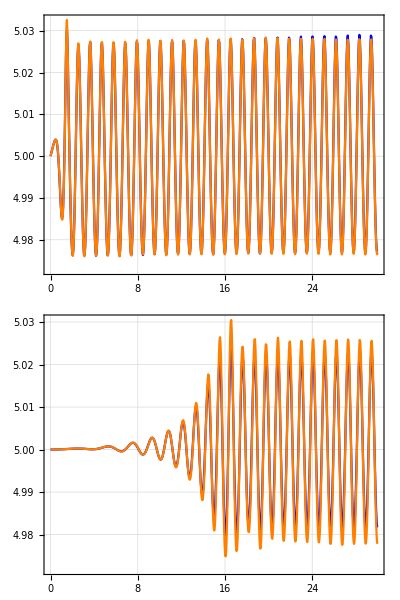
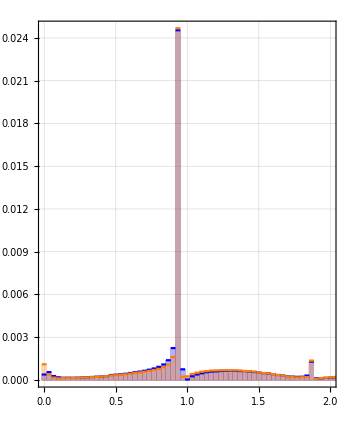
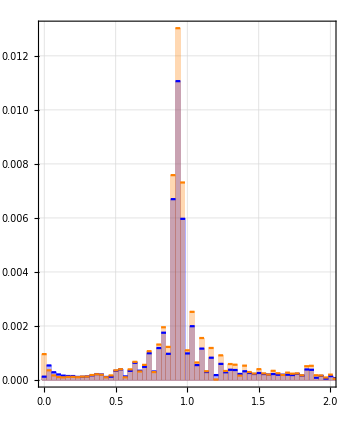
-Graphics-Time [s]water displacement [m]-Graphics--Graphics-Frequency [s^-1]water displacement [m]

/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/comparison_ALE_linear_and_pseudo.png

```mathematica
compare[jsons_]:=Module[{size,ratio},
size=700;
ratio=1/4;
Row[
{
Labeled[Column[Table[ListPlot[
Table[Select[Transpose[{importData[json,"simulation_time"],importData[json,name,3]}],start≤#[[1]]≤end&],{json,jsons}]
,PlotRange->{All,All}
,PlotStyle->{Blue,Orange,Black,Magenta}
,GridLines->Automatic
,AspectRatio->ratio
,ImageSize->size
,Joined->True
,Evaluate[plot2Doption]],
{name,{"gauge1_intersection","gauge23_intersection"}}]]
,framelabel["Time [s]","water displacement [m]",20,{0,Pi/2}],{Bottom,Left}
,ImageMargins->{{10,0},{0,0}}
],
Labeled[
Row[Table[ListStepPlot[Table[{#1,#2}&@@@(interpolateAndFourier[#1,#2]&@@Transpose[Select[Transpose[{importData[json,"simulation_time"],importData[json,name,3]-Mean@importData[json,name,3]}],start≤#[[1]]≤end&]]),{json,jsons}]
,Center
,PlotStyle->{Blue,Orange,Black,Magenta}
,GridLines->Automatic
,AspectRatio->ratio*2.2*2.2
,ImageSize->size/2
,PlotRange->{{0.,2},All(*,{0,0.026}*)}
,Joined->False
,Filling->Bottom
,Evaluate[plot2Doption]
],
{name,{"gauge1_intersection","gauge23_intersection"}}]]
,framelabel["Frequency [s^-1]","water displacement [m]",20,{0,Pi/2}],{Bottom,Left}
,ImageMargins->{{10,0},{0,0}}
]
}
]
]

(*線形補間：ALEに使う曲面として，擬2次補間を使うと伝播に伴う波の減衰を大幅に抑えることができる．*)
jsons={
"/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALElinear/result.json",
"/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALEpseudo_quad/result.json"};　
compare[jsons]
Export["/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/comparison_ALE_linear_and_pseudo.png",%]
```

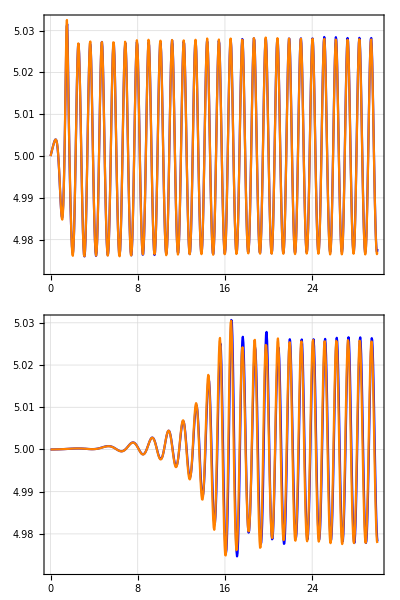
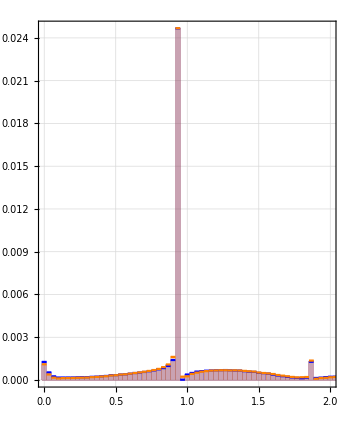
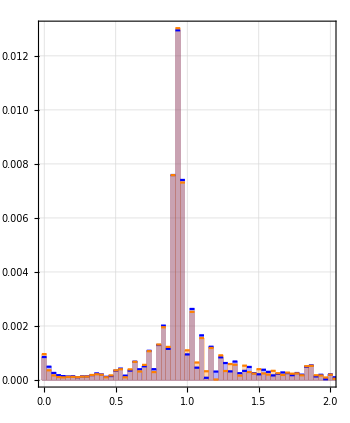
-Graphics-Time [s]water displacement [m]-Graphics--Graphics-Frequency [s^-1]water displacement [m]

/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/comparison_BVP_linear_and_pseudo.png

```mathematica
(*擬2次補間と線形補間：二つの振幅の違いはとても小さい．このことも線形補間でも十分な精度でシミュレーションできていることを示している．*)
jsons={
"/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMpseudo_quad_ALEpseudo_quad/result.json",
"/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALEpseudo_quad/result.json"};
compare[jsons]
Export["/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/comparison_BVP_linear_and_pseudo.png",%]
```

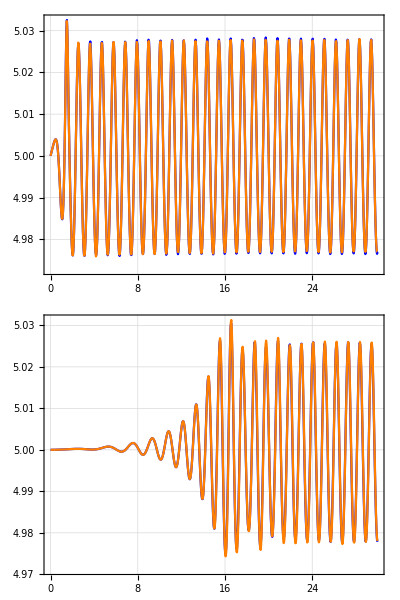
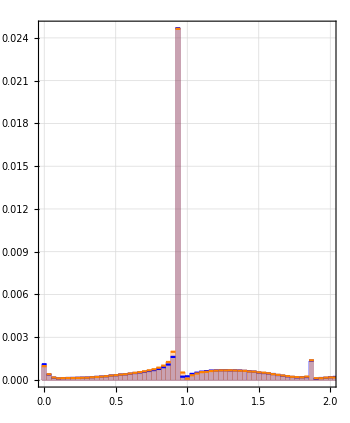
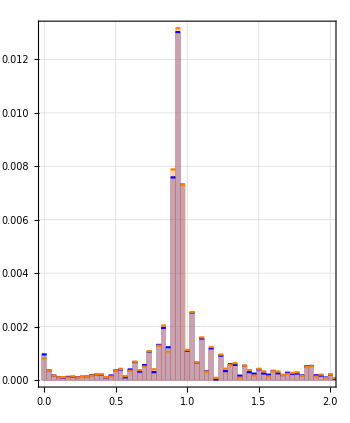
-Graphics-Time [s]water displacement [m]-Graphics--Graphics-Frequency [s^-1]water displacement [m]

/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/comparison_different_mesh.png

```mathematica
(*線形補間：メッシュを細かくしてもほとんど変わらない．この条件下では，線形補間であっても境界値問題をある程度の精度で解けており，時間発展もかなりの精度でできている．*)
jsons={
"/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALEpseudo_quad/result.json",
"/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d07_DT0d05_ELEMlinear_ALEpseudo_quad/result.json"};
compare[jsons]
Export["/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/comparison_different_mesh.png",%]
```

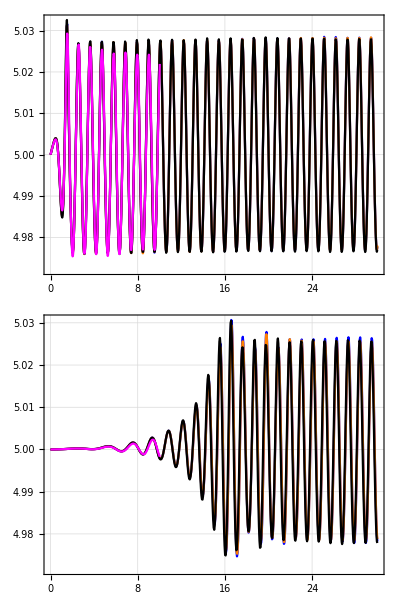
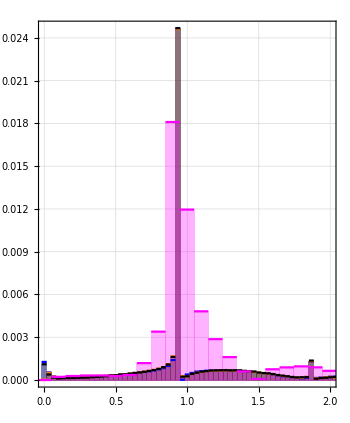
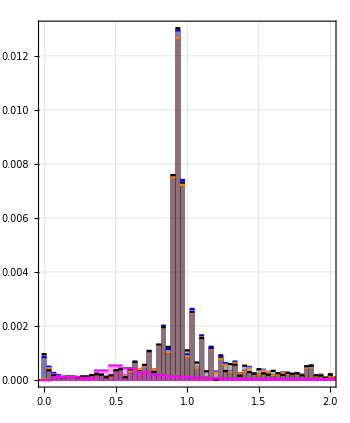
-Graphics-Time [s]water displacement [m]-Graphics--Graphics-Frequency [s^-1]water displacement [m]

/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/comparison_different_timestep.png

```mathematica
jsons={
"/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMpseudo_quad_ALEpseudo_quad/result.json",
"/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d025_ELEMpseudo_quad_ALEpseudo_quad/result.json",
"/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALEpseudo_quad/result.json",
"/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d025_ELEMlinear_ALEpseudo_quad/result.json"};
compare[jsons]
Export["/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/comparison_different_timestep.png",%]
```

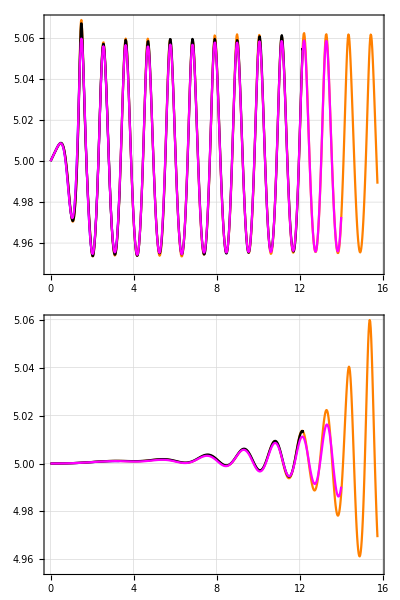
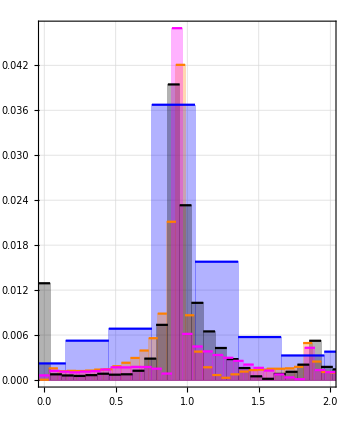
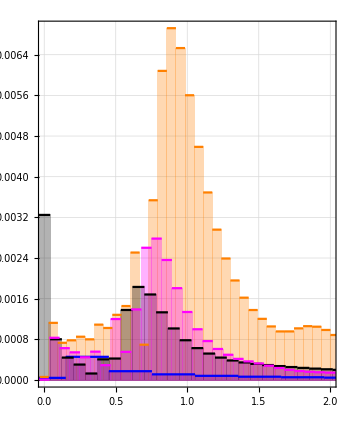
-Graphics-Time [s]water displacement [m]-Graphics--Graphics-Frequency [s^-1]water displacement [m]

```mathematica
jsons={
"/Users/tomoaki/BEM/Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d025_ELEMlinear_ALElinear/result.json",
"/Users/tomoaki/BEM/Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d025_ELEMlinear_ALEpseudo_quad/result.json",
"/Users/tomoaki/BEM/Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d025_ELEMpseudo_quad_ALEpseudo_quad/result.json",
"/Users/tomoaki/BEM/Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d025_ELEMpseudo_quad_ALElinear/result.json"};
compare[jsons]
(*Export["/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/comparison_BVP_linear_and_pseudo_H0d1.png",%]*)
```

```mathematica
Row[jsonInfo/@jsons]
```

no. | title | length
1 | cpu_time | 1238
2 | eq_of_motion | 1238
3 | gauge0_intersection | 1238
4 | gauge10_intersection | 1238
5 | gauge11_intersection | 1238
6 | gauge12_intersection | 1238
7 | gauge13_intersection | 1238
8 | gauge14_intersection | 1238
9 | gauge15_intersection | 1238
10 | gauge16_intersection | 1238
11 | gauge17_intersection | 1238
12 | gauge18_intersection | 1238
13 | gauge19_intersection | 1238
14 | gauge1_intersection | 1238
15 | gauge20_intersection | 1238
16 | gauge21_intersection | 1238
17 | gauge22_intersection | 1238
18 | gauge23_intersection | 1238
19 | gauge2_intersection | 1238
20 | gauge3_intersection | 1238
21 | gauge4_intersection | 1238
22 | gauge5_intersection | 1238
23 | gauge6_intersection | 1238
24 | gauge7_intersection | 1238
25 | gauge8_intersection | 1238
26 | gauge9_intersection | 1238
27 | simulation_time | 1238
28 | wall_clock_time | 1238
29 | water_E | 1238
30 | water_EK | 1238
31 | water_EP | 1238
32 | water_face_size | 1238
33 | water_point_size | 1238
34 | water_volume | 1238no. | title | length
1 | cpu_time | 15
2 | eq_of_motion | 15
3 | gauge0_intersection | 15
4 | gauge10_intersection | 15
5 | gauge11_intersection | 15
6 | gauge12_intersection | 15
7 | gauge13_intersection | 15
8 | gauge14_intersection | 15
9 | gauge15_intersection | 15
10 | gauge16_intersection | 15
11 | gauge17_intersection | 15
12 | gauge18_intersection | 15
13 | gauge19_intersection | 15
14 | gauge1_intersection | 15
15 | gauge20_intersection | 15
16 | gauge21_intersection | 15
17 | gauge22_intersection | 15
18 | gauge23_intersection | 15
19 | gauge2_intersection | 15
20 | gauge3_intersection | 15
21 | gauge4_intersection | 15
22 | gauge5_intersection | 15
23 | gauge6_intersection | 15
24 | gauge7_intersection | 15
25 | gauge8_intersection | 15
26 | gauge9_intersection | 15
27 | simulation_time | 15
28 | wall_clock_time | 15
29 | water_E | 15
30 | water_EK | 15
31 | water_EP | 15
32 | water_face_size | 15
33 | water_point_size | 15
34 | water_volume | 15no. | title | length
1 | cpu_time | 173
2 | eq_of_motion | 173
3 | gauge0_intersection | 173
4 | gauge10_intersection | 173
5 | gauge11_intersection | 173
6 | gauge12_intersection | 173
7 | gauge13_intersection | 173
8 | gauge14_intersection | 173
9 | gauge15_intersection | 173
10 | gauge16_intersection | 173
11 | gauge17_intersection | 173
12 | gauge18_intersection | 173
13 | gauge19_intersection | 173
14 | gauge1_intersection | 173
15 | gauge20_intersection | 173
16 | gauge21_intersection | 173
17 | gauge22_intersection | 173
18 | gauge23_intersection | 173
19 | gauge2_intersection | 173
20 | gauge3_intersection | 173
21 | gauge4_intersection | 173
22 | gauge5_intersection | 173
23 | gauge6_intersection | 173
24 | gauge7_intersection | 173
25 | gauge8_intersection | 173
26 | gauge9_intersection | 173
27 | simulation_time | 173
28 | wall_clock_time | 173
29 | water_E | 173
30 | water_EK | 173
31 | water_EP | 173
32 | water_face_size | 173
33 | water_point_size | 173
34 | water_volume | 173

{141.12,152.64,190.08,204.48}

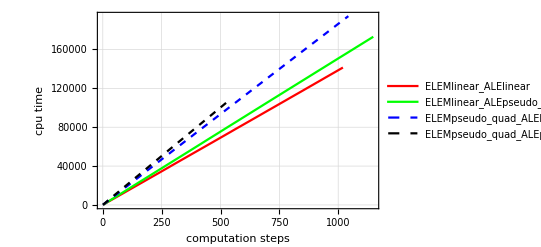

{141.12,152.64,190.08,204.48}

{1.,1.08163,1.34694,1.44898}

```mathematica
list={
"ELEMlinear_ALElinear",
"ELEMlinear_ALEpseudo_quad",
"ELEMpseudo_quad_ALElinear",
"ELEMpseudo_quad_ALEpseudo_quad"};
(*clist={5000,6000,7000,8000}*0.96;*)
clist={4900,5300,6600,7100}*0.96*0.03
Show[ListPlot[
Table[(*Transpose@{importData["/Users/tomoaki/BEM/Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d09_DT0d05_"<>name<>"/result.json","simulation_time"],*)
importData["/Users/tomoaki/BEM/Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d09_DT0d05_"<>name<>"/result.json","cpu_time"]
(*}*)
,{name,list}]
,FrameLabel->framelabel["computation steps","cpu time"]
,PlotStyle->{Red,{Green},{Blue,Dashed},{Black,Dashed}}
,PlotLegends->list
,GridLines->Automatic
(*,PlotRange->{{0,10},Automatic}*)
,Evaluate[plot2Doption]]
(*,
Plot[Table[c*x,{c,clist}],{x,0,10}]*)
]

clist
clist/clist[[1]]
```

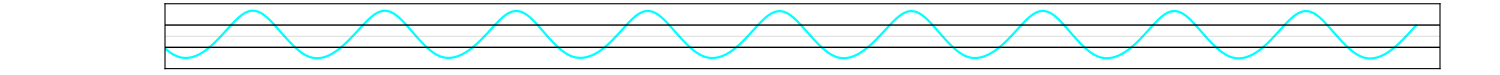
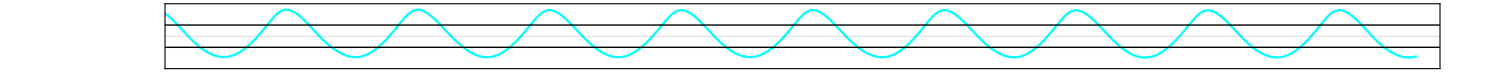
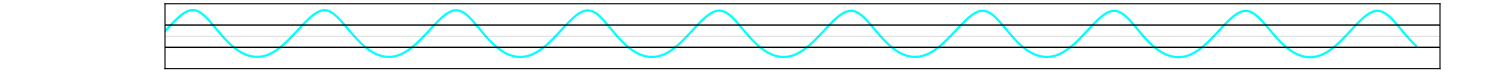
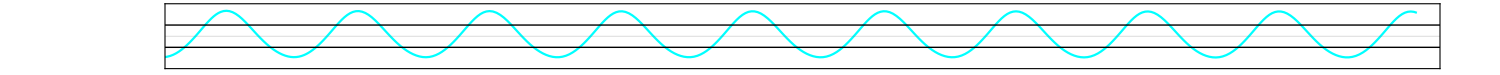
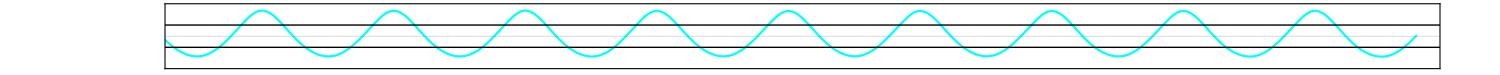
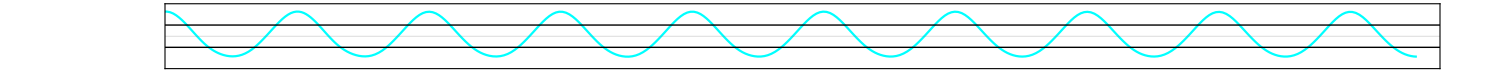
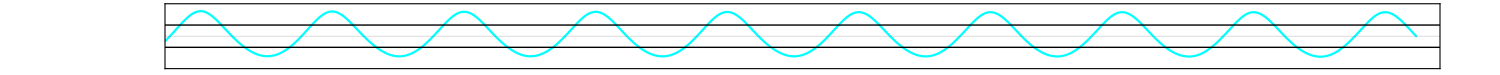
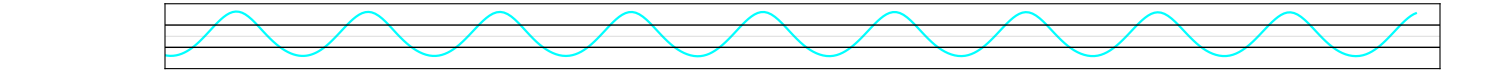
-Graphics-0.2
-Graphics-0.7
-Graphics-1.2
-Graphics-1.7
-Graphics-2.2
-Graphics-2.7
-Graphics-3.2
-Graphics-3.7
-Graphics-4.2
-Graphics-4.7
-Graphics-5.2
-Graphics-5.7
-Graphics-6.2
-Graphics-6.7
-Graphics-7.2
-Graphics-7.7
-Graphics-8.2
-Graphics-8.7
-Graphics-9.2
-Graphics-9.7
-Graphics-10.2
-Graphics-10.7
-Graphics-11.2
-Graphics-11.7

```mathematica
Column[ParallelTable[
Module[{data,DATA,position},
data="gauge"<>ToString[i]<>"_intersection";
Labeled[
ListPlot[
Table[{importData[json,"simulation_time"],(importData[json,data,3]-Mean[importData[json,data,3]])}ᵀ,{json,jsons}],
FrameTicks->False,
PlotStyle->{Blue,Cyan,Red,Orange},
ImageSize->1500,
AspectRatio->1/20,
PlotRange->{{20,30},{-0.035,0.035}*2},
Evaluate[plot2Doption],
Epilog->{Line[{{0,0.025},{100,0.025}}],Line[{{0,-0.025},{100,-0.025}}]}
]
,importData[jsons[[1]],data,1][[1]]
,Right]
],{i,0,23,1}]
,Spacings->0
]
```

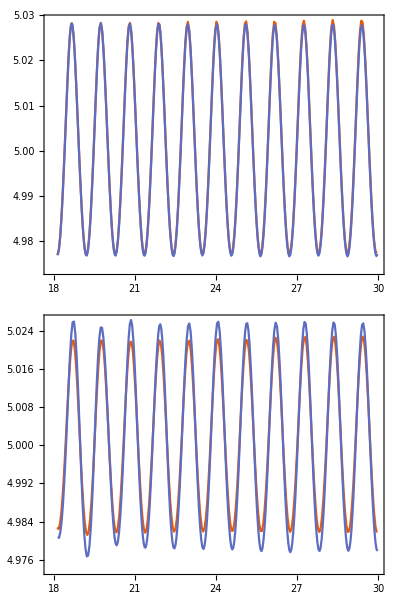

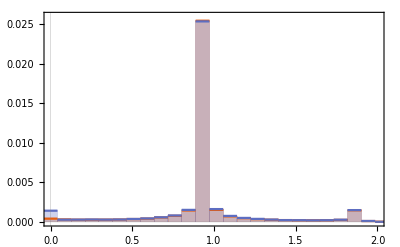
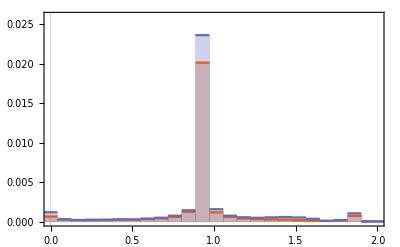

```mathematica
start=18.1;
end=30;
Column@Table[ListPlot[
Table[Select[Transpose[{importData[json,"simulation_time"],importData[json,name,3]}],start≤#[[1]]≤end&],{json,jsons}]
,AspectRatio->1/10
,ImageSize->1000
,Joined->True
,Evaluate[plot2Doption]],
{name,{"gauge1_intersection","gauge23_intersection"}}]
Row[
Table[ListStepPlot[Table[interpolateAndFourier[#1,#2]&@@Transpose[Select[Transpose[{importData[json,"simulation_time"],importData[json,name,3]-Mean@importData[json,name,3]}],start≤#[[1]]≤end&]],{json,jsons}]
,Center
,PlotRange->{{0.,2},{0,0.026}}
,Joined->False
,Filling->Bottom
,Evaluate[plot2Doption]
],
{name,{"gauge1_intersection","gauge23_intersection"}}]
]
```

```mathematica
Row[Table[BarChart[Table[interpolateAndFourier[#1,#2]&@@Transpose[Select[Transpose[{importData[json,"simulation_time"],importData[json,name,3]-Mean@importData[json,name,3]}],start≤#[[1]]≤end&]],{json,jsons}],ChartLayout->"Stacked",Evaluate[plot2Doption]],{name,{"gauge1_intersection","gauge23_intersection"}}]]
```

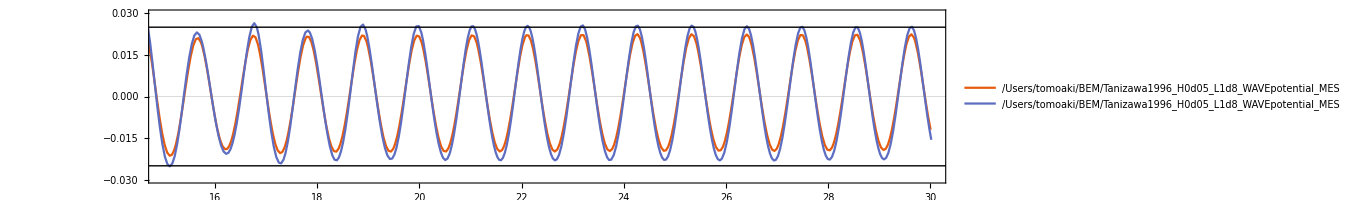

```mathematica
ListPlot[Table[
Module[{data,DATA,position},
data="gauge20_intersection";
DATA=importData[json,data,3];
position=importData[json,data,1][[1]];
{importData[json,"simulation_time"],(DATA-Mean[DATA])}ᵀ
],{json,jsons}],
PlotRange->{{15,30},{-0.03,0.03}},
Epilog->{Line[{{0,0.025},{100,0.025}}],Line[{{0,-0.025},{100,-0.025}}]},
ImageSize->1000,
AspectRatio->1/5,
Evaluate[plot2Doption],
PlotLegends->jsons
]
```

```mathematica
(*Mock-up for demonstration:Generates sample data similar to your structure*)
gaugeData=ParallelTable[
Module[{data,DATA,position,w,v,fourier},
data="gauge"<>ToString[i]<>"_intersection";
DATA=importData[json,data,3];
position=importData[json,data,1][[1]];
{w,v}=Transpose[interpolateAndFourierTr[{importData[json,"simulation_time"],(DATA-DATA[[1]])}ᵀ,{10,15}]];
Transpose[{Table[i,{j,1,Length[w]}],w,v}]
],{i,1,20,1}];

minmax=MinMax[#3&@@@Flatten[gaugeData,1]];

Graphics3D[Table[{ColorData["BlueGreenYellow"][gaugeData[[i,j,3]]/minmax[[2]]],
Cuboid[{
gaugeData[[i,j,1]],
gaugeData[[i,j,2]],0},
{gaugeData[[i,j,1]]+0.8,gaugeData[[i,j,2]]+0.095,gaugeData[[i,j,3]]}]},
{i,1,Length[gaugeData]},{j,1,Length[gaugeData[[i]]]}],Axes->True,BoxRatios->{1,1,1/2},PlotRange->{All,{0,3},All}]
```

Transpose::nmtx: The first two levels of {importData[json,simulation_time],-json+importData[json,gauge1_intersection,3]} cannot be transposed.

Transpose::nmtx: The first two levels of {importData[json,simulation_time],-json+importData[json,gauge3_intersection,3]} cannot be transposed.

Transpose::nmtx: The first two levels of {importData[json,simulation_time],-json+importData[json,gauge5_intersection,3]} cannot be transposed.

Transpose::nmtx: The first two levels of {importData[json,simulation_time],-json+importData[json,gauge7_intersection,3]} cannot be transposed.

Transpose::nmtx: The first two levels of {importData[json,simulation_time],-json+importData[json,gauge9_intersection,3]} cannot be transposed.

Transpose::nmtx: The first two levels of {importData[json,simulation_time],-json+importData[json,gauge10_intersection,3]} cannot be transposed.

Transpose::nmtx: The first two levels of {importData[json,simulation_time],-json+importData[json,gauge11_intersection,3]} cannot be transposed.

Transpose::nmtx: The first two levels of {importData[json,simulation_time],-json+importData[json,gauge12_intersection,3]} cannot be transposed.

Transpose::nmtx: The first two levels of {importData[json,simulation_time],-json+importData[json,gauge13_intersection,3]} cannot be transposed.

Transpose::nmtx: The first two levels of {importData[json,simulation_time],-json+importData[json,gauge14_intersection,3]} cannot be transposed.

Transpose::nmtx: The first two levels of {importData[json,simulation_time],-json+importData[json,gauge15_intersection,3]} cannot be transposed.

Transpose::nmtx: The first two levels of {importData[json,simulation_time],-json+importData[json,gauge16_intersection,3]} cannot be transposed.

Transpose::nmtx: The first two levels of {importData[json,simulation_time],-json+importData[json,gauge17_intersection,3]} cannot be transposed.

Transpose::nmtx: The first two levels of {importData[json,simulation_time],-json+importData[json,gauge18_intersection,3]} cannot be transposed.

Transpose::nmtx: The first two levels of {importData[json,simulation_time],-json+importData[json,gauge19_intersection,3]} cannot be transposed.

Transpose::nmtx: The first two levels of {importData[json,simulation_time],-json+importData[json,gauge20_intersection,3]} cannot be transposed.

Set::shape: Lists {w$2635,v$2635} and Transpose[interpolateAndFourierTr[Transpose[{importData[json,simulation_time],-json+importData[json,gauge1_intersection,3]}],{10,15}]] are not the same shape.

Set::shape: Lists {w$2635,v$2635} and Transpose[interpolateAndFourierTr[Transpose[{importData[json,simulation_time],-json+importData[json,gauge3_intersection,3]}],{10,15}]] are not the same shape.

Set::shape: Lists {w$2635,v$2635} and Transpose[interpolateAndFourierTr[Transpose[{importData[json,simulation_time],-json+importData[json,gauge5_intersection,3]}],{10,15}]] are not the same shape.

Set::shape: Lists {w$2635,v$2635} and Transpose[interpolateAndFourierTr[Transpose[{importData[json,simulation_time],-json+importData[json,gauge7_intersection,3]}],{10,15}]] are not the same shape.

Set::shape: Lists {w$2635,v$2635} and Transpose[interpolateAndFourierTr[Transpose[{importData[json,simulation_time],-json+importData[json,gauge9_intersection,3]}],{10,15}]] are not the same shape.

Set::shape: Lists {w$2635,v$2635} and Transpose[interpolateAndFourierTr[Transpose[{importData[json,simulation_time],-json+importData[json,gauge10_intersection,3]}],{10,15}]] are not the same shape.

Set::shape: Lists {w$2635,v$2635} and Transpose[interpolateAndFourierTr[Transpose[{importData[json,simulation_time],-json+importData[json,gauge11_intersection,3]}],{10,15}]] are not the same shape.

Set::shape: Lists {w$2635,v$2635} and Transpose[interpolateAndFourierTr[Transpose[{importData[json,simulation_time],-json+importData[json,gauge12_intersection,3]}],{10,15}]] are not the same shape.

Set::shape: Lists {w$1814,v$1814} and Transpose[interpolateAndFourierTr[Transpose[{importData[json,simulation_time],-json+importData[json,gauge13_intersection,3]}],{10,15}]] are not the same shape.

Set::shape: Lists {w$1814,v$1814} and Transpose[interpolateAndFourierTr[Transpose[{importData[json,simulation_time],-json+importData[json,gauge14_intersection,3]}],{10,15}]] are not the same shape.

Set::shape: Lists {w$1814,v$1814} and Transpose[interpolateAndFourierTr[Transpose[{importData[json,simulation_time],-json+importData[json,gauge15_intersection,3]}],{10,15}]] are not the same shape.

Set::shape: Lists {w$1814,v$1814} and Transpose[interpolateAndFourierTr[Transpose[{importData[json,simulation_time],-json+importData[json,gauge16_intersection,3]}],{10,15}]] are not the same shape.

Set::shape: Lists {w$1814,v$1814} and Transpose[interpolateAndFourierTr[Transpose[{importData[json,simulation_time],-json+importData[json,gauge17_intersection,3]}],{10,15}]] are not the same shape.

Set::shape: Lists {w$1814,v$1814} and Transpose[interpolateAndFourierTr[Transpose[{importData[json,simulation_time],-json+importData[json,gauge18_intersection,3]}],{10,15}]] are not the same shape.

Set::shape: Lists {w$1814,v$1814} and Transpose[interpolateAndFourierTr[Transpose[{importData[json,simulation_time],-json+importData[json,gauge19_intersection,3]}],{10,15}]] are not the same shape.

Set::shape: Lists {w$1814,v$1814} and Transpose[interpolateAndFourierTr[Transpose[{importData[json,simulation_time],-json+importData[json,gauge20_intersection,3]}],{10,15}]] are not the same shape.

Transpose::nmtx: The first two levels of {{},w$2635,v$2635} cannot be transposed.

Transpose::nmtx: The first two levels of {{},w$1814,v$1814} cannot be transposed.

Transpose::nmtx: The first two levels of {importData[json,simulation_time],-json+importData[json,gauge2_intersection,3]} cannot be transposed.

Transpose::nmtx: The first two levels of {importData[json,simulation_time],-json+importData[json,gauge4_intersection,3]} cannot be transposed.

Transpose::nmtx: The first two levels of {importData[json,simulation_time],-json+importData[json,gauge6_intersection,3]} cannot be transposed.

Transpose::nmtx: The first two levels of {importData[json,simulation_time],-json+importData[json,gauge8_intersection,3]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Set::shape: Lists {w$2640,v$2640} and Transpose[interpolateAndFourierTr[Transpose[{importData[json,simulation_time],-json+importData[json,gauge2_intersection,3]}],{10,15}]] are not the same shape.

Set::shape: Lists {w$2640,v$2640} and Transpose[interpolateAndFourierTr[Transpose[{importData[json,simulation_time],-json+importData[json,gauge4_intersection,3]}],{10,15}]] are not the same shape.

Set::shape: Lists {w$2640,v$2640} and Transpose[interpolateAndFourierTr[Transpose[{importData[json,simulation_time],-json+importData[json,gauge6_intersection,3]}],{10,15}]] are not the same shape.

Set::shape: Lists {w$2640,v$2640} and Transpose[interpolateAndFourierTr[Transpose[{importData[json,simulation_time],-json+importData[json,gauge8_intersection,3]}],{10,15}]] are not the same shape.

Transpose::nmtx: {{},w$2635,v$2635}の最初の2個のレベルは転置できません．

Transpose::nmtx: {{},w$2640,v$2640}の最初の2個のレベルは転置できません．

Transpose::nmtx: {{},w$2635,v$2635}の最初の2個のレベルは転置できません．

General::stop: この計算中に，Transpose::nmtxのこれ以上の出力は表示されません．

Function::slotn: #3&のスロット番号3を(#3&)[{{},w$2635,v$2635}]から満たすことができません．

Function::slotn: #3&のスロット番号3を(#3&)[{{},w$2640,v$2640}]から満たすことができません．

Function::slotn: #3&のスロット番号3を(#3&)[{{},w$2635,v$2635}]から満たすことができません．

General::stop: この計算中に，Function::slotnのこれ以上の出力は表示されません．

-Graphics3D-